```mathematica
brstcanc=Import["C:\\Users\\oreol\\Desktop\\proj\\MTBLS92class.xlsx"];
```

```mathematica
databrst=Flatten[brstcanc,1] ;
defColNames[databrst,1];
brst= brstPipeline[databrst];
```

```mathematica
databrst//TableForm;
```

```mathematica
Dimensions[databrst]
```

{448,150}

```mathematica
defColNames[brst,1];
bC=DeleteMissing[brst,1,Infinity];
```

```mathematica
bC//TableForm;
```

```mathematica
bC[[143;;]]//TableForm;
```

```mathematica
Dimensions[bC]
```

{252,141}

```mathematica
class1=Select[bC,#⟦class⟧==1&];
class1⟦;;5⟧//TableForm
```

143. | 1. | 1. | 23. | 58.5698 | 1.97292 | 0.564853 | 0.933236 | 20.2863 | 9.57274 | 20.2439 | 13.6318 | 4.1531 | 2.40058 | 3.12981 | 0.676373 | 2.87629 | 4.77802 | 12.5362 | 1.6882 | 8.77343 | 3.77368 | 2.64654 | 37.6575 | 62.9319 | 162.603 | 72.0953 | 305.617 | 4.05632 | 153.799 | 1.00312 | 1.80166 | 124.43 | 38.0007 | 201.905 | 45.6102 | 1.18 | 158.896 | 16.9371 | 52.9323 | 24.7944 | 147.203 | 106.158 | 2.94521 | 0.845054 | 20.4559 | 69.7364 | 27.6305 | 8.20849 | 1.89802 | 9.37227 | 57.1488 | 40.2507 | 3.51846 | 0.724757 | 0.768852 | 1.0301 | 3.77019 | 4.66114 | 17.9238 | 16.1016 | 1.93091 | 8.22902 | 52.9194 | 33.0933 | 14.4241 | 20.3145 | 246.648 | 15.1219 | 17.3816 | 13.9171 | 6.37194 | 42.2639 | 6.65182 | 8.86687 | 3.5703 | 12.134 | 5.81125 | 2.29048 | 3.00668 | 10.2823 | 7.372 | 1.74019 | 5.26004 | 5.30628 | 3.84791 | 5.71981 | 25.4561 | 0.259393 | 14.2057 | 8.37033 | 21.3335 | 32.6431 | 4.67668 | 1.28587 | 30.0198 | 9.07683 | 52.3074 | 167.377 | 26.1275 | 172.999 | 1.62707 | 0.785403 | 22.8302 | 18.3541 | 1.02115 | 30.6632 | 1.88497 | 0.890124 | 4.20911 | 2.71051 | 1.04426 | 1.15192 | 7.861 | 2.82461 | 1.15192 | 2.08426 | 8.39936 | 3.00715 | 1.62317 | 4.59107 | 2.47478 | 0.103539 | 12.6493 | 2.0633 | 0.523602 | 8.00531 | 3.09757 | 0.599655 | 3.35764 | 0.890124 | 3.05267 | 5.54559 | 1.96025 | 7.25639 | 3.81953 | 2.34572 | 6.71696 | 4.24129 | 5.82993 | 0.62231
144. | 1. | 1. | 29. | 51.9979 | 1.227 | 0.742312 | 1.526 | 27.4471 | 13.0502 | 24.7292 | 13.124 | 5.39142 | 3.37908 | 4.72971 | 0.894676 | 2.85243 | 2.5251 | 10.9064 | 1.31958 | 9.35908 | 3.9656 | 2.37549 | 63.6391 | 54.9506 | 135.607 | 76.2274 | 317.089 | 3.00563 | 163.02 | 1.06782 | 2.24637 | 128.32 | 26.4228 | 197.742 | 72.5819 | 1.20056 | 137.995 | 16.7687 | 56.9253 | 10.3976 | 215.03 | 120.821 | 2.68639 | 0.84387 | 53.6701 | 103.34 | 29.9396 | 8.58369 | 1.32997 | 15.9961 | 44.7968 | 31.7484 | 3.6842 | 0.758898 | 0.704279 | 2.23624 | 3.31696 | 8.9383 | 21.0771 | 18.0335 | 1.39878 | 10.8736 | 39.8361 | 25.9088 | 26.0754 | 19.3538 | 252.519 | 11.6991 | 16.4196 | 15.3246 | 4.40564 | 44.5013 | 7.31584 | 9.21497 | 4.30338 | 15.8872 | 6.9344 | 3.06466 | 4.22567 | 11.6669 | 10.2983 | 2.24377 | 5.02818 | 7.48204 | 4.42537 | 6.48593 | 16.1143 | 0.263092 | 12.2916 | 10.3348 | 35.4902 | 84.9181 | 4.75169 | 1.23995 | 27.7935 | 0.864452 | 70.2347 | 285.349 | 27.2645 | 486.647 | 2.4295 | 3.13823 | 165.734 | 42.901 | 1.61244 | 97.3667 | 1.18791 | 0.459834 | 3.73626 | 2.40158 | 0.839646 | 1.04057 | 10.0675 | 5.44809 | 1.4509 | 1.62749 | 28.4699 | 9.99249 | 2.18238 | 4.39921 | 4.56587 | 0.385228 | 80.436 | 13.1347 | 1.59091 | 11.5281 | 7.12111 | 2.47663 | 17.3093 | 1.57993 | 5.63208 | 3.07983 | 1.49111 | 10.1547 | 9.86441 | 2.29125 | 6.46156 | 7.61369 | 7.36065 | 1.01564
145. | 1. | 1. | 24. | 38.1716 | 1.53482 | 0.94114 | 2.37276 | 21.5238 | 16.2045 | 25.6426 | 20.0244 | 3.28027 | 2.90736 | 5.14907 | 0.809756 | 4.18079 | 3.49001 | 15.1567 | 1.81646 | 16.7617 | 3.6544 | 1.30629 | 54.8224 | 41.4108 | 244.795 | 41.2933 | 431.738 | 2.54689 | 90.6712 | 0.725409 | 2.69228 | 96.4947 | 37.4683 | 244.949 | 69.2236 | 1.24159 | 213.25 | 14.7113 | 55.341 | 10.6339 | 98.5587 | 49.3588 | 3.24585 | 0.60853 | 35.4789 | 84.2543 | 32.8219 | 7.78478 | 1.07401 | 12.1854 | 49.9144 | 36.8228 | 2.43667 | 0.389835 | 0.453456 | 2.35409 | 1.97136 | 6.0507 | 19.6596 | 15.7552 | 1.95097 | 7.6586 | 36.6731 | 13.8974 | 13.6222 | 14.5197 | 134.352 | 19.6977 | 12.2984 | 8.1487 | 4.04519 | 53.5225 | 5.34553 | 7.79913 | 5.08131 | 15.6295 | 8.05409 | 2.78022 | 3.6996 | 14.546 | 8.7651 | 1.84809 | 6.17962 | 6.13411 | 2.38662 | 8.77266 | 30.2931 | 0.289346 | 27.9133 | 34.0335 | 116.299 | 353.614 | 13.5041 | 3.17715 | 65.9437 | 9.34881 | 327.095 | 1018.85 | 58.9398 | 1061.29 | 7.90899 | 5.22077 | 289.353 | 126.575 | 3.29713 | 219.559 | 3.42687 | 0.964146 | 7.75108 | 5.01777 | 1.55485 | 2.43284 | 27.4093 | 9.18566 | 4.93406 | 4.29038 | 62.2077 | 20.93 | 3.63735 | 11.399 | 13.0679 | 0.648847 | 202.181 | 27.1377 | 2.84744 | 35.822 | 19.4117 | 2.88203 | 31.6051 | 2.56252 | 14.5357 | 3.02962 | 2.97437 | 33.6189 | 20.2737 | 3.07027 | 8.05254 | 15.4316 | 14.7255 | 2.63939
146. | 1. | 1. | 38. | 55.21 | 2.13358 | 0.786659 | 2.75593 | 31.4581 | 21.0734 | 38.4759 | 22.8813 | 6.86747 | 4.47072 | 4.67007 | 0.555288 | 4.17793 | 3.45094 | 10.9317 | 1.4843 | 26.8991 | 3.56722 | 2.17412 | 58.8696 | 43.1563 | 235.418 | 57.7428 | 372.885 | 3.62398 | 177.46 | 1.29831 | 5.46353 | 93.4565 | 54.9786 | 222.412 | 62.3371 | 1.20185 | 169.866 | 18.0942 | 50.8331 | 13.6593 | 168.123 | 67.717 | 2.42764 | 0.583014 | 31.5298 | 78.0853 | 28.2962 | 6.0033 | 1.35552 | 10.5376 | 35.9141 | 43.4827 | 3.56444 | 0.740055 | 0.698693 | 1.28794 | 3.36033 | 5.70058 | 24.1267 | 14.3406 | 1.21553 | 9.10203 | 39.9931 | 25.96 | 13.522 | 10.7408 | 196.382 | 8.08295 | 17.4745 | 6.87101 | 3.49949 | 34.3365 | 5.47596 | 8.27733 | 3.18294 | 14.9539 | 7.18351 | 2.19886 | 2.6161 | 15.1102 | 9.04557 | 2.06565 | 5.54693 | 4.22468 | 2.43247 | 8.71961 | 21.4236 | 0.14126 | 10.5728 | 14.9271 | 37.189 | 78.1725 | 5.49752 | 1.31709 | 36.0733 | 10.9542 | 103.306 | 309.004 | 35.7397 | 256.461 | 1.33531 | 0.509736 | 32.3578 | 37.5579 | 1.764 | 44.1586 | 0.891283 | 0.407399 | 3.17495 | 1.61157 | 0.54174 | 0.705599 | 9.35821 | 2.41561 | 1.1141 | 1.48561 | 14.3943 | 2.84546 | 1.33988 | 2.7902 | 2.19277 | 0.163804 | 24.5555 | 3.0577 | 0.64407 | 6.91928 | 2.59493 | 0.548772 | 5.68465 | 0.776676 | 1.9607 | 4.45461 | 2.43275 | 14.1871 | 2.82062 | 1.26614 | 2.04735 | 5.02151 | 2.40383 | 0.680209
147. | 1. | 2. | 29. | 43.4348 | 1.51023 | 0.646998 | 2.69877 | 19.3826 | 20.2563 | 22.587 | 29.5768 | 4.96917 | 5.49691 | 6.13438 | 0.745414 | 6.86107 | 4.28205 | 18.6455 | 1.79716 | 36.227 | 3.10981 | 2.38745 | 127.845 | 69.4898 | 324.855 | 78.1269 | 397.553 | 3.9862 | 163.763 | 0.924018 | 7.44177 | 154.388 | 64.5557 | 247.032 | 134.837 | 1.7524 | 255.54 | 7.4662 | 63.7799 | 17.1007 | 201.078 | 139.074 | 5.03341 | 0.657236 | 72.887 | 130.179 | 47.3703 | 6.38216 | 1.78466 | 27.0343 | 94.218 | 63.3675 | 1.51657 | 1.16641 | 0.778962 | 3.79824 | 3.73498 | 13.5815 | 53.9723 | 18.0892 | 3.50227 | 9.76761 | 102.856 | 33.736 | 31.3152 | 23.3749 | 249.529 | 29.8839 | 14.7944 | 13.4398 | 3.95547 | 55.5592 | 6.79127 | 15.2182 | 5.41701 | 16.474 | 7.13 | 3.26193 | 4.11185 | 15.3799 | 7.54605 | 2.1285 | 7.27756 | 5.91559 | 2.51372 | 8.50721 | 26.4345 | 0.24307 | 34.9503 | 75.1479 | 219.518 | 410.588 | 23.7544 | 2.74549 | 162.431 | 12.1387 | 612.33 | 1417.77 | 142.125 | 992.64 | 15.357 | 4.49076 | 161.178 | 364.136 | 7.40548 | 197.603 | 1.48721 | 0.48561 | 5.69919 | 3.60319 | 0.681393 | 1.11366 | 33.1816 | 6.35413 | 3.89578 | 5.28534 | 78.8058 | 8.73791 | 5.21667 | 22.088 | 13.7453 | 0.70714 | 137.013 | 10.7527 | 1.04412 | 54.8676 | 15.6399 | 1.31896 | 13.5654 | 1.13966 | 14.2535 | 4.46566 | 6.01536 | 67.0252 | 16.0973 | 10.7919 | 42.8391 | 54.4214 | 75.0656 | 6.04852

```mathematica
class0=Select[brst,#⟦class⟧==0&];
class0⟦;;5⟧//TableForm
```

1. | 0. | 2. | 35. | 58.8991 | 1.75991 | 0.908453 | 1.20021 | 32.7219 | 11.7879 | 20.8397 | 24.5377 | 7.76126 | 3.03616 | 3.72571 | 0.784752 | 5.78649 | 2.34631 | 10.4006 | 1.33338 | 7.94976 | 2.03827 | 2.29975 | 32.0333 | 40.9595 | 126.835 | 45.2861 | 326.968 | 6.65096 | 89.765 | 0.526842 | 1.84478 | 86.9391 | 26.8252 | 201.26 | 17.8447 | 2.1424 | 162.741 | 7.73322 | 46.7393 | 31.3655 | 144.066 | 61.7259 | 2.96373 | 0.869738 | 24.0144 | 72.2117 | 24.3233 | 9.90397 | 1.62418 | 9.82832 | 78.4959 | 54.0171 | 1.70624 | 0.731451 | 0.453096 | 1.83419 | 3.83295 | 5.2347 | 25.863 | 19.8097 | 1.88935 | 5.68133 | 29.8637 | 18.5467 | 12.4889 | 11.2048 | 285.464 | 11.0366 | 9.72735 | 11.9037 | 3.0579 | 34.0799 | 5.562 | 7.64093 | 3.5718 | 10.7548 | 6.15699 | 2.09284 | 1.90565 | 11.3581 | 5.96804 | 1.90899 | 5.12656 | 2.69366 | 3.40622 | 6.53255 | 30.9556 | 0.206685 | 15.7116 | 20.3291 | 66.9136 | 162.514 | 9.12282 | 1.82207 | 78.8261 | 7.87114 | 219.992 | 727.117 | 122.929 | 672.829 | 4.39044 | 2.52471 | 130.91 | 323.709 | 12.499 | 367.48 | 1.55303 | 1.12574 | 3.25873 | 2.84336 | 2.08194 | 1.24424 | 11.7316 | 5.70027 | 2.01449 | 2.25149 | 29.4248 | 9.20127 | 2.21113 | 7.21316 | 4.3696 | 0.31051 | 74.2324 | 9.97116 | 2.13095 | 15.2785 | 7.01063 | 1.88639 | 25.6445 | 3.24557 | 9.96345 | 3.97632 | 6.03321 | 20.7378 | 39.5186 | 4.37218 | 15.0999 | 15.5208 | 29.7603 | 2.89018
2. | 0. | 2. | 23. | 66.0454 | 2.66583 | 0.814964 | 2.31367 | 37.6484 | 21.8452 | 40.6241 | 18.0332 | 8.26362 | 4.80378 | 7.67614 | 0.780442 | 4.14037 | 1.70982 | 8.37068 | 1.29829 | 5.28535 | 3.42094 | 1.90442 | 48.4349 | 51.5657 | 145.589 | 42.863 | 462.381 | 2.75375 | 81.5359 | 0.558595 | 1.39502 | 128.56 | 26.373 | 271.308 | 62.2889 | 1.05602 | 138.011 | 17.7898 | 81.4012 | 6.05955 | 94.5974 | 89.0106 | 2.11356 | 0.551125 | 35.8414 | 75.9694 | 22.9233 | 7.24566 | 1.3761 | 12.3289 | 54.7236 | 31.7594 | 3.71229 | 0.283265 | 0.807915 | 1.05053 | 3.97202 | 7.24159 | 20.0288 | 15.5527 | 1.93785 | 9.68027 | 37.3248 | 28.9391 | 14.4955 | 15.5688 | 177.334 | 12.6834 | 13.2004 | 9.79408 | 3.80795 | 38.6008 | 5.2303 | 8.72146 | 4.48742 | 17.1863 | 8.75756 | 1.95313 | 3.07706 | 18.1002 | 8.61884 | 2.65139 | 6.0117 | 3.9483 | 3.94428 | 9.06093 | 21.8319 | 0.157539 | 8.74602 | 9.04303 | 18.1047 | 69.9977 | 4.94475 | 2.82417 | 50.6127 | 0.999962 | 74.4045 | 611.92 | 74.4498 | 928.731 | 3.39358 | 4.34562 | 274.01 | 133.35 | 2.60473 | 275.826 | 1.28459 | 0.285384 | 2.87508 | 0.86511 | 0.49713 | 1.42692 | 4.11967 | 1.98048 | 2.89521 | 1.53255 | 13.8945 | 4.65016 | 2.1773 | 3.33843 | 3.5732 | 0.238264 | 66.6677 | 11.9267 | 1.24347 | 11.8106 | 9.02641 | 1.88141 | 12.0667 | 1.69038 | 12.1065 | 5.00667 | 7.11292 | 17.0302 | 14.5132 | 2.96192 | 16.137 | 13.4611 | 11.7176 | 1.21363
3. | 0. | 2. | 28. | 46.1064 | 1.94653 | 1.34354 | 1.5799 | 35.4989 | 14.9983 | 26.7146 | 24.687 | 7.9386 | 4.28675 | 3.61714 | 0.906341 | 5.37161 | 2.51015 | 9.10929 | 1.64218 | 11.8271 | 3.08678 | 2.13245 | 54.2249 | 63.3671 | 144.037 | 58.1035 | 364.49 | 4.08943 | 112.77 | 1.06282 | 2.43741 | 122.811 | 33.4395 | 224.555 | 70.3548 | 1.46736 | 198.44 | 15.6616 | 58.5155 | 25.9063 | 146.683 | 126.698 | 3.24298 | 1.06225 | 42.3396 | 103.251 | 41.0366 | 7.69721 | 1.51649 | 15.101 | 95.1207 | 35.8373 | 3.07462 | 0.552736 | 0.727282 | 1.22479 | 3.92901 | 8.29378 | 34.0799 | 25.8554 | 1.85981 | 6.76168 | 40.0896 | 28.349 | 22.0899 | 18.9673 | 263.987 | 14.8311 | 16.6842 | 17.7896 | 5.52904 | 53.1409 | 6.47726 | 14.2472 | 4.07248 | 16.003 | 9.61394 | 3.29538 | 5.00678 | 16.9168 | 9.21563 | 2.94429 | 7.24074 | 5.09545 | 4.5409 | 11.2033 | 43.0337 | 0.33903 | 9.24889 | 12.6555 | 54.6386 | 171.874 | 6.248 | 1.42083 | 60.5205 | 9.19623 | 160.987 | 745.085 | 79.7718 | 1083.06 | 5.65414 | 4.0855 | 273.999 | 123.57 | 4.54343 | 233.472 | 0.433581 | 0.426874 | 1.60425 | 1.17067 | 0.486067 | 0.737087 | 9.14742 | 3.52487 | 1.3901 | 2.55813 | 34.2492 | 10.5203 | 1.71264 | 6.62812 | 6.89268 | 0.433487 | 120.348 | 15.1602 | 1.95168 | 22.9635 | 12.2577 | 2.27456 | 31.9665 | 2.30617 | 12.406 | 5.27922 | 3.23825 | 23.5866 | 13.2487 | 4.77571 | 16.4187 | 18.9862 | 25.6612 | 1.7247
4. | 0. | 2. | 33. | 60.1233 | 2.086 | 1.26877 | 3.61236 | 36.1616 | 18.6413 | 25.6888 | 25.5232 | 7.33435 | 4.04677 | 5.56065 | 1.17117 | 6.14757 | 2.74688 | 15.0123 | 1.76716 | 19.8109 | 2.43556 | 3.28011 | 54.4817 | 45.0045 | 214.488 | 60.1652 | 271.734 | 1.81357 | 95.5082 | 0.628087 | 4.77922 | 103.381 | 34.6298 | 197.844 | 54.3775 | 0.995901 | 167.771 | 6.65202 | 47.8461 | 29.0603 | 169.161 | 63.7873 | 2.45155 | 0.560031 | 37.4148 | 81.6637 | 33.0004 | 6.56296 | 1.50764 | 12.7078 | 89.4644 | 49.4456 | 1.48556 | 0.603411 | 0.662038 | 1.19587 | 2.82938 | 8.16516 | 37.2205 | 19.9951 | 2.24224 | 7.34109 | 45.5064 | 18.9033 | 14.0564 | 16.0006 | 175.123 | 14.13 | 15.4309 | 16.0058 | 4.80858 | 53.4522 | 8.06697 | 17.4058 | 5.78549 | 21.0892 | 7.42022 | 4.05149 | 3.1472 | 20.232 | 9.16513 | 2.69929 | 9.04019 | 4.24636 | 3.1733 | 11.3768 | 46.2578 | 0.381945 | 9.17288 | 9.50458 | 34.472 | 159.976 | 5.08815 | 1.10165 | 40.6664 | 10.5356 | 95.051 | 703.442 | 39.7979 | 504.151 | 3.48749 | 1.72843 | 82.0384 | 59.2169 | 2.95839 | 28.3384 | 0.71838 | 0.537889 | 2.86874 | 1.85273 | 0.896482 | 1.31484 | 8.58944 | 3.1078 | 1.7332 | 2.55835 | 20.4954 | 5.77589 | 1.85273 | 4.68226 | 5.41578 | 0.361504 | 72.8578 | 4.44992 | 0.896482 | 16.9074 | 5.92232 | 0.928552 | 6.5093 | 0.84653 | 6.64477 | 4.35954 | 2.00379 | 14.7337 | 6.09204 | 2.10137 | 10.1462 | 8.36428 | 13.9609 | 0.816202
5. | 0. | 2. | 33. | 60.5464 | 2.02166 | 0.906071 | 1.79356 | 2.07633 | 17.5526 | 27.5295 | 21.4497 | 5.64613 | 3.9668 | 7.16866 | 0.964107 | 5.38569 | 3.81487 | 12.4504 | 1.82534 | 11.4138 | 3.13806 | 2.31617 | 67.0038 | 62.9231 | 187.405 | 55.631 | 373.198 | 2.47978 | 114.745 | 1.14932 | 2.71692 | 137.688 | 34.8459 | 247.801 | 57.9632 | 0.822153 | 173.69 | 15.9903 | 69.6106 | 25.499 | 141.296 | 82.0734 | 2.97099 | 0.882459 | 33.4208 | 85.9211 | 30.3421 | 6.57114 | 1.67578 | 11.1264 | 74.5022 | 40.1198 | 3.20185 | 0.628781 | 0.797316 | 1.1613 | 3.43564 | 6.78526 | 28.519 | 17.2537 | 1.6693 | 6.45851 | 38.6629 | 25.7198 | 21.0419 | 17.8236 | 170.601 | 11.8725 | 16.3526 | 11.7138 | 4.23298 | 41.7634 | 6.28764 | 13.2173 | 5.19161 | 19.3661 | 7.96384 | 3.66319 | 3.63463 | 15.214 | 7.62725 | 2.3922 | 6.99878 | 4.17084 | 2.75577 | 8.20383 | 27.2034 | 0.27999 | 28.5848 | 25.845 | 50.7846 | 87.794 | 12.8653 | 3.20513 | 59.3885 | 8.75433 | 139.242 | 426.113 | 40.9573 | 449.642 | 3.11249 | 1.78913 | 74.1941 | 46.1886 | 1.74914 | 59.0649 | 3.33655 | 1.77282 | 8.54948 | 6.02291 | 2.58124 | 1.805 | 14.8225 | 9.19937 | 3.17502 | 2.73493 | 26.5732 | 8.02929 | 2.56275 | 7.09381 | 5.48825 | 0.363146 | 47.0017 | 6.20485 | 1.54319 | 11.8662 | 5.27215 | 1.13356 | 9.92262 | 1.75569 | 6.06659 | 4.56506 | 3.45653 | 15.3712 | 6.09153 | 1.3183 | 7.04768 | 6.19717 | 6.99426 | 0.75451

comparing menopause and class

```mathematica
Tally[bC[[;;,menopause]]]//TableForm
```

menopause | 1
2. | 105
1. | 146

comparing bmi and class

```mathematica
classbMI=LogitModelFit[
bC⟦2;;,{bMI,class}⟧,x,x]
classbMI["Properties"];
classbMI["BestFit"];
classbMI["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0219711+«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0219711 | 0.757885 | 0.02899 | 0.976873
x | -0.01039 | 0.0287395 | -0.361525 | 0.717707

```mathematica
Select[bC,#⟦class⟧==0&]⟦2;;,M1;;M138⟧;
```

comparing metabolites with class

```mathematica
metclass=Import["C:\\Users\\oreol\\Desktop\\proj\\Met&Class1.xlsx"];
metclassdt=Import["C:\\Users\\oreol\\Desktop\\proj\\Met&Class2.xlsx"];
```

```mathematica
data1=Flatten[metclass,1];
data2=Flatten[metclassdt,1];
Length[data1]
Length[data2]
```

55

83

```mathematica
data1p=data1[[;;,2]];
data2p=data2[[;;,2]];
```

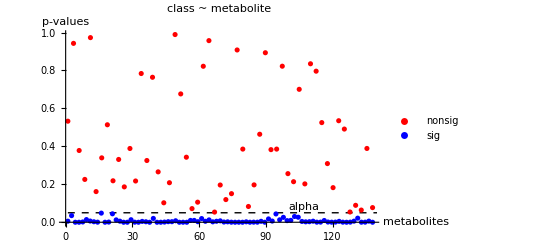

```mathematica
ListPlot[Tooltip[{data1p,data2p}],PlotLegends->{"nonsig","sig"},PlotLabel->"class ~ metabolite",PlotStyle->{Red,Blue},DataRange->{1,138},AxesLabel->{"metabolites","p-values"},
Epilog->{ Dashed,
Line[{{1,0.05}, {140,0.05}}],Style[Text["alpha", {100,0.08},{-1,0}],
		      FontSize->8]}]
```

```mathematica
classmeT1=LogitModelFit[
bC⟦2;;,{M1,class}⟧,x,x]
classmeT1["BestFit"];
classmeT1["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.820667-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.820667 | 0.298367 | -2.75053 | 0.00594996
x | 0.0912287 | 0.0432648 | 2.10861 | 0.0349779

```mathematica
classmeT2=LogitModelFit[
bC⟦2;;,{M2,class}⟧,x,x]
classmeT2["BestFit"];
classmeT2["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.318853-«22» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.318853 | 0.994009 | -0.320775 | 0.748381
x | 0.00137272 | 0.0191741 | 0.0715925 | 0.942926

```mathematica
classmeT3=LogitModelFit[
bC⟦2;;,{M3,class}⟧,x,x]
classmeT3["BestFit"];
classmeT3["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.498962-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.498962 | 0.312182 | -1.5983 | 0.109976
x | 0.132533 | 0.150407 | 0.881165 | 0.378229

```mathematica
classmeT4=LogitModelFit[
bC⟦2;;,{M4,class}⟧,x,x]
classmeT4["BestFit"];
classmeT4["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.587827-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.587827 | 0.30768 | -1.91051 | 0.0560673
x | 0.331865 | 0.273981 | 1.21127 | 0.225791

```mathematica
classmeT5=LogitModelFit[
bC⟦2;;,{M5,class}⟧,x,x]
classmeT5["BestFit"];
classmeT5["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.255956-«22» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.255956 | 0.261676 | -0.978143 | 0.328003
x | 0.00317711 | 0.0946249 | 0.0335758 | 0.973215

```mathematica
classmeT6=LogitModelFit[
bC⟦2;;,{M6,class}⟧,x,x]
classmeT6["BestFit"];
classmeT6["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.09756-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.09756 | 0.330294 | -3.32298 | 0.000890607
x | 0.0274887 | 0.00992759 | 2.76892 | 0.00562427

```mathematica
classmeT7=LogitModelFit[
bC⟦2;;,{M7,class}⟧,x,x]
classmeT7["BestFit"];
classmeT7["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.695624-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.695624 | 0.344286 | -2.02048 | 0.0433332
x | 0.0226659 | 0.0161917 | 1.39985 | 0.161559

```mathematica
classmeT8=LogitModelFit[
bC⟦2;;,{M8,class}⟧,x,x]
classmeT8["BestFit"];
classmeT8["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.533466-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.533466 | 0.325278 | -1.64003 | 0.100999
x | 0.00957231 | 0.0100202 | 0.9553 | 0.339426

```mathematica
classmeT9=LogitModelFit[
bC⟦2;;,{M9,class}⟧,x,x]
classmeT9["BestFit"];
classmeT9["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.43633-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.43633 | 0.315442 | -1.38323 | 0.166593
x | 0.0083479 | 0.0127855 | 0.652919 | 0.513809

```mathematica
classmeT10=LogitModelFit[
bC⟦2;;,{M10,class}⟧,x,x]
classmeT10["BestFit"];
classmeT10["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.820667-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.820667 | 0.298367 | -2.75053 | 0.00594996
x | 0.0912287 | 0.0432648 | 2.10861 | 0.0349779

```mathematica
classmeT11=LogitModelFit[
bC⟦2;;,{M11,class}⟧,x,x]
classmeT11["BestFit"];
classmeT11["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.617806-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.617806 | 0.326598 | -1.89164 | 0.0585387
x | 0.0800762 | 0.0650839 | 1.23035 | 0.218565

```mathematica
classmeT12=LogitModelFit[
bC⟦2;;,{M12,class}⟧,x,x]
classmeT12["BestFit"];
classmeT12["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.551242-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.551242 | 0.337124 | -1.63513 | 0.102022
x | 0.0466166 | 0.0479586 | 0.972019 | 0.331041

```mathematica
classmeT13=LogitModelFit[
bC⟦2;;,{M13,class}⟧,x,x]
classmeT13["BestFit"];
classmeT13["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.657639-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.657639 | 0.335145 | -1.96225 | 0.0497332
x | 0.423656 | 0.320659 | 1.3212 | 0.186433

```mathematica
classmeT14=LogitModelFit[
bC⟦2;;,{M14,class}⟧,x,x]
classmeT14["BestFit"];
classmeT14["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.550562-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.550562 | 0.373555 | -1.47384 | 0.140524
x | 0.0552486 | 0.0641114 | 0.86176 | 0.388819

```mathematica
classmeT15=LogitModelFit[
bC⟦2;;,{M15,class}⟧,x,x]
classmeT15["BestFit"];
classmeT15["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.634822-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.634822 | 0.339145 | -1.87183 | 0.06123
x | 0.110171 | 0.0893303 | 1.2333 | 0.217465

```mathematica
classmeT16=LogitModelFit[
bC⟦2;;,{M16,class}⟧,x,x]
classmeT16["BestFit"];
classmeT16["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.87986-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.87986 | 0.631372 | -4.56127 | 5.08447×10^-6
x | 0.194175 | 0.045427 | 4.27443 | 0.0000191628

```mathematica
classmeT17=LogitModelFit[
bC⟦2;;,{M17,class}⟧,x,x]
classmeT17["BestFit"];
classmeT17["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.33298-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.33298 | 0.48009 | -4.85947 | 1.177×10^-6
x | 0.979019 | 0.218742 | 4.47569 | 7.61657×10^-6

```mathematica
classmeT18=LogitModelFit[
bC⟦2;;,{M18,class}⟧,x,x]
classmeT18["BestFit"];
classmeT18["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.303924-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.303924 | 0.2397 | -1.26793 | 0.204822
x | 0.00359611 | 0.013116 | 0.274177 | 0.783949

```mathematica
classmeT19=LogitModelFit[
bC⟦2;;,{M19,class}⟧,x,x]
classmeT19["BestFit"];
classmeT19["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.595113-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.595113 | 0.375731 | -1.58388 | 0.113221
x | 0.110139 | 0.112006 | 0.983327 | 0.325447

```mathematica
classmeT20=LogitModelFit[
bC⟦2;;,{M20,class}⟧,x,x]
classmeT20["BestFit"];
classmeT20["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.66162-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.66162 | 0.465053 | -3.57297 | 0.000352961
x | 0.569905 | 0.179541 | 3.17424 | 0.00150228

```mathematica
classmeT21=LogitModelFit[
bC⟦2;;,{M21,class}⟧,x,x]
classmeT21["BestFit"];
classmeT21["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.349847-«22» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.349847 | 0.361962 | -0.966529 | 0.333779
x | 0.00148263 | 0.00494262 | 0.299969 | 0.764201

```mathematica
classmeT22=LogitModelFit[
bC⟦2;;,{M22,class}⟧,x,x]
classmeT22["BestFit"];
classmeT22["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.647812-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.647812 | 0.381655 | -1.69738 | 0.0896256
x | 0.00688636 | 0.00618566 | 1.11328 | 0.265589

```mathematica
classmeT23=LogitModelFit[
bC⟦2;;,{M23,class}⟧,x,x]
classmeT23["BestFit"];
classmeT23["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.40079-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.40079 | 0.486027 | -2.88214 | 0.00394988
x | 0.00525293 | 0.00213869 | 2.45614 | 0.0140439

```mathematica
classmeT24=LogitModelFit[
bC⟦2;;,{M24,class}⟧,x,x]
classmeT24["BestFit"];
classmeT24["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.50962-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.50962 | 0.480815 | -3.13972 | 0.00169111
x | 0.0165737 | 0.00607325 | 2.72897 | 0.00635329

```mathematica
classmeT25=LogitModelFit[
bC⟦2;;,{M25,class}⟧,x,x]
classmeT25["BestFit"];
classmeT25["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.04937-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.04937 | 0.613251 | -3.34181 | 0.000832354
x | 0.00465629 | 0.00154804 | 3.00786 | 0.00263097

```mathematica
classmeT26=LogitModelFit[
bC⟦2;;,{M26,class}⟧,x,x]
classmeT26["BestFit"];
classmeT26["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.735722-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.735722 | 0.325213 | -2.26228 | 0.0236803
x | 0.110903 | 0.0679311 | 1.63259 | 0.102556

```mathematica
classmeT27=LogitModelFit[
bC⟦2;;,{M27,class}⟧,x,x]
classmeT27["BestFit"];
classmeT27["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.61074-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.61074 | 0.410329 | -3.92549 | 0.0000865539
x | 0.00905132 | 0.00258611 | 3.49998 | 0.000465294

```mathematica
classmeT28=LogitModelFit[
bC⟦2;;,{M28,class}⟧,x,x]
classmeT28["BestFit"];
classmeT28["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.13641+«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.13641 | 0.329709 | 0.413728 | 0.679073
x | -0.386197 | 0.307009 | -1.25794 | 0.208415

```mathematica
classmeT29=LogitModelFit[
bC⟦2;;,{M29,class}⟧,x,x]
classmeT29["BestFit"];
classmeT29["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.245565+«22» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.245565 | 0.240436 | -1.02133 | 0.307098
x | -0.000823535 | 0.0618944 | -0.0133055 | 0.989384

```mathematica
classmeT30=LogitModelFit[
bC⟦2;;,{M30,class}⟧,x,x]
classmeT30["BestFit"];
classmeT30["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.439539-«22» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.439539 | 0.476013 | -0.923375 | 0.355812
x | 0.00151046 | 0.00361933 | 0.41733 | 0.676437

```mathematica
classmeT31=LogitModelFit[
bC⟦2;;,{M31,class}⟧,x,x]
classmeT31["BestFit"];
classmeT31["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.974765-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.974765 | 0.389626 | -2.5018 | 0.0123565
x | 0.0175307 | 0.00887153 | 1.97607 | 0.0481473

```mathematica
classmeT32=LogitModelFit[
bC⟦2;;,{M32,class}⟧,x,x]
classmeT32["BestFit"];
classmeT32["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.63902-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.63902 | 0.625543 | -4.21876 | 0.0000245646
x | 0.009954 | 0.00254566 | 3.91018 | 0.0000922273

```mathematica
classmeT33=LogitModelFit[
bC⟦2;;,{M33,class}⟧,x,x]
classmeT33["BestFit"];
classmeT33["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.548332-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.548332 | 0.341796 | -1.60427 | 0.108656
x | 0.00470425 | 0.00495926 | 0.94858 | 0.342834

```mathematica
classmeT34=LogitModelFit[
bC⟦2;;,{M34,class}⟧,x,x]
classmeT34["BestFit"];
classmeT34["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.46225-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.46225 | 0.38857 | -3.76317 | 0.000167775
x | 0.716408 | 0.216722 | 3.30565 | 0.000947568

```mathematica
classmeT35=LogitModelFit[
bC⟦2;;,{M35,class}⟧,x,x]
classmeT35["BestFit"];
classmeT35["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.26933-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.26933 | 0.525563 | -2.41519 | 0.015727
x | 0.00495903 | 0.00246815 | 2.00921 | 0.0445148

```mathematica
classmeT36=LogitModelFit[
bC⟦2;;,{M36,class}⟧,x,x]
classmeT36["BestFit"];
classmeT36["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.811515-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.811515 | 0.338921 | -2.39441 | 0.0166471
x | 0.0385042 | 0.021397 | 1.79951 | 0.0719373

```mathematica
classmeT37=LogitModelFit[
bC⟦2;;,{M37,class}⟧,x,x]
classmeT37["BestFit"];
classmeT37["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.986035-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.986035 | 0.475155 | -2.07519 | 0.0379693
x | 0.0118724 | 0.0073419 | 1.61707 | 0.105863

```mathematica
classmeT38=LogitModelFit[
bC⟦2;;,{M38,class}⟧,x,x]
classmeT38["BestFit"];
classmeT38["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.198487+«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.198487 | 0.255308 | -0.777443 | 0.436898
x | -0.00269623 | 0.0119996 | -0.224694 | 0.822218

```mathematica
classmeT39=LogitModelFit[
bC⟦2;;,{M39,class}⟧,x,x]
classmeT39["BestFit"];
classmeT39["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.21974-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.21974 | 0.409743 | -2.97684 | 0.00291235
x | 0.00526479 | 0.00210784 | 2.49772 | 0.0124996

```mathematica
classmeT40=LogitModelFit[
bC⟦2;;,{M40,class}⟧,x,x]
classmeT40["BestFit"];
classmeT40["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.23671-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.23671 | 0.380028 | -3.25428 | 0.00113682
x | 0.00845128 | 0.00305024 | 2.7707 | 0.00559363

```mathematica
classmeT41=LogitModelFit[
bC⟦2;;,{M41,class}⟧,x,x]
classmeT41["BestFit"];
classmeT41["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.20447-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.20447 | 0.467412 | -4.71633 | 2.4014×10^-6
x | 0.610518 | 0.139626 | 4.37251 | 0.0000122827

```mathematica
classmeT42=LogitModelFit[
bC⟦2;;,{M42,class}⟧,x,x]
classmeT42["BestFit"];
classmeT42["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.224618+«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.224618 | 0.460101 | -0.488194 | 0.625413
x | -0.0311131 | 0.581496 | -0.0535053 | 0.957329

```mathematica
classmeT43=LogitModelFit[
bC⟦2;;,{M43,class}⟧,x,x]
classmeT43["BestFit"];
classmeT43["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.63264-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.63264 | 0.37893 | -4.30855 | 0.0000164325
x | 0.0373366 | 0.00959272 | 3.89218 | 0.0000993458

```mathematica
classmeT44=LogitModelFit[
bC⟦2;;,{M44,class}⟧,x,x]
classmeT44["BestFit"];
classmeT44["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.31603-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.31603 | 0.451031 | -2.91783 | 0.00352473
x | 0.0105447 | 0.00426133 | 2.4745 | 0.0133422

```mathematica
classmeT45=LogitModelFit[
bC⟦2;;,{M45,class}⟧,x,x]
classmeT45["BestFit"];
classmeT45["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.8866-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.8866 | 0.477866 | -3.94796 | 0.00007882
x | 0.0458019 | 0.0128454 | 3.56562 | 0.000362996

```mathematica
classmeT46=LogitModelFit[
bC⟦2;;,{M46,class}⟧,x,x]
classmeT46["BestFit"];
classmeT46["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.02629-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.02629 | 0.4645 | -4.36231 | 0.0000128695
x | 0.189792 | 0.0475925 | 3.98785 | 0.0000666739

```mathematica
classmeT47=LogitModelFit[
bC⟦2;;,{M47,class}⟧,x,x]
classmeT47["BestFit"];
classmeT47["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.31395-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.31395 | 0.396504 | -3.31384 | 0.000920225
x | 0.564163 | 0.198448 | 2.84288 | 0.00447085

```mathematica
classmeT48=LogitModelFit[
bC⟦2;;,{M48,class}⟧,x,x]
classmeT48["BestFit"];
classmeT48["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.34642-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.34642 | 0.387842 | -3.47157 | 0.000517427
x | 0.0742393 | 0.0246333 | 3.01378 | 0.00258014

```mathematica
classmeT49=LogitModelFit[
bC⟦2;;,{M49,class}⟧,x,x]
classmeT49["BestFit"];
classmeT49["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.901922-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.901922 | 0.362783 | -2.48612 | 0.0129145
x | 0.00873167 | 0.00452497 | 1.92966 | 0.0536486

```mathematica
classmeT50=LogitModelFit[
bC⟦2;;,{M50,class}⟧,x,x]
classmeT50["BestFit"];
classmeT50["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.840648-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.840648 | 0.477071 | -1.7621 | 0.0780517
x | 0.0119349 | 0.00923638 | 1.29216 | 0.196301

```mathematica
classmeT51=LogitModelFit[
bC⟦2;;,{M51,class}⟧,x,x]
classmeT51["BestFit"];
classmeT51["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.722366-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.722366 | 0.330952 | -2.18269 | 0.0290583
x | 0.154564 | 0.0992826 | 1.55681 | 0.119516

```mathematica
classmeT52=LogitModelFit[
bC⟦2;;,{M52,class}⟧,x,x]
classmeT52["BestFit"];
classmeT52["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.604611-«18» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.604611 | 0.279389 | -2.16405 | 0.0304606
x | 0.511656 | 0.356057 | 1.43701 | 0.150716

```mathematica
classmeT53=LogitModelFit[
bC⟦2;;,{M53,class}⟧,x,x]
classmeT53["BestFit"];
classmeT53["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.00341-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.00341 | 0.395868 | -5.06081 | 4.17476×10^-7
x | 1.76727 | 0.386396 | 4.57372 | 4.79135×10^-6

```mathematica
classmeT54=LogitModelFit[
bC⟦2;;,{M54,class}⟧,x,x]
classmeT54["BestFit"];
classmeT54["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.02203-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.02203 | 0.356908 | -2.86357 | 0.00418891
x | 0.427906 | 0.184193 | 2.32315 | 0.0201713

```mathematica
classmeT55=LogitModelFit[
bC⟦2;;,{M55,class}⟧,x,x]
classmeT55["BestFit"];
classmeT55["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.96553-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.96553 | 0.398841 | -4.92809 | 8.30366×10^-7
x | 0.387268 | 0.0867248 | 4.46549 | 7.98868×10^-6

```mathematica
classmeT56=LogitModelFit[
bC⟦2;;,{M56,class}⟧,x,x]
classmeT56["BestFit"];
classmeT56["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.71872-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.71872 | 0.382648 | -4.49166 | 7.06716×10^-6
x | 0.192938 | 0.0472217 | 4.08579 | 0.0000439263

```mathematica
classmeT57=LogitModelFit[
bC⟦2;;,{M57,class}⟧,x,x]
classmeT57["BestFit"];
classmeT57["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.31092-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.31092 | 0.347497 | -3.77245 | 0.00016165
x | 0.0389048 | 0.0118225 | 3.29073 | 0.000999268

```mathematica
classmeT58=LogitModelFit[
bC⟦2;;,{M58,class}⟧,x,x]
classmeT58["BestFit"];
classmeT58["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.44003-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.44003 | 0.42347 | -3.40054 | 0.000672524
x | 0.0579078 | 0.0195378 | 2.96389 | 0.00303773

```mathematica
classmeT59=LogitModelFit[
bC⟦2;;,{M59,class}⟧,x,x]
classmeT59["BestFit"];
classmeT59["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.290984-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.290984 | 0.391285 | -0.743663 | 0.457081
x | 0.0192786 | 0.166995 | 0.115444 | 0.908093

```mathematica
classmeT60=LogitModelFit[
bC⟦2;;,{M60,class}⟧,x,x]
classmeT60["BestFit"];
classmeT60["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.48567-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.48567 | 0.436923 | -3.40031 | 0.000673091
x | 0.127585 | 0.0429304 | 2.9719 | 0.00295959

```mathematica
classmeT61=LogitModelFit[
bC⟦2;;,{M61,class}⟧,x,x]
classmeT61["BestFit"];
classmeT61["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.571476-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.571476 | 0.394252 | -1.44952 | 0.147192
x | 0.00585873 | 0.00675329 | 0.867537 | 0.385648

```mathematica
classmeT62=LogitModelFit[
bC⟦2;;,{M62,class}⟧,x,x]
classmeT62["BestFit"];
classmeT62["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.898845-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.898845 | 0.397549 | -2.26097 | 0.0237613
x | 0.0209215 | 0.0120732 | 1.73289 | 0.0831154

```mathematica
classmeT63=LogitModelFit[
bC⟦2;;,{M63,class}⟧,x,x]
classmeT63["BestFit"];
classmeT63["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.730177-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.730177 | 0.39558 | -1.84584 | 0.0649154
x | 0.0251477 | 0.0194917 | 1.29017 | 0.196991

```mathematica
classmeT64=LogitModelFit[
bC⟦2;;,{M64,class}⟧,x,x]
classmeT64["BestFit"];
classmeT64["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0101591+«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0101591 | 0.374231 | 0.0271466 | 0.978343
x | -0.013171 | 0.017982 | -0.732453 | 0.463892

```mathematica
classmeT65=LogitModelFit[
bC⟦2;;,{M65,class}⟧,x,x]
classmeT65["BestFit"];
classmeT65["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.24331-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.24331 | 0.395434 | -3.14417 | 0.00166556
x | 0.00391147 | 0.00147027 | 2.66038 | 0.00780514

```mathematica
classmeT66=LogitModelFit[
bC⟦2;;,{M66,class}⟧,x,x]
classmeT66["BestFit"];
classmeT66["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.06917-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.06917 | 0.392965 | -5.26553 | 1.39782×10^-7
x | 0.10783 | 0.0220677 | 4.88635 | 1.02723×10^-6

```mathematica
classmeT67=LogitModelFit[
bC⟦2;;,{M67,class}⟧,x,x]
classmeT67["BestFit"];
classmeT67["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.202398+«22» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.202398 | 0.365455 | -0.553826 | 0.579698
x | -0.00307048 | 0.0229368 | -0.133867 | 0.893508

```mathematica
classmeT68=LogitModelFit[
bC⟦2;;,{M68,class}⟧,x,x]
classmeT68["BestFit"];
classmeT68["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.546034-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.546034 | 0.36458 | -1.49771 | 0.13421
x | 0.0215538 | 0.0246929 | 0.872874 | 0.382732

```mathematica
classmeT69=LogitModelFit[
bC⟦2;;,{M61,class}⟧,x,x]
classmeT69["BestFit"];
classmeT69["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.571476-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.571476 | 0.394252 | -1.44952 | 0.147192
x | 0.00585873 | 0.00675329 | 0.867537 | 0.385648

```mathematica
classmeT70=LogitModelFit[
bC⟦2;;,{M70,class}⟧,x,x]
classmeT70["BestFit"];
classmeT70["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.72354-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.72354 | 0.667632 | -4.07941 | 0.0000451508
x | 0.0468847 | 0.0123592 | 3.79351 | 0.000148534

```mathematica
classmeT71=LogitModelFit[
bC⟦2;;,{M71,class}⟧,x,x]
classmeT71["BestFit"];
classmeT71["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.61803-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.61803 | 0.58145 | -4.5026 | 6.71286×10^-6
x | 0.354372 | 0.0845785 | 4.18985 | 0.0000279135

```mathematica
classmeT72=LogitModelFit[
bC⟦2;;,{M72,class}⟧,x,x]
classmeT72["BestFit"];
classmeT72["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.38195-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.38195 | 0.456925 | -3.02446 | 0.00249076
x | 0.0879219 | 0.0339371 | 2.59073 | 0.00957719

```mathematica
classmeT73=LogitModelFit[
bC⟦2;;,{M73,class}⟧,x,x]
classmeT73["BestFit"];
classmeT73["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.50602-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.50602 | 0.503533 | -2.99091 | 0.00278149
x | 0.247888 | 0.0957253 | 2.58958 | 0.00960938

```mathematica
classmeT74=LogitModelFit[
bC⟦2;;,{M74,class}⟧,x,x]
classmeT74["BestFit"];
classmeT74["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.8607-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.8607 | 0.557862 | -3.33542 | 0.000851715
x | 0.0893785 | 0.0299983 | 2.97945 | 0.00288766

```mathematica
classmeT75=LogitModelFit[
bC⟦2;;,{M75,class}⟧,x,x]
classmeT75["BestFit"];
classmeT75["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.35333-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.35333 | 0.48557 | -0.72766 | 0.466822
x | 0.0132118 | 0.0589085 | 0.224277 | 0.822542

```mathematica
classmeT76=LogitModelFit[
bC⟦2;;,{M76,class}⟧,x,x]
classmeT76["BestFit"];
classmeT76["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.780742-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.780742 | 0.486907 | -1.60347 | 0.10883
x | 0.165478 | 0.145752 | 1.13534 | 0.256234

```mathematica
classmeT77=LogitModelFit[
bC⟦2;;,{M77,class}⟧,x,x]
classmeT77["BestFit"];
classmeT77["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.694281-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.694281 | 0.381446 | -1.82013 | 0.0687394
x | 0.129044 | 0.103794 | 1.24327 | 0.213769

```mathematica
classmeT78=LogitModelFit[
bC⟦2;;,{M78,class}⟧,x,x]
classmeT78["BestFit"];
classmeT78["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.427361-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.427361 | 0.483327 | -0.884207 | 0.376584
x | 0.0112436 | 0.0292527 | 0.38436 | 0.700712

```mathematica
classmeT79=LogitModelFit[
bC⟦2;;,{M79,class}⟧,x,x]
classmeT79["BestFit"];
classmeT79["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.921178-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.921178 | 0.543822 | -1.6939 | 0.0902851
x | 0.0785557 | 0.0616027 | 1.2752 | 0.202239

```mathematica
classmeT80=LogitModelFit[
bC⟦2;;,{M80,class}⟧,x,x]
classmeT80["BestFit"];
classmeT80["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.172227+«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.172227 | 0.387199 | -0.444802 | 0.656463
x | -0.0298167 | 0.143463 | -0.207836 | 0.835357

```mathematica
classmeT81=LogitModelFit[
bC⟦2;;,{M81,class}⟧,x,x]
classmeT81["BestFit"];
classmeT81["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.133492+«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.133492 | 0.462299 | -0.288756 | 0.772768
x | -0.0180038 | 0.0697511 | -0.258115 | 0.796318

```mathematica
classmeT82=LogitModelFit[
bC⟦2;;,{M82,class}⟧,x,x]
classmeT82["BestFit"];
classmeT82["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.51354-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.51354 | 0.437061 | -1.17498 | 0.240001
x | 0.0503188 | 0.0792104 | 0.635255 | 0.525262

```mathematica
classmeT83=LogitModelFit[
bC⟦2;;,{M83,class}⟧,x,x]
classmeT83["BestFit"];
classmeT83["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.576816-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.576816 | 0.347863 | -1.65817 | 0.0972829
x | 0.095875 | 0.0942882 | 1.01683 | 0.309235

```mathematica
classmeT84=LogitModelFit[
bC⟦2;;,{M84,class}⟧,x,x]
classmeT84["BestFit"];
classmeT84["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.334724+«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.334724 | 0.453914 | 0.737418 | 0.460868
x | -0.0634488 | 0.0475843 | -1.3334 | 0.182401

```mathematica
classmeT85=LogitModelFit[
bC⟦2;;,{M85,class}⟧,x,x]
classmeT85["BestFit"];
classmeT85["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.505666-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.505666 | 0.434591 | -1.16354 | 0.244609
x | 0.00846714 | 0.0136524 | 0.620196 | 0.535129

```mathematica
classmeT86=LogitModelFit[
bC⟦2;;,{M86,class}⟧,x,x]
classmeT86["BestFit"];
classmeT86["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.535727-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.535727 | 0.437149 | -1.2255 | 0.220386
x | 0.974844 | 1.41611 | 0.688397 | 0.491203

```mathematica
classmeT87=LogitModelFit[
bC⟦2;;,{M87,class}⟧,x,x]
classmeT87["BestFit"];
classmeT87["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.557844-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.557844 | 0.183668 | -3.03724 | 0.00238759
x | 0.0142424 | 0.00609092 | 2.33831 | 0.0193714

```mathematica
classmeT88=LogitModelFit[
bC⟦2;;,{M88,class}⟧,x,x]
classmeT88["BestFit"];
classmeT88["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.61189-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.61189 | 0.180337 | -3.39303 | 0.000691232
x | 0.016315 | 0.00582851 | 2.79918 | 0.00512331

```mathematica
classmeT89=LogitModelFit[
bC⟦2;;,{M89,class}⟧,x,x]
classmeT89["BestFit"];
classmeT89["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.587139-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.587139 | 0.185516 | -3.16489 | 0.00155143
x | 0.0051476 | 0.0020581 | 2.50114 | 0.0123795

```mathematica
classmeT90=LogitModelFit[
bC⟦2;;,{M90,class}⟧,x,x]
classmeT90["BestFit"];
classmeT90["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.821132-«22» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.821132 | 0.226246 | -3.62938 | 0.0002841
x | 0.00342731 | 0.00111928 | 3.06206 | 0.00219822

```mathematica
classmeT91=LogitModelFit[
bC⟦2;;,{M91,class}⟧,x,x]
classmeT91["BestFit"];
classmeT91["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.611622-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.611622 | 0.179314 | -3.41089 | 0.000647504
x | 0.0316999 | 0.0113493 | 2.79311 | 0.00522038

```mathematica
classmeT92=LogitModelFit[
bC⟦2;;,{M92,class}⟧,x,x]
classmeT92["BestFit"];
classmeT92["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.659728-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.659728 | 0.194984 | -3.3835 | 0.000715673
x | 0.157038 | 0.0587243 | 2.67415 | 0.00749181

```mathematica
classmeT93=LogitModelFit[
bC⟦2;;,{M93,class}⟧,x,x]
classmeT93["BestFit"];
classmeT93["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.772356-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.772356 | 0.201619 | -3.83077 | 0.000127744
x | 0.00765969 | 0.00236321 | 3.24123 | 0.00119017

```mathematica
classmeT94=LogitModelFit[
bC⟦2;;,{M90,class}⟧,x,x]
classmeT94["BestFit"];
classmeT94["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.821132-«22» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.821132 | 0.226246 | -3.62938 | 0.0002841
x | 0.00342731 | 0.00111928 | 3.06206 | 0.00219822

```mathematica
classmeT95=LogitModelFit[
bC⟦2;;,{M95,class}⟧,x,x]
classmeT95["BestFit"];
classmeT95["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.878557-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.878557 | 0.213857 | -4.10816 | 0.0000398832
x | 0.00362828 | 0.00100311 | 3.61702 | 0.000298017

```mathematica
classmeT96=LogitModelFit[
bC⟦2;;,{M96,class}⟧,x,x]
classmeT96["BestFit"];
classmeT96["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.38036-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.38036 | 0.304591 | -4.53185 | 5.84691×10^-6
x | 0.00176234 | 0.000429379 | 4.1044 | 0.0000405372

```mathematica
classmeT97=LogitModelFit[
bC⟦2;;,{M97,class}⟧,x,x]
classmeT97["BestFit"];
classmeT97["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.04194-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.04194 | 0.245021 | -4.25246 | 0.0000211439
x | 0.012576 | 0.00339505 | 3.70423 | 0.000212036

```mathematica
classmeT98=LogitModelFit[
bC⟦2;;,{M98,class}⟧,x,x]
classmeT98["BestFit"];
classmeT98["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.4045-«22» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.4045 | 0.312352 | -4.49654 | 6.90697×10^-6
x | 0.00192821 | 0.000473825 | 4.06945 | 0.0000471248

```mathematica
classmeT99=LogitModelFit[
bC⟦2;;,{M99,class}⟧,x,x]
classmeT99["BestFit"];
classmeT99["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.889082-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.889082 | 0.242565 | -3.66533 | 0.000247016
x | 0.136443 | 0.0447497 | 3.04902 | 0.00229592

```mathematica
classmeT100=LogitModelFit[
bC⟦2;;,{M100,class}⟧,x,x]
classmeT100["BestFit"];
classmeT100["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.15033-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.15033 | 0.266763 | -4.31219 | 0.0000161649
x | 0.350041 | 0.0916141 | 3.82082 | 0.000133011

```mathematica
classmeT101=LogitModelFit[
bC⟦2;;,{M101,class}⟧,x,x]
classmeT101["BestFit"];
classmeT101["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.884629-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.884629 | 0.22469 | -3.93712 | 0.0000824664
x | 0.00500468 | 0.00145301 | 3.44436 | 0.000572422

```mathematica
classmeT102=LogitModelFit[
bC⟦2;;,{M102,class}⟧,x,x]
classmeT102["BestFit"];
classmeT102["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.889646-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.889646 | 0.218817 | -4.06571 | 0.0000478862
x | 0.0066366 | 0.00188805 | 3.51505 | 0.000439672

```mathematica
classmeT103=LogitModelFit[
bC⟦2;;,{M103,class}⟧,x,x]
classmeT103["BestFit"];
classmeT103["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.875426-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.875426 | 0.253153 | -3.45808 | 0.000544032
x | 0.194113 | 0.0691522 | 2.80704 | 0.00499984

```mathematica
classmeT104=LogitModelFit[
bC⟦2;;,{M104,class}⟧,x,x]
classmeT104["BestFit"];
classmeT104["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.01044-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.01044 | 0.236368 | -4.27488 | 0.0000191243
x | 0.00633518 | 0.00165921 | 3.81819 | 0.000134437

```mathematica
classmeT105=LogitModelFit[
bC⟦2;;,{M105,class}⟧,x,x]
classmeT105["BestFit"];
classmeT105["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.51399-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.51399 | 0.168425 | -3.05174 | 0.00227516
x | 0.107576 | 0.0453112 | 2.37417 | 0.0175886

```mathematica
classmeT106=LogitModelFit[
bC⟦2;;,{M106,class}⟧,x,x]
classmeT106["BestFit"];
classmeT106["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.435989-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.435989 | 0.159588 | -2.73196 | 0.0062958
x | 0.15788 | 0.0819402 | 1.92677 | 0.0540088

```mathematica
classmeT107=LogitModelFit[
bC⟦2;;,{M107,class}⟧,x,x]
classmeT107["BestFit"];
classmeT107["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.574678-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.574678 | 0.173212 | -3.31776 | 0.000907418
x | 0.0486838 | 0.0177928 | 2.73616 | 0.00621612

```mathematica
classmeT108=LogitModelFit[
bC⟦2;;,{M108,class}⟧,x,x]
classmeT108["BestFit"];
classmeT108["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.420988-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.420988 | 0.162635 | -2.58855 | 0.00963797
x | 0.0385804 | 0.0227023 | 1.6994 | 0.0892433

```mathematica
classmeT109=LogitModelFit[
bC⟦2;;,{M109,class}⟧,x,x]
classmeT109["BestFit"];
classmeT109["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.50716-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.50716 | 0.18027 | -2.81334 | 0.00490301
x | 0.189569 | 0.0940417 | 2.0158 | 0.0438207

```mathematica
classmeT110=LogitModelFit[
bC⟦2;;,{M110,class}⟧,x,x]
classmeT110["BestFit"];
classmeT110["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.760619-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.760619 | 0.240672 | -3.1604 | 0.00157553
x | 0.329226 | 0.132275 | 2.48896 | 0.0128118

```mathematica
classmeT111=LogitModelFit[
bC⟦2;;,{M111,class}⟧,x,x]
classmeT111["BestFit"];
classmeT111["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.514654-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.514654 | 0.174104 | -2.95602 | 0.0031164
x | 0.0155765 | 0.0069865 | 2.22952 | 0.0257795

```mathematica
classmeT112=LogitModelFit[
bC⟦2;;,{M112,class}⟧,x,x]
classmeT112["BestFit"];
classmeT112["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.486188-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.486188 | 0.180271 | -2.69698 | 0.00699715
x | 0.0412192 | 0.0222719 | 1.85073 | 0.0642089

```mathematica
classmeT113=LogitModelFit[
bC⟦2;;,{M113,class}⟧,x,x]
classmeT113["BestFit"];
classmeT113["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.733268-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.733268 | 0.222641 | -3.2935 | 0.000989481
x | 0.188066 | 0.0714916 | 2.6306 | 0.00852344

```mathematica
classmeT114=LogitModelFit[
bC⟦2;;,{M114,class}⟧,x,x]
classmeT114["BestFit"];
classmeT114["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.697011-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.697011 | 0.215201 | -3.23889 | 0.00119997
x | 0.146972 | 0.0570472 | 2.57633 | 0.00998558

```mathematica
classmeT115=LogitModelFit[
bC⟦2;;,{M115,class}⟧,x,x]
classmeT115["BestFit"];
classmeT115["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.574466-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.574466 | 0.196779 | -2.91934 | 0.00350772
x | 0.0102256 | 0.00472193 | 2.16556 | 0.0303452

```mathematica
classmeT116=LogitModelFit[
bC⟦2;;,{M116,class}⟧,x,x]
classmeT116["BestFit"];
classmeT116["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.629426-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.629426 | 0.213625 | -2.94641 | 0.00321487
x | 0.0459039 | 0.0206726 | 2.22052 | 0.0263837

```mathematica
classmeT117=LogitModelFit[
bC⟦2;;,{M117,class}⟧,x,x]
classmeT117["BestFit"];
classmeT117["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.808054-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.808054 | 0.23167 | -3.48795 | 0.000486744
x | 0.199166 | 0.0696763 | 2.85845 | 0.00425716

```mathematica
classmeT118=LogitModelFit[
bC⟦2;;,{M118,class}⟧,x,x]
classmeT118["BestFit"];
classmeT118["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.801023-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.801023 | 0.219695 | -3.64607 | 0.00026628
x | 0.0764463 | 0.0249331 | 3.06605 | 0.00216906

```mathematica
classmeT119=LogitModelFit[
bC⟦2;;,{M119,class}⟧,x,x]
classmeT119["BestFit"];
classmeT119["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.890298-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.890298 | 0.250282 | -3.55719 | 0.000374848
x | 0.110543 | 0.0371468 | 2.97583 | 0.00292196

```mathematica
classmeT120=LogitModelFit[
bC⟦2;;,{M120,class}⟧,x,x]
classmeT120["BestFit"];
classmeT120["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.917382-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.917382 | 0.271183 | -3.38289 | 0.000717264
x | 1.86612 | 0.673011 | 2.7728 | 0.00555763

```mathematica
classmeT121=LogitModelFit[
bC⟦2;;,{M121,class}⟧,x,x]
classmeT121["BestFit"];
classmeT121["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.986777-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.986777 | 0.247472 | -3.98743 | 0.0000667916
x | 0.00946029 | 0.00271102 | 3.48957 | 0.000483803

```mathematica
classmeT122=LogitModelFit[
bC⟦2;;,{M122,class}⟧,x,x]
classmeT122["BestFit"];
classmeT122["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.910123-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.910123 | 0.233088 | -3.90463 | 0.0000943678
x | 0.0812907 | 0.0240666 | 3.37773 | 0.000730857

```mathematica
classmeT121=LogitModelFit[
bC⟦2;;,{M121,class}⟧,x,x]
classmeT121["BestFit"];
classmeT121["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.986777-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.986777 | 0.247472 | -3.98743 | 0.0000667916
x | 0.00946029 | 0.00271102 | 3.48957 | 0.000483803

```mathematica
classmeT122=LogitModelFit[
bC⟦2;;,{M122,class}⟧,x,x]
classmeT122["BestFit"];
classmeT122["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.910123-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.910123 | 0.233088 | -3.90463 | 0.0000943678
x | 0.0812907 | 0.0240666 | 3.37773 | 0.000730857

```mathematica
classmeT123=LogitModelFit[
bC⟦2;;,{M123,class}⟧,x,x]
classmeT123["BestFit"];
classmeT123["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.827991-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.827991 | 0.255717 | -3.23792 | 0.00120403
x | 0.485271 | 0.186335 | 2.6043 | 0.0092063

```mathematica
classmeT124=LogitModelFit[
bC⟦2;;,{M124,class}⟧,x,x]
classmeT124["BestFit"];
classmeT124["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.00472-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.00472 | 0.26548 | -3.78455 | 0.000153989
x | 0.0395985 | 0.0122168 | 3.24132 | 0.00118978

```mathematica
classmeT125=LogitModelFit[
bC⟦2;;,{M125,class}⟧,x,x]
classmeT125["BestFit"];
classmeT125["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.0641-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.0641 | 0.256091 | -4.15517 | 0.0000325051
x | 0.102121 | 0.0281288 | 3.63049 | 0.000282885

```mathematica
classmeT126=LogitModelFit[
bC⟦2;;,{M126,class}⟧,x,x]
classmeT126["BestFit"];
classmeT126["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.01572-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.01572 | 0.261188 | -3.88885 | 0.000100719
x | 0.521108 | 0.155147 | 3.3588 | 0.00078282

```mathematica
classmeT127=LogitModelFit[
bC⟦2;;,{M127,class}⟧,x,x]
classmeT127["BestFit"];
classmeT127["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.759054-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.759054 | 0.220822 | -3.43741 | 0.000587305
x | 0.0394881 | 0.0139995 | 2.82067 | 0.00479232

```mathematica
classmeT128=LogitModelFit[
bC⟦2;;,{M128,class}⟧,x,x]
classmeT128["BestFit"];
classmeT128["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.386744-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.386744 | 0.205082 | -1.8858 | 0.059322
x | 0.0955652 | 0.110935 | 0.861452 | 0.388989

```mathematica
classmeT129=LogitModelFit[
bC⟦2;;,{M129,class}⟧,x,x]
classmeT129["BestFit"];
classmeT129["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.13988-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.13988 | 0.285477 | -3.99288 | 0.000065276
x | 0.106679 | 0.0305961 | 3.48669 | 0.000489033

```mathematica
classmeT130=LogitModelFit[
bC⟦2;;,{M130,class}⟧,x,x]
classmeT130["BestFit"];
classmeT130["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.71434-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.71434 | 0.355804 | -4.81822 | 1.44841×10^-6
x | 0.24907 | 0.0581711 | 4.28168 | 0.0000185489

```mathematica
classmeT131=LogitModelFit[
bC⟦2;;,{M131,class}⟧,x,x]
classmeT131["BestFit"];
classmeT131["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.612397-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.612397 | 0.177738 | -3.4455 | 0.000569995
x | 0.0883347 | 0.0323552 | 2.73015 | 0.00633055

```mathematica
classmeT132=LogitModelFit[
bC⟦2;;,{M132,class}⟧,x,x]
classmeT132["BestFit"];
classmeT132["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.76741-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.76741 | 0.225941 | -3.39651 | 0.000682518
x | 0.0250301 | 0.00905946 | 2.76287 | 0.0057296

```mathematica
classmeT133=LogitModelFit[
bC⟦2;;,{M133,class}⟧,x,x]
classmeT133["BestFit"];
classmeT133["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.666898-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.666898 | 0.221951 | -3.00471 | 0.00265835
x | 0.0432642 | 0.0188328 | 2.29727 | 0.0216031

```mathematica
classmeT134=LogitModelFit[
bC⟦2;;,{M134,class}⟧,x,x]
classmeT134["BestFit"];
classmeT134["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.534961-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.534961 | 0.205119 | -2.60805 | 0.00910589
x | 0.105695 | 0.0598037 | 1.76736 | 0.0771673

```mathematica
classmeT135=LogitModelFit[
bC⟦2;;,{M135,class}⟧,x,x]
classmeT135["BestFit"];
classmeT135["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.05299-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.05299 | 0.254524 | -4.1371 | 0.0000351724
x | 0.0665514 | 0.0183062 | 3.63545 | 0.000277493

```mathematica
classmeT136=LogitModelFit[
bC⟦2;;,{M136,class}⟧,x,x]
classmeT136["BestFit"];
classmeT136["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.999619-«20» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.999619 | 0.248324 | -4.02546 | 0.0000568629
x | 0.0574879 | 0.0165371 | 3.4763 | 0.000508379

```mathematica
classmeT137=LogitModelFit[
bC⟦2;;,{M137,class}⟧,x,x]
classmeT137["BestFit"];
classmeT137["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.677701-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.677701 | 0.199646 | -3.39451 | 0.000687514
x | 0.0294946 | 0.0107219 | 2.75088 | 0.00594357

```mathematica
classmeT138=LogitModelFit[
bC⟦2;;,{M138,class}⟧,x,x]
classmeT138["BestFit"];
classmeT138["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.48291-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.48291 | 0.299637 | -4.94904 | 7.45813×10^-7
x | 0.820048 | 0.181885 | 4.50861 | 6.52538×10^-6

```mathematica
classmet=Import["C:\\Users\\oreol\\Desktop\\proj\\Met&Class1.xlsx"];
classmet2=Import["C:\\Users\\oreol\\Desktop\\proj\\Met&Class2.xlsx"];
```

```mathematica
classmetf=Flatten[classmet,1];
classmet2f= Flatten[classmet2,1];
Length[classmetf]
Length[classmet2f]
```

55

83

```mathematica
classmet2f[[;;,1]]
```

{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M88,M89,M90,M91,M92,M93,M94,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M130,M131,M132,M133,M135,M136,M137,M138}

```mathematica
meTclassLM=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M88,M89,M90,M91,M92,M93,M94,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M105,M106,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M130,M131,M132,M133,M135,M136,M137,M138,class}⟧,{1,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM137,xM138},
{xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM137,xM138}]
meTclassLM["BestFit"];
meTclassLM["ParameterTable"]
meTclassLMent=meTclassLM["ParameterTableEntries"];
meTclassLMf=Flatten[Position[meTclassLMent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(51.0275+«128»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -51.0275 | 20.423 | -2.49853 | 0.012471
xM6 | 0.665739 | 0.3107 | 2.14271 | 0.0321366
xM10 | -2.62687 | 1.19339 | -2.20118 | 0.0277232
xM16 | 2.44285 | 1.16668 | 2.09386 | 0.0362728
xM17 | 6.49148 | 4.24345 | 1.52977 | 0.126075
xM20 | -46.0952 | 19.1436 | -2.40787 | 0.0160461
xM23 | 0.177862 | 0.0923293 | 1.92639 | 0.0540554
xM24 | -0.97148 | 0.414233 | -2.34525 | 0.0190143
xM25 | -0.121241 | 0.0614858 | -1.97185 | 0.0486264
xM27 | 0.560681 | 0.231486 | 2.42209 | 0.0154314
xM31 | -1.36827 | 0.550497 | -2.48552 | 0.0129361
xM32 | -0.156269 | 0.0931138 | -1.67826 | 0.093296
xM34 | -6.76727 | 3.70851 | -1.82479 | 0.0680323
xM35 | 0.292876 | 0.132242 | 2.2147 | 0.0267809
xM39 | -0.321867 | 0.132808 | -2.42355 | 0.0153696
xM40 | -0.196576 | 0.0843847 | -2.32952 | 0.0198317
xM41 | 18.3587 | 7.50995 | 2.44459 | 0.0145019
xM43 | -0.892663 | 0.37257 | -2.39596 | 0.0165771
xM44 | -0.581509 | 0.262348 | -2.21656 | 0.0266534
xM45 | -0.904466 | 0.385358 | -2.34708 | 0.0189213
xM46 | 3.92967 | 1.81875 | 2.16065 | 0.0307226
xM47 | -14.4213 | 6.90153 | -2.08959 | 0.036655
xM48 | -1.27225 | 0.592738 | -2.1464 | 0.0318414
xM49 | -0.640874 | 0.253094 | -2.53215 | 0.0113364
xM53 | 16.4338 | 9.24764 | 1.77709 | 0.0755542
xM54 | 9.09723 | 4.21604 | 2.15777 | 0.0309459
xM55 | 13.0869 | 5.09831 | 2.5669 | 0.0102611
xM56 | 7.57792 | 3.0436 | 2.48978 | 0.0127821
xM57 | 1.82068 | 0.725467 | 2.50966 | 0.0120847
xM58 | 1.04528 | 0.602079 | 1.73612 | 0.082542
xM60 | 2.25588 | 0.933623 | 2.41627 | 0.0156805
xM65 | 0.0332997 | 0.0268633 | 1.2396 | 0.215123
xM66 | 2.4612 | 0.955146 | 2.57678 | 0.00997256
xM70 | -1.40849 | 0.573249 | -2.45703 | 0.0140092
xM71 | 21.044 | 8.83381 | 2.38221 | 0.0172091
xM72 | -1.88896 | 1.02202 | -1.84826 | 0.0645644
xM73 | 3.2398 | 1.73422 | 1.86815 | 0.0617406
xM74 | 3.73091 | 1.56152 | 2.38928 | 0.0168814
xM87 | -1.03333 | 0.55259 | -1.86997 | 0.0614878
xM88 | -0.0828402 | 0.416707 | -0.198797 | 0.842421
xM89 | -0.380769 | 0.191838 | -1.98484 | 0.0471618
xM90 | -0.102118 | 0.0595549 | -1.71469 | 0.0864019
xM91 | 2.50301 | 1.11681 | 2.24121 | 0.0250126
xM92 | -4.37604 | 2.48679 | -1.75972 | 0.0784554
xM93 | -0.155386 | 0.138558 | -1.12145 | 0.262096
xM94 | -4.28368 | 1.83571 | -2.33353 | 0.0196201
xM95 | 0.0939408 | 0.0692139 | 1.35725 | 0.174701
xM96 | 0.0556681 | 0.0251325 | 2.21498 | 0.0267611
xM97 | 0.646086 | 0.307381 | 2.1019 | 0.0355617
xM98 | -0.00392313 | 0.0134027 | -0.292711 | 0.769743
xM99 | 5.15763 | 2.96823 | 1.73761 | 0.0822788
xM100 | -28.6656 | 12.2946 | -2.33156 | 0.0197238
xM101 | -0.257085 | 0.110985 | -2.31639 | 0.0205372
xM102 | 0.452855 | 0.19168 | 2.36256 | 0.0181493
xM103 | -18.1008 | 7.34388 | -2.46475 | 0.013711
xM104 | 0.23724 | 0.102356 | 2.31779 | 0.0204605
xM105 | -18.8111 | 7.92594 | -2.37336 | 0.017627
xM106 | 1.14061 | 2.48908 | 0.458246 | 0.646776
xM107 | 9.12195 | 3.82592 | 2.38425 | 0.017114
xM109 | 8.62444 | 5.11327 | 1.68668 | 0.0916656
xM110 | -11.3507 | 5.90094 | -1.92355 | 0.0544116
xM111 | 1.80952 | 0.775133 | 2.33447 | 0.0195713
xM113 | -10.1399 | 5.40281 | -1.87678 | 0.0605487
xM114 | 7.44063 | 3.82664 | 1.94443 | 0.0518437
xM115 | -1.22761 | 0.583896 | -2.10244 | 0.0355145
xM116 | -4.82322 | 2.20535 | -2.18705 | 0.0287388
xM117 | 5.13625 | 3.90095 | 1.31666 | 0.187951
xM118 | 1.46672 | 1.16064 | 1.26372 | 0.20633
xM119 | -4.37133 | 2.27191 | -1.92407 | 0.0543455
xM120 | 29.9164 | 18.4287 | 1.62336 | 0.104512
xM121 | 0.530167 | 0.254031 | 2.08701 | 0.0368868
xM122 | 2.2205 | 1.03686 | 2.14158 | 0.0322276
xM123 | 47.0217 | 19.558 | 2.40422 | 0.016207
xM124 | -1.6959 | 1.10772 | -1.53098 | 0.125774
xM125 | 7.19681 | 3.1038 | 2.31871 | 0.0204108
xM126 | 40.9219 | 16.8693 | 2.42583 | 0.0152736
xM127 | -3.70869 | 1.5216 | -2.43737 | 0.0147947
xM129 | -6.54726 | 2.73344 | -2.39525 | 0.0166091
xM130 | -0.394901 | 0.963746 | -0.409757 | 0.681984
xM131 | -2.72998 | 1.21177 | -2.25289 | 0.0242662
xM132 | -2.35384 | 0.910039 | -2.58653 | 0.00969491
xM133 | -1.33623 | 0.620567 | -2.15325 | 0.0312993
xM135 | 1.24741 | 0.720163 | 1.73212 | 0.0832521
xM136 | -0.710725 | 0.700805 | -1.01416 | 0.310509
xM137 | 0.0000427827 | 0.172473 | 0.000248054 | 0.999802
xM138 | 16.7485 | 7.40889 | 2.26059 | 0.0237846

{1,2,3,4,6,8,9,10,11,14,15,16,17,18,19,20,21,22,23,24,26,27,28,29,31,33,34,35,38,41,43,46,48,49,52,53,54,55,56,57,59,62,65,66,71,72,73,75,76,77,78,80,81,82,86}

feature reduction method: we eliminate less significant metabolites

```mathematica
meTclassLM1=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M88,M89,M90,M91,M92,M93,M94,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M105,M106,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M130,M131,M132,M133,M135,M136,M138,class}⟧,{1,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM138},
{xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM138}]
meTclassLM1["BestFit"];
meTclassLM1["ParameterTable"]
meTclassLMent1=meTclassLM1["ParameterTableEntries"];
meTclassLMf1=Flatten[Position[meTclassLMent1[[All,4]],_?(#>0.5&)]]
```

FittedModel[1/(1+ⅇ^(51.0294+«126»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -51.0294 | 18.8915 | -2.70119 | 0.00690928
xM6 | 0.665768 | 0.287857 | 2.31284 | 0.0207313
xM10 | -2.62698 | 1.1097 | -2.36728 | 0.0179195
xM16 | 2.44297 | 1.07103 | 2.28096 | 0.0225511
xM17 | 6.49173 | 4.12299 | 1.57452 | 0.115367
xM20 | -46.0969 | 17.8685 | -2.57979 | 0.00988609
xM23 | 0.177866 | 0.0911118 | 1.95217 | 0.0509175
xM24 | -0.971521 | 0.380347 | -2.5543 | 0.0106401
xM25 | -0.121246 | 0.0573389 | -2.11456 | 0.0344674
xM27 | 0.560705 | 0.210615 | 2.66222 | 0.0077627
xM31 | -1.36831 | 0.52623 | -2.60022 | 0.0093165
xM32 | -0.156277 | 0.0876523 | -1.78292 | 0.0745992
xM34 | -6.76754 | 3.54569 | -1.90867 | 0.0563052
xM35 | 0.292892 | 0.114986 | 2.54721 | 0.0108589
xM39 | -0.32188 | 0.121983 | -2.63873 | 0.00832167
xM40 | -0.196575 | 0.0843544 | -2.33035 | 0.0197878
xM41 | 18.3593 | 7.07635 | 2.59447 | 0.00947381
xM43 | -0.89268 | 0.366251 | -2.43735 | 0.0147955
xM44 | -0.581538 | 0.234772 | -2.47703 | 0.0132479
xM45 | -0.904493 | 0.370205 | -2.44322 | 0.0145569
xM46 | 3.92977 | 1.77986 | 2.2079 | 0.0272511
xM47 | -14.4221 | 6.2118 | -2.32172 | 0.0202479
xM48 | -1.27231 | 0.539344 | -2.359 | 0.0183243
xM49 | -0.640886 | 0.248125 | -2.58292 | 0.00979681
xM53 | 16.4349 | 8.11848 | 2.02439 | 0.0429304
xM54 | 9.09723 | 4.21589 | 2.15784 | 0.0309401
xM55 | 13.0872 | 4.91808 | 2.66104 | 0.00779005
xM56 | 7.57814 | 2.90579 | 2.60795 | 0.00910871
xM57 | 1.82073 | 0.693924 | 2.62382 | 0.00869508
xM58 | 1.04535 | 0.544744 | 1.91897 | 0.0549879
xM60 | 2.25594 | 0.906569 | 2.48844 | 0.0128306
xM65 | 0.033299 | 0.0266884 | 1.24769 | 0.212143
xM66 | 2.46126 | 0.921982 | 2.66953 | 0.0075957
xM70 | -1.40853 | 0.552363 | -2.55 | 0.0107722
xM71 | 21.0448 | 8.15066 | 2.58198 | 0.00982355
xM72 | -1.88901 | 0.999633 | -1.8897 | 0.0587977
xM73 | 3.23985 | 1.7208 | 1.88276 | 0.0597334
xM74 | 3.73104 | 1.46231 | 2.55148 | 0.0107267
xM87 | -1.03337 | 0.525403 | -1.96682 | 0.0492045
xM88 | -0.0828826 | 0.379958 | -0.218137 | 0.827323
xM89 | -0.38077 | 0.191767 | -1.98559 | 0.0470789
xM90 | -0.102119 | 0.0595218 | -1.71565 | 0.0862259
xM91 | 2.50308 | 1.08729 | 2.30213 | 0.0213281
xM92 | -4.37624 | 2.36169 | -1.85301 | 0.0638812
xM93 | -0.155385 | 0.138466 | -1.12219 | 0.261782
xM94 | -4.28385 | 1.70006 | -2.51982 | 0.0117415
xM95 | 0.0939431 | 0.0686109 | 1.36922 | 0.170932
xM96 | 0.0556696 | 0.024352 | 2.28604 | 0.0222518
xM97 | 0.646104 | 0.298435 | 2.16498 | 0.0303895
xM98 | -0.00392243 | 0.0131008 | -0.299405 | 0.764631
xM99 | 5.15802 | 2.53369 | 2.03577 | 0.0417734
xM100 | -28.6669 | 11.241 | -2.5502 | 0.0107662
xM101 | -0.257096 | 0.101693 | -2.52815 | 0.0114665
xM102 | 0.45287 | 0.181776 | 2.49136 | 0.0127256
xM103 | -18.1014 | 6.95799 | -2.60153 | 0.00928102
xM104 | 0.237251 | 0.0932655 | 2.54382 | 0.0109647
xM105 | -18.8118 | 7.4121 | -2.53799 | 0.0111493
xM106 | 1.14053 | 2.46955 | 0.461838 | 0.644198
xM107 | 9.1223 | 3.55396 | 2.5668 | 0.0102643
xM109 | 8.62504 | 4.49324 | 1.91956 | 0.0549133
xM110 | -11.351 | 5.7842 | -1.96242 | 0.0497141
xM111 | 1.8096 | 0.714346 | 2.53322 | 0.0113019
xM113 | -10.1403 | 5.16367 | -1.96377 | 0.0495568
xM114 | 7.44098 | 3.55263 | 2.0945 | 0.0362158
xM115 | -1.22767 | 0.528434 | -2.32322 | 0.0201672
xM116 | -4.82345 | 1.99679 | -2.4156 | 0.0157094
xM117 | 5.13669 | 3.46643 | 1.48184 | 0.138383
xM118 | 1.4667 | 1.15653 | 1.26819 | 0.204731
xM119 | -4.37157 | 2.05733 | -2.12488 | 0.0335967
xM120 | 29.9184 | 16.5427 | 1.80856 | 0.0705198
xM121 | 0.530198 | 0.220814 | 2.4011 | 0.0163457
xM122 | 2.22056 | 1.01063 | 2.19721 | 0.0280054
xM123 | 47.0232 | 18.6267 | 2.52451 | 0.0115861
xM124 | -1.69602 | 0.982882 | -1.72556 | 0.0844264
xM125 | 7.19708 | 2.90762 | 2.47525 | 0.0133142
xM126 | 40.9234 | 15.7912 | 2.59153 | 0.00955507
xM127 | -3.7088 | 1.45219 | -2.55394 | 0.0106512
xM129 | -6.54748 | 2.5771 | -2.54064 | 0.011065
xM130 | -0.394861 | 0.950088 | -0.415605 | 0.677699
xM131 | -2.73004 | 1.17995 | -2.3137 | 0.0206844
xM132 | -2.35389 | 0.889899 | -2.64512 | 0.00816628
xM133 | -1.33627 | 0.60717 | -2.20081 | 0.0277494
xM135 | 1.24749 | 0.638999 | 1.95226 | 0.0509073
xM136 | -0.710795 | 0.642211 | -1.10679 | 0.268383
xM138 | 16.749 | 7.12096 | 2.35207 | 0.0186693

{40,50,58,79}

```mathematica
meTclassLM2=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M94,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M105,M106,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M130,M131,M132,M133,M135,M136,M138,class}⟧,{1,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM138},
{xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM138}]
meTclassLM2["BestFit"];
meTclassLM2["ParameterTable"]
meTclassLMent2=meTclassLM2["ParameterTableEntries"];
meTclassLMf2=Flatten[Position[meTclassLMent2[[All,4]],_?(#>0.5&)]]
```

FittedModel[1/(1+ⅇ^(51.0865+«125»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -51.0865 | 19.282 | -2.64943 | 0.00806266
xM6 | 0.652319 | 0.28013 | 2.32863 | 0.0198789
xM10 | -2.58188 | 1.08535 | -2.37885 | 0.0173667
xM16 | 2.37291 | 1.03079 | 2.30203 | 0.0213336
xM17 | 6.48695 | 4.16697 | 1.55675 | 0.119529
xM20 | -46.2338 | 18.304 | -2.52588 | 0.0115408
xM23 | 0.177412 | 0.0917034 | 1.93463 | 0.0530362
xM24 | -0.963169 | 0.382982 | -2.51492 | 0.011906
xM25 | -0.12249 | 0.058486 | -2.09435 | 0.0362284
xM27 | 0.558006 | 0.213729 | 2.61081 | 0.0090329
xM31 | -1.3682 | 0.53248 | -2.56949 | 0.0101849
xM32 | -0.153632 | 0.087483 | -1.75614 | 0.0790653
xM34 | -6.92571 | 3.54191 | -1.95536 | 0.0505405
xM35 | 0.28829 | 0.113937 | 2.53024 | 0.0113983
xM39 | -0.321548 | 0.124411 | -2.58456 | 0.00975039
xM40 | -0.201568 | 0.0858882 | -2.34686 | 0.0189323
xM41 | 18.4365 | 7.23553 | 2.54805 | 0.0108328
xM43 | -0.890851 | 0.371308 | -2.39922 | 0.0164298
xM44 | -0.578998 | 0.238218 | -2.43054 | 0.0150764
xM45 | -0.899434 | 0.373374 | -2.40894 | 0.015999
xM46 | 3.98905 | 1.79915 | 2.21719 | 0.0266103
xM47 | -14.2608 | 6.21378 | -2.29503 | 0.0217317
xM48 | -1.25487 | 0.540506 | -2.32166 | 0.0202514
xM49 | -0.634205 | 0.248468 | -2.55246 | 0.0106965
xM53 | 16.3998 | 8.22355 | 1.99424 | 0.0461254
xM54 | 9.06703 | 4.28131 | 2.11782 | 0.0341905
xM55 | 13.1444 | 5.06469 | 2.59529 | 0.00945099
xM56 | 7.50315 | 2.91637 | 2.57277 | 0.0100887
xM57 | 1.81354 | 0.703328 | 2.57851 | 0.00992284
xM58 | 1.05255 | 0.552676 | 1.90446 | 0.0568504
xM60 | 2.26141 | 0.936913 | 2.41368 | 0.0157923
xM65 | 0.0334598 | 0.0273962 | 1.22133 | 0.22196
xM66 | 2.47139 | 0.942783 | 2.62138 | 0.00875753
xM70 | -1.403 | 0.560065 | -2.50506 | 0.012243
xM71 | 21.078 | 8.34996 | 2.52433 | 0.011592
xM72 | -1.82716 | 0.957816 | -1.90763 | 0.0564391
xM73 | 3.14297 | 1.66562 | 1.88697 | 0.059165
xM74 | 3.71907 | 1.48464 | 2.50503 | 0.0122442
xM87 | -1.03536 | 0.535709 | -1.9327 | 0.0532735
xM89 | -0.389879 | 0.193444 | -2.01546 | 0.0438564
xM90 | -0.101251 | 0.0591325 | -1.71228 | 0.0868452
xM91 | 2.45703 | 1.08909 | 2.25603 | 0.0240684
xM92 | -4.16185 | 2.1103 | -1.97216 | 0.0485916
xM93 | -0.171513 | 0.11875 | -1.44432 | 0.148649
xM94 | -4.26453 | 1.72948 | -2.46579 | 0.0136711
xM95 | 0.0969063 | 0.0714374 | 1.35652 | 0.174934
xM96 | 0.0553363 | 0.0243796 | 2.26978 | 0.0232211
xM97 | 0.65313 | 0.301385 | 2.1671 | 0.0302275
xM98 | -0.0037676 | 0.0131201 | -0.287163 | 0.773988
xM99 | 4.96099 | 2.33001 | 2.12917 | 0.03324
xM100 | -28.7408 | 11.4555 | -2.50892 | 0.0121101
xM101 | -0.25176 | 0.0986548 | -2.55193 | 0.0107128
xM102 | 0.453365 | 0.185649 | 2.44205 | 0.0146041
xM103 | -18.1072 | 7.07923 | -2.55779 | 0.010534
xM104 | 0.2335 | 0.0915536 | 2.55042 | 0.0107593
xM105 | -19.0737 | 7.54484 | -2.52805 | 0.0114698
xM106 | 1.10106 | 2.67975 | 0.410881 | 0.68116
xM107 | 9.19412 | 3.63717 | 2.52782 | 0.0114772
xM109 | 8.61893 | 4.62392 | 1.86399 | 0.0623233
xM110 | -10.9062 | 5.38605 | -2.0249 | 0.0428774
xM111 | 1.80811 | 0.729113 | 2.47988 | 0.0131427
xM113 | -10.2889 | 5.16033 | -1.99385 | 0.0461684
xM114 | 7.3586 | 3.58778 | 2.05101 | 0.0402655
xM115 | -1.2254 | 0.53406 | -2.2945 | 0.021762
xM116 | -4.80965 | 2.02169 | -2.37902 | 0.0173586
xM117 | 4.78766 | 3.16599 | 1.51222 | 0.130479
xM118 | 1.48466 | 1.1762 | 1.26225 | 0.206859
xM119 | -4.32765 | 2.11314 | -2.04797 | 0.0405628
xM120 | 30.025 | 16.9395 | 1.77248 | 0.0763147
xM121 | 0.521133 | 0.219998 | 2.36881 | 0.0178456
xM122 | 2.20161 | 1.01714 | 2.16451 | 0.0304254
xM123 | 47.2445 | 19.029 | 2.48276 | 0.0130369
xM124 | -1.652 | 0.962461 | -1.71644 | 0.0860819
xM125 | 7.1893 | 2.92729 | 2.45596 | 0.0140508
xM126 | 40.8172 | 16.0146 | 2.54875 | 0.010811
xM127 | -3.73155 | 1.48528 | -2.51235 | 0.011993
xM129 | -6.46053 | 2.53773 | -2.54579 | 0.0109032
xM130 | -0.42027 | 0.955425 | -0.439878 | 0.660026
xM131 | -2.73017 | 1.19707 | -2.2807 | 0.0225663
xM132 | -2.35758 | 0.904391 | -2.60681 | 0.00913889
xM133 | -1.32242 | 0.603898 | -2.18981 | 0.0285379
xM135 | 1.21291 | 0.644404 | 1.88223 | 0.0598052
xM136 | -0.68471 | 0.636035 | -1.07653 | 0.281691
xM138 | 16.7606 | 7.26634 | 2.30661 | 0.0210768

{49,57,78}

```mathematica
meTclassLM3=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M94,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M106,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M130,M131,M132,M133,M135,M136,M138,class}⟧,{1,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM138},
{xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM138}]
meTclassLM3["BestFit"];
meTclassLM3["ParameterTable"]
meTclassLMent3=meTclassLM3["ParameterTableEntries"];
meTclassLMf3=Flatten[Position[meTclassLMent3[[All,4]],_?(#>0.5&)]]
```

FittedModel[1/(1+ⅇ^(51.5516+«124»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -51.5516 | 19.6563 | -2.62265 | 0.00872492
xM6 | 0.632145 | 0.270381 | 2.33798 | 0.0193883
xM10 | -2.53454 | 1.07178 | -2.36479 | 0.0180404
xM16 | 2.41381 | 1.07286 | 2.24988 | 0.0244568
xM17 | 6.32835 | 4.02518 | 1.57219 | 0.115906
xM20 | -46.2983 | 18.6681 | -2.48007 | 0.0131356
xM23 | 0.181689 | 0.0949618 | 1.91329 | 0.0557115
xM24 | -0.966702 | 0.385685 | -2.50646 | 0.0121948
xM25 | -0.129525 | 0.0569606 | -2.27394 | 0.0229698
xM27 | 0.557895 | 0.217712 | 2.56253 | 0.0103912
xM31 | -1.38283 | 0.55627 | -2.4859 | 0.0129223
xM32 | -0.14377 | 0.0781498 | -1.83967 | 0.0658173
xM34 | -6.60669 | 3.32575 | -1.98652 | 0.0469753
xM35 | 0.289902 | 0.114985 | 2.52121 | 0.0116952
xM39 | -0.320718 | 0.126068 | -2.54401 | 0.0109589
xM40 | -0.208449 | 0.0841319 | -2.47765 | 0.0132251
xM41 | 18.4093 | 7.32369 | 2.51366 | 0.0119486
xM43 | -0.866376 | 0.355053 | -2.44013 | 0.014682
xM44 | -0.587249 | 0.2462 | -2.38525 | 0.0170675
xM45 | -0.906343 | 0.374677 | -2.419 | 0.0155633
xM46 | 3.95093 | 1.81375 | 2.17832 | 0.0293819
xM47 | -14.2646 | 6.35704 | -2.24391 | 0.0248382
xM48 | -1.25537 | 0.557503 | -2.25177 | 0.0243369
xM49 | -0.631635 | 0.255971 | -2.4676 | 0.0136023
xM53 | 16.4068 | 8.57588 | 1.91314 | 0.0557303
xM54 | 8.98844 | 4.33816 | 2.07195 | 0.0382705
xM55 | 13.0005 | 5.04247 | 2.5782 | 0.00993165
xM56 | 7.45263 | 2.94895 | 2.52721 | 0.0114971
xM57 | 1.8011 | 0.712081 | 2.52935 | 0.0114275
xM58 | 1.07848 | 0.586298 | 1.83948 | 0.0658444
xM60 | 2.31541 | 0.944981 | 2.45022 | 0.0142769
xM65 | 0.0326049 | 0.028025 | 1.16343 | 0.244657
xM66 | 2.49677 | 0.964157 | 2.58959 | 0.00960899
xM70 | -1.39859 | 0.572398 | -2.44338 | 0.0145504
xM71 | 21.0339 | 8.5749 | 2.45296 | 0.0141686
xM72 | -1.86152 | 0.976486 | -1.90635 | 0.0566048
xM73 | 3.1821 | 1.65957 | 1.91743 | 0.0551832
xM74 | 3.75668 | 1.51376 | 2.48169 | 0.0130761
xM87 | -1.01458 | 0.54444 | -1.86353 | 0.0623884
xM89 | -0.397443 | 0.203551 | -1.95255 | 0.0508731
xM90 | -0.103845 | 0.0569693 | -1.82283 | 0.068329
xM91 | 2.52519 | 1.04964 | 2.40576 | 0.0161389
xM92 | -4.32928 | 2.01672 | -2.14669 | 0.0318178
xM93 | -0.172969 | 0.112647 | -1.5355 | 0.12466
xM94 | -4.25021 | 1.76307 | -2.41068 | 0.0159228
xM95 | 0.0909293 | 0.0655228 | 1.38775 | 0.165213
xM96 | 0.0561026 | 0.024697 | 2.27164 | 0.0231081
xM97 | 0.654527 | 0.311394 | 2.10193 | 0.0355596
xM99 | 4.8999 | 2.35726 | 2.07865 | 0.03765
xM100 | -29.0401 | 11.6237 | -2.49835 | 0.0124772
xM101 | -0.253252 | 0.0998207 | -2.53707 | 0.0111785
xM102 | 0.463426 | 0.186753 | 2.48149 | 0.0130835
xM103 | -18.2936 | 7.19179 | -2.54368 | 0.010969
xM104 | 0.230108 | 0.0913507 | 2.51895 | 0.0117705
xM105 | -18.8844 | 7.50103 | -2.51758 | 0.0118165
xM106 | 1.10776 | 2.76451 | 0.400708 | 0.688635
xM107 | 9.09181 | 3.58523 | 2.5359 | 0.0112158
xM109 | 8.57046 | 4.66733 | 1.83626 | 0.0663185
xM110 | -10.5051 | 5.33528 | -1.96899 | 0.0489545
xM111 | 1.79749 | 0.726047 | 2.47572 | 0.0132968
xM113 | -10.5303 | 4.89492 | -2.15127 | 0.031455
xM114 | 7.35692 | 3.6587 | 2.01081 | 0.044346
xM115 | -1.20705 | 0.536855 | -2.24837 | 0.0245529
xM116 | -4.81521 | 2.0257 | -2.37706 | 0.0174514
xM117 | 4.67104 | 3.16374 | 1.47643 | 0.139828
xM118 | 1.58062 | 1.18304 | 1.33606 | 0.181529
xM119 | -4.26938 | 2.1325 | -2.00206 | 0.0452786
xM120 | 31.9689 | 16.4899 | 1.93869 | 0.0525391
xM121 | 0.518474 | 0.223506 | 2.31973 | 0.0203556
xM122 | 2.25156 | 0.998282 | 2.25543 | 0.0241064
xM123 | 47.0485 | 18.8081 | 2.50151 | 0.0123666
xM124 | -1.67277 | 0.975489 | -1.7148 | 0.0863818
xM125 | 7.06461 | 2.86006 | 2.47009 | 0.013508
xM126 | 40.8753 | 16.3331 | 2.5026 | 0.0123285
xM127 | -3.75545 | 1.46631 | -2.56116 | 0.0104324
xM129 | -6.49365 | 2.64092 | -2.45886 | 0.0139379
xM130 | -0.268875 | 0.80207 | -0.335227 | 0.737454
xM131 | -2.73039 | 1.2338 | -2.21299 | 0.0268981
xM132 | -2.36104 | 0.902662 | -2.61564 | 0.00890604
xM133 | -1.31299 | 0.612109 | -2.14503 | 0.0319505
xM135 | 1.17205 | 0.625963 | 1.87239 | 0.0611531
xM136 | -0.643568 | 0.632493 | -1.01751 | 0.308911
xM138 | 16.9757 | 7.30154 | 2.32495 | 0.0200747

{56,77}

```mathematica
meTclassLM4=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M94,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M106,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M136,M138,class}⟧,{1,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM136,xM138},
{xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM106,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM136,xM138}]
meTclassLM4["BestFit"];
meTclassLM4["ParameterTable"]
meTclassLMent4=meTclassLM4["ParameterTableEntries"];
meTclassLMf4=Flatten[Position[meTclassLMent4[[All,4]],_?(#>0.5&)]]
```

FittedModel[1/(1+ⅇ^(50.8072+«123»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -50.8072 | 19.4864 | -2.60732 | 0.00912543
xM6 | 0.623156 | 0.268816 | 2.31815 | 0.0204412
xM10 | -2.5041 | 1.06623 | -2.34856 | 0.0188463
xM16 | 2.44597 | 1.09224 | 2.2394 | 0.0251299
xM17 | 5.92693 | 3.76992 | 1.57216 | 0.115913
xM20 | -45.6839 | 18.6918 | -2.44405 | 0.0145232
xM23 | 0.188787 | 0.0952537 | 1.98194 | 0.0474859
xM24 | -0.952839 | 0.37994 | -2.50787 | 0.0121463
xM25 | -0.131804 | 0.0579736 | -2.27352 | 0.0229951
xM27 | 0.546855 | 0.214192 | 2.5531 | 0.0106768
xM31 | -1.39589 | 0.564932 | -2.47089 | 0.0134778
xM32 | -0.133368 | 0.0686323 | -1.94323 | 0.0519883
xM34 | -6.11481 | 2.90791 | -2.10282 | 0.0354818
xM35 | 0.282352 | 0.111495 | 2.53243 | 0.0113276
xM39 | -0.312538 | 0.12306 | -2.53973 | 0.0110938
xM40 | -0.205617 | 0.0813663 | -2.52705 | 0.0115025
xM41 | 18.1838 | 7.28559 | 2.49586 | 0.0125653
xM43 | -0.840327 | 0.344219 | -2.44125 | 0.0146363
xM44 | -0.591709 | 0.247449 | -2.39124 | 0.0167917
xM45 | -0.888344 | 0.370392 | -2.39839 | 0.0164673
xM46 | 3.80293 | 1.74043 | 2.18505 | 0.0288849
xM47 | -14.2315 | 6.41946 | -2.21693 | 0.0266277
xM48 | -1.22853 | 0.548262 | -2.24078 | 0.0250402
xM49 | -0.627404 | 0.258334 | -2.42865 | 0.015155
xM53 | 16.5394 | 8.62436 | 1.91775 | 0.0551424
xM54 | 8.83805 | 4.28792 | 2.06115 | 0.0392887
xM55 | 12.4885 | 4.67966 | 2.66867 | 0.00761528
xM56 | 7.28568 | 2.89819 | 2.51387 | 0.0119414
xM57 | 1.76594 | 0.706298 | 2.50028 | 0.0124093
xM58 | 1.13844 | 0.576353 | 1.97525 | 0.0482395
xM60 | 2.31197 | 0.93793 | 2.46497 | 0.0137023
xM65 | 0.028827 | 0.0243237 | 1.18514 | 0.235962
xM66 | 2.4563 | 0.954997 | 2.57205 | 0.0101098
xM70 | -1.38828 | 0.578029 | -2.40175 | 0.0163167
xM71 | 20.7514 | 8.61628 | 2.4084 | 0.0160227
xM72 | -1.86741 | 0.984978 | -1.89589 | 0.0579746
xM73 | 3.16895 | 1.67426 | 1.89274 | 0.0583923
xM74 | 3.726 | 1.52239 | 2.44747 | 0.0143865
xM87 | -0.971781 | 0.528648 | -1.83824 | 0.066027
xM89 | -0.398317 | 0.206957 | -1.92463 | 0.0542754
xM90 | -0.103027 | 0.0573269 | -1.79718 | 0.0723077
xM91 | 2.49873 | 1.03659 | 2.41052 | 0.01593
xM92 | -4.24932 | 1.96841 | -2.15876 | 0.030869
xM93 | -0.167269 | 0.110667 | -1.51147 | 0.130669
xM94 | -4.18687 | 1.77251 | -2.36211 | 0.018171
xM95 | 0.0801256 | 0.0533227 | 1.50265 | 0.132928
xM96 | 0.0559477 | 0.02449 | 2.28451 | 0.0223416
xM97 | 0.667954 | 0.31433 | 2.12501 | 0.0335861
xM99 | 4.81792 | 2.36345 | 2.03851 | 0.041499
xM100 | -28.6952 | 11.636 | -2.46607 | 0.0136603
xM101 | -0.250222 | 0.0996319 | -2.51146 | 0.0120232
xM102 | 0.458633 | 0.186681 | 2.45677 | 0.0140193
xM103 | -18.1478 | 7.21415 | -2.51558 | 0.0118837
xM104 | 0.225928 | 0.0905909 | 2.49394 | 0.0126334
xM105 | -18.3556 | 7.32125 | -2.50716 | 0.0121705
xM106 | 1.06545 | 2.78875 | 0.382055 | 0.702421
xM107 | 8.80988 | 3.48251 | 2.52975 | 0.0114142
xM109 | 8.44121 | 4.68662 | 1.80113 | 0.0716823
xM110 | -10.5571 | 5.39584 | -1.95652 | 0.0504039
xM111 | 1.78232 | 0.732251 | 2.43403 | 0.0149316
xM113 | -10.1958 | 4.80599 | -2.12147 | 0.0338824
xM114 | 7.31166 | 3.69709 | 1.97768 | 0.047965
xM115 | -1.18382 | 0.532843 | -2.2217 | 0.0263037
xM116 | -4.73585 | 2.03889 | -2.32276 | 0.0201919
xM117 | 4.46276 | 3.00232 | 1.48643 | 0.137164
xM118 | 1.58665 | 1.182 | 1.34235 | 0.179483
xM119 | -4.26767 | 2.13647 | -1.99753 | 0.0457677
xM120 | 31.9743 | 16.398 | 1.94988 | 0.05119
xM121 | 0.523299 | 0.223074 | 2.34586 | 0.0189835
xM122 | 2.16277 | 0.940773 | 2.29893 | 0.0215092
xM123 | 45.8663 | 18.3151 | 2.50429 | 0.0122698
xM124 | -1.6199 | 0.969492 | -1.67087 | 0.0947464
xM125 | 6.943 | 2.86779 | 2.42103 | 0.0154766
xM126 | 40.6002 | 16.4659 | 2.46571 | 0.0136741
xM127 | -3.66869 | 1.42806 | -2.569 | 0.0101992
xM129 | -6.55118 | 2.68193 | -2.44271 | 0.0145774
xM131 | -2.75564 | 1.25426 | -2.19702 | 0.0280192
xM132 | -2.32395 | 0.88697 | -2.6201 | 0.00879038
xM133 | -1.27258 | 0.600154 | -2.12042 | 0.0339705
xM135 | 1.17243 | 0.618996 | 1.89409 | 0.058213
xM136 | -0.649565 | 0.615422 | -1.05548 | 0.291206
xM138 | 16.8244 | 7.32633 | 2.29642 | 0.0216517

{56}

```mathematica
meTclassLM5=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M94,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M136,M138,class}⟧,{1,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM136,xM138},
{xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM136,xM138}]
meTclassLM5["BestFit"];
meTclassLM5["ParameterTable"]
meTclassLMent5=meTclassLM5["ParameterTableEntries"];
meTclassLMf5=Flatten[Position[meTclassLMent5[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(48.9901+«121»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -48.9901 | 17.8644 | -2.74234 | 0.00610032
xM6 | 0.61095 | 0.259839 | 2.35126 | 0.0187098
xM10 | -2.46029 | 1.04261 | -2.35973 | 0.0182881
xM16 | 2.3096 | 0.941744 | 2.45247 | 0.014188
xM17 | 5.85849 | 3.73844 | 1.5671 | 0.117092
xM20 | -43.9097 | 16.5211 | -2.65779 | 0.00786542
xM23 | 0.181072 | 0.0836326 | 2.16509 | 0.0303808
xM24 | -0.918139 | 0.352205 | -2.60683 | 0.00913842
xM25 | -0.12521 | 0.0500177 | -2.50331 | 0.0123039
xM27 | 0.526873 | 0.194615 | 2.70725 | 0.00678428
xM31 | -1.33751 | 0.494665 | -2.70388 | 0.0068536
xM32 | -0.129204 | 0.0676721 | -1.90926 | 0.0562285
xM34 | -6.18184 | 2.95496 | -2.09202 | 0.0364368
xM35 | 0.276077 | 0.106382 | 2.59516 | 0.00945476
xM39 | -0.303812 | 0.114073 | -2.66331 | 0.00773753
xM40 | -0.198271 | 0.0746487 | -2.65606 | 0.00790602
xM41 | 17.5419 | 6.60394 | 2.65627 | 0.00790092
xM43 | -0.81704 | 0.326598 | -2.50167 | 0.0123609
xM44 | -0.584832 | 0.231122 | -2.5304 | 0.0113933
xM45 | -0.874744 | 0.354389 | -2.46832 | 0.013575
xM46 | 3.73116 | 1.65337 | 2.25671 | 0.0240264
xM47 | -13.566 | 5.73141 | -2.36696 | 0.0179347
xM48 | -1.19667 | 0.504525 | -2.37187 | 0.0176983
xM49 | -0.602351 | 0.231876 | -2.59772 | 0.00938437
xM53 | 16.2228 | 7.87528 | 2.05997 | 0.0394018
xM54 | 8.85534 | 4.18 | 2.1185 | 0.0341327
xM55 | 12.0084 | 4.21012 | 2.85227 | 0.00434081
xM56 | 6.97665 | 2.60173 | 2.68154 | 0.0073284
xM57 | 1.70835 | 0.646037 | 2.64436 | 0.0081846
xM58 | 1.09815 | 0.501506 | 2.18971 | 0.0285454
xM60 | 2.18275 | 0.814422 | 2.68012 | 0.00735949
xM65 | 0.0305669 | 0.0215587 | 1.41785 | 0.156236
xM66 | 2.3702 | 0.859829 | 2.75659 | 0.00584067
xM70 | -1.32119 | 0.502649 | -2.62845 | 0.00857748
xM71 | 19.8654 | 7.49132 | 2.65179 | 0.00800668
xM72 | -1.90584 | 0.999143 | -1.90747 | 0.0564596
xM73 | 3.40623 | 1.6474 | 2.06764 | 0.0386735
xM74 | 3.5736 | 1.35723 | 2.63301 | 0.00846321
xM87 | -0.959875 | 0.502411 | -1.91054 | 0.0560641
xM89 | -0.372707 | 0.18523 | -2.01214 | 0.0442057
xM90 | -0.104343 | 0.0583454 | -1.78837 | 0.0737166
xM91 | 2.40033 | 0.957992 | 2.50559 | 0.0122248
xM92 | -4.1282 | 1.94008 | -2.12785 | 0.0333498
xM93 | -0.160599 | 0.107517 | -1.49371 | 0.135251
xM94 | -4.0264 | 1.57222 | -2.56095 | 0.0104385
xM95 | 0.0769509 | 0.0499366 | 1.54097 | 0.123324
xM96 | 0.0561698 | 0.0240502 | 2.33552 | 0.0195162
xM97 | 0.627686 | 0.264432 | 2.37371 | 0.0176103
xM99 | 4.8351 | 2.3497 | 2.05775 | 0.0396145
xM100 | -27.68 | 10.5671 | -2.61945 | 0.00880711
xM101 | -0.250456 | 0.0982601 | -2.54891 | 0.010806
xM102 | 0.444377 | 0.171528 | 2.59069 | 0.00957824
xM103 | -17.4886 | 6.52247 | -2.68129 | 0.00733392
xM104 | 0.224424 | 0.0891331 | 2.51785 | 0.0118074
xM105 | -17.7297 | 6.62296 | -2.677 | 0.00742839
xM107 | 8.63013 | 3.22009 | 2.68009 | 0.00736029
xM109 | 8.0372 | 4.04153 | 1.98865 | 0.0467395
xM110 | -9.91348 | 4.63028 | -2.14101 | 0.0322732
xM111 | 1.8139 | 0.724179 | 2.50476 | 0.0122533
xM113 | -10.6655 | 4.68101 | -2.27845 | 0.0226996
xM114 | 7.10195 | 3.37101 | 2.10677 | 0.0351374
xM115 | -1.14912 | 0.498481 | -2.30524 | 0.0211534
xM116 | -4.71795 | 1.94716 | -2.42299 | 0.0153933
xM117 | 4.7043 | 2.85261 | 1.64912 | 0.0991233
xM118 | 1.56072 | 1.13179 | 1.37898 | 0.1679
xM119 | -3.915 | 1.77359 | -2.20739 | 0.0272866
xM120 | 30.5138 | 15.0294 | 2.03028 | 0.0423282
xM121 | 0.524726 | 0.215159 | 2.43878 | 0.0147369
xM122 | 2.17901 | 0.943007 | 2.31071 | 0.020849
xM123 | 44.4767 | 16.9717 | 2.62064 | 0.0087764
xM124 | -1.73193 | 0.948941 | -1.82511 | 0.0679839
xM125 | 6.87291 | 2.75475 | 2.49493 | 0.0125981
xM126 | 39.182 | 14.79 | 2.64921 | 0.008068
xM127 | -3.56807 | 1.33293 | -2.67687 | 0.00743131
xM129 | -6.444 | 2.5374 | -2.53961 | 0.0110976
xM131 | -2.60944 | 1.09026 | -2.3934 | 0.0166931
xM132 | -2.26274 | 0.836122 | -2.70623 | 0.00680511
xM133 | -1.26137 | 0.591029 | -2.1342 | 0.0328267
xM135 | 1.20832 | 0.591654 | 2.04228 | 0.041124
xM136 | -0.6515 | 0.566594 | -1.14985 | 0.250204
xM138 | 15.976 | 6.37871 | 2.50458 | 0.0122596

{80}

```mathematica
meTclassLM6=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M94,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM6["BestFit"];
meTclassLM6["ParameterTable"]
meTclassLMent6=meTclassLM6["ParameterTableEntries"];
meTclassLMf6=Flatten[Position[meTclassLMent6[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(40.9906+«120»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -40.9906 | 16.3753 | -2.50319 | 0.0123078
xM6 | 0.481299 | 0.230267 | 2.09018 | 0.0366015
xM10 | -1.98428 | 0.971639 | -2.0422 | 0.041132
xM16 | 2.00241 | 0.927403 | 2.15916 | 0.0308376
xM17 | 4.76424 | 3.51501 | 1.3554 | 0.175291
xM20 | -39.1177 | 16.455 | -2.37725 | 0.0174424
xM23 | 0.16662 | 0.0895041 | 1.86159 | 0.0626607
xM24 | -0.812791 | 0.354155 | -2.29501 | 0.0217324
xM25 | -0.112048 | 0.051866 | -2.16034 | 0.0307467
xM27 | 0.459652 | 0.191939 | 2.39479 | 0.0166301
xM31 | -1.2155 | 0.514906 | -2.36063 | 0.0182441
xM32 | -0.118926 | 0.0680879 | -1.74665 | 0.0806975
xM34 | -5.6606 | 2.99306 | -1.89124 | 0.0585919
xM35 | 0.237588 | 0.102038 | 2.32842 | 0.0198901
xM39 | -0.267038 | 0.110649 | -2.41339 | 0.015805
xM40 | -0.20233 | 0.0865958 | -2.33648 | 0.0194661
xM41 | 16.1933 | 7.02446 | 2.30528 | 0.0211511
xM43 | -0.724092 | 0.335396 | -2.15892 | 0.0308565
xM44 | -0.465612 | 0.199792 | -2.33048 | 0.0197809
xM45 | -0.820918 | 0.376504 | -2.18037 | 0.0292299
xM46 | 3.44228 | 1.61524 | 2.13113 | 0.0330783
xM47 | -10.6187 | 5.18115 | -2.04949 | 0.0404144
xM48 | -0.91387 | 0.421306 | -2.16914 | 0.0300722
xM49 | -0.549336 | 0.242576 | -2.26459 | 0.0235378
xM53 | 11.2461 | 5.68126 | 1.97951 | 0.047759
xM54 | 7.94043 | 4.22294 | 1.88031 | 0.0600659
xM55 | 11.2458 | 4.53224 | 2.48129 | 0.0130909
xM56 | 5.96355 | 2.4108 | 2.47368 | 0.0133728
xM57 | 1.52677 | 0.65823 | 2.31951 | 0.0203674
xM58 | 0.857959 | 0.427196 | 2.00835 | 0.044606
xM60 | 1.97515 | 0.837978 | 2.35704 | 0.0184212
xM65 | 0.0322123 | 0.0222741 | 1.44617 | 0.148128
xM66 | 2.1416 | 0.871493 | 2.45739 | 0.0139949
xM70 | -1.18555 | 0.50728 | -2.33708 | 0.0194352
xM71 | 17.1431 | 7.09227 | 2.41715 | 0.0156424
xM72 | -1.46445 | 0.869581 | -1.68408 | 0.0921656
xM73 | 3.02506 | 1.69828 | 1.78125 | 0.0748724
xM74 | 3.13963 | 1.34579 | 2.33293 | 0.0196521
xM87 | -0.830131 | 0.467603 | -1.77529 | 0.0758498
xM89 | -0.319541 | 0.180178 | -1.77348 | 0.0761496
xM90 | -0.0897037 | 0.0575125 | -1.55972 | 0.118825
xM91 | 2.24663 | 1.00075 | 2.24494 | 0.0247718
xM92 | -4.20811 | 2.20687 | -1.90682 | 0.0565434
xM93 | -0.107101 | 0.0962182 | -1.11311 | 0.265661
xM94 | -3.38984 | 1.45452 | -2.33056 | 0.0197765
xM95 | 0.0632406 | 0.0488756 | 1.29391 | 0.195697
xM96 | 0.0533847 | 0.0256496 | 2.0813 | 0.037406
xM97 | 0.536985 | 0.253295 | 2.12 | 0.0340063
xM99 | 4.31488 | 2.34464 | 1.84032 | 0.0657212
xM100 | -23.9789 | 10.3169 | -2.32423 | 0.0201132
xM101 | -0.224686 | 0.101806 | -2.207 | 0.0273139
xM102 | 0.401668 | 0.180854 | 2.22095 | 0.0263541
xM103 | -15.9386 | 6.96289 | -2.28908 | 0.0220749
xM104 | 0.197934 | 0.0890312 | 2.2232 | 0.0262021
xM105 | -15.2268 | 6.21457 | -2.45018 | 0.0142786
xM107 | 7.52396 | 3.08669 | 2.43755 | 0.014787
xM109 | 7.35927 | 4.09353 | 1.79778 | 0.0722114
xM110 | -9.05438 | 4.81968 | -1.87863 | 0.0602954
xM111 | 1.48048 | 0.650652 | 2.27538 | 0.0228834
xM113 | -8.80007 | 4.20427 | -2.09313 | 0.0363379
xM114 | 5.90135 | 3.09687 | 1.90559 | 0.0567038
xM115 | -1.05117 | 0.498961 | -2.10671 | 0.0351427
xM116 | -3.84307 | 1.74973 | -2.19638 | 0.0280646
xM117 | 3.39016 | 2.50414 | 1.35382 | 0.175793
xM118 | 1.65149 | 1.08912 | 1.51635 | 0.12943
xM119 | -3.19163 | 1.82364 | -1.75014 | 0.0800938
xM120 | 22.9698 | 13.0293 | 1.76294 | 0.0779114
xM121 | 0.446779 | 0.209842 | 2.12912 | 0.0332445
xM122 | 2.01639 | 0.949538 | 2.12354 | 0.0337083
xM123 | 39.6278 | 16.9541 | 2.33736 | 0.0194205
xM124 | -1.81397 | 0.988341 | -1.83536 | 0.0664517
xM125 | 6.0269 | 2.76264 | 2.18157 | 0.0291411
xM126 | 34.6712 | 14.6907 | 2.36008 | 0.0182711
xM127 | -3.27567 | 1.37365 | -2.38464 | 0.0170959
xM129 | -5.69273 | 2.5044 | -2.27309 | 0.0230208
xM131 | -2.29438 | 1.10363 | -2.07894 | 0.0376224
xM132 | -2.20562 | 0.930613 | -2.37007 | 0.0177847
xM133 | -1.14306 | 0.591825 | -1.93142 | 0.0534316
xM135 | 0.816005 | 0.46855 | 1.74155 | 0.0815867
xM138 | 14.2205 | 6.45695 | 2.20236 | 0.0276397

{44}

```mathematica
meTclassLM7=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M94,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM94,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM7["BestFit"];
meTclassLM7["ParameterTable"]
meTclassLMent7=meTclassLM7["ParameterTableEntries"];
meTclassLMf7=Flatten[Position[meTclassLMent7[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(33.9591+«119»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -33.9591 | 13.1769 | -2.57716 | 0.00996163
xM6 | 0.446321 | 0.209281 | 2.13264 | 0.0329543
xM10 | -1.76455 | 0.865164 | -2.03955 | 0.0413951
xM16 | 1.68564 | 0.802737 | 2.09986 | 0.0357409
xM17 | 3.63231 | 3.07256 | 1.18218 | 0.237135
xM20 | -32.1035 | 12.9676 | -2.47566 | 0.0132989
xM23 | 0.13916 | 0.0772129 | 1.80228 | 0.0715008
xM24 | -0.662386 | 0.283708 | -2.33475 | 0.0195566
xM25 | -0.0839683 | 0.0382683 | -2.1942 | 0.0282212
xM27 | 0.383753 | 0.15512 | 2.4739 | 0.0133646
xM31 | -1.03691 | 0.433908 | -2.38969 | 0.0168624
xM32 | -0.10826 | 0.0597966 | -1.81047 | 0.0702223
xM34 | -5.00092 | 2.55266 | -1.9591 | 0.050101
xM35 | 0.22105 | 0.090683 | 2.43761 | 0.0147848
xM39 | -0.228037 | 0.0909215 | -2.50807 | 0.0121394
xM40 | -0.166387 | 0.0662176 | -2.51273 | 0.0119799
xM41 | 13.6772 | 5.71722 | 2.39228 | 0.0167443
xM43 | -0.583602 | 0.271128 | -2.1525 | 0.031358
xM44 | -0.412829 | 0.173218 | -2.38329 | 0.0171586
xM45 | -0.665578 | 0.301956 | -2.20422 | 0.0275087
xM46 | 2.68131 | 1.21011 | 2.21575 | 0.0267089
xM47 | -8.4901 | 4.26863 | -1.98895 | 0.0467065
xM48 | -0.881724 | 0.393142 | -2.24276 | 0.024912
xM49 | -0.494241 | 0.208903 | -2.36588 | 0.0179871
xM53 | 10.3744 | 5.10333 | 2.03287 | 0.0420652
xM54 | 6.73576 | 3.76389 | 1.78958 | 0.0735222
xM55 | 9.37608 | 3.59475 | 2.60827 | 0.0091002
xM56 | 5.11983 | 2.05006 | 2.4974 | 0.0125107
xM57 | 1.32521 | 0.550063 | 2.4092 | 0.0159876
xM58 | 0.741064 | 0.377191 | 1.96469 | 0.04945
xM60 | 1.64323 | 0.684106 | 2.40201 | 0.0163053
xM65 | 0.0243298 | 0.020343 | 1.19598 | 0.231705
xM66 | 1.80124 | 0.701308 | 2.5684 | 0.0102168
xM70 | -0.962753 | 0.415798 | -2.31543 | 0.0205892
xM71 | 14.1237 | 5.65802 | 2.49622 | 0.0125525
xM72 | -1.40893 | 0.782524 | -1.8005 | 0.0717822
xM73 | 2.60998 | 1.4321 | 1.82249 | 0.0683805
xM74 | 2.48023 | 1.05869 | 2.34274 | 0.0191428
xM87 | -0.722032 | 0.38726 | -1.86446 | 0.0622569
xM89 | -0.262592 | 0.141623 | -1.85416 | 0.0637165
xM90 | -0.0665617 | 0.0498678 | -1.33476 | 0.181954
xM91 | 1.71855 | 0.742653 | 2.31407 | 0.0206642
xM92 | -3.97517 | 1.94015 | -2.0489 | 0.0404723
xM94 | -2.87804 | 1.20446 | -2.38948 | 0.0168722
xM95 | 0.036221 | 0.0374644 | 0.966809 | 0.333639
xM96 | 0.0448291 | 0.0205495 | 2.18152 | 0.0291452
xM97 | 0.390251 | 0.200635 | 1.94508 | 0.0517658
xM99 | 4.49823 | 2.11281 | 2.12903 | 0.0332517
xM100 | -19.6588 | 8.21764 | -2.39226 | 0.0167448
xM101 | -0.207949 | 0.0921608 | -2.25637 | 0.0240475
xM102 | 0.324939 | 0.140518 | 2.31243 | 0.0207539
xM103 | -13.0059 | 5.46738 | -2.37881 | 0.0173687
xM104 | 0.191791 | 0.0811868 | 2.36234 | 0.01816
xM105 | -12.4551 | 4.78295 | -2.60406 | 0.00921261
xM107 | 6.32879 | 2.41521 | 2.62039 | 0.00878291
xM109 | 5.29763 | 3.2605 | 1.62479 | 0.104207
xM110 | -8.76151 | 4.38599 | -1.99762 | 0.0457584
xM111 | 1.32573 | 0.569796 | 2.32667 | 0.019983
xM113 | -7.15476 | 3.4651 | -2.06481 | 0.0389412
xM114 | 5.1009 | 2.76728 | 1.84329 | 0.0652868
xM115 | -1.00845 | 0.426367 | -2.36522 | 0.0180192
xM116 | -3.13949 | 1.41995 | -2.21098 | 0.0270371
xM117 | 3.70093 | 2.56201 | 1.44454 | 0.148586
xM118 | 1.19952 | 0.882584 | 1.3591 | 0.174116
xM119 | -2.11417 | 1.34448 | -1.57248 | 0.115839
xM120 | 19.6242 | 11.4517 | 1.71365 | 0.0865936
xM121 | 0.425453 | 0.185402 | 2.29476 | 0.0217467
xM122 | 1.73689 | 0.775343 | 2.24015 | 0.025081
xM123 | 31.9894 | 13.2233 | 2.41918 | 0.0155556
xM124 | -1.67878 | 0.859887 | -1.95232 | 0.0508998
xM125 | 4.78045 | 2.21681 | 2.15646 | 0.031048
xM126 | 29.0374 | 12.1714 | 2.3857 | 0.0170467
xM127 | -2.66744 | 1.07926 | -2.47156 | 0.0134527
xM129 | -5.29249 | 2.20652 | -2.39857 | 0.0164594
xM131 | -1.81766 | 0.894929 | -2.03106 | 0.0422489
xM132 | -1.92825 | 0.781333 | -2.4679 | 0.0135909
xM133 | -1.03194 | 0.530035 | -1.94693 | 0.0515432
xM135 | 0.906488 | 0.455001 | 1.99228 | 0.0463405
xM138 | 11.7777 | 5.64914 | 2.08487 | 0.0370808

{5,32,45}

```mathematica
meTclassLM8=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M17,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM8["BestFit"];
meTclassLM8["ParameterTable"]
meTclassLMent8=meTclassLM8["ParameterTableEntries"];
meTclassLMf8=Flatten[Position[meTclassLMent8[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(31.0054+«117»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -31.0054 | 12.0829 | -2.56606 | 0.0102862
xM6 | 0.410787 | 0.195625 | 2.09987 | 0.0357405
xM10 | -1.58418 | 0.804714 | -1.96862 | 0.0489963
xM16 | 1.73714 | 0.780817 | 2.22477 | 0.0260967
xM17 | 2.47932 | 2.76151 | 0.897815 | 0.369284
xM20 | -28.3203 | 11.5311 | -2.456 | 0.0140493
xM23 | 0.130478 | 0.0718542 | 1.81587 | 0.0693906
xM24 | -0.576387 | 0.250238 | -2.30336 | 0.0212587
xM25 | -0.0787254 | 0.0353404 | -2.22763 | 0.0259051
xM27 | 0.341103 | 0.137365 | 2.48318 | 0.0130215
xM31 | -0.952866 | 0.402485 | -2.36746 | 0.0179109
xM32 | -0.083229 | 0.0508451 | -1.63691 | 0.101649
xM34 | -4.34504 | 2.27484 | -1.91004 | 0.0561283
xM35 | 0.195131 | 0.0801887 | 2.43339 | 0.014958
xM39 | -0.202881 | 0.0800322 | -2.53499 | 0.011245
xM40 | -0.157919 | 0.0638528 | -2.47317 | 0.013392
xM41 | 12.1689 | 5.12534 | 2.37427 | 0.0175838
xM43 | -0.513257 | 0.24365 | -2.10653 | 0.035158
xM44 | -0.385435 | 0.162509 | -2.37178 | 0.0177028
xM45 | -0.607818 | 0.27877 | -2.18036 | 0.0292309
xM46 | 2.1731 | 1.02689 | 2.11619 | 0.0343287
xM47 | -7.56338 | 3.8987 | -1.93997 | 0.0523831
xM48 | -0.803802 | 0.362904 | -2.21492 | 0.0267657
xM49 | -0.448098 | 0.189991 | -2.35852 | 0.018348
xM53 | 11.291 | 5.29345 | 2.13301 | 0.0329241
xM54 | 6.16194 | 3.46251 | 1.77962 | 0.0751389
xM55 | 8.33969 | 3.15346 | 2.64462 | 0.00817828
xM56 | 4.6926 | 1.89717 | 2.47348 | 0.0133805
xM57 | 1.17515 | 0.489769 | 2.39939 | 0.0164223
xM58 | 0.732458 | 0.37438 | 1.95646 | 0.0504115
xM60 | 1.48989 | 0.633412 | 2.35217 | 0.0186645
xM65 | 0.0203247 | 0.0191765 | 1.05988 | 0.289201
xM66 | 1.65385 | 0.641272 | 2.57901 | 0.00990831
xM70 | -0.883982 | 0.386889 | -2.28485 | 0.0223217
xM71 | 12.3993 | 5.03889 | 2.46073 | 0.0138655
xM72 | -1.35019 | 0.780243 | -1.73048 | 0.0835444
xM73 | 2.56958 | 1.35798 | 1.8922 | 0.058464
xM74 | 2.14253 | 0.924695 | 2.31701 | 0.0205032
xM87 | -0.592182 | 0.320571 | -1.84727 | 0.0647078
xM89 | -0.228004 | 0.1319 | -1.72862 | 0.0838774
xM90 | -0.0463965 | 0.0436148 | -1.06378 | 0.287429
xM91 | 1.66326 | 0.692031 | 2.40345 | 0.0162412
xM92 | -3.80662 | 1.80178 | -2.1127 | 0.0346262
xM94 | -2.57577 | 1.07772 | -2.39002 | 0.0168474
xM96 | 0.0438375 | 0.0197364 | 2.22115 | 0.0263409
xM97 | 0.370592 | 0.188728 | 1.96363 | 0.0495733
xM99 | 4.32795 | 2.06796 | 2.09286 | 0.0363616
xM100 | -17.4854 | 7.32081 | -2.38845 | 0.0169194
xM101 | -0.199874 | 0.0861315 | -2.32057 | 0.0203099
xM102 | 0.285392 | 0.121569 | 2.34757 | 0.0188961
xM103 | -11.6666 | 4.86578 | -2.39769 | 0.016499
xM104 | 0.18182 | 0.077189 | 2.35552 | 0.0184966
xM105 | -11.372 | 4.37886 | -2.59703 | 0.00940329
xM107 | 5.70168 | 2.13552 | 2.66993 | 0.00758667
xM109 | 4.33088 | 3.04958 | 1.42016 | 0.155562
xM110 | -7.56674 | 4.01104 | -1.88648 | 0.0592306
xM111 | 1.24641 | 0.528478 | 2.35848 | 0.0183499
xM113 | -6.48072 | 3.10781 | -2.0853 | 0.0370419
xM114 | 4.30844 | 2.52869 | 1.70383 | 0.0884135
xM115 | -0.973703 | 0.389481 | -2.5 | 0.0124193
xM116 | -2.80518 | 1.28022 | -2.19117 | 0.0284396
xM117 | 3.2463 | 2.38165 | 1.36305 | 0.172868
xM118 | 1.15072 | 0.844276 | 1.36297 | 0.172892
xM119 | -1.77318 | 1.21837 | -1.45537 | 0.145567
xM120 | 17.7465 | 10.7424 | 1.652 | 0.0985343
xM121 | 0.411843 | 0.17019 | 2.4199 | 0.0155247
xM122 | 1.58443 | 0.722902 | 2.19176 | 0.0283966
xM123 | 28.0634 | 11.4746 | 2.4457 | 0.0144573
xM124 | -1.59383 | 0.786389 | -2.02677 | 0.0426857
xM125 | 4.26913 | 1.98486 | 2.15085 | 0.031488
xM126 | 26.0017 | 11.0731 | 2.3482 | 0.0188646
xM127 | -2.38548 | 0.956141 | -2.4949 | 0.0125992
xM129 | -5.02933 | 2.15707 | -2.33155 | 0.0197243
xM131 | -1.69926 | 0.824741 | -2.06035 | 0.0393649
xM132 | -1.72992 | 0.702122 | -2.46384 | 0.0137457
xM133 | -0.892552 | 0.471164 | -1.89436 | 0.0581775
xM135 | 0.856179 | 0.426103 | 2.00932 | 0.0445028
xM138 | 10.6033 | 5.224 | 2.02972 | 0.0423846

{5,32,41}

```mathematica
meTclassLM9=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM9["BestFit"];
meTclassLM9["ParameterTable"]
meTclassLMent9=meTclassLM9["ParameterTableEntries"];
meTclassLMf9=Flatten[Position[meTclassLMent9[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(26.118+«115»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -26.118 | 9.40644 | -2.77661 | 0.00549289
xM6 | 0.316899 | 0.146653 | 2.16088 | 0.030705
xM10 | -1.20146 | 0.614352 | -1.95566 | 0.0505052
xM16 | 1.48192 | 0.663292 | 2.23419 | 0.0254703
xM20 | -22.9339 | 8.26388 | -2.77519 | 0.00551691
xM23 | 0.102263 | 0.0565166 | 1.80943 | 0.0703835
xM24 | -0.445388 | 0.18124 | -2.45745 | 0.0139926
xM25 | -0.066057 | 0.0305177 | -2.16455 | 0.0304221
xM27 | 0.274395 | 0.10131 | 2.70846 | 0.00675963
xM31 | -0.768948 | 0.297326 | -2.58622 | 0.0097036
xM32 | -0.0630262 | 0.0408999 | -1.54099 | 0.12332
xM34 | -3.66627 | 1.96595 | -1.86489 | 0.0621972
xM35 | 0.163169 | 0.0653403 | 2.49721 | 0.0125174
xM39 | -0.172448 | 0.0663107 | -2.60061 | 0.00930584
xM40 | -0.14264 | 0.0561933 | -2.53839 | 0.0111365
xM41 | 9.68999 | 3.52651 | 2.74776 | 0.00600038
xM43 | -0.394798 | 0.177353 | -2.22605 | 0.0260107
xM44 | -0.325189 | 0.132714 | -2.4503 | 0.0142737
xM45 | -0.488685 | 0.216254 | -2.25977 | 0.0238356
xM46 | 1.84788 | 0.871469 | 2.12042 | 0.033971
xM47 | -5.41162 | 2.69913 | -2.00495 | 0.0449682
xM48 | -0.642414 | 0.30783 | -2.08691 | 0.0368963
xM49 | -0.359818 | 0.135357 | -2.65829 | 0.00785391
xM53 | 9.83141 | 4.44044 | 2.21406 | 0.0268245
xM54 | 4.66692 | 2.77917 | 1.67925 | 0.0931033
xM55 | 7.09734 | 2.47692 | 2.86539 | 0.0041649
xM56 | 3.83705 | 1.49418 | 2.568 | 0.0102287
xM57 | 0.941886 | 0.34168 | 2.75663 | 0.00583996
xM58 | 0.621426 | 0.314261 | 1.97742 | 0.0479942
xM60 | 1.25579 | 0.518496 | 2.42198 | 0.0154362
xM65 | 0.0192088 | 0.0190418 | 1.00877 | 0.313084
xM66 | 1.35396 | 0.475529 | 2.84727 | 0.00440953
xM70 | -0.721822 | 0.293183 | -2.46202 | 0.0138157
xM71 | 10.1273 | 3.69025 | 2.74433 | 0.0060634
xM72 | -1.00831 | 0.614686 | -1.64037 | 0.100929
xM73 | 2.11835 | 1.13721 | 1.86276 | 0.0624961
xM74 | 1.72483 | 0.6965 | 2.47643 | 0.0132703
xM87 | -0.517418 | 0.288587 | -1.79294 | 0.0729833
xM89 | -0.178096 | 0.103136 | -1.72682 | 0.0842006
xM90 | -0.0276791 | 0.0362437 | -0.763693 | 0.44505
xM91 | 1.40196 | 0.53217 | 2.63443 | 0.00842799
xM92 | -3.1559 | 1.5487 | -2.03777 | 0.0415731
xM94 | -2.08962 | 0.799446 | -2.61383 | 0.00895324
xM96 | 0.0337255 | 0.0133901 | 2.51869 | 0.0117792
xM97 | 0.292245 | 0.154783 | 1.88809 | 0.0590136
xM99 | 3.2734 | 1.56355 | 2.09357 | 0.0362986
xM100 | -13.7201 | 5.06495 | -2.70883 | 0.00675206
xM101 | -0.158283 | 0.0633592 | -2.49819 | 0.0124829
xM102 | 0.23535 | 0.0927055 | 2.53868 | 0.0111272
xM103 | -9.34181 | 3.37079 | -2.7714 | 0.00558151
xM104 | 0.141771 | 0.0527608 | 2.68704 | 0.00720875
xM105 | -9.19697 | 3.19626 | -2.87742 | 0.00400942
xM107 | 4.71028 | 1.60963 | 2.92631 | 0.00343012
xM109 | 3.31757 | 2.5621 | 1.29487 | 0.195366
xM110 | -6.09615 | 3.3286 | -1.83144 | 0.0670342
xM111 | 0.969372 | 0.37449 | 2.58851 | 0.00963912
xM113 | -4.88849 | 2.3141 | -2.11248 | 0.0346454
xM114 | 2.85652 | 1.6214 | 1.76176 | 0.0781102
xM115 | -0.827813 | 0.329333 | -2.5136 | 0.0119505
xM116 | -2.04486 | 0.80634 | -2.53598 | 0.0112133
xM117 | 2.62519 | 2.25888 | 1.16216 | 0.245169
xM118 | 1.07853 | 0.784107 | 1.37548 | 0.168981
xM119 | -1.21852 | 0.978591 | -1.24518 | 0.213066
xM120 | 13.297 | 9.10065 | 1.4611 | 0.143988
xM121 | 0.336391 | 0.132205 | 2.54446 | 0.0109448
xM122 | 1.2712 | 0.56081 | 2.26673 | 0.0234068
xM123 | 22.2524 | 8.08582 | 2.75202 | 0.00592283
xM124 | -1.2973 | 0.652975 | -1.98676 | 0.0469493
xM125 | 3.26191 | 1.39429 | 2.33947 | 0.019311
xM126 | 20.7596 | 8.09124 | 2.56569 | 0.0102971
xM127 | -1.88298 | 0.664555 | -2.83344 | 0.00460497
xM129 | -4.08364 | 1.55914 | -2.61916 | 0.00881468
xM131 | -1.36515 | 0.64324 | -2.1223 | 0.0338123
xM132 | -1.38517 | 0.492502 | -2.81252 | 0.00491543
xM133 | -0.750702 | 0.414416 | -1.81147 | 0.0700683
xM135 | 0.639069 | 0.318636 | 2.00564 | 0.0448945
xM138 | 8.42927 | 4.02256 | 2.0955 | 0.0361267

{31,40,61,63}

```mathematica
meTclassLM10=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M70,M71,M72,M73,M74,M87,M89,M91,M92,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM10["BestFit"];
meTclassLM10["ParameterTable"]
meTclassLMent10=meTclassLM10["ParameterTableEntries"];
meTclassLMf10=Flatten[Position[meTclassLMent10[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(22.4956+«114»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -22.4956 | 7.52999 | -2.98747 | 0.00281298
xM6 | 0.312384 | 0.157713 | 1.98071 | 0.0476234
xM10 | -1.16933 | 0.640793 | -1.82482 | 0.0680275
xM16 | 1.37302 | 0.63309 | 2.16876 | 0.0301005
xM20 | -22.6242 | 8.73362 | -2.59047 | 0.0095845
xM23 | 0.084159 | 0.0482935 | 1.74266 | 0.0813933
xM24 | -0.451632 | 0.191228 | -2.36174 | 0.0181893
xM25 | -0.063961 | 0.0305073 | -2.09658 | 0.036031
xM27 | 0.270372 | 0.106908 | 2.52901 | 0.0114385
xM31 | -0.693451 | 0.270805 | -2.56071 | 0.010446
xM32 | -0.0693 | 0.044485 | -1.55783 | 0.119274
xM34 | -3.90635 | 2.07971 | -1.87832 | 0.0603379
xM35 | 0.157845 | 0.0673682 | 2.34303 | 0.0191281
xM39 | -0.170362 | 0.0711486 | -2.39445 | 0.0166453
xM40 | -0.140395 | 0.0591424 | -2.37386 | 0.0176034
xM41 | 9.24541 | 3.52903 | 2.61982 | 0.00879764
xM43 | -0.384972 | 0.187981 | -2.04792 | 0.0405674
xM44 | -0.286164 | 0.120082 | -2.38306 | 0.0171694
xM45 | -0.446835 | 0.204137 | -2.1889 | 0.0286041
xM46 | 1.7976 | 0.898302 | 2.00111 | 0.0453806
xM47 | -4.6365 | 2.37445 | -1.95266 | 0.0508597
xM48 | -0.591275 | 0.299286 | -1.97562 | 0.0481982
xM49 | -0.344825 | 0.137708 | -2.50403 | 0.0122789
xM53 | 8.73101 | 4.14008 | 2.1089 | 0.0349533
xM54 | 4.10145 | 2.71331 | 1.5116 | 0.130635
xM55 | 7.04456 | 2.63307 | 2.67542 | 0.00746356
xM56 | 3.69784 | 1.55415 | 2.37933 | 0.0173442
xM57 | 0.886987 | 0.338953 | 2.61684 | 0.00887472
xM58 | 0.511082 | 0.263978 | 1.93608 | 0.0528582
xM60 | 1.15222 | 0.484132 | 2.37998 | 0.0173135
xM65 | 0.0221831 | 0.0198216 | 1.11914 | 0.26308
xM66 | 1.30122 | 0.476977 | 2.72805 | 0.00637101
xM70 | -0.678019 | 0.302157 | -2.24393 | 0.024837
xM71 | 9.80389 | 3.88198 | 2.52549 | 0.0115538
xM72 | -0.696899 | 0.43377 | -1.60661 | 0.10814
xM73 | 2.00238 | 1.18998 | 1.68271 | 0.0924317
xM74 | 1.56214 | 0.65245 | 2.39426 | 0.0166538
xM87 | -0.551235 | 0.298377 | -1.84744 | 0.0646829
xM89 | -0.141753 | 0.0857159 | -1.65375 | 0.0981777
xM91 | 1.28745 | 0.506376 | 2.54247 | 0.0110071
xM92 | -2.98795 | 1.5711 | -1.90182 | 0.0571942
xM94 | -1.97342 | 0.79701 | -2.47603 | 0.0132851
xM96 | 0.0312537 | 0.0130403 | 2.3967 | 0.0165434
xM97 | 0.242922 | 0.124652 | 1.9488 | 0.051319
xM99 | 3.35625 | 1.68398 | 1.99304 | 0.0462568
xM100 | -12.6206 | 4.71983 | -2.67395 | 0.00749628
xM101 | -0.149283 | 0.0629596 | -2.37109 | 0.0177359
xM102 | 0.228043 | 0.0925384 | 2.4643 | 0.0137279
xM103 | -8.88361 | 3.27691 | -2.71097 | 0.0067087
xM104 | 0.139022 | 0.0557774 | 2.49244 | 0.012687
xM105 | -9.16839 | 3.39707 | -2.69891 | 0.00695673
xM107 | 4.67074 | 1.69044 | 2.76303 | 0.0057268
xM109 | 3.91418 | 2.61743 | 1.49543 | 0.134803
xM110 | -5.80329 | 3.42609 | -1.69385 | 0.0902933
xM111 | 0.924413 | 0.379293 | 2.4372 | 0.0148014
xM113 | -4.51163 | 2.11485 | -2.13332 | 0.0328988
xM114 | 2.56009 | 1.5752 | 1.62524 | 0.104111
xM115 | -0.898431 | 0.352649 | -2.54766 | 0.0108448
xM116 | -1.96143 | 0.780749 | -2.51225 | 0.0119966
xM117 | 2.93534 | 2.27599 | 1.2897 | 0.197156
xM118 | 1.09109 | 0.80216 | 1.36019 | 0.173768
xM119 | -1.25179 | 1.01541 | -1.23279 | 0.217654
xM120 | 11.4381 | 8.53616 | 1.33995 | 0.180261
xM121 | 0.322197 | 0.132201 | 2.43717 | 0.0148026
xM122 | 1.21385 | 0.559447 | 2.16973 | 0.0300269
xM123 | 21.5349 | 8.13266 | 2.64796 | 0.00809801
xM124 | -1.32882 | 0.66214 | -2.00686 | 0.044765
xM125 | 3.16974 | 1.32764 | 2.3875 | 0.0169634
xM126 | 19.7627 | 8.25181 | 2.39495 | 0.0166227
xM127 | -1.81593 | 0.661977 | -2.74319 | 0.0060845
xM129 | -4.04883 | 1.70825 | -2.37016 | 0.0177805
xM131 | -1.14513 | 0.510787 | -2.24189 | 0.0249685
xM132 | -1.36507 | 0.513095 | -2.66047 | 0.00780313
xM133 | -0.698144 | 0.417335 | -1.67286 | 0.094354
xM135 | 0.626887 | 0.33014 | 1.89885 | 0.0575838
xM138 | 6.91425 | 3.14477 | 2.19865 | 0.0279028

{31,62}

```mathematica
meTclassLM11=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M66,M70,M71,M72,M73,M74,M87,M89,M91,M92,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM11["BestFit"];
meTclassLM11["ParameterTable"]
meTclassLMent11=meTclassLM11["ParameterTableEntries"];
meTclassLMf11=Flatten[Position[meTclassLMent11[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(20.8092+«112»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -20.8092 | 7.34453 | -2.8333 | 0.00460702
xM6 | 0.252062 | 0.135652 | 1.85815 | 0.0631483
xM10 | -0.889367 | 0.540557 | -1.64528 | 0.099912
xM16 | 1.38197 | 0.611026 | 2.26173 | 0.0237143
xM20 | -21.2993 | 8.74406 | -2.43586 | 0.0148564
xM23 | 0.0841696 | 0.0536537 | 1.56876 | 0.116704
xM24 | -0.384847 | 0.167521 | -2.2973 | 0.0216015
xM25 | -0.0597741 | 0.0300914 | -1.98642 | 0.0469872
xM27 | 0.239263 | 0.0976536 | 2.45012 | 0.014281
xM31 | -0.660977 | 0.291922 | -2.26423 | 0.0235602
xM32 | -0.0581257 | 0.0396787 | -1.46491 | 0.142946
xM34 | -2.6653 | 1.69992 | -1.5679 | 0.116905
xM35 | 0.137579 | 0.0600581 | 2.29076 | 0.0219772
xM39 | -0.145139 | 0.0646609 | -2.24462 | 0.0247923
xM40 | -0.106881 | 0.0471388 | -2.26736 | 0.0233685
xM41 | 8.58989 | 3.5856 | 2.39566 | 0.0165904
xM43 | -0.364984 | 0.176956 | -2.06257 | 0.0391535
xM44 | -0.273316 | 0.125501 | -2.17779 | 0.0294215
xM45 | -0.403747 | 0.200104 | -2.01768 | 0.0436243
xM46 | 1.61043 | 0.881096 | 1.82776 | 0.0675854
xM47 | -4.46951 | 2.38264 | -1.87587 | 0.0606733
xM48 | -0.558952 | 0.292798 | -1.90901 | 0.0562614
xM49 | -0.316546 | 0.137797 | -2.29719 | 0.0216081
xM53 | 8.4045 | 4.21525 | 1.99383 | 0.0461703
xM54 | 3.85261 | 2.67983 | 1.43763 | 0.150538
xM55 | 6.17091 | 2.39233 | 2.57945 | 0.0098957
xM56 | 3.44585 | 1.45018 | 2.37616 | 0.017494
xM57 | 0.826015 | 0.342671 | 2.41052 | 0.01593
xM58 | 0.546564 | 0.288728 | 1.89301 | 0.0583566
xM60 | 0.975863 | 0.446494 | 2.18561 | 0.0288439
xM66 | 1.18744 | 0.467577 | 2.53956 | 0.0110993
xM70 | -0.642314 | 0.302711 | -2.12187 | 0.0338484
xM71 | 9.21659 | 3.92495 | 2.3482 | 0.0188642
xM72 | -0.759854 | 0.41545 | -1.82899 | 0.0674009
xM73 | 1.7266 | 1.09082 | 1.58284 | 0.113457
xM74 | 1.47638 | 0.669563 | 2.20499 | 0.0274551
xM87 | -0.495742 | 0.299996 | -1.65249 | 0.0984341
xM89 | -0.133169 | 0.0891825 | -1.49322 | 0.13538
xM91 | 1.17268 | 0.475087 | 2.46834 | 0.0135741
xM92 | -2.61909 | 1.46022 | -1.79362 | 0.0728741
xM94 | -1.908 | 0.814281 | -2.34317 | 0.0191207
xM96 | 0.0289836 | 0.0119035 | 2.43488 | 0.0148968
xM97 | 0.259111 | 0.140819 | 1.84003 | 0.0657635
xM99 | 2.91922 | 1.52784 | 1.91068 | 0.0560455
xM100 | -11.6456 | 4.75276 | -2.45028 | 0.0142747
xM101 | -0.132731 | 0.0587766 | -2.25823 | 0.0239313
xM102 | 0.201107 | 0.0894225 | 2.24896 | 0.0245151
xM103 | -8.27141 | 3.26059 | -2.53678 | 0.0111877
xM104 | 0.126677 | 0.0515239 | 2.4586 | 0.0139481
xM105 | -8.79301 | 3.38424 | -2.59822 | 0.00937082
xM107 | 4.46187 | 1.74248 | 2.56065 | 0.0104477
xM109 | 4.01291 | 2.78931 | 1.43868 | 0.150242
xM110 | -4.74892 | 3.37892 | -1.40546 | 0.159886
xM111 | 0.879186 | 0.367138 | 2.3947 | 0.0166338
xM113 | -4.64522 | 2.17122 | -2.13945 | 0.0323989
xM114 | 2.94711 | 1.62749 | 1.81083 | 0.0701668
xM115 | -0.879349 | 0.35508 | -2.47648 | 0.0132685
xM116 | -1.88873 | 0.810736 | -2.32965 | 0.0198246
xM117 | 2.18395 | 2.03764 | 1.0718 | 0.283808
xM118 | 0.842841 | 0.78251 | 1.0771 | 0.281436
xM119 | -0.954869 | 0.907319 | -1.05241 | 0.292613
xM120 | 9.08076 | 7.7925 | 1.16532 | 0.243889
xM121 | 0.289978 | 0.128042 | 2.2647 | 0.0235309
xM122 | 1.07128 | 0.510173 | 2.09983 | 0.0357434
xM123 | 19.6463 | 7.84605 | 2.50397 | 0.0122809
xM124 | -1.1714 | 0.614567 | -1.90606 | 0.056642
xM125 | 3.07292 | 1.35677 | 2.26488 | 0.0235202
xM126 | 17.974 | 8.29116 | 2.16785 | 0.0301701
xM127 | -1.63704 | 0.633974 | -2.58219 | 0.00981761
xM129 | -3.87078 | 1.64054 | -2.35946 | 0.0183016
xM131 | -1.13986 | 0.556731 | -2.04742 | 0.0406173
xM132 | -1.23564 | 0.489136 | -2.52617 | 0.0115314
xM133 | -0.595153 | 0.401663 | -1.48172 | 0.138414
xM135 | 0.549487 | 0.30559 | 1.79812 | 0.0721582
xM138 | 7.36587 | 3.25268 | 2.26456 | 0.02354

{59,60,61,62}

```mathematica
meTclassLM12=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M66,M70,M71,M72,M73,M74,M87,M89,M91,M92,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M120,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM12["BestFit"];
meTclassLM12["ParameterTable"]
meTclassLMent12=meTclassLM12["ParameterTableEntries"];
meTclassLMf12=Flatten[Position[meTclassLMent12[[All,4]],_?(#>0.5&)]]
```

FittedModel[1/(1+ⅇ^(16.1548+«107»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -16.1548 | 5.4061 | -2.98825 | 0.00280582
xM6 | 0.159131 | 0.0903107 | 1.76204 | 0.0780619
xM10 | -0.406408 | 0.330394 | -1.23007 | 0.218671
xM16 | 1.06765 | 0.427722 | 2.49613 | 0.0125558
xM20 | -16.3826 | 5.75095 | -2.84867 | 0.00439017
xM23 | 0.0555117 | 0.0364109 | 1.52459 | 0.127361
xM24 | -0.238827 | 0.0926122 | -2.57878 | 0.00991495
xM25 | -0.0374036 | 0.0191379 | -1.95443 | 0.0506509
xM27 | 0.160542 | 0.056011 | 2.86625 | 0.00415364
xM31 | -0.476574 | 0.181086 | -2.63175 | 0.00849453
xM32 | -0.0494175 | 0.0339891 | -1.45392 | 0.145968
xM34 | -1.39086 | 1.22147 | -1.13868 | 0.254837
xM35 | 0.0998506 | 0.0435364 | 2.2935 | 0.0218194
xM39 | -0.0968613 | 0.0392315 | -2.46897 | 0.0135504
xM40 | -0.100765 | 0.0389607 | -2.58632 | 0.00970061
xM41 | 6.40184 | 2.39292 | 2.67532 | 0.00746571
xM43 | -0.253627 | 0.11815 | -2.14664 | 0.0318216
xM44 | -0.177732 | 0.0770115 | -2.30787 | 0.0210066
xM45 | -0.232678 | 0.11446 | -2.03283 | 0.0420699
xM46 | 0.641319 | 0.478754 | 1.33956 | 0.180389
xM47 | -2.38377 | 1.54344 | -1.54445 | 0.122479
xM48 | -0.400457 | 0.223155 | -1.79453 | 0.0727293
xM49 | -0.22466 | 0.0866087 | -2.59397 | 0.00948746
xM53 | 7.75826 | 3.51732 | 2.20573 | 0.027403
xM54 | 1.50927 | 1.4814 | 1.01881 | 0.308291
xM55 | 4.4062 | 1.46451 | 3.00865 | 0.00262414
xM56 | 2.64751 | 1.0098 | 2.62181 | 0.00874637
xM57 | 0.609928 | 0.223653 | 2.72712 | 0.00638907
xM58 | 0.456505 | 0.230807 | 1.97787 | 0.0479436
xM60 | 0.712678 | 0.340611 | 2.09235 | 0.0364072
xM66 | 0.893074 | 0.309471 | 2.88581 | 0.00390409
xM70 | -0.438885 | 0.197319 | -2.22424 | 0.026132
xM71 | 6.94957 | 2.5625 | 2.71203 | 0.00668721
xM72 | -0.65054 | 0.362978 | -1.79223 | 0.0730961
xM73 | 1.14296 | 0.857049 | 1.3336 | 0.182334
xM74 | 0.865452 | 0.367918 | 2.3523 | 0.0186578
xM87 | -0.206016 | 0.201018 | -1.02486 | 0.305427
xM89 | -0.126738 | 0.0763816 | -1.65928 | 0.0970598
xM91 | 1.05478 | 0.41669 | 2.53133 | 0.011363
xM92 | -2.12425 | 1.22949 | -1.72776 | 0.0840319
xM94 | -1.45735 | 0.559675 | -2.60393 | 0.00921617
xM96 | 0.0258269 | 0.0101398 | 2.54708 | 0.0108629
xM97 | 0.186638 | 0.0972669 | 1.91883 | 0.0550062
xM99 | 2.44956 | 1.17442 | 2.08576 | 0.0370001
xM100 | -8.37298 | 3.21664 | -2.60302 | 0.0092406
xM101 | -0.0866355 | 0.0338052 | -2.56279 | 0.0103836
xM102 | 0.134192 | 0.0547779 | 2.44975 | 0.0142956
xM103 | -6.184 | 2.10596 | -2.93642 | 0.00332022
xM104 | 0.0997407 | 0.0362095 | 2.75455 | 0.00587734
xM105 | -6.94219 | 2.38482 | -2.91099 | 0.00360284
xM107 | 3.54617 | 1.29152 | 2.74573 | 0.00603766
xM109 | 3.25865 | 1.99827 | 1.63073 | 0.102946
xM110 | -3.32831 | 2.74022 | -1.21462 | 0.224513
xM111 | 0.622564 | 0.242028 | 2.57229 | 0.0101029
xM113 | -3.77814 | 1.88817 | -2.00095 | 0.0453976
xM114 | 3.00239 | 1.32001 | 2.27451 | 0.0229352
xM115 | -0.749015 | 0.289829 | -2.58433 | 0.00975672
xM116 | -1.39255 | 0.553916 | -2.51401 | 0.0119369
xM120 | 4.77999 | 7.2697 | 0.657522 | 0.510845
xM121 | 0.190663 | 0.0822631 | 2.31772 | 0.0204645
xM122 | 1.059 | 0.484599 | 2.18531 | 0.0288662
xM123 | 14.3776 | 5.36734 | 2.67872 | 0.00739039
xM124 | -0.693134 | 0.371556 | -1.86549 | 0.0621132
xM125 | 2.15494 | 0.883216 | 2.43988 | 0.0146922
xM126 | 12.221 | 4.93359 | 2.4771 | 0.0132454
xM127 | -1.2595 | 0.446652 | -2.81986 | 0.00480442
xM129 | -3.34129 | 1.16901 | -2.85822 | 0.00426019
xM131 | -0.746364 | 0.364284 | -2.04885 | 0.0404766
xM132 | -0.978324 | 0.341804 | -2.86224 | 0.00420663
xM133 | -0.307746 | 0.251169 | -1.22526 | 0.220479
xM135 | 0.313943 | 0.180845 | 1.73598 | 0.0825674
xM138 | 7.0339 | 3.03154 | 2.32024 | 0.0203279

{59}

```mathematica
meTclassLM13=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M66,M70,M71,M72,M73,M74,M87,M89,M91,M92,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM13["BestFit"];
meTclassLM13["ParameterTable"]
meTclassLMent13=meTclassLM13["ParameterTableEntries"];
meTclassLMf13=Flatten[Position[meTclassLMent13[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(14.8022+«105»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -14.8022 | 4.45786 | -3.32046 | 0.000898696
xM6 | 0.1626 | 0.0893898 | 1.819 | 0.068912
xM10 | -0.424284 | 0.330981 | -1.2819 | 0.199879
xM16 | 1.03804 | 0.417982 | 2.48347 | 0.0130111
xM20 | -15.5875 | 5.43393 | -2.86855 | 0.00412353
xM23 | 0.053249 | 0.0343635 | 1.54958 | 0.121243
xM24 | -0.229896 | 0.0867639 | -2.64967 | 0.00805707
xM25 | -0.0342653 | 0.0179762 | -1.90615 | 0.0566313
xM27 | 0.150466 | 0.0512919 | 2.93353 | 0.00335132
xM31 | -0.449372 | 0.165479 | -2.71558 | 0.00661603
xM32 | -0.050057 | 0.0336255 | -1.48866 | 0.136576
xM34 | -1.29519 | 1.16189 | -1.11473 | 0.264967
xM35 | 0.0909743 | 0.0393133 | 2.31408 | 0.0206632
xM39 | -0.0889275 | 0.0357286 | -2.48897 | 0.0128113
xM40 | -0.0967843 | 0.0352114 | -2.74866 | 0.00598388
xM41 | 5.94474 | 2.20404 | 2.6972 | 0.00699245
xM43 | -0.24963 | 0.120593 | -2.07001 | 0.0384514
xM44 | -0.161866 | 0.0689491 | -2.34761 | 0.0188944
xM45 | -0.214649 | 0.107071 | -2.00473 | 0.0449916
xM46 | 0.617588 | 0.444204 | 1.39032 | 0.16443
xM47 | -2.2769 | 1.44369 | -1.57714 | 0.114764
xM48 | -0.356257 | 0.202837 | -1.75637 | 0.0790258
xM49 | -0.211209 | 0.0820379 | -2.57453 | 0.0100376
xM53 | 7.60815 | 3.38149 | 2.24994 | 0.0244528
xM54 | 1.52923 | 1.46262 | 1.04554 | 0.295774
xM55 | 4.16065 | 1.32991 | 3.12851 | 0.00175695
xM56 | 2.5328 | 0.960385 | 2.63727 | 0.00835757
xM57 | 0.575444 | 0.209236 | 2.75022 | 0.00595549
xM58 | 0.409152 | 0.212741 | 1.92324 | 0.0544494
xM60 | 0.644043 | 0.292306 | 2.20332 | 0.0275723
xM66 | 0.819756 | 0.261146 | 3.13907 | 0.00169487
xM70 | -0.417451 | 0.187791 | -2.22295 | 0.0262192
xM71 | 6.60186 | 2.41519 | 2.73348 | 0.00626695
xM72 | -0.594648 | 0.352789 | -1.68556 | 0.0918804
xM73 | 1.14443 | 0.855298 | 1.33805 | 0.180879
xM74 | 0.818013 | 0.345617 | 2.36682 | 0.0179416
xM87 | -0.188006 | 0.192718 | -0.975549 | 0.329288
xM89 | -0.112172 | 0.0694186 | -1.61587 | 0.106121
xM91 | 0.961501 | 0.372087 | 2.58408 | 0.00976405
xM92 | -1.84347 | 1.13483 | -1.62444 | 0.104282
xM94 | -1.37936 | 0.526085 | -2.62194 | 0.00874314
xM96 | 0.0239552 | 0.00964916 | 2.48262 | 0.0130422
xM97 | 0.18443 | 0.093731 | 1.96765 | 0.0491081
xM99 | 2.46796 | 1.16463 | 2.11909 | 0.0340829
xM100 | -7.58839 | 2.70433 | -2.80601 | 0.00501589
xM101 | -0.0845644 | 0.0329213 | -2.56868 | 0.0102086
xM102 | 0.122498 | 0.0508526 | 2.40889 | 0.0160009
xM103 | -5.88561 | 2.02412 | -2.90774 | 0.0036405
xM104 | 0.0946338 | 0.0337931 | 2.80039 | 0.00510415
xM105 | -6.5379 | 2.18682 | -2.98968 | 0.00279268
xM107 | 3.31947 | 1.14189 | 2.90699 | 0.00364921
xM109 | 3.40451 | 1.99681 | 1.70498 | 0.0881984
xM110 | -3.29323 | 2.50882 | -1.31266 | 0.189297
xM111 | 0.567111 | 0.209041 | 2.71291 | 0.00666945
xM113 | -3.66357 | 1.80291 | -2.03203 | 0.0421503
xM114 | 2.82816 | 1.19634 | 2.364 | 0.0180787
xM115 | -0.704134 | 0.258652 | -2.72232 | 0.00648257
xM116 | -1.29984 | 0.519111 | -2.50398 | 0.0122805
xM121 | 0.177369 | 0.0757835 | 2.34047 | 0.0192597
xM122 | 1.00853 | 0.479315 | 2.1041 | 0.0353696
xM123 | 13.3394 | 4.76431 | 2.79986 | 0.00511247
xM124 | -0.639132 | 0.352414 | -1.81358 | 0.0697417
xM125 | 2.17751 | 0.876644 | 2.48392 | 0.0129946
xM126 | 11.7381 | 4.64195 | 2.52871 | 0.0114482
xM127 | -1.15895 | 0.391899 | -2.95726 | 0.00310385
xM129 | -3.30856 | 1.15342 | -2.86846 | 0.00412471
xM131 | -0.720886 | 0.354369 | -2.03428 | 0.0419232
xM132 | -0.936931 | 0.323174 | -2.89916 | 0.00374166
xM133 | -0.268274 | 0.247133 | -1.08554 | 0.277681
xM135 | 0.286755 | 0.175405 | 1.63481 | 0.102089
xM138 | 6.4695 | 2.72166 | 2.37704 | 0.017452

{12,25,37,69}

```mathematica
meTclassLM14=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M66,M70,M71,M72,M73,M74,M89,M91,M92,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM14["BestFit"];
meTclassLM14["ParameterTable"]
meTclassLMent14=meTclassLM14["ParameterTableEntries"];
meTclassLMf14=Flatten[Position[meTclassLMent14[[All,4]],_?(#>0.3&)]]
```

FittedModel[1/(1+ⅇ^(14.8279+«104»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -14.8279 | 4.28746 | -3.45844 | 0.000543321
xM6 | 0.160078 | 0.0840763 | 1.90396 | 0.0569148
xM10 | -0.447242 | 0.317086 | -1.41048 | 0.158399
xM16 | 1.04402 | 0.412068 | 2.53361 | 0.0112896
xM20 | -15.297 | 4.914 | -3.11294 | 0.00185236
xM23 | 0.0402302 | 0.0282881 | 1.42216 | 0.15498
xM24 | -0.217136 | 0.08338 | -2.60417 | 0.00920959
xM25 | -0.0352702 | 0.017571 | -2.00729 | 0.0447187
xM27 | 0.144111 | 0.0477345 | 3.01902 | 0.00253595
xM31 | -0.430048 | 0.152395 | -2.82192 | 0.00477365
xM32 | -0.0396533 | 0.0286739 | -1.38291 | 0.166694
xM34 | -1.05726 | 1.08417 | -0.975181 | 0.329471
xM35 | 0.0864287 | 0.0375188 | 2.30361 | 0.0212445
xM39 | -0.0783396 | 0.0293735 | -2.66702 | 0.00765277
xM40 | -0.095861 | 0.0344037 | -2.78636 | 0.00533038
xM41 | 5.68722 | 2.01753 | 2.8189 | 0.00481884
xM43 | -0.234944 | 0.1162 | -2.0219 | 0.0431865
xM44 | -0.156706 | 0.0644251 | -2.43238 | 0.0150001
xM45 | -0.191391 | 0.103168 | -1.85514 | 0.0635756
xM46 | 0.425127 | 0.356856 | 1.19131 | 0.233531
xM47 | -2.15035 | 1.40224 | -1.53351 | 0.125149
xM48 | -0.298087 | 0.168932 | -1.76454 | 0.0776408
xM49 | -0.19849 | 0.0734359 | -2.7029 | 0.00687376
xM53 | 7.44865 | 3.11931 | 2.38791 | 0.0169443
xM54 | 1.2603 | 1.31829 | 0.956013 | 0.339066
xM55 | 3.98469 | 1.23804 | 3.21855 | 0.00128839
xM56 | 2.37701 | 0.865919 | 2.74507 | 0.00604972
xM57 | 0.527431 | 0.183233 | 2.87847 | 0.00399611
xM58 | 0.427023 | 0.202576 | 2.10797 | 0.0350336
xM60 | 0.58802 | 0.270996 | 2.16984 | 0.0300186
xM66 | 0.768076 | 0.238907 | 3.21496 | 0.00130461
xM70 | -0.371922 | 0.159885 | -2.32619 | 0.0200087
xM71 | 6.44231 | 2.15713 | 2.98651 | 0.00282177
xM72 | -0.654834 | 0.350292 | -1.8694 | 0.0615677
xM73 | 1.3407 | 0.828913 | 1.61742 | 0.105789
xM74 | 0.715526 | 0.302631 | 2.36435 | 0.0180618
xM89 | -0.148673 | 0.0620731 | -2.39513 | 0.0166143
xM91 | 0.808066 | 0.306513 | 2.63632 | 0.00838102
xM92 | -1.34246 | 0.916115 | -1.46538 | 0.142816
xM94 | -1.25339 | 0.447679 | -2.79975 | 0.00511416
xM96 | 0.0269755 | 0.00967333 | 2.78865 | 0.00529289
xM97 | 0.140245 | 0.0728862 | 1.92417 | 0.0543337
xM99 | 2.68009 | 1.1535 | 2.32345 | 0.0201552
xM100 | -7.15922 | 2.43917 | -2.9351 | 0.00333437
xM101 | -0.0766182 | 0.0301377 | -2.54227 | 0.0110134
xM102 | 0.120718 | 0.048776 | 2.47495 | 0.0133255
xM103 | -5.56285 | 1.90488 | -2.92032 | 0.00349675
xM104 | 0.0917714 | 0.0318167 | 2.88438 | 0.00392183
xM105 | -6.13709 | 1.89712 | -3.23496 | 0.00121661
xM107 | 2.92322 | 0.910474 | 3.21065 | 0.00132433
xM109 | 3.17379 | 1.83447 | 1.73008 | 0.0836157
xM110 | -3.37652 | 2.42702 | -1.39122 | 0.164158
xM111 | 0.511801 | 0.178209 | 2.87192 | 0.0040799
xM113 | -3.84098 | 1.73649 | -2.21192 | 0.026972
xM114 | 2.77275 | 1.15449 | 2.40171 | 0.0163186
xM115 | -0.593311 | 0.196563 | -3.01843 | 0.00254087
xM116 | -1.2787 | 0.496087 | -2.57756 | 0.00994998
xM121 | 0.143648 | 0.0572657 | 2.50844 | 0.0121266
xM122 | 1.0919 | 0.486071 | 2.24637 | 0.02468
xM123 | 12.2142 | 4.06637 | 3.00371 | 0.00266712
xM124 | -0.578791 | 0.324945 | -1.7812 | 0.0748805
xM125 | 1.98074 | 0.779709 | 2.54036 | 0.011074
xM126 | 10.7676 | 4.09496 | 2.62949 | 0.00855131
xM127 | -1.10575 | 0.352058 | -3.14083 | 0.0016847
xM129 | -3.31315 | 1.10775 | -2.99088 | 0.00278179
xM131 | -0.577044 | 0.280592 | -2.05652 | 0.0397322
xM132 | -0.865815 | 0.286944 | -3.01736 | 0.00254984
xM133 | -0.214498 | 0.221394 | -0.968855 | 0.332618
xM135 | 0.262493 | 0.156387 | 1.67849 | 0.0932519
xM138 | 5.70593 | 2.34575 | 2.43245 | 0.0149969

{12,25,68}

```mathematica
meTclassLM15=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M72,M73,M74,M89,M91,M92,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M114,M115,M116,M121,M122,M123,M124,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM73,xM74,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM15["BestFit"];
meTclassLM15["ParameterTable"]
meTclassLMent15=meTclassLM15["ParameterTableEntries"];
meTclassLMf15=Flatten[Position[meTclassLMent15[[All,4]],_?(#>0.3&)]]
```

FittedModel[1/(1+ⅇ^(11.8186+«101»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -11.8186 | 3.33711 | -3.54156 | 0.000397772
xM6 | 0.121338 | 0.0638854 | 1.89931 | 0.0575241
xM10 | -0.327117 | 0.254624 | -1.28471 | 0.198895
xM16 | 0.598929 | 0.286354 | 2.09157 | 0.0364771
xM20 | -10.8941 | 3.23895 | -3.36348 | 0.00076967
xM23 | 0.030015 | 0.0248524 | 1.20773 | 0.227152
xM24 | -0.145823 | 0.0597676 | -2.43984 | 0.0146939
xM25 | -0.0233838 | 0.0147938 | -1.58065 | 0.113958
xM27 | 0.108344 | 0.0333105 | 3.25256 | 0.0011437
xM31 | -0.340484 | 0.117942 | -2.88689 | 0.00389073
xM32 | -0.0336936 | 0.0245568 | -1.37207 | 0.170043
xM34 | -1.18292 | 1.0011 | -1.18162 | 0.237355
xM35 | 0.0668658 | 0.0291824 | 2.2913 | 0.0219459
xM39 | -0.0692762 | 0.024701 | -2.80459 | 0.00503799
xM40 | -0.0794903 | 0.0297219 | -2.67447 | 0.00748477
xM41 | 4.48118 | 1.42791 | 3.13827 | 0.00169947
xM43 | -0.124001 | 0.0765058 | -1.62081 | 0.105058
xM44 | -0.105385 | 0.0446768 | -2.35883 | 0.0183325
xM45 | -0.107264 | 0.080407 | -1.33401 | 0.182201
xM46 | 0.443207 | 0.340638 | 1.30111 | 0.193222
xM47 | -1.45746 | 1.14225 | -1.27595 | 0.201972
xM48 | -0.26713 | 0.151915 | -1.75841 | 0.0786771
xM49 | -0.147236 | 0.0498584 | -2.95309 | 0.00314615
xM53 | 5.14613 | 2.58132 | 1.99361 | 0.0461952
xM55 | 3.10571 | 0.891301 | 3.48447 | 0.000493106
xM56 | 1.67502 | 0.650423 | 2.57527 | 0.0100161
xM57 | 0.373115 | 0.121119 | 3.08057 | 0.00206606
xM58 | 0.350316 | 0.178999 | 1.95708 | 0.0503376
xM60 | 0.526832 | 0.238443 | 2.20947 | 0.0271421
xM66 | 0.587396 | 0.177918 | 3.3015 | 0.000961708
xM70 | -0.253362 | 0.112609 | -2.24992 | 0.024454
xM71 | 4.87334 | 1.51746 | 3.21152 | 0.00132036
xM72 | -0.471069 | 0.303251 | -1.5534 | 0.120328
xM73 | 0.529314 | 0.629669 | 0.840622 | 0.40056
xM74 | 0.435417 | 0.226366 | 1.92351 | 0.0544163
xM89 | -0.115173 | 0.0504739 | -2.28183 | 0.0224992
xM91 | 0.548176 | 0.221528 | 2.47453 | 0.0133413
xM92 | -1.03916 | 0.785159 | -1.3235 | 0.185668
xM94 | -0.825737 | 0.297238 | -2.77804 | 0.00546883
xM96 | 0.0164065 | 0.0063812 | 2.57107 | 0.0101386
xM97 | 0.140405 | 0.0655899 | 2.14064 | 0.0323028
xM99 | 1.41152 | 0.788165 | 1.7909 | 0.0733101
xM100 | -5.3753 | 1.86597 | -2.8807 | 0.00396797
xM101 | -0.0517745 | 0.0207007 | -2.5011 | 0.0123808
xM102 | 0.0746016 | 0.0315663 | 2.36333 | 0.0181116
xM103 | -3.81659 | 1.19838 | -3.1848 | 0.00144856
xM104 | 0.0708633 | 0.0223803 | 3.16633 | 0.00154376
xM105 | -4.43731 | 1.30331 | -3.40464 | 0.000662509
xM107 | 2.10621 | 0.653941 | 3.22079 | 0.00127836
xM109 | 1.62909 | 1.46762 | 1.11002 | 0.266988
xM110 | -4.98209 | 2.07744 | -2.39819 | 0.0164765
xM111 | 0.361617 | 0.136472 | 2.64976 | 0.008055
xM114 | 1.28653 | 0.897171 | 1.43398 | 0.151578
xM115 | -0.460326 | 0.159758 | -2.8814 | 0.00395908
xM116 | -0.655758 | 0.309523 | -2.11861 | 0.0341238
xM121 | 0.121129 | 0.045712 | 2.64984 | 0.00805303
xM122 | 0.812111 | 0.468769 | 1.73243 | 0.0831969
xM123 | 8.48881 | 2.86801 | 2.95983 | 0.0030781
xM124 | -0.186177 | 0.242035 | -0.769216 | 0.441765
xM125 | 1.15596 | 0.507662 | 2.27703 | 0.0227841
xM126 | 7.57435 | 2.85123 | 2.65652 | 0.00789508
xM127 | -0.766158 | 0.251331 | -3.0484 | 0.00230064
xM129 | -2.70388 | 0.845157 | -3.19927 | 0.00137777
xM131 | -0.430214 | 0.235343 | -1.82803 | 0.0675455
xM132 | -0.563615 | 0.186824 | -3.01683 | 0.00255433
xM133 | -0.246461 | 0.164723 | -1.49621 | 0.134599
xM135 | 0.194915 | 0.114441 | 1.7032 | 0.0885307
xM138 | 4.839 | 1.98531 | 2.43741 | 0.014793

{34,59}

```mathematica
meTclassLM16=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M72,M74,M89,M91,M92,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M114,M115,M116,M121,M122,M123,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM74,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM74,xM89,xM91,xM92,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM16["BestFit"];
meTclassLM16["ParameterTable"]
meTclassLMent16=meTclassLM16["ParameterTableEntries"];
meTclassLMf16=Flatten[Position[meTclassLMent16[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(11.6701+«98»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -11.6701 | 3.33319 | -3.50117 | 0.000463212
xM6 | 0.123407 | 0.0644164 | 1.91576 | 0.0553953
xM10 | -0.324545 | 0.256463 | -1.26546 | 0.205705
xM16 | 0.553904 | 0.273 | 2.02895 | 0.0424632
xM20 | -10.6372 | 3.22518 | -3.29816 | 0.000973215
xM23 | 0.0367491 | 0.0240959 | 1.52512 | 0.12723
xM24 | -0.148344 | 0.0594288 | -2.49616 | 0.0125545
xM25 | -0.0216742 | 0.0140315 | -1.54469 | 0.122421
xM27 | 0.101 | 0.0320109 | 3.15519 | 0.00160395
xM31 | -0.353926 | 0.121424 | -2.91479 | 0.00355932
xM32 | -0.0324461 | 0.0235483 | -1.37785 | 0.168248
xM34 | -1.19878 | 0.998807 | -1.20021 | 0.230059
xM35 | 0.0597463 | 0.0280034 | 2.13354 | 0.0328805
xM39 | -0.0638229 | 0.02383 | -2.67826 | 0.00740065
xM40 | -0.0836088 | 0.0301293 | -2.775 | 0.00552021
xM41 | 4.15138 | 1.37225 | 3.02523 | 0.00248447
xM43 | -0.0989086 | 0.0708195 | -1.39663 | 0.162525
xM44 | -0.100811 | 0.0446812 | -2.25623 | 0.0240561
xM45 | -0.114167 | 0.0782701 | -1.45862 | 0.144669
xM46 | 0.498309 | 0.333614 | 1.49367 | 0.135262
xM47 | -1.50662 | 1.13338 | -1.32932 | 0.183742
xM48 | -0.29095 | 0.154034 | -1.88887 | 0.058909
xM49 | -0.138608 | 0.0491388 | -2.82075 | 0.00479118
xM53 | 4.91236 | 2.57625 | 1.90679 | 0.0565483
xM55 | 3.14552 | 0.909845 | 3.4572 | 0.000545817
xM56 | 1.66915 | 0.638178 | 2.61549 | 0.00890988
xM57 | 0.361209 | 0.122089 | 2.95858 | 0.00309064
xM58 | 0.356826 | 0.180821 | 1.97337 | 0.0484536
xM60 | 0.557307 | 0.234475 | 2.37683 | 0.0174623
xM66 | 0.592909 | 0.180081 | 3.29245 | 0.000993186
xM70 | -0.260482 | 0.113106 | -2.30299 | 0.0212795
xM71 | 4.86718 | 1.53069 | 3.17974 | 0.00147407
xM72 | -0.313622 | 0.231455 | -1.355 | 0.175417
xM74 | 0.469954 | 0.225749 | 2.08175 | 0.037365
xM89 | -0.116099 | 0.0494853 | -2.34614 | 0.0189691
xM91 | 0.516777 | 0.215836 | 2.39431 | 0.0166518
xM92 | -0.888787 | 0.736329 | -1.20705 | 0.227412
xM94 | -0.845817 | 0.298761 | -2.83108 | 0.00463908
xM96 | 0.0131016 | 0.00517572 | 2.53135 | 0.0113624
xM97 | 0.15041 | 0.0648974 | 2.31766 | 0.020468
xM99 | 1.19624 | 0.723588 | 1.65321 | 0.098288
xM100 | -5.43728 | 1.86731 | -2.91182 | 0.00359331
xM101 | -0.0441792 | 0.0184176 | -2.39875 | 0.0164513
xM102 | 0.064308 | 0.028973 | 2.21959 | 0.0264469
xM103 | -3.65758 | 1.15006 | -3.18034 | 0.00147103
xM104 | 0.0697657 | 0.0221195 | 3.15403 | 0.00161031
xM105 | -4.22787 | 1.2496 | -3.38337 | 0.000716028
xM107 | 2.08288 | 0.651447 | 3.19731 | 0.00138714
xM109 | 1.60647 | 1.48832 | 1.07938 | 0.280417
xM110 | -5.23435 | 2.08984 | -2.50467 | 0.0122566
xM111 | 0.33712 | 0.132423 | 2.54578 | 0.0109032
xM114 | 1.18152 | 0.892975 | 1.32313 | 0.185791
xM115 | -0.451114 | 0.157836 | -2.85813 | 0.00426152
xM116 | -0.591784 | 0.29343 | -2.01678 | 0.0437181
xM121 | 0.111514 | 0.0452599 | 2.46387 | 0.0137447
xM122 | 0.675545 | 0.430934 | 1.56763 | 0.116967
xM123 | 8.28143 | 2.85995 | 2.89566 | 0.00378365
xM125 | 1.04871 | 0.460848 | 2.2756 | 0.02287
xM126 | 7.82028 | 2.92741 | 2.6714 | 0.00755366
xM127 | -0.716669 | 0.241937 | -2.96222 | 0.00305432
xM129 | -2.68647 | 0.83501 | -3.21729 | 0.00129409
xM131 | -0.423266 | 0.23256 | -1.82003 | 0.0687542
xM132 | -0.553381 | 0.183412 | -3.01715 | 0.00255162
xM133 | -0.218237 | 0.16331 | -1.33633 | 0.181441
xM135 | 0.171479 | 0.111992 | 1.53117 | 0.125727
xM138 | 4.95124 | 1.98202 | 2.49807 | 0.012487

{3,12,37,49}

```mathematica
meTclassLM17=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M72,M74,M89,M91,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M114,M115,M116,M121,M122,M123,M125,M126,M127,M129,M131,M132,M133,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM72,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM133,xM135,xM138}]
meTclassLM17["BestFit"];
meTclassLM17["ParameterTable"]
meTclassLMent17=meTclassLM17["ParameterTableEntries"];
meTclassLMf17=Flatten[Position[meTclassLMent17[[All,4]],_?(#>0.3&)]]
```

FittedModel[1/(1+ⅇ^(10.4934+«96»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -10.4934 | 2.95235 | -3.55427 | 0.000379034
xM6 | 0.0905715 | 0.0485778 | 1.86446 | 0.0622569
xM10 | -0.226936 | 0.195061 | -1.16341 | 0.244663
xM16 | 0.507393 | 0.252941 | 2.00598 | 0.0448588
xM20 | -9.56157 | 2.61915 | -3.65064 | 0.00026159
xM23 | 0.0286088 | 0.0211787 | 1.35083 | 0.176751
xM24 | -0.124287 | 0.0457531 | -2.71647 | 0.00659822
xM25 | -0.0164681 | 0.0125104 | -1.31635 | 0.188055
xM27 | 0.0812107 | 0.0236442 | 3.4347 | 0.000593206
xM31 | -0.290337 | 0.093933 | -3.09089 | 0.00199555
xM32 | -0.0273533 | 0.0201023 | -1.36071 | 0.173607
xM35 | 0.0395632 | 0.0214723 | 1.84253 | 0.065398
xM39 | -0.0500512 | 0.0183113 | -2.73335 | 0.00626932
xM40 | -0.0748079 | 0.0267037 | -2.80141 | 0.00508805
xM41 | 3.30969 | 1.00313 | 3.29938 | 0.000968987
xM43 | -0.0899858 | 0.0620006 | -1.45137 | 0.146677
xM44 | -0.0775054 | 0.0350618 | -2.21054 | 0.0270679
xM45 | -0.107798 | 0.0728263 | -1.4802 | 0.138819
xM46 | 0.299546 | 0.302176 | 0.991296 | 0.321541
xM47 | -1.24621 | 0.994309 | -1.25334 | 0.210081
xM48 | -0.218949 | 0.135932 | -1.61072 | 0.10724
xM49 | -0.111135 | 0.0379125 | -2.93135 | 0.00337493
xM53 | 3.7192 | 2.14839 | 1.73116 | 0.083424
xM55 | 2.71776 | 0.705692 | 3.8512 | 0.000117541
xM56 | 1.38739 | 0.522726 | 2.65414 | 0.0079511
xM57 | 0.29918 | 0.0926131 | 3.23043 | 0.00123603
xM58 | 0.340786 | 0.166374 | 2.04831 | 0.0405293
xM60 | 0.433809 | 0.185241 | 2.34186 | 0.019188
xM66 | 0.51014 | 0.137882 | 3.69984 | 0.000215738
xM70 | -0.215312 | 0.091929 | -2.34216 | 0.0191727
xM71 | 4.31457 | 1.25831 | 3.42886 | 0.000606116
xM72 | -0.223033 | 0.216763 | -1.02893 | 0.303514
xM74 | 0.389646 | 0.179439 | 2.17146 | 0.0298964
xM89 | -0.106967 | 0.0469863 | -2.27656 | 0.0228123
xM91 | 0.319528 | 0.139832 | 2.28508 | 0.0223079
xM94 | -0.680997 | 0.232371 | -2.93065 | 0.00338253
xM96 | 0.011437 | 0.00473641 | 2.41469 | 0.0157487
xM97 | 0.124083 | 0.0603743 | 2.05522 | 0.0398576
xM99 | 0.8426 | 0.677564 | 1.24357 | 0.213657
xM100 | -4.46761 | 1.43616 | -3.11081 | 0.00186572
xM101 | -0.0398924 | 0.0170223 | -2.34353 | 0.019102
xM102 | 0.0526755 | 0.0244532 | 2.15414 | 0.0312295
xM103 | -3.30594 | 0.933102 | -3.54296 | 0.000395661
xM104 | 0.0617374 | 0.0195693 | 3.15481 | 0.00160601
xM105 | -3.54998 | 0.980885 | -3.61916 | 0.000295561
xM107 | 1.65118 | 0.490469 | 3.36653 | 0.000761207
xM109 | 1.63132 | 1.31751 | 1.23818 | 0.215649
xM110 | -4.3523 | 1.66496 | -2.61406 | 0.00894729
xM111 | 0.294383 | 0.112567 | 2.61518 | 0.0089181
xM114 | 1.14424 | 0.761469 | 1.50268 | 0.132923
xM115 | -0.329681 | 0.118372 | -2.78514 | 0.00535047
xM116 | -0.630786 | 0.295234 | -2.13657 | 0.0326334
xM121 | 0.0919035 | 0.0375291 | 2.44886 | 0.014331
xM122 | 0.5839 | 0.427146 | 1.36698 | 0.171632
xM123 | 6.58063 | 2.12547 | 3.09608 | 0.00196097
xM125 | 1.00756 | 0.444345 | 2.26753 | 0.023358
xM126 | 6.5724 | 2.3835 | 2.75746 | 0.00582519
xM127 | -0.590502 | 0.190124 | -3.10587 | 0.00189717
xM129 | -2.34879 | 0.685836 | -3.42472 | 0.000615437
xM131 | -0.38764 | 0.208862 | -1.85597 | 0.0634585
xM132 | -0.470181 | 0.147271 | -3.19264 | 0.00140981
xM133 | -0.150993 | 0.146211 | -1.0327 | 0.301743
xM135 | 0.155007 | 0.107326 | 1.44426 | 0.148665
xM138 | 4.32278 | 1.62712 | 2.6567 | 0.00789097

{19,32,62}

```mathematica
meTclassLM18=LogitModelFit[
bC⟦2;;,{M6,M10,M16,M20,M23,M24,M25,M27,M31,M32,M35,M39,M40,M41,M43,M44,M45,M47,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M74,M89,M91,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M114,M115,M116,M121,M122,M123,M125,M126,M127,M129,M131,M132,M135,M138,class}⟧,{1,xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138},
{xM6,xM10,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138}]
meTclassLM18["BestFit"];
meTclassLM18["ParameterTable"]
meTclassLMent18=meTclassLM18["ParameterTableEntries"];
meTclassLMf18=Flatten[Position[meTclassLMent18[[All,4]],_?(#>0.3&)]]
```

FittedModel[1/(1+ⅇ^(10.3875+«92»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -10.3875 | 2.75938 | -3.76442 | 0.000166935
xM6 | 0.0896563 | 0.0467652 | 1.91716 | 0.0552176
xM10 | -0.172055 | 0.191714 | -0.89746 | 0.369474
xM16 | 0.48165 | 0.229964 | 2.09446 | 0.036219
xM20 | -9.01404 | 2.31875 | -3.88747 | 0.000101296
xM23 | 0.0222201 | 0.0198686 | 1.11836 | 0.263415
xM24 | -0.099026 | 0.0376532 | -2.62995 | 0.00853981
xM25 | -0.013581 | 0.0116058 | -1.17019 | 0.241924
xM27 | 0.0724155 | 0.0196288 | 3.68925 | 0.000224918
xM31 | -0.236435 | 0.0750511 | -3.15032 | 0.00163089
xM32 | -0.0261768 | 0.0179714 | -1.45658 | 0.145232
xM35 | 0.0349188 | 0.0194198 | 1.7981 | 0.0721613
xM39 | -0.0389883 | 0.0144089 | -2.70586 | 0.0068128
xM40 | -0.0744127 | 0.0245746 | -3.02803 | 0.00246153
xM41 | 3.23245 | 0.884551 | 3.65434 | 0.000257849
xM43 | -0.0769058 | 0.0610704 | -1.2593 | 0.207923
xM44 | -0.0740295 | 0.0321303 | -2.30404 | 0.0212204
xM45 | -0.0601201 | 0.0617273 | -0.973963 | 0.330075
xM47 | -1.17496 | 0.92488 | -1.27039 | 0.203945
xM48 | -0.194148 | 0.131067 | -1.48128 | 0.138532
xM49 | -0.114036 | 0.0348037 | -3.27655 | 0.00105084
xM53 | 4.42948 | 1.82969 | 2.42089 | 0.0154827
xM55 | 2.58108 | 0.616781 | 4.18476 | 0.0000285472
xM56 | 1.18968 | 0.459744 | 2.58771 | 0.00966155
xM57 | 0.272955 | 0.0843006 | 3.23787 | 0.00120424
xM58 | 0.323264 | 0.152827 | 2.11523 | 0.0344102
xM60 | 0.351402 | 0.165791 | 2.11954 | 0.0340446
xM66 | 0.471968 | 0.122098 | 3.86547 | 0.000110873
xM70 | -0.214933 | 0.084505 | -2.54344 | 0.0109766
xM71 | 3.92619 | 1.07418 | 3.65506 | 0.000257126
xM74 | 0.305606 | 0.164721 | 1.8553 | 0.0635534
xM89 | -0.100002 | 0.0413366 | -2.4192 | 0.0155546
xM91 | 0.352144 | 0.131272 | 2.68256 | 0.0073062
xM94 | -0.654431 | 0.216293 | -3.02567 | 0.0024808
xM96 | 0.00985372 | 0.00385458 | 2.55637 | 0.0105771
xM97 | 0.106195 | 0.053297 | 1.99251 | 0.046315
xM99 | 0.887186 | 0.584953 | 1.51668 | 0.129348
xM100 | -3.86072 | 1.20126 | -3.2139 | 0.00130946
xM101 | -0.0316231 | 0.0144079 | -2.19485 | 0.0281745
xM102 | 0.0487268 | 0.0212405 | 2.29405 | 0.0217879
xM103 | -3.21776 | 0.821819 | -3.91542 | 0.000090248
xM104 | 0.0574666 | 0.017695 | 3.24761 | 0.0011638
xM105 | -3.40451 | 0.89006 | -3.82504 | 0.000130753
xM107 | 1.56321 | 0.452446 | 3.45502 | 0.00055026
xM109 | 1.91805 | 1.14027 | 1.68211 | 0.0925484
xM110 | -3.92276 | 1.48037 | -2.64986 | 0.00805252
xM111 | 0.263879 | 0.103209 | 2.55673 | 0.010566
xM114 | 0.942687 | 0.689717 | 1.36677 | 0.171696
xM115 | -0.353661 | 0.110537 | -3.19948 | 0.00137675
xM116 | -0.514669 | 0.239333 | -2.15043 | 0.0315214
xM121 | 0.0997818 | 0.0379457 | 2.62959 | 0.00854876
xM122 | 0.397896 | 0.333619 | 1.19267 | 0.232999
xM123 | 5.83603 | 1.86285 | 3.13286 | 0.00173115
xM125 | 1.03214 | 0.411023 | 2.51114 | 0.0120342
xM126 | 5.56184 | 1.98449 | 2.80265 | 0.00506843
xM127 | -0.504873 | 0.158478 | -3.18577 | 0.00144369
xM129 | -2.31408 | 0.636937 | -3.63313 | 0.00028
xM131 | -0.319806 | 0.185119 | -1.72757 | 0.0840661
xM132 | -0.486711 | 0.130814 | -3.72063 | 0.000198728
xM135 | 0.145261 | 0.0985334 | 1.47423 | 0.140419
xM138 | 3.89247 | 1.4336 | 2.71517 | 0.0066241

{3,18}

```mathematica
meTclassLM19=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M23,M24,M25,M27,M31,M32,M35,M39,M40,M41,M43,M44,M47,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M74,M89,M91,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M114,M115,M116,M121,M122,M123,M125,M126,M127,M129,M131,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138},
{xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM47,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138}]
meTclassLM19["BestFit"];
meTclassLM19["ParameterTable"]
meTclassLMent19=meTclassLM19["ParameterTableEntries"];
meTclassLMf19=Flatten[Position[meTclassLMent19[[All,4]],_?(#>0.3&)]]
```

FittedModel[1/(1+ⅇ^(10.3484+«90»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -10.3484 | 2.66657 | -3.88079 | 0.000104117
xM6 | 0.0498354 | 0.022702 | 2.19519 | 0.0281497
xM16 | 0.430432 | 0.217518 | 1.97883 | 0.0478348
xM20 | -8.48197 | 2.10012 | -4.03879 | 0.0000537269
xM23 | 0.0153324 | 0.0173874 | 0.881813 | 0.377878
xM24 | -0.0786898 | 0.0308246 | -2.55283 | 0.0106852
xM25 | -0.0101938 | 0.0109465 | -0.931236 | 0.351732
xM27 | 0.0668149 | 0.0177471 | 3.76484 | 0.000166659
xM31 | -0.220623 | 0.0702917 | -3.13868 | 0.00169709
xM32 | -0.0253859 | 0.0169916 | -1.49402 | 0.135169
xM35 | 0.0292629 | 0.0186122 | 1.57224 | 0.115894
xM39 | -0.0385572 | 0.0136365 | -2.8275 | 0.00469132
xM40 | -0.0769711 | 0.0247561 | -3.10917 | 0.00187613
xM41 | 3.04419 | 0.835011 | 3.64569 | 0.000266677
xM43 | -0.0731021 | 0.0560439 | -1.30437 | 0.192107
xM44 | -0.0681703 | 0.0303937 | -2.24291 | 0.0249027
xM47 | -0.794725 | 0.843451 | -0.94223 | 0.346075
xM48 | -0.179627 | 0.127602 | -1.40771 | 0.159218
xM49 | -0.108274 | 0.0320118 | -3.3823 | 0.000718811
xM53 | 4.22904 | 1.76187 | 2.40032 | 0.0163808
xM55 | 2.37193 | 0.566462 | 4.18726 | 0.0000282338
xM56 | 1.06915 | 0.421257 | 2.53799 | 0.0111492
xM57 | 0.253367 | 0.0771666 | 3.28338 | 0.00102571
xM58 | 0.30956 | 0.152633 | 2.02813 | 0.0425466
xM60 | 0.359788 | 0.164273 | 2.19018 | 0.0285109
xM66 | 0.431604 | 0.109706 | 3.93419 | 0.0000834767
xM70 | -0.173875 | 0.0714759 | -2.43264 | 0.0149892
xM71 | 3.55435 | 0.925708 | 3.83961 | 0.000123232
xM74 | 0.235154 | 0.143505 | 1.63865 | 0.101287
xM89 | -0.0881331 | 0.0395048 | -2.23095 | 0.0256846
xM91 | 0.32538 | 0.124436 | 2.61484 | 0.00892694
xM94 | -0.597823 | 0.193124 | -3.09554 | 0.00196457
xM96 | 0.00970892 | 0.00372864 | 2.60388 | 0.00921748
xM97 | 0.0989062 | 0.0506543 | 1.95257 | 0.0508704
xM99 | 0.75248 | 0.564276 | 1.33353 | 0.182357
xM100 | -3.69799 | 1.1463 | -3.22603 | 0.00125522
xM101 | -0.0247243 | 0.012642 | -1.95572 | 0.050498
xM102 | 0.0443842 | 0.0204959 | 2.16551 | 0.0303484
xM103 | -2.98769 | 0.745417 | -4.00807 | 0.0000612158
xM104 | 0.0519137 | 0.0162547 | 3.19377 | 0.00140428
xM105 | -3.21718 | 0.847531 | -3.79594 | 0.000147084
xM107 | 1.51184 | 0.431979 | 3.4998 | 0.000465601
xM109 | 1.71613 | 1.05335 | 1.62921 | 0.103268
xM110 | -3.76418 | 1.40827 | -2.67291 | 0.00751969
xM111 | 0.229745 | 0.0956518 | 2.40189 | 0.0163105
xM114 | 0.916744 | 0.660951 | 1.38701 | 0.165439
xM115 | -0.339027 | 0.102975 | -3.29233 | 0.000993624
xM116 | -0.455364 | 0.226145 | -2.01359 | 0.0440523
xM121 | 0.0922326 | 0.0354183 | 2.6041 | 0.0092117
xM122 | 0.388632 | 0.325921 | 1.19241 | 0.2331
xM123 | 5.46368 | 1.74261 | 3.13534 | 0.00171657
xM125 | 0.933487 | 0.380132 | 2.45569 | 0.0140613
xM126 | 4.52993 | 1.60418 | 2.82384 | 0.00474525
xM127 | -0.485393 | 0.149471 | -3.24741 | 0.0011646
xM129 | -2.0753 | 0.564963 | -3.67333 | 0.000239411
xM131 | -0.279838 | 0.175326 | -1.59611 | 0.110465
xM132 | -0.430584 | 0.110339 | -3.90237 | 0.0000952564
xM135 | 0.108648 | 0.0920291 | 1.18058 | 0.237769
xM138 | 3.93762 | 1.43069 | 2.75225 | 0.00591868

{5,7,17}

```mathematica
meTclassLM20=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M23,M24,M27,M31,M32,M35,M39,M40,M41,M43,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M74,M89,M91,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M114,M115,M116,M121,M122,M123,M125,M126,M127,M129,M131,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM23,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138},
{xM6,xM16,xM20,xM23,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138}]
meTclassLM20["BestFit"];
meTclassLM20["ParameterTable"]
meTclassLMent20=meTclassLM20["ParameterTableEntries"];
meTclassLMf20=Flatten[Position[meTclassLMent20[[All,4]],_?(#>0.3&)]]
```

FittedModel[1/(1+ⅇ^(9.7447+«88»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.7447 | 2.43618 | -3.99999 | 0.0000633448
xM6 | 0.0437963 | 0.0206464 | 2.12125 | 0.0339006
xM16 | 0.336384 | 0.196777 | 1.70947 | 0.0873643
xM20 | -8.29335 | 2.03663 | -4.07209 | 0.0000465933
xM23 | 0.00424754 | 0.0143142 | 0.296735 | 0.766669
xM24 | -0.0709044 | 0.0296641 | -2.39024 | 0.0168373
xM27 | 0.0622335 | 0.0164293 | 3.78796 | 0.000151887
xM31 | -0.191404 | 0.062382 | -3.06826 | 0.0021531
xM32 | -0.0372309 | 0.0132774 | -2.80408 | 0.00504601
xM35 | 0.0268215 | 0.0182284 | 1.47141 | 0.14118
xM39 | -0.0403623 | 0.0127501 | -3.16566 | 0.00154732
xM40 | -0.071339 | 0.0226287 | -3.15259 | 0.00161827
xM41 | 3.10069 | 0.834105 | 3.71738 | 0.000201298
xM43 | -0.0741799 | 0.0544921 | -1.3613 | 0.17342
xM44 | -0.0692788 | 0.0303266 | -2.28442 | 0.0223467
xM48 | -0.203067 | 0.126192 | -1.6092 | 0.107573
xM49 | -0.110742 | 0.0310004 | -3.57229 | 0.000353875
xM53 | 3.57888 | 1.65758 | 2.1591 | 0.0308427
xM55 | 2.34951 | 0.55 | 4.27183 | 0.0000193874
xM56 | 1.13342 | 0.418508 | 2.70825 | 0.00676384
xM57 | 0.257829 | 0.0746694 | 3.45293 | 0.000554525
xM58 | 0.283436 | 0.144224 | 1.96526 | 0.0493845
xM60 | 0.338061 | 0.161214 | 2.09697 | 0.0359965
xM66 | 0.433112 | 0.110178 | 3.93101 | 0.0000845908
xM70 | -0.157106 | 0.0678106 | -2.31683 | 0.0205129
xM71 | 3.49664 | 0.899106 | 3.88902 | 0.000100652
xM74 | 0.215842 | 0.142519 | 1.51448 | 0.129904
xM89 | -0.0865517 | 0.038928 | -2.22338 | 0.0261902
xM91 | 0.352279 | 0.121767 | 2.89305 | 0.00381515
xM94 | -0.571575 | 0.180284 | -3.17041 | 0.00152226
xM96 | 0.00998077 | 0.00357172 | 2.79439 | 0.00519983
xM97 | 0.0761581 | 0.0459709 | 1.65666 | 0.0975882
xM99 | 0.833664 | 0.54317 | 1.53481 | 0.12483
xM100 | -3.59661 | 1.1339 | -3.1719 | 0.00151443
xM101 | -0.0236017 | 0.0120453 | -1.95941 | 0.0500646
xM102 | 0.0419632 | 0.0192469 | 2.18025 | 0.0292387
xM103 | -2.95164 | 0.717752 | -4.11234 | 0.0000391664
xM104 | 0.053877 | 0.0161982 | 3.32612 | 0.000880651
xM105 | -3.1455 | 0.827296 | -3.80214 | 0.000143451
xM107 | 1.40402 | 0.402914 | 3.48467 | 0.000492744
xM109 | 1.75104 | 1.06655 | 1.64177 | 0.100637
xM110 | -3.60292 | 1.3261 | -2.71692 | 0.00658918
xM111 | 0.221854 | 0.0935579 | 2.3713 | 0.0177255
xM114 | 0.88555 | 0.634418 | 1.39585 | 0.162761
xM115 | -0.321659 | 0.0972448 | -3.30772 | 0.000940578
xM116 | -0.411649 | 0.211345 | -1.94776 | 0.0514439
xM121 | 0.0949987 | 0.0364142 | 2.60884 | 0.009085
xM122 | 0.359063 | 0.322431 | 1.11361 | 0.265446
xM123 | 5.09314 | 1.6879 | 3.01744 | 0.00254919
xM125 | 0.875775 | 0.369702 | 2.36887 | 0.0178427
xM126 | 4.17285 | 1.52511 | 2.7361 | 0.00621714
xM127 | -0.452177 | 0.147362 | -3.06847 | 0.00215156
xM129 | -2.10501 | 0.571019 | -3.68641 | 0.000227443
xM131 | -0.21769 | 0.16393 | -1.32795 | 0.184196
xM132 | -0.415398 | 0.104307 | -3.98244 | 0.0000682101
xM135 | 0.13342 | 0.0873386 | 1.52761 | 0.126608
xM138 | 4.03006 | 1.36962 | 2.94246 | 0.00325614

{5}

```mathematica
meTclassLM21=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M35,M39,M40,M41,M43,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M74,M89,M91,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M114,M115,M116,M121,M122,M123,M125,M126,M127,M129,M131,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138}]
meTclassLM21["BestFit"];
meTclassLM21["ParameterTable"]
meTclassLMent21=meTclassLM21["ParameterTableEntries"];
meTclassLMf21=Flatten[Position[meTclassLMent21[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(9.74829+«86»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.74829 | 2.4268 | -4.01694 | 0.0000589586
xM6 | 0.042764 | 0.0202248 | 2.11443 | 0.0344785
xM16 | 0.346586 | 0.19341 | 1.79197 | 0.0731372
xM20 | -8.25835 | 2.01589 | -4.09663 | 0.0000419205
xM24 | -0.0714331 | 0.0295841 | -2.41458 | 0.0157535
xM27 | 0.0618263 | 0.0162576 | 3.80292 | 0.000143
xM31 | -0.180671 | 0.0496591 | -3.63823 | 0.000274522
xM32 | -0.0362987 | 0.0127332 | -2.85072 | 0.00436203
xM35 | 0.0280212 | 0.0177695 | 1.57693 | 0.114812
xM39 | -0.0399078 | 0.0125833 | -3.17148 | 0.00151666
xM40 | -0.0700522 | 0.0220587 | -3.17572 | 0.00149467
xM41 | 3.04924 | 0.808702 | 3.77053 | 0.000162902
xM43 | -0.0718133 | 0.0541159 | -1.32703 | 0.184499
xM44 | -0.071849 | 0.0290466 | -2.47358 | 0.0133766
xM48 | -0.205895 | 0.125503 | -1.64056 | 0.100889
xM49 | -0.108484 | 0.0297286 | -3.64915 | 0.00026311
xM53 | 3.54506 | 1.6566 | 2.13997 | 0.0323575
xM55 | 2.33698 | 0.5454 | 4.28489 | 0.0000182832
xM56 | 1.13353 | 0.417987 | 2.71188 | 0.00669038
xM57 | 0.253163 | 0.0722308 | 3.50492 | 0.000456743
xM58 | 0.274059 | 0.140084 | 1.95639 | 0.0504191
xM60 | 0.333981 | 0.160546 | 2.08028 | 0.0374998
xM66 | 0.435555 | 0.109506 | 3.97745 | 0.0000696595
xM70 | -0.152031 | 0.0649444 | -2.34094 | 0.019235
xM71 | 3.46839 | 0.883553 | 3.9255 | 0.000086548
xM74 | 0.217724 | 0.142645 | 1.52633 | 0.126928
xM89 | -0.0868631 | 0.0386558 | -2.24709 | 0.0246343
xM91 | 0.35431 | 0.121385 | 2.91889 | 0.00351282
xM94 | -0.553232 | 0.167252 | -3.30778 | 0.000940376
xM96 | 0.010196 | 0.00348942 | 2.92196 | 0.00347836
xM97 | 0.0697392 | 0.0406739 | 1.71459 | 0.0864198
xM99 | 0.855073 | 0.537846 | 1.58981 | 0.111878
xM100 | -3.57269 | 1.12511 | -3.17541 | 0.00149624
xM101 | -0.0228346 | 0.0116954 | -1.95244 | 0.0508855
xM102 | 0.0418979 | 0.0192564 | 2.1758 | 0.0295706
xM103 | -2.91257 | 0.697455 | -4.176 | 0.0000296679
xM104 | 0.0540485 | 0.0161283 | 3.35117 | 0.000804723
xM105 | -3.13312 | 0.823745 | -3.80351 | 0.000142661
xM107 | 1.38843 | 0.397189 | 3.49564 | 0.000472921
xM109 | 1.72338 | 1.06036 | 1.62527 | 0.104105
xM110 | -3.53177 | 1.29569 | -2.72578 | 0.00641501
xM111 | 0.219163 | 0.0928567 | 2.36023 | 0.0182636
xM114 | 0.871137 | 0.630399 | 1.38188 | 0.167008
xM115 | -0.315796 | 0.0940534 | -3.35763 | 0.000786149
xM116 | -0.406855 | 0.209164 | -1.94515 | 0.0517566
xM121 | 0.0959463 | 0.0361041 | 2.65749 | 0.00787243
xM122 | 0.35409 | 0.320223 | 1.10576 | 0.26883
xM123 | 5.04485 | 1.6691 | 3.02249 | 0.00250702
xM125 | 0.857025 | 0.364026 | 2.35429 | 0.0185579
xM126 | 4.07878 | 1.4827 | 2.75092 | 0.00594277
xM127 | -0.449897 | 0.145979 | -3.08194 | 0.00205659
xM129 | -2.10685 | 0.569213 | -3.70133 | 0.000214471
xM131 | -0.202164 | 0.155275 | -1.30197 | 0.192926
xM132 | -0.40777 | 0.099038 | -4.11731 | 0.0000383324
xM135 | 0.134478 | 0.0872553 | 1.5412 | 0.123267
xM138 | 3.9114 | 1.29097 | 3.02982 | 0.00244703

{47}

```mathematica
meTclassLM22=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M35,M39,M40,M41,M43,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M74,M89,M91,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M114,M115,M116,M121,M123,M125,M126,M127,M129,M131,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM114,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138}]
meTclassLM22["BestFit"];
meTclassLM22["ParameterTable"]
meTclassLMent22=meTclassLM21["ParameterTableEntries"];
meTclassLMf22=Flatten[Position[meTclassLMent22[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(9.64216+«84»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.64216 | 2.38135 | -4.04903 | 0.0000514313
xM6 | 0.0429683 | 0.0200321 | 2.14497 | 0.0319552
xM16 | 0.338899 | 0.191846 | 1.76651 | 0.0773097
xM20 | -7.99723 | 1.95356 | -4.09367 | 0.0000424598
xM24 | -0.0684073 | 0.0290853 | -2.35196 | 0.018675
xM27 | 0.0608314 | 0.0156033 | 3.89863 | 0.0000967373
xM31 | -0.176673 | 0.0492932 | -3.58413 | 0.000338209
xM32 | -0.0356766 | 0.0125215 | -2.84924 | 0.0043824
xM35 | 0.0291224 | 0.0176098 | 1.65376 | 0.0981772
xM39 | -0.0399872 | 0.0119009 | -3.36 | 0.000779412
xM40 | -0.0677321 | 0.0217664 | -3.11177 | 0.00185967
xM41 | 2.98711 | 0.80949 | 3.69011 | 0.000224155
xM43 | -0.0724697 | 0.0545214 | -1.3292 | 0.183784
xM44 | -0.0732629 | 0.0286041 | -2.56127 | 0.010429
xM48 | -0.20845 | 0.121049 | -1.72203 | 0.0850636
xM49 | -0.1111 | 0.0294844 | -3.76809 | 0.0001645
xM53 | 3.64711 | 1.68315 | 2.16683 | 0.0302477
xM55 | 2.25022 | 0.527385 | 4.26674 | 0.0000198347
xM56 | 1.14218 | 0.41785 | 2.73346 | 0.00626732
xM57 | 0.246488 | 0.0708346 | 3.47978 | 0.000501833
xM58 | 0.278121 | 0.136522 | 2.03719 | 0.0416306
xM60 | 0.316682 | 0.154886 | 2.04462 | 0.0408921
xM66 | 0.418676 | 0.106206 | 3.94212 | 0.0000807637
xM70 | -0.143366 | 0.0638913 | -2.2439 | 0.0248387
xM71 | 3.37778 | 0.867054 | 3.89569 | 0.0000979185
xM74 | 0.208058 | 0.140006 | 1.48606 | 0.137262
xM89 | -0.0745007 | 0.0358294 | -2.07932 | 0.037588
xM91 | 0.347764 | 0.121693 | 2.85771 | 0.00426714
xM94 | -0.577211 | 0.1652 | -3.49401 | 0.000475821
xM96 | 0.00984676 | 0.00345688 | 2.84845 | 0.00439321
xM97 | 0.0679499 | 0.0410168 | 1.65664 | 0.0975933
xM99 | 0.847598 | 0.520499 | 1.62843 | 0.103433
xM100 | -3.19151 | 1.02939 | -3.10039 | 0.00193266
xM101 | -0.0191482 | 0.0106997 | -1.7896 | 0.073518
xM102 | 0.0364868 | 0.0178669 | 2.04215 | 0.0411368
xM103 | -2.91937 | 0.69923 | -4.17513 | 0.0000297819
xM104 | 0.0556456 | 0.0158401 | 3.51296 | 0.000443145
xM105 | -3.02869 | 0.799803 | -3.78679 | 0.000152604
xM107 | 1.31508 | 0.378584 | 3.47369 | 0.000513356
xM109 | 1.95763 | 1.04053 | 1.88138 | 0.05992
xM110 | -3.32371 | 1.27745 | -2.60182 | 0.00927299
xM111 | 0.191866 | 0.0878211 | 2.18474 | 0.0289077
xM114 | 0.683833 | 0.598802 | 1.142 | 0.253453
xM115 | -0.302978 | 0.0905139 | -3.34731 | 0.00081599
xM116 | -0.341056 | 0.190214 | -1.79301 | 0.0729711
xM121 | 0.100454 | 0.0349593 | 2.87346 | 0.00405997
xM123 | 5.06209 | 1.63203 | 3.10171 | 0.00192408
xM125 | 0.836795 | 0.353599 | 2.36651 | 0.0179567
xM126 | 4.40997 | 1.43701 | 3.06886 | 0.00214879
xM127 | -0.383939 | 0.126044 | -3.04606 | 0.00231858
xM129 | -2.12528 | 0.563867 | -3.76911 | 0.00016383
xM131 | -0.19045 | 0.153498 | -1.24073 | 0.214704
xM132 | -0.410126 | 0.0990095 | -4.14229 | 0.0000343858
xM135 | 0.139706 | 0.0843949 | 1.65539 | 0.0978457
xM138 | 3.95018 | 1.26881 | 3.11329 | 0.00185015

{47}

```mathematica
meTclassLM23=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M35,M39,M40,M41,M43,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M74,M89,M91,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M115,M116,M121,M123,M125,M126,M127,M129,M131,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM74,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138}]
meTclassLM23["BestFit"];
meTclassLM23["ParameterTable"]
meTclassLMent23=meTclassLM23["ParameterTableEntries"];
meTclassLMf23=Flatten[Position[meTclassLMent23[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(9.18752+«82»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.18752 | 2.30707 | -3.98233 | 0.000068243
xM6 | 0.0402162 | 0.0193687 | 2.07636 | 0.037861
xM16 | 0.377408 | 0.186152 | 2.02742 | 0.0426197
xM20 | -7.34999 | 1.80807 | -4.06509 | 0.0000480137
xM24 | -0.0712897 | 0.028768 | -2.47809 | 0.0132088
xM27 | 0.0591635 | 0.0154084 | 3.83968 | 0.000123193
xM31 | -0.17657 | 0.0495335 | -3.56466 | 0.000364335
xM32 | -0.0351786 | 0.0123773 | -2.84218 | 0.00448065
xM35 | 0.0290307 | 0.0175174 | 1.65725 | 0.0974687
xM39 | -0.0385362 | 0.0120519 | -3.19754 | 0.00138607
xM40 | -0.0628335 | 0.0201884 | -3.11236 | 0.00185601
xM41 | 2.90467 | 0.792523 | 3.66509 | 0.000247253
xM43 | -0.0836255 | 0.0526304 | -1.58892 | 0.112078
xM44 | -0.0707898 | 0.0277853 | -2.54774 | 0.0108422
xM48 | -0.222692 | 0.122656 | -1.81558 | 0.0694356
xM49 | -0.1078 | 0.028766 | -3.74749 | 0.000178612
xM53 | 3.29749 | 1.58706 | 2.07774 | 0.0377331
xM55 | 2.14789 | 0.494052 | 4.3475 | 0.0000137697
xM56 | 1.1726 | 0.415903 | 2.81941 | 0.00481124
xM57 | 0.234757 | 0.0678896 | 3.45792 | 0.000544353
xM58 | 0.267534 | 0.130688 | 2.04712 | 0.0406465
xM60 | 0.327147 | 0.155459 | 2.10439 | 0.0353448
xM66 | 0.413156 | 0.104665 | 3.94742 | 0.0000789967
xM70 | -0.138467 | 0.0638819 | -2.16755 | 0.0301932
xM71 | 3.125 | 0.813105 | 3.84329 | 0.000121396
xM74 | 0.19061 | 0.138989 | 1.3714 | 0.17025
xM89 | -0.0611436 | 0.033154 | -1.84423 | 0.0651494
xM91 | 0.325782 | 0.116499 | 2.79643 | 0.00516706
xM94 | -0.573822 | 0.164156 | -3.49558 | 0.000473028
xM96 | 0.00952785 | 0.00341426 | 2.79061 | 0.00526094
xM97 | 0.0736007 | 0.0414865 | 1.77409 | 0.0760488
xM99 | 0.774617 | 0.507681 | 1.5258 | 0.127061
xM100 | -2.93494 | 0.966154 | -3.03776 | 0.00238343
xM101 | -0.0204795 | 0.0106409 | -1.92461 | 0.0542784
xM102 | 0.0333883 | 0.0171137 | 1.95097 | 0.0510604
xM103 | -2.84564 | 0.687041 | -4.14188 | 0.0000344465
xM104 | 0.0527488 | 0.0154128 | 3.42239 | 0.000620731
xM105 | -2.94435 | 0.773176 | -3.80813 | 0.000140022
xM107 | 1.26538 | 0.363611 | 3.48004 | 0.00050134
xM109 | 2.14327 | 0.991967 | 2.16063 | 0.0307242
xM110 | -2.62763 | 1.0765 | -2.4409 | 0.0146506
xM111 | 0.182777 | 0.08406 | 2.17436 | 0.029678
xM115 | -0.285564 | 0.0906152 | -3.15139 | 0.00162493
xM116 | -0.377762 | 0.185936 | -2.03167 | 0.0421868
xM121 | 0.0978083 | 0.0353772 | 2.76472 | 0.00569709
xM123 | 5.36041 | 1.61883 | 3.31129 | 0.000928681
xM125 | 1.00085 | 0.335644 | 2.98189 | 0.00286471
xM126 | 4.08348 | 1.38752 | 2.94302 | 0.00325029
xM127 | -0.400266 | 0.124069 | -3.22616 | 0.00125462
xM129 | -2.14595 | 0.560337 | -3.82974 | 0.000128278
xM131 | -0.211649 | 0.152007 | -1.39237 | 0.163811
xM132 | -0.396022 | 0.096872 | -4.08809 | 0.0000434935
xM135 | 0.138216 | 0.0829277 | 1.6667 | 0.0955743
xM138 | 3.76126 | 1.23118 | 3.055 | 0.0022506

{13,26,32,51}

```mathematica
meTclassLM24=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M35,M39,M40,M41,M43,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M89,M91,M94,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M115,M116,M121,M123,M125,M126,M127,M129,M131,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM89,xM91,xM94,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM131,xM132,xM135,xM138}]
meTclassLM24["BestFit"];
meTclassLM24["ParameterTable"]
meTclassLMent24=meTclassLM24["ParameterTableEntries"];
meTclassLMf24=Flatten[Position[meTclassLMent24[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(8.563+«80»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.563 | 2.18912 | -3.91162 | 0.000091679
xM6 | 0.04485 | 0.0187362 | 2.39376 | 0.0166768
xM16 | 0.390248 | 0.184114 | 2.1196 | 0.0340401
xM20 | -7.19582 | 1.7502 | -4.11144 | 0.0000393205
xM24 | -0.0625656 | 0.0270709 | -2.31117 | 0.0208233
xM27 | 0.0564661 | 0.0149255 | 3.78319 | 0.000154829
xM31 | -0.166401 | 0.0465534 | -3.57441 | 0.000351015
xM32 | -0.0349218 | 0.0120876 | -2.88906 | 0.003864
xM35 | 0.0281384 | 0.0173003 | 1.62647 | 0.103849
xM39 | -0.0356478 | 0.0113023 | -3.15404 | 0.00161026
xM40 | -0.0609535 | 0.0202582 | -3.00883 | 0.00262254
xM41 | 2.92583 | 0.769216 | 3.80366 | 0.000142574
xM43 | -0.0735132 | 0.0521849 | -1.40871 | 0.158922
xM44 | -0.0608551 | 0.0257808 | -2.36049 | 0.018251
xM48 | -0.223219 | 0.122224 | -1.82631 | 0.067804
xM49 | -0.103609 | 0.0279857 | -3.70222 | 0.000213723
xM53 | 3.55305 | 1.59594 | 2.22631 | 0.0259934
xM55 | 1.94293 | 0.45425 | 4.27724 | 0.0000189228
xM56 | 1.07795 | 0.403841 | 2.66924 | 0.00760224
xM57 | 0.219049 | 0.0650042 | 3.36977 | 0.000752319
xM58 | 0.242107 | 0.129317 | 1.87219 | 0.0611799
xM60 | 0.30678 | 0.151127 | 2.02994 | 0.0423622
xM66 | 0.37383 | 0.0948737 | 3.94029 | 0.0000813826
xM70 | -0.0939706 | 0.051941 | -1.80918 | 0.0704233
xM71 | 3.00179 | 0.778691 | 3.85492 | 0.000115767
xM89 | -0.0532309 | 0.0313415 | -1.69842 | 0.0894291
xM91 | 0.317453 | 0.112619 | 2.81883 | 0.00481986
xM94 | -0.539318 | 0.159777 | -3.37544 | 0.000736979
xM96 | 0.0107132 | 0.00336316 | 3.18546 | 0.00144522
xM97 | 0.0664786 | 0.0400922 | 1.65814 | 0.0972886
xM99 | 0.635401 | 0.489809 | 1.29724 | 0.194548
xM100 | -2.6475 | 0.913043 | -2.89964 | 0.0037359
xM101 | -0.0197697 | 0.010433 | -1.89491 | 0.0581037
xM102 | 0.0321567 | 0.017198 | 1.86979 | 0.0615124
xM103 | -2.86792 | 0.681457 | -4.20851 | 0.0000257065
xM104 | 0.0515087 | 0.0151617 | 3.39729 | 0.000680571
xM105 | -2.8341 | 0.754282 | -3.75735 | 0.000171723
xM107 | 1.20548 | 0.348703 | 3.45704 | 0.000546135
xM109 | 2.20142 | 1.00656 | 2.18707 | 0.0287374
xM110 | -2.38656 | 1.01408 | -2.35343 | 0.0186012
xM111 | 0.152568 | 0.0791139 | 1.92846 | 0.0537978
xM115 | -0.269516 | 0.0855542 | -3.15023 | 0.0016314
xM116 | -0.364634 | 0.184619 | -1.97507 | 0.0482606
xM121 | 0.0854725 | 0.0326989 | 2.61393 | 0.0089508
xM123 | 4.73835 | 1.47627 | 3.20969 | 0.00132879
xM125 | 0.933937 | 0.324104 | 2.8816 | 0.00395665
xM126 | 3.88503 | 1.33143 | 2.91794 | 0.00352351
xM127 | -0.355948 | 0.113068 | -3.14809 | 0.00164344
xM129 | -2.00226 | 0.533892 | -3.75031 | 0.000176617
xM131 | -0.178151 | 0.146235 | -1.21825 | 0.223129
xM132 | -0.39117 | 0.093923 | -4.1648 | 0.0000311624
xM135 | 0.143994 | 0.0823801 | 1.74792 | 0.0804771
xM138 | 3.68443 | 1.20363 | 3.06111 | 0.00220516

{9,13,31,50}

```mathematica
meTclassLM25=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M35,M39,M40,M41,M43,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M89,M91,M94,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M115,M116,M121,M123,M125,M126,M127,M129,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM89,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM135,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM43,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM89,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM135,xM138}]
meTclassLM25["BestFit"];
meTclassLM25["ParameterTable"]
meTclassLMent25=meTclassLM25["ParameterTableEntries"];
meTclassLMf25=Flatten[Position[meTclassLMent25[[All,4]],_?(#>0.3&)]]
```

FittedModel[1/(1+ⅇ^(8.31248+«77»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.31248 | 2.09971 | -3.95887 | 0.0000753044
xM6 | 0.0389797 | 0.0183812 | 2.12063 | 0.0339533
xM16 | 0.4163 | 0.17846 | 2.33274 | 0.0196619
xM20 | -6.14062 | 1.5325 | -4.00694 | 0.0000615114
xM24 | -0.0516133 | 0.0238559 | -2.16355 | 0.0304992
xM27 | 0.0494192 | 0.0133563 | 3.70005 | 0.000215554
xM31 | -0.152012 | 0.0449654 | -3.38065 | 0.000723155
xM32 | -0.0279369 | 0.0105477 | -2.64861 | 0.00808228
xM35 | 0.0233111 | 0.0162976 | 1.43034 | 0.15262
xM39 | -0.0332698 | 0.0110965 | -2.99821 | 0.00271568
xM40 | -0.0521684 | 0.0185583 | -2.81105 | 0.00493798
xM41 | 2.81549 | 0.735458 | 3.82821 | 0.000129079
xM43 | -0.0482423 | 0.0496161 | -0.972311 | 0.330896
xM44 | -0.0580124 | 0.0242369 | -2.39356 | 0.0166859
xM48 | -0.202593 | 0.117906 | -1.71825 | 0.0857509
xM49 | -0.0898435 | 0.025327 | -3.54734 | 0.000389142
xM53 | 2.76367 | 1.50602 | 1.83509 | 0.0664925
xM55 | 1.68444 | 0.403248 | 4.17718 | 0.0000295142
xM56 | 0.801736 | 0.35973 | 2.22872 | 0.0258327
xM57 | 0.188982 | 0.0581741 | 3.24856 | 0.00115992
xM58 | 0.239291 | 0.124242 | 1.92601 | 0.0541028
xM60 | 0.306692 | 0.147648 | 2.07719 | 0.0377844
xM66 | 0.305546 | 0.0795193 | 3.84241 | 0.00012183
xM70 | -0.0854949 | 0.0494578 | -1.72864 | 0.0838731
xM71 | 2.53013 | 0.67424 | 3.75256 | 0.000175035
xM89 | -0.0324195 | 0.0259765 | -1.24803 | 0.21202
xM91 | 0.280477 | 0.106708 | 2.62844 | 0.00857777
xM94 | -0.477145 | 0.149226 | -3.19747 | 0.0013864
xM96 | 0.0101818 | 0.00309326 | 3.2916 | 0.000996176
xM97 | 0.0365867 | 0.0255376 | 1.43266 | 0.151955
xM100 | -1.9385 | 0.782026 | -2.47882 | 0.0131819
xM101 | -0.021259 | 0.0103004 | -2.0639 | 0.0390274
xM102 | 0.0410614 | 0.0154104 | 2.66452 | 0.00770975
xM103 | -2.69875 | 0.63132 | -4.27478 | 0.0000191326
xM104 | 0.0399286 | 0.012033 | 3.31825 | 0.000905822
xM105 | -2.45268 | 0.711131 | -3.44899 | 0.000562693
xM107 | 0.9943 | 0.313108 | 3.17558 | 0.00149539
xM109 | 2.27086 | 1.016 | 2.23509 | 0.0254118
xM110 | -1.95323 | 1.00385 | -1.94573 | 0.0516866
xM111 | 0.133282 | 0.0779374 | 1.71012 | 0.0872435
xM115 | -0.261727 | 0.07838 | -3.33921 | 0.000840168
xM116 | -0.368652 | 0.181503 | -2.03111 | 0.0422442
xM121 | 0.079704 | 0.0317243 | 2.51239 | 0.0119916
xM123 | 3.83128 | 1.2996 | 2.94804 | 0.00319792
xM125 | 0.828124 | 0.290729 | 2.84844 | 0.00439342
xM126 | 3.27057 | 1.2174 | 2.68653 | 0.00721989
xM127 | -0.289383 | 0.100218 | -2.88754 | 0.00388266
xM129 | -1.54137 | 0.435558 | -3.53884 | 0.000401892
xM132 | -0.330793 | 0.0794336 | -4.16439 | 0.0000312187
xM135 | 0.111052 | 0.0732347 | 1.51638 | 0.129423
xM138 | 3.54827 | 1.1607 | 3.057 | 0.00223565

{13}

```mathematica
meTclassLM26=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M35,M39,M40,M41,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M89,M91,M94,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M115,M116,M121,M123,M125,M126,M127,M129,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM89,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM135,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM89,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM135,xM138}]
meTclassLM26["BestFit"];
meTclassLM26["ParameterTable"]
meTclassLMent26=meTclassLM26["ParameterTableEntries"];
meTclassLMf26=Flatten[Position[meTclassLMent26[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(8.30273+«76»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.30273 | 2.0597 | -4.03103 | 0.0000555323
xM6 | 0.0365751 | 0.0178217 | 2.05228 | 0.0401426
xM16 | 0.398184 | 0.175511 | 2.26872 | 0.0232855
xM20 | -5.81118 | 1.45602 | -3.99114 | 0.0000657578
xM24 | -0.0501473 | 0.023849 | -2.1027 | 0.0354916
xM27 | 0.0485643 | 0.0132059 | 3.67747 | 0.000235555
xM31 | -0.148393 | 0.0436088 | -3.40281 | 0.000666962
xM32 | -0.0278307 | 0.0105293 | -2.64317 | 0.00821338
xM35 | 0.0228868 | 0.0159882 | 1.43148 | 0.152291
xM39 | -0.0331049 | 0.0110607 | -2.99302 | 0.00276231
xM40 | -0.0518598 | 0.0183875 | -2.82038 | 0.00479674
xM41 | 2.77405 | 0.725127 | 3.82561 | 0.000130449
xM44 | -0.057658 | 0.0241281 | -2.38966 | 0.016864
xM48 | -0.213118 | 0.115542 | -1.8445 | 0.0651109
xM49 | -0.0881198 | 0.0250096 | -3.52344 | 0.000425981
xM53 | 2.7338 | 1.4673 | 1.86315 | 0.0624407
xM55 | 1.66787 | 0.39239 | 4.25053 | 0.0000213265
xM56 | 0.590507 | 0.274741 | 2.14932 | 0.0316091
xM57 | 0.18259 | 0.0572777 | 3.18781 | 0.00143354
xM58 | 0.234888 | 0.121632 | 1.93114 | 0.0534652
xM60 | 0.321498 | 0.146022 | 2.20171 | 0.0276855
xM66 | 0.293544 | 0.0775346 | 3.78597 | 0.000153108
xM70 | -0.0821457 | 0.0485306 | -1.69266 | 0.0905208
xM71 | 2.4176 | 0.645598 | 3.74474 | 0.000180581
xM89 | -0.0296568 | 0.0259305 | -1.1437 | 0.252747
xM91 | 0.266808 | 0.104222 | 2.56 | 0.0104673
xM94 | -0.450759 | 0.144633 | -3.11658 | 0.00182964
xM96 | 0.00971921 | 0.00297779 | 3.2639 | 0.00109891
xM97 | 0.0370204 | 0.0255095 | 1.45124 | 0.146712
xM100 | -1.93285 | 0.785516 | -2.46062 | 0.0138699
xM101 | -0.0200589 | 0.010162 | -1.97392 | 0.0483913
xM102 | 0.0405706 | 0.0154979 | 2.61782 | 0.00884943
xM103 | -2.67759 | 0.625541 | -4.28044 | 0.0000186527
xM104 | 0.0395702 | 0.0120906 | 3.2728 | 0.00106489
xM105 | -2.37293 | 0.693496 | -3.4217 | 0.000622315
xM107 | 0.949121 | 0.298122 | 3.18367 | 0.00145422
xM109 | 2.37494 | 0.995048 | 2.38676 | 0.0169976
xM110 | -1.85444 | 0.978228 | -1.89572 | 0.0579973
xM111 | 0.122438 | 0.0756404 | 1.61869 | 0.105514
xM115 | -0.257224 | 0.0761415 | -3.37823 | 0.000729532
xM116 | -0.366154 | 0.181415 | -2.01832 | 0.0435576
xM121 | 0.0810942 | 0.031599 | 2.56635 | 0.0102774
xM123 | 3.76468 | 1.28369 | 2.93271 | 0.00336017
xM125 | 0.810204 | 0.291057 | 2.78367 | 0.00537484
xM126 | 3.06779 | 1.18108 | 2.59745 | 0.0093918
xM127 | -0.281357 | 0.0992575 | -2.83462 | 0.00458806
xM129 | -1.52592 | 0.429542 | -3.55244 | 0.000381671
xM132 | -0.319305 | 0.0767345 | -4.16117 | 0.0000316622
xM135 | 0.118993 | 0.071833 | 1.65653 | 0.0976151
xM138 | 3.43599 | 1.12394 | 3.05709 | 0.00223494

{25}

```mathematica
meTclassLM27=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M35,M39,M40,M41,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M70,M71,M91,M94,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M115,M116,M121,M123,M125,M126,M127,M129,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM135,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM35,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM70,xM71,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM135,xM138}]
meTclassLM27["BestFit"];
meTclassLM27["ParameterTable"]
meTclassLMent27=meTclassLM27["ParameterTableEntries"];
meTclassLMf27=Flatten[Position[meTclassLMent27[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(8.10017+«75»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.10017 | 2.05234 | -3.94679 | 0.0000792051
xM6 | 0.0366388 | 0.0177904 | 2.05947 | 0.0394492
xM16 | 0.363456 | 0.171166 | 2.12341 | 0.0337192
xM20 | -5.58215 | 1.42041 | -3.92996 | 0.0000849591
xM24 | -0.0473103 | 0.0235627 | -2.00785 | 0.0446593
xM27 | 0.0484277 | 0.0131231 | 3.69027 | 0.000224013
xM31 | -0.145303 | 0.0426396 | -3.40769 | 0.000655154
xM32 | -0.0269925 | 0.0103753 | -2.60163 | 0.00927826
xM35 | 0.0229428 | 0.016045 | 1.42991 | 0.152744
xM39 | -0.0325912 | 0.0110568 | -2.94762 | 0.00320232
xM40 | -0.0507986 | 0.0179557 | -2.8291 | 0.00466789
xM41 | 2.60429 | 0.697233 | 3.73518 | 0.00018758
xM44 | -0.053644 | 0.023212 | -2.31105 | 0.0208303
xM48 | -0.223797 | 0.114749 | -1.95032 | 0.0511379
xM49 | -0.083806 | 0.0244124 | -3.43293 | 0.000597101
xM53 | 2.84769 | 1.47106 | 1.93581 | 0.0528909
xM55 | 1.63192 | 0.382714 | 4.26408 | 0.0000200731
xM56 | 0.605089 | 0.273478 | 2.21256 | 0.0269277
xM57 | 0.172007 | 0.055029 | 3.12575 | 0.00177355
xM58 | 0.206891 | 0.117054 | 1.76748 | 0.0771475
xM60 | 0.303146 | 0.143683 | 2.10983 | 0.0348733
xM66 | 0.274303 | 0.0748533 | 3.66454 | 0.000247781
xM70 | -0.0645033 | 0.0451297 | -1.42929 | 0.152922
xM71 | 2.28289 | 0.620681 | 3.67804 | 0.000235035
xM91 | 0.209227 | 0.0752833 | 2.7792 | 0.00544932
xM94 | -0.443157 | 0.139455 | -3.17778 | 0.00148408
xM96 | 0.00875163 | 0.0027588 | 3.17226 | 0.00151256
xM97 | 0.0428348 | 0.0250526 | 1.7098 | 0.0873035
xM100 | -1.83799 | 0.783907 | -2.34465 | 0.0190448
xM101 | -0.0183323 | 0.00975111 | -1.88003 | 0.0601046
xM102 | 0.0377594 | 0.0146928 | 2.56993 | 0.010172
xM103 | -2.6081 | 0.613714 | -4.2497 | 0.0000214059
xM104 | 0.039268 | 0.0121433 | 3.23372 | 0.00122189
xM105 | -2.245 | 0.655779 | -3.42341 | 0.000618397
xM107 | 0.919709 | 0.289925 | 3.17223 | 0.00151272
xM109 | 2.34202 | 0.992285 | 2.36023 | 0.0182638
xM110 | -2.01177 | 0.923608 | -2.17817 | 0.0293937
xM111 | 0.108783 | 0.0742685 | 1.46473 | 0.142995
xM115 | -0.29363 | 0.0685216 | -4.28523 | 0.0000182553
xM116 | -0.36256 | 0.183651 | -1.97418 | 0.0483612
xM121 | 0.0825021 | 0.0314697 | 2.62164 | 0.00875085
xM123 | 4.04537 | 1.28037 | 3.15954 | 0.00158019
xM125 | 0.817716 | 0.293868 | 2.7826 | 0.00539255
xM126 | 2.81701 | 1.14697 | 2.45603 | 0.014048
xM127 | -0.283439 | 0.0989941 | -2.86319 | 0.00419401
xM129 | -1.51952 | 0.430639 | -3.52852 | 0.000417889
xM132 | -0.305515 | 0.0734069 | -4.16194 | 0.0000315558
xM135 | 0.120926 | 0.0715708 | 1.6896 | 0.0911042
xM138 | 3.31429 | 1.06764 | 3.10431 | 0.00190727

{9,23,38}

```mathematica
meTclassLM28=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M39,M40,M41,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M71,M91,M94,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M115,M116,M121,M123,M125,M126,M127,M129,M132,M135,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM135,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM135,xM138}]
meTclassLM28["BestFit"];
meTclassLM28["ParameterTable"]
meTclassLMent28=meTclassLM28["ParameterTableEntries"];
meTclassLMf28=Flatten[Position[meTclassLMent28[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(7.45532+«72»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.45532 | 1.85269 | -4.02406 | 0.0000572043
xM6 | 0.024838 | 0.0161189 | 1.54093 | 0.123334
xM16 | 0.328426 | 0.159313 | 2.06151 | 0.039254
xM20 | -4.93914 | 1.31499 | -3.75602 | 0.000172638
xM24 | -0.0444946 | 0.0229074 | -1.94237 | 0.0520922
xM27 | 0.0434215 | 0.0120779 | 3.59512 | 0.000324246
xM31 | -0.141036 | 0.0409755 | -3.44195 | 0.000577533
xM32 | -0.0215134 | 0.00943328 | -2.28058 | 0.0225731
xM39 | -0.0258427 | 0.00950545 | -2.71872 | 0.00655343
xM40 | -0.0511177 | 0.0170674 | -2.99505 | 0.00274402
xM41 | 2.19201 | 0.634444 | 3.455 | 0.000550286
xM44 | -0.0454526 | 0.0220664 | -2.05981 | 0.0394169
xM48 | -0.162597 | 0.0948644 | -1.71399 | 0.0865303
xM49 | -0.0726428 | 0.0231501 | -3.13791 | 0.00170157
xM53 | 2.93773 | 1.36968 | 2.14483 | 0.0319665
xM55 | 1.45721 | 0.355378 | 4.10045 | 0.0000412352
xM56 | 0.448367 | 0.233167 | 1.92294 | 0.0544875
xM57 | 0.149601 | 0.0526125 | 2.84346 | 0.00446272
xM58 | 0.286629 | 0.105795 | 2.70928 | 0.00674288
xM60 | 0.260262 | 0.138214 | 1.88304 | 0.0596945
xM66 | 0.253998 | 0.0718787 | 3.5337 | 0.000409778
xM71 | 1.88248 | 0.556348 | 3.38364 | 0.000715328
xM91 | 0.17295 | 0.0664138 | 2.60412 | 0.00921106
xM94 | -0.384795 | 0.124214 | -3.09784 | 0.00194939
xM96 | 0.0086456 | 0.00262436 | 3.29437 | 0.00098642
xM97 | 0.0392153 | 0.0248858 | 1.57581 | 0.115069
xM100 | -1.63548 | 0.730518 | -2.2388 | 0.0251692
xM101 | -0.0150087 | 0.00907199 | -1.6544 | 0.0980465
xM102 | 0.0354154 | 0.0141568 | 2.50166 | 0.0123613
xM103 | -2.32856 | 0.549027 | -4.24124 | 0.0000222286
xM104 | 0.033929 | 0.010914 | 3.10875 | 0.00187881
xM105 | -2.10386 | 0.622945 | -3.37728 | 0.000732065
xM107 | 0.885512 | 0.278396 | 3.18076 | 0.00146887
xM109 | 2.02896 | 0.915074 | 2.21727 | 0.0266049
xM110 | -1.94095 | 0.896833 | -2.16423 | 0.0304469
xM111 | 0.111348 | 0.073215 | 1.52084 | 0.128301
xM115 | -0.260657 | 0.0616539 | -4.22774 | 0.0000236048
xM116 | -0.344315 | 0.172298 | -1.99837 | 0.0456764
xM121 | 0.0762208 | 0.0295854 | 2.5763 | 0.00998649
xM123 | 3.53498 | 1.19659 | 2.9542 | 0.00313478
xM125 | 0.739334 | 0.282016 | 2.6216 | 0.00875179
xM126 | 2.53522 | 1.11183 | 2.28022 | 0.0225949
xM127 | -0.245297 | 0.0937411 | -2.61675 | 0.00887704
xM129 | -1.46156 | 0.416055 | -3.51291 | 0.000443229
xM132 | -0.257147 | 0.0619021 | -4.15408 | 0.0000326594
xM135 | 0.0871152 | 0.0643655 | 1.35344 | 0.175914
xM138 | 2.99777 | 0.976841 | 3.06884 | 0.00214893

{2,26,36,46}

```mathematica
meTclassLM29=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M39,M40,M41,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M71,M91,M94,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M115,M116,M121,M123,M125,M126,M127,M129,M132,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138}]
meTclassLM29["BestFit"];
meTclassLM29["ParameterTable"]
meTclassLMent29=meTclassLM29["ParameterTableEntries"];
meTclassLMf29=Flatten[Position[meTclassLMent29[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(7.58879+«70»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.58879 | 1.81364 | -4.18429 | 0.0000286055
xM6 | 0.0276436 | 0.0165236 | 1.67298 | 0.0943314
xM16 | 0.311117 | 0.157515 | 1.97516 | 0.04825
xM20 | -4.82454 | 1.2663 | -3.80996 | 0.000138987
xM24 | -0.0465773 | 0.0223769 | -2.08149 | 0.0373886
xM27 | 0.0433589 | 0.0118917 | 3.64613 | 0.000266215
xM31 | -0.137611 | 0.0403884 | -3.40718 | 0.000656382
xM32 | -0.0204088 | 0.00911905 | -2.23804 | 0.0252183
xM39 | -0.0241679 | 0.00932504 | -2.59173 | 0.0095496
xM40 | -0.0541934 | 0.0171223 | -3.16508 | 0.00155043
xM41 | 1.95348 | 0.583034 | 3.35054 | 0.00080654
xM44 | -0.0420845 | 0.0217779 | -1.93244 | 0.053305
xM48 | -0.137225 | 0.0915449 | -1.499 | 0.133875
xM49 | -0.0692789 | 0.0222023 | -3.12035 | 0.00180633
xM53 | 2.83367 | 1.36477 | 2.0763 | 0.0378662
xM55 | 1.47345 | 0.35242 | 4.18094 | 0.0000290301
xM56 | 0.431793 | 0.230257 | 1.87527 | 0.060756
xM57 | 0.153919 | 0.0522792 | 2.94417 | 0.0032382
xM58 | 0.284358 | 0.105574 | 2.69346 | 0.00707141
xM60 | 0.277308 | 0.138385 | 2.00388 | 0.0450825
xM66 | 0.238717 | 0.0689515 | 3.46209 | 0.000535995
xM71 | 1.8722 | 0.549963 | 3.40423 | 0.000663505
xM91 | 0.161493 | 0.0650633 | 2.48208 | 0.0130616
xM94 | -0.389481 | 0.121445 | -3.20705 | 0.00134102
xM96 | 0.00854285 | 0.00262697 | 3.25198 | 0.00114605
xM97 | 0.0403856 | 0.0237878 | 1.69775 | 0.0895557
xM100 | -1.69228 | 0.739749 | -2.28765 | 0.0221581
xM101 | -0.0117583 | 0.00859535 | -1.36798 | 0.171318
xM102 | 0.0352866 | 0.0142863 | 2.46996 | 0.0135128
xM103 | -2.23042 | 0.522096 | -4.27205 | 0.0000193684
xM104 | 0.0286795 | 0.00967475 | 2.96437 | 0.00303306
xM105 | -2.08553 | 0.60409 | -3.45236 | 0.000555709
xM107 | 0.927872 | 0.279468 | 3.32014 | 0.000899727
xM109 | 1.85146 | 0.866988 | 2.13551 | 0.0327196
xM110 | -2.04571 | 0.892658 | -2.29171 | 0.0219224
xM111 | 0.102993 | 0.0721278 | 1.42793 | 0.153313
xM115 | -0.259087 | 0.0647002 | -4.00443 | 0.0000621676
xM116 | -0.307473 | 0.164336 | -1.871 | 0.0613444
xM121 | 0.0674733 | 0.0282924 | 2.38486 | 0.0170857
xM123 | 3.47516 | 1.17306 | 2.96248 | 0.0030517
xM125 | 0.64027 | 0.261309 | 2.45024 | 0.0142762
xM126 | 2.56133 | 1.1202 | 2.28651 | 0.0222247
xM127 | -0.240374 | 0.0919611 | -2.61387 | 0.00895241
xM129 | -1.27556 | 0.372534 | -3.42401 | 0.00061704
xM132 | -0.235716 | 0.0586807 | -4.01693 | 0.0000589613
xM138 | 3.28341 | 0.951685 | 3.4501 | 0.000560378

{13,28,36}

```mathematica
meTclassLM30=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M39,M40,M41,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M71,M91,M94,M96,M97,M100,M102,M103,M104,M105,M107,M109,M110,M111,M115,M116,M121,M123,M125,M126,M127,M129,M132,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138}]
meTclassLM30["BestFit"];
meTclassLM30["ParameterTable"]
meTclassLMent30=meTclassLM30["ParameterTableEntries"];
meTclassLMf30=Flatten[Position[meTclassLMent30[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(7.84778+«69»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.84778 | 1.82292 | -4.30507 | 0.0000166935
xM6 | 0.025293 | 0.015705 | 1.61051 | 0.107287
xM16 | 0.348189 | 0.156721 | 2.22171 | 0.0263031
xM20 | -4.77189 | 1.23497 | -3.86397 | 0.000111561
xM24 | -0.0421037 | 0.0220032 | -1.91352 | 0.055681
xM27 | 0.0419778 | 0.0117558 | 3.57082 | 0.000355871
xM31 | -0.12983 | 0.038909 | -3.33676 | 0.000847617
xM32 | -0.0199807 | 0.00894838 | -2.23288 | 0.0255568
xM39 | -0.025014 | 0.00937979 | -2.6668 | 0.00765773
xM40 | -0.051689 | 0.0173198 | -2.98439 | 0.00284141
xM41 | 1.92782 | 0.576938 | 3.34147 | 0.000833355
xM44 | -0.0419694 | 0.0219829 | -1.90919 | 0.056238
xM48 | -0.116241 | 0.0882117 | -1.31775 | 0.187587
xM49 | -0.0674517 | 0.0214135 | -3.14996 | 0.00163295
xM53 | 2.94887 | 1.35992 | 2.16841 | 0.0301277
xM55 | 1.40078 | 0.340299 | 4.11633 | 0.0000384955
xM56 | 0.357091 | 0.216817 | 1.64697 | 0.0995638
xM57 | 0.159006 | 0.0511985 | 3.10569 | 0.00189839
xM58 | 0.263495 | 0.10287 | 2.56143 | 0.0104241
xM60 | 0.280212 | 0.138781 | 2.01909 | 0.0434779
xM66 | 0.228477 | 0.0675509 | 3.38229 | 0.000718837
xM71 | 1.87314 | 0.53508 | 3.50068 | 0.000464076
xM91 | 0.137606 | 0.0602601 | 2.28353 | 0.0223989
xM94 | -0.415011 | 0.119371 | -3.47664 | 0.000507744
xM96 | 0.0081997 | 0.00258988 | 3.16605 | 0.00154522
xM97 | 0.0424444 | 0.0238882 | 1.77679 | 0.0756025
xM100 | -1.76789 | 0.73281 | -2.41248 | 0.0158444
xM102 | 0.033613 | 0.0151833 | 2.21381 | 0.0268418
xM103 | -2.08769 | 0.510049 | -4.09312 | 0.0000425609
xM104 | 0.0229723 | 0.00850216 | 2.70193 | 0.00689373
xM105 | -2.15447 | 0.623352 | -3.45627 | 0.000547703
xM107 | 0.974204 | 0.282351 | 3.45033 | 0.000559908
xM109 | 1.90131 | 0.830212 | 2.29015 | 0.0220128
xM110 | -2.1075 | 0.897825 | -2.34734 | 0.0189079
xM111 | 0.0840156 | 0.0699646 | 1.20083 | 0.229817
xM115 | -0.232641 | 0.0566187 | -4.10891 | 0.0000397534
xM116 | -0.311956 | 0.161786 | -1.9282 | 0.0538304
xM121 | 0.0528974 | 0.0249012 | 2.1243 | 0.0336455
xM123 | 3.52687 | 1.15446 | 3.055 | 0.00225062
xM125 | 0.615152 | 0.25534 | 2.40914 | 0.01599
xM126 | 2.18229 | 1.06137 | 2.05611 | 0.0397718
xM127 | -0.241044 | 0.0908043 | -2.65455 | 0.00794141
xM129 | -1.2194 | 0.361902 | -3.36941 | 0.000753294
xM132 | -0.214897 | 0.0544919 | -3.94365 | 0.0000802503
xM138 | 3.22548 | 0.960946 | 3.35657 | 0.000789171

{35}

```mathematica
meTclassLM31=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M39,M40,M41,M44,M48,M49,M53,M55,M56,M57,M58,M60,M66,M71,M91,M94,M96,M97,M100,M102,M103,M104,M105,M107,M109,M110,M115,M116,M121,M123,M125,M126,M127,M129,M132,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM48,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138}]
meTclassLM31["BestFit"];
meTclassLM31["ParameterTable"]
meTclassLMent31=meTclassLM31["ParameterTableEntries"];
meTclassLMf31=Flatten[Position[meTclassLMent31[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(7.92348+«67»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.92348 | 1.81119 | -4.37474 | 0.0000121576
xM6 | 0.0272073 | 0.0154566 | 1.76024 | 0.0783668
xM16 | 0.35326 | 0.154972 | 2.27951 | 0.022637
xM20 | -4.60003 | 1.21267 | -3.79331 | 0.000148654
xM24 | -0.0410684 | 0.0218679 | -1.87802 | 0.060378
xM27 | 0.0410364 | 0.0116598 | 3.51947 | 0.000432413
xM31 | -0.125412 | 0.0371963 | -3.37163 | 0.000747249
xM32 | -0.0195878 | 0.00893247 | -2.19287 | 0.0283164
xM39 | -0.0256666 | 0.0094003 | -2.73041 | 0.00632565
xM40 | -0.0508328 | 0.0173844 | -2.92405 | 0.00345511
xM41 | 1.86088 | 0.567419 | 3.27956 | 0.00103971
xM44 | -0.0380408 | 0.021389 | -1.77853 | 0.0753176
xM48 | -0.112345 | 0.0869431 | -1.29217 | 0.196299
xM49 | -0.0655664 | 0.0209236 | -3.13361 | 0.00172668
xM53 | 2.9418 | 1.33391 | 2.2054 | 0.0274263
xM55 | 1.35178 | 0.335308 | 4.03146 | 0.000055431
xM56 | 0.369759 | 0.214999 | 1.71981 | 0.0854663
xM57 | 0.16079 | 0.051122 | 3.14522 | 0.00165963
xM58 | 0.234247 | 0.0980291 | 2.38957 | 0.0168683
xM60 | 0.281589 | 0.137725 | 2.04457 | 0.0408969
xM66 | 0.231771 | 0.0677353 | 3.42171 | 0.000622276
xM71 | 1.79872 | 0.521884 | 3.44658 | 0.000567731
xM91 | 0.137492 | 0.061291 | 2.24326 | 0.0248802
xM94 | -0.409578 | 0.119234 | -3.43509 | 0.000592351
xM96 | 0.00820179 | 0.0025872 | 3.17015 | 0.00152363
xM97 | 0.0453171 | 0.0230385 | 1.96702 | 0.0491813
xM100 | -1.70708 | 0.717841 | -2.37808 | 0.0174032
xM102 | 0.0320729 | 0.015105 | 2.12334 | 0.0337257
xM103 | -2.08861 | 0.503429 | -4.14877 | 0.000033427
xM104 | 0.0226835 | 0.00858018 | 2.6437 | 0.00820046
xM105 | -2.03855 | 0.61064 | -3.33838 | 0.000842673
xM107 | 0.95968 | 0.273368 | 3.51058 | 0.000447126
xM109 | 2.21251 | 0.791924 | 2.79384 | 0.00520863
xM110 | -2.01236 | 0.873801 | -2.303 | 0.0212789
xM115 | -0.203476 | 0.0510835 | -3.9832 | 0.0000679939
xM116 | -0.278311 | 0.160292 | -1.73628 | 0.0825147
xM121 | 0.0499676 | 0.0245892 | 2.0321 | 0.0421437
xM123 | 3.31937 | 1.12654 | 2.94651 | 0.00321381
xM125 | 0.588924 | 0.254546 | 2.31362 | 0.0206886
xM126 | 2.14448 | 1.05568 | 2.03137 | 0.042217
xM127 | -0.230094 | 0.0915921 | -2.51216 | 0.0119995
xM129 | -1.25022 | 0.362671 | -3.44725 | 0.000566332
xM132 | -0.210611 | 0.05429 | -3.87936 | 0.00010473
xM138 | 3.26128 | 0.963808 | 3.38375 | 0.000715034

{13}

```mathematica
meTclassLM32=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M39,M40,M41,M44,M49,M53,M55,M56,M57,M58,M60,M66,M71,M91,M94,M96,M97,M100,M102,M103,M104,M105,M107,M109,M110,M115,M116,M121,M123,M125,M126,M127,M129,M132,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138}]
meTclassLM32["BestFit"];
meTclassLM32["ParameterTable"]
meTclassLMent32=meTclassLM32["ParameterTableEntries"];
meTclassLMf32=Flatten[Position[meTclassLMent32[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(7.94106+«66»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.94106 | 1.79426 | -4.42582 | 9.60752×10^-6
xM6 | 0.0283737 | 0.0162445 | 1.74667 | 0.0806942
xM16 | 0.2962 | 0.145111 | 2.0412 | 0.0412311
xM20 | -4.53129 | 1.18289 | -3.83071 | 0.000127774
xM24 | -0.0383313 | 0.0216904 | -1.7672 | 0.0771947
xM27 | 0.041333 | 0.0116081 | 3.56069 | 0.000369881
xM31 | -0.117558 | 0.0358039 | -3.28339 | 0.00102566
xM32 | -0.0194787 | 0.00901397 | -2.16094 | 0.0306998
xM39 | -0.0259274 | 0.00944854 | -2.74407 | 0.00606827
xM40 | -0.0528501 | 0.0172586 | -3.06225 | 0.00219681
xM41 | 1.82398 | 0.551097 | 3.30974 | 0.000933837
xM44 | -0.0297107 | 0.0198224 | -1.49884 | 0.133914
xM49 | -0.0685361 | 0.0208405 | -3.28861 | 0.00100685
xM53 | 3.00666 | 1.31581 | 2.28503 | 0.0223108
xM55 | 1.34295 | 0.333402 | 4.02803 | 0.0000562467
xM56 | 0.198305 | 0.167829 | 1.18159 | 0.23737
xM57 | 0.170585 | 0.0503549 | 3.38766 | 0.000704928
xM58 | 0.228024 | 0.0971955 | 2.34604 | 0.0189742
xM60 | 0.267766 | 0.13753 | 1.94697 | 0.0515388
xM66 | 0.20494 | 0.0632347 | 3.24094 | 0.00119134
xM71 | 1.79958 | 0.516609 | 3.48345 | 0.000494987
xM91 | 0.141883 | 0.0595095 | 2.38421 | 0.017116
xM94 | -0.422365 | 0.119425 | -3.53664 | 0.000405246
xM96 | 0.00840137 | 0.00261515 | 3.21258 | 0.0013155
xM97 | 0.0480779 | 0.0226662 | 2.12112 | 0.0339114
xM100 | -1.55215 | 0.691125 | -2.24583 | 0.0247149
xM102 | 0.0315587 | 0.0146154 | 2.15927 | 0.030829
xM103 | -2.0676 | 0.490464 | -4.21559 | 0.000024913
xM104 | 0.0221511 | 0.00847696 | 2.61309 | 0.00897275
xM105 | -1.91827 | 0.579434 | -3.3106 | 0.000930957
xM107 | 0.900378 | 0.259178 | 3.47397 | 0.000512818
xM109 | 2.17795 | 0.787578 | 2.76537 | 0.00568576
xM110 | -1.94722 | 0.846012 | -2.30164 | 0.0213553
xM115 | -0.200801 | 0.0489435 | -4.1027 | 0.0000408354
xM116 | -0.260615 | 0.158942 | -1.63968 | 0.101071
xM121 | 0.0445031 | 0.0234289 | 1.8995 | 0.057499
xM123 | 3.16341 | 1.08989 | 2.90251 | 0.0037019
xM125 | 0.552104 | 0.247332 | 2.23224 | 0.0255994
xM126 | 2.16729 | 1.02436 | 2.11574 | 0.0343668
xM127 | -0.211338 | 0.0891344 | -2.37101 | 0.0177397
xM129 | -1.24388 | 0.360717 | -3.44835 | 0.000564012
xM132 | -0.214075 | 0.0553628 | -3.86677 | 0.000110285
xM138 | 3.0799 | 0.927298 | 3.32137 | 0.000895764

{16}

```mathematica
meTclassLM33=LogitModelFit[
bC⟦2;;,{M6,M16,M20,M24,M27,M31,M32,M39,M40,M41,M44,M49,M53,M55,M57,M58,M60,M66,M71,M91,M94,M96,M97,M100,M102,M103,M104,M105,M107,M109,M110,M115,M116,M121,M123,M125,M126,M127,M129,M132,M138,class}⟧,{1,xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138},
{xM6,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138}]
meTclassLM33["BestFit"];
meTclassLM33["ParameterTable"]
meTclassLMent33=meTclassLM33["ParameterTableEntries"];
meTclassLMf33=Flatten[Position[meTclassLMent33[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(7.85396+«64»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.85396 | 1.77975 | -4.41297 | 0.0000101963
xM6 | 0.0250922 | 0.0159869 | 1.56955 | 0.116519
xM16 | 0.268575 | 0.141323 | 1.90044 | 0.0573759
xM20 | -4.23153 | 1.12765 | -3.75253 | 0.000175059
xM24 | -0.0378231 | 0.0216318 | -1.7485 | 0.0803776
xM27 | 0.0402574 | 0.0112621 | 3.5746 | 0.00035076
xM31 | -0.113948 | 0.0346246 | -3.29096 | 0.000998447
xM32 | -0.0169443 | 0.0084642 | -2.00188 | 0.0452973
xM39 | -0.0269084 | 0.00908746 | -2.96104 | 0.00306598
xM40 | -0.0542468 | 0.01715 | -3.16308 | 0.0015611
xM41 | 2.03841 | 0.52196 | 3.9053 | 0.0000941082
xM44 | -0.0305484 | 0.0198035 | -1.54257 | 0.122934
xM49 | -0.0704731 | 0.0206036 | -3.42043 | 0.000625221
xM53 | 3.0393 | 1.31307 | 2.31465 | 0.0206319
xM55 | 1.37843 | 0.334273 | 4.12368 | 0.0000372874
xM57 | 0.17356 | 0.0494907 | 3.50692 | 0.000453319
xM58 | 0.254812 | 0.0935464 | 2.72391 | 0.00645147
xM60 | 0.295153 | 0.135912 | 2.17165 | 0.0298818
xM66 | 0.199121 | 0.0621835 | 3.20215 | 0.00136408
xM71 | 1.71557 | 0.500265 | 3.42933 | 0.000605064
xM91 | 0.145545 | 0.0596818 | 2.43867 | 0.0147413
xM94 | -0.413381 | 0.116379 | -3.55202 | 0.000382283
xM96 | 0.00787612 | 0.00256112 | 3.07527 | 0.00210315
xM97 | 0.045563 | 0.0221099 | 2.06075 | 0.0393267
xM100 | -1.49568 | 0.682703 | -2.19082 | 0.028465
xM102 | 0.0321128 | 0.0148606 | 2.16094 | 0.0307003
xM103 | -2.03753 | 0.483649 | -4.21283 | 0.000025219
xM104 | 0.0216831 | 0.00832309 | 2.60517 | 0.00918282
xM105 | -1.95543 | 0.575667 | -3.3968 | 0.000681777
xM107 | 0.927874 | 0.257739 | 3.60006 | 0.000318148
xM109 | 2.06584 | 0.75057 | 2.75236 | 0.00591665
xM110 | -2.00179 | 0.853411 | -2.34563 | 0.0189948
xM115 | -0.197086 | 0.0465909 | -4.23013 | 0.0000233554
xM116 | -0.249321 | 0.15368 | -1.62234 | 0.104731
xM121 | 0.0448721 | 0.0227765 | 1.9701 | 0.0488267
xM123 | 3.08645 | 1.06578 | 2.89596 | 0.00377998
xM125 | 0.554764 | 0.24313 | 2.28176 | 0.0225037
xM126 | 1.97855 | 0.990049 | 1.99844 | 0.0456692
xM127 | -0.204252 | 0.0877519 | -2.3276 | 0.0199332
xM129 | -1.21788 | 0.354994 | -3.4307 | 0.000602024
xM132 | -0.204869 | 0.0533402 | -3.8408 | 0.000122636
xM138 | 2.99158 | 0.909184 | 3.2904 | 0.00100046

{2,12,34}

```mathematica
meTclassLM34=LogitModelFit[
bC⟦2;;,{M16,M20,M24,M27,M31,M32,M39,M40,M41,M49,M53,M55,M57,M58,M60,M66,M71,M91,M94,M96,M97,M100,M102,M103,M104,M105,M107,M109,M110,M115,M116,M121,M123,M125,M126,M127,M129,M132,M138,class}⟧,{1,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138},
{xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM116,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138}]
meTclassLM34["BestFit"];
meTclassLM34["ParameterTable"]
meTclassLMent34=meTclassLM34["ParameterTableEntries"];
meTclassLMf34=Flatten[Position[meTclassLMent34[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(7.74696+«61»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.74696 | 1.71255 | -4.52364 | 6.07843×10^-6
xM16 | 0.231237 | 0.138036 | 1.6752 | 0.0938957
xM20 | -3.73777 | 1.01959 | -3.66596 | 0.000246412
xM24 | -0.042767 | 0.0220553 | -1.93908 | 0.0524918
xM27 | 0.045612 | 0.0110319 | 4.13456 | 0.0000355631
xM31 | -0.109668 | 0.0340744 | -3.21849 | 0.00128866
xM32 | -0.0198361 | 0.00811116 | -2.44554 | 0.0144636
xM39 | -0.0303363 | 0.0090056 | -3.36861 | 0.000755487
xM40 | -0.0531383 | 0.0164636 | -3.22762 | 0.00124823
xM41 | 2.10235 | 0.497962 | 4.22191 | 0.0000242246
xM49 | -0.063459 | 0.0195274 | -3.24975 | 0.00115507
xM53 | 2.89514 | 1.238 | 2.33857 | 0.0193579
xM55 | 1.35884 | 0.323553 | 4.19974 | 0.0000267216
xM57 | 0.155269 | 0.0470135 | 3.30266 | 0.00095774
xM58 | 0.186027 | 0.0745265 | 2.49611 | 0.0125562
xM60 | 0.287869 | 0.133831 | 2.15099 | 0.0314772
xM66 | 0.173008 | 0.0592991 | 2.91755 | 0.00352788
xM71 | 1.52028 | 0.445407 | 3.41324 | 0.000641954
xM91 | 0.138432 | 0.0569062 | 2.43264 | 0.0149893
xM94 | -0.381136 | 0.110652 | -3.44445 | 0.000572214
xM96 | 0.00907932 | 0.0024779 | 3.66412 | 0.000248191
xM97 | 0.047837 | 0.0212199 | 2.25435 | 0.0241742
xM100 | -1.36086 | 0.659521 | -2.0634 | 0.0390743
xM102 | 0.0269651 | 0.0130616 | 2.06445 | 0.0389747
xM103 | -1.8468 | 0.443346 | -4.1656 | 0.0000310539
xM104 | 0.0223809 | 0.00835807 | 2.67776 | 0.00741166
xM105 | -1.78777 | 0.531638 | -3.36275 | 0.000771693
xM107 | 0.870576 | 0.246816 | 3.52723 | 0.000419936
xM109 | 1.83468 | 0.704307 | 2.60495 | 0.00918882
xM110 | -1.94624 | 0.84382 | -2.30646 | 0.0210848
xM115 | -0.186437 | 0.0443525 | -4.20353 | 0.0000262786
xM116 | -0.230567 | 0.151837 | -1.51852 | 0.128883
xM121 | 0.0375339 | 0.021567 | 1.74034 | 0.0817998
xM123 | 3.39565 | 1.04637 | 3.24518 | 0.00117375
xM125 | 0.59548 | 0.241908 | 2.4616 | 0.0138318
xM126 | 1.77292 | 0.944703 | 1.87669 | 0.0605604
xM127 | -0.217554 | 0.0840872 | -2.58724 | 0.00967481
xM129 | -1.22595 | 0.33987 | -3.60712 | 0.000309613
xM132 | -0.219096 | 0.0530216 | -4.13221 | 0.0000359296
xM138 | 2.59671 | 0.870789 | 2.98203 | 0.00286347

{32}

```mathematica
meTclassLM35=LogitModelFit[
bC⟦2;;,{M16,M20,M24,M27,M31,M32,M39,M40,M41,M49,M53,M55,M57,M58,M60,M66,M71,M91,M94,M96,M97,M100,M102,M103,M104,M105,M107,M109,M110,M115,M121,M123,M125,M126,M127,M129,M132,M138,class}⟧,{1,xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138},
{xM16,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM121,xM123,xM125,xM126,xM127,xM129,xM132,xM138}]
meTclassLM35["BestFit"];
meTclassLM35["ParameterTable"]
meTclassLMent35=meTclassLM35["ParameterTableEntries"];
meTclassLMf35=Flatten[Position[meTclassLMent35[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(7.84538+«60»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.84538 | 1.68931 | -4.64412 | 3.41522×10^-6
xM16 | 0.198673 | 0.135127 | 1.47027 | 0.141489
xM20 | -3.28785 | 0.919628 | -3.5752 | 0.000349965
xM24 | -0.0417643 | 0.0215088 | -1.94173 | 0.0521697
xM27 | 0.0446287 | 0.0107866 | 4.13743 | 0.000035121
xM31 | -0.102709 | 0.0337666 | -3.04173 | 0.00235225
xM32 | -0.0181758 | 0.00785742 | -2.3132 | 0.0207114
xM39 | -0.0304832 | 0.00899256 | -3.38982 | 0.000699377
xM40 | -0.0528952 | 0.0162418 | -3.25674 | 0.001127
xM41 | 1.92602 | 0.461028 | 4.17767 | 0.0000294516
xM49 | -0.0613835 | 0.0189055 | -3.24685 | 0.00116689
xM53 | 2.97155 | 1.22943 | 2.41702 | 0.0156484
xM55 | 1.33594 | 0.316895 | 4.21571 | 0.0000248993
xM57 | 0.150353 | 0.0458755 | 3.27741 | 0.00104762
xM58 | 0.191712 | 0.0740967 | 2.58732 | 0.00967249
xM60 | 0.290562 | 0.132122 | 2.19919 | 0.0278646
xM66 | 0.171428 | 0.0589892 | 2.9061 | 0.00365965
xM71 | 1.35709 | 0.412822 | 3.28735 | 0.00101136
xM91 | 0.159466 | 0.0553186 | 2.88269 | 0.00394299
xM94 | -0.368269 | 0.108172 | -3.40447 | 0.000662914
xM96 | 0.00928895 | 0.00243878 | 3.80886 | 0.000139611
xM97 | 0.0408672 | 0.0202083 | 2.02229 | 0.0431462
xM100 | -1.18188 | 0.638259 | -1.85173 | 0.0640647
xM102 | 0.0261368 | 0.0123816 | 2.11093 | 0.0347784
xM103 | -1.76038 | 0.420994 | -4.18148 | 0.0000289619
xM104 | 0.0199447 | 0.0079474 | 2.50959 | 0.0120871
xM105 | -1.68775 | 0.520675 | -3.24147 | 0.00118914
xM107 | 0.796083 | 0.240806 | 3.30591 | 0.000946686
xM109 | 1.31177 | 0.594777 | 2.20548 | 0.0274207
xM110 | -1.52592 | 0.788932 | -1.93415 | 0.0530941
xM115 | -0.19457 | 0.047441 | -4.10131 | 0.000041081
xM121 | 0.0328063 | 0.0211896 | 1.54823 | 0.121568
xM123 | 2.8193 | 0.94895 | 2.97096 | 0.00296867
xM125 | 0.409728 | 0.207881 | 1.97097 | 0.0487269
xM126 | 1.72213 | 0.927319 | 1.8571 | 0.0632966
xM127 | -0.205383 | 0.0815942 | -2.51713 | 0.0118315
xM129 | -1.14752 | 0.329746 | -3.48001 | 0.000501389
xM132 | -0.211152 | 0.0519909 | -4.06133 | 0.0000487938
xM138 | 2.76699 | 0.868215 | 3.18699 | 0.00143763

{2,32}

```mathematica
meTclassLM36=LogitModelFit[
bC⟦2;;,{M20,M24,M27,M31,M32,M39,M40,M41,M49,M53,M55,M57,M58,M60,M66,M71,M91,M94,M96,M97,M100,M102,M103,M104,M105,M107,M109,M110,M115,M123,M125,M126,M127,M129,M132,M138,class}⟧,{1,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM125,xM126,xM127,xM129,xM132,xM138},
{xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM125,xM126,xM127,xM129,xM132,xM138}]
meTclassLM36["BestFit"];
meTclassLM36["ParameterTable"]
meTclassLMent36=meTclassLM36["ParameterTableEntries"];
meTclassLMf36=Flatten[Position[meTclassLMent36[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(6.98944+«56»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -6.98944 | 1.57819 | -4.42877 | 9.47714×10^-6
xM20 | -3.30707 | 0.890807 | -3.71244 | 0.000205274
xM24 | -0.0387398 | 0.0205185 | -1.88804 | 0.0590206
xM27 | 0.0440239 | 0.0105838 | 4.15954 | 0.0000318886
xM31 | -0.102079 | 0.0316409 | -3.22617 | 0.00125457
xM32 | -0.0157935 | 0.0076277 | -2.07055 | 0.0384011
xM39 | -0.0270494 | 0.00825523 | -3.27663 | 0.00105054
xM40 | -0.056953 | 0.0154945 | -3.6757 | 0.000237196
xM41 | 1.92616 | 0.454501 | 4.23797 | 0.000022555
xM49 | -0.06043 | 0.0173993 | -3.47313 | 0.00051443
xM53 | 3.23795 | 1.15864 | 2.79461 | 0.00519628
xM55 | 1.29504 | 0.307047 | 4.21773 | 0.0000246772
xM57 | 0.152101 | 0.0438589 | 3.46795 | 0.000524435
xM58 | 0.206234 | 0.0707022 | 2.91694 | 0.00353484
xM60 | 0.25003 | 0.1295 | 1.93074 | 0.0535158
xM66 | 0.16302 | 0.0556247 | 2.93071 | 0.00338187
xM71 | 1.43816 | 0.396313 | 3.62886 | 0.000284675
xM91 | 0.158532 | 0.0529633 | 2.99323 | 0.0027604
xM94 | -0.332212 | 0.098795 | -3.36264 | 0.000772001
xM96 | 0.00991355 | 0.0023016 | 4.30724 | 0.0000165301
xM97 | 0.0269244 | 0.017893 | 1.50475 | 0.132389
xM100 | -1.02917 | 0.587621 | -1.75142 | 0.0798735
xM102 | 0.0288402 | 0.0115825 | 2.48998 | 0.012775
xM103 | -1.78289 | 0.404259 | -4.41026 | 0.0000103246
xM104 | 0.0186162 | 0.0076497 | 2.43358 | 0.0149502
xM105 | -1.63973 | 0.48893 | -3.35372 | 0.000797332
xM107 | 0.734127 | 0.225879 | 3.25008 | 0.00115371
xM109 | 1.221 | 0.572212 | 2.13382 | 0.0328572
xM110 | -1.36679 | 0.738352 | -1.85114 | 0.0641492
xM115 | -0.147944 | 0.0326811 | -4.52691 | 5.98524×10^-6
xM123 | 2.48582 | 0.894906 | 2.77774 | 0.00547379
xM125 | 0.349778 | 0.180897 | 1.93358 | 0.0531647
xM126 | 1.88505 | 0.862399 | 2.18582 | 0.0288291
xM127 | -0.162956 | 0.0750388 | -2.17162 | 0.0298842
xM129 | -0.996006 | 0.303398 | -3.28284 | 0.00102768
xM132 | -0.204079 | 0.0493854 | -4.13237 | 0.0000359046
xM138 | 2.85127 | 0.828193 | 3.44277 | 0.000575795

{21}

```mathematica
meTclassLM37=LogitModelFit[
bC⟦2;;,{M20,M24,M27,M31,M32,M39,M40,M41,M49,M53,M55,M57,M58,M60,M66,M71,M91,M94,M96,M100,M102,M103,M104,M105,M107,M109,M110,M115,M123,M125,M126,M127,M129,M132,M138,class}⟧,{1,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM125,xM126,xM127,xM129,xM132,xM138},
{xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM125,xM126,xM127,xM129,xM132,xM138}]
meTclassLM37["BestFit"];
meTclassLM37["ParameterTable"]
meTclassLMent37=meTclassLM37["ParameterTableEntries"];
meTclassLMf37=Flatten[Position[meTclassLMent37[[All,4]],_?(#>0.07&)]]
```

FittedModel[1/(1+ⅇ^(7.1948+«54»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.1948 | 1.55977 | -4.61272 | 3.97429×10^-6
xM20 | -3.11917 | 0.878557 | -3.55033 | 0.000384746
xM24 | -0.0385484 | 0.0203517 | -1.89411 | 0.0582098
xM27 | 0.0418064 | 0.0102078 | 4.09555 | 0.0000421174
xM31 | -0.0876486 | 0.0296628 | -2.95483 | 0.00312837
xM32 | -0.0150917 | 0.00761683 | -1.98137 | 0.0475501
xM39 | -0.0265162 | 0.00815384 | -3.25199 | 0.00114599
xM40 | -0.0548314 | 0.0148952 | -3.68115 | 0.000232185
xM41 | 1.8687 | 0.443857 | 4.21015 | 0.0000255202
xM49 | -0.0584794 | 0.0169789 | -3.44423 | 0.000572682
xM53 | 3.11736 | 1.12203 | 2.77832 | 0.005464
xM55 | 1.25591 | 0.300917 | 4.17359 | 0.0000299831
xM57 | 0.146928 | 0.0423386 | 3.47032 | 0.00051984
xM58 | 0.203359 | 0.0690569 | 2.94481 | 0.00323156
xM60 | 0.267683 | 0.127821 | 2.09419 | 0.0362427
xM66 | 0.154984 | 0.0544273 | 2.84755 | 0.00440576
xM71 | 1.35961 | 0.395324 | 3.43923 | 0.000583376
xM91 | 0.190347 | 0.0509266 | 3.73767 | 0.000185735
xM94 | -0.340364 | 0.0977125 | -3.48332 | 0.00049524
xM96 | 0.0104123 | 0.00230309 | 4.521 | 6.15479×10^-6
xM100 | -1.11786 | 0.585364 | -1.90969 | 0.0561732
xM102 | 0.0325123 | 0.011653 | 2.79003 | 0.00527028
xM103 | -1.6468 | 0.38781 | -4.24641 | 0.0000217222
xM104 | 0.0180062 | 0.00746189 | 2.41308 | 0.0158181
xM105 | -1.69673 | 0.492244 | -3.44692 | 0.00056702
xM107 | 0.75457 | 0.224982 | 3.35391 | 0.000796788
xM109 | 1.15594 | 0.554996 | 2.08278 | 0.0372712
xM110 | -1.39284 | 0.714374 | -1.94973 | 0.0512079
xM115 | -0.147386 | 0.0329059 | -4.479 | 7.49918×10^-6
xM123 | 2.3275 | 0.861837 | 2.70063 | 0.0069209
xM125 | 0.286962 | 0.173483 | 1.65412 | 0.0981029
xM126 | 2.11712 | 0.875895 | 2.41709 | 0.0156449
xM127 | -0.16657 | 0.074687 | -2.23024 | 0.0257318
xM129 | -0.866704 | 0.284925 | -3.04186 | 0.00235119
xM132 | -0.194381 | 0.0473283 | -4.10708 | 0.0000400692
xM138 | 2.71252 | 0.812531 | 3.33836 | 0.000842736

{31}

```mathematica
meTclassLM38=LogitModelFit[
bC⟦2;;,{M20,M24,M27,M31,M32,M39,M40,M41,M49,M53,M55,M57,M58,M60,M66,M71,M91,M94,M96,M100,M102,M103,M104,M105,M107,M109,M110,M115,M123,M126,M127,M129,M132,M138,class}⟧,{1,xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138},
{xM20,xM24,xM27,xM31,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138}]
meTclassLM38["BestFit"];
meTclassLM38["ParameterTable"]
meTclassLMent38=meTclassLM38["ParameterTableEntries"];
meTclassLMf38=Flatten[Position[meTclassLMent38[[All,4]],_?(#>0.07&)]]
```

FittedModel[1/(1+ⅇ^(7.49235+«52»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.49235 | 1.53477 | -4.88175 | 1.05151×10^-6
xM20 | -2.9043 | 0.845874 | -3.43348 | 0.000595877
xM24 | -0.0359069 | 0.0198155 | -1.81206 | 0.0699763
xM27 | 0.0389663 | 0.009716 | 4.01053 | 0.0000605824
xM31 | -0.087125 | 0.028723 | -3.03329 | 0.00241905
xM32 | -0.0119472 | 0.0071837 | -1.6631 | 0.0962919
xM39 | -0.0256708 | 0.00794618 | -3.23058 | 0.0012354
xM40 | -0.0529007 | 0.0145469 | -3.63656 | 0.000276301
xM41 | 1.71043 | 0.420075 | 4.07171 | 0.0000466685
xM49 | -0.0552722 | 0.0161223 | -3.42832 | 0.000607338
xM53 | 3.33991 | 1.13994 | 2.9299 | 0.00339072
xM55 | 1.132 | 0.277874 | 4.07378 | 0.0000462556
xM57 | 0.131487 | 0.0392544 | 3.34962 | 0.00080922
xM58 | 0.191294 | 0.0663454 | 2.8833 | 0.00393532
xM60 | 0.286311 | 0.12526 | 2.28573 | 0.0222698
xM66 | 0.139142 | 0.052489 | 2.65088 | 0.00802832
xM71 | 1.30973 | 0.388077 | 3.37491 | 0.000738389
xM91 | 0.174027 | 0.0479983 | 3.62569 | 0.00028819
xM94 | -0.337573 | 0.0968961 | -3.48387 | 0.000494226
xM96 | 0.00979407 | 0.00217152 | 4.51023 | 6.47568×10^-6
xM100 | -0.970717 | 0.581872 | -1.66827 | 0.0952629
xM102 | 0.0302874 | 0.0114561 | 2.64378 | 0.00819862
xM103 | -1.61523 | 0.382932 | -4.21807 | 0.0000246405
xM104 | 0.0154467 | 0.00717219 | 2.15369 | 0.0312647
xM105 | -1.60148 | 0.469709 | -3.40951 | 0.0006508
xM107 | 0.717733 | 0.21763 | 3.29795 | 0.000973935
xM109 | 0.986925 | 0.524165 | 1.88285 | 0.0597204
xM110 | -1.37288 | 0.707137 | -1.94147 | 0.0522017
xM115 | -0.124 | 0.0267698 | -4.63209 | 3.61997×10^-6
xM123 | 2.1662 | 0.84402 | 2.56653 | 0.0102723
xM126 | 2.45879 | 0.874171 | 2.81271 | 0.0049126
xM127 | -0.163493 | 0.0729908 | -2.23991 | 0.0250967
xM129 | -0.627557 | 0.230856 | -2.71839 | 0.00656008
xM132 | -0.167923 | 0.0433662 | -3.87221 | 0.000107854
xM138 | 2.72888 | 0.788738 | 3.4598 | 0.000540573

{6,21}

```mathematica
meTclassLM39=LogitModelFit[
bC⟦2;;,{M20,M24,M27,M31,M39,M40,M41,M49,M53,M55,M57,M58,M60,M66,M71,M91,M94,M96,M102,M103,M104,M105,M107,M109,M110,M115,M123,M126,M127,M129,M132,M138,class}⟧,{1,xM20,xM24,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138},
{xM20,xM24,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138}]
meTclassLM39["BestFit"];
meTclassLM39["ParameterTable"]
meTclassLMent39=meTclassLM39["ParameterTableEntries"];
meTclassLMf39=Flatten[Position[meTclassLMent39[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.54462 | 1.47171 | -5.12643 | 2.95295×10^-7
xM20 | -2.24018 | 0.747356 | -2.99747 | 0.00272228
xM24 | -0.0278195 | 0.0183829 | -1.51333 | 0.130195
xM27 | 0.030866 | 0.00824741 | 3.74251 | 0.000182191
xM31 | -0.0864989 | 0.0273526 | -3.16236 | 0.00156496
xM39 | -0.019657 | 0.00720076 | -2.72985 | 0.00633626
xM40 | -0.05369 | 0.0140678 | -3.81651 | 0.000135354
xM41 | 1.38416 | 0.373771 | 3.70322 | 0.00021288
xM49 | -0.0563341 | 0.015604 | -3.61023 | 0.000305924
xM53 | 3.10552 | 1.0571 | 2.93776 | 0.0033059
xM55 | 1.12967 | 0.274495 | 4.11543 | 0.0000386456
xM57 | 0.129851 | 0.0381539 | 3.40336 | 0.000665637
xM58 | 0.143927 | 0.0577153 | 2.49375 | 0.0126403
xM60 | 0.254127 | 0.121248 | 2.09593 | 0.0360887
xM66 | 0.123827 | 0.0502671 | 2.46339 | 0.0137631
xM71 | 0.991002 | 0.339906 | 2.91551 | 0.00355103
xM91 | 0.156396 | 0.0478929 | 3.26553 | 0.00109261
xM94 | -0.300347 | 0.0927223 | -3.23921 | 0.00119862
xM96 | 0.0095715 | 0.00206186 | 4.64216 | 3.44784×10^-6
xM102 | 0.0266495 | 0.00980869 | 2.71693 | 0.00658914
xM103 | -1.48131 | 0.351496 | -4.2143 | 0.0000250557
xM104 | 0.0105352 | 0.00649791 | 1.62132 | 0.10495
xM105 | -1.41369 | 0.44205 | -3.19802 | 0.00138375
xM107 | 0.627631 | 0.200487 | 3.13053 | 0.00174488
xM109 | 0.860439 | 0.471079 | 1.82653 | 0.0677709
xM110 | -1.15689 | 0.65869 | -1.75636 | 0.0790275
xM115 | -0.112382 | 0.0243808 | -4.60944 | 4.0375×10^-6
xM123 | 1.78829 | 0.81129 | 2.20426 | 0.0275062
xM126 | 1.58641 | 0.733514 | 2.16275 | 0.0305604
xM127 | -0.13193 | 0.0684511 | -1.92737 | 0.0539338
xM129 | -0.769223 | 0.204696 | -3.75787 | 0.000171363
xM132 | -0.151771 | 0.0401834 | -3.77695 | 0.000158762
xM138 | 2.69166 | 0.759597 | 3.54354 | 0.0003948

{3,22}

```mathematica
meTclassLM40=LogitModelFit[
bC⟦2;;,{M20,M27,M31,M39,M40,M41,M49,M53,M55,M57,M58,M60,M66,M71,M91,M94,M96,M102,M103,M104,M105,M107,M109,M110,M115,M123,M126,M127,M129,M132,M138,class}⟧,{1,xM20,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138},
{xM20,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138}]
meTclassLM40["BestFit"];
meTclassLM40["ParameterTable"]
meTclassLMent40=meTclassLM40["ParameterTableEntries"];
meTclassLMf40=Flatten[Position[meTclassLMent40[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.76616 | 1.4556 | -5.33537 | 9.53497×10^-8
xM20 | -2.2591 | 0.740338 | -3.05144 | 0.00227746
xM27 | 0.0291128 | 0.00807046 | 3.60732 | 0.000309373
xM31 | -0.0866797 | 0.0270567 | -3.20363 | 0.00135704
xM39 | -0.0209761 | 0.00695811 | -3.01462 | 0.00257299
xM40 | -0.0554591 | 0.0140222 | -3.95508 | 0.0000765079
xM41 | 1.42648 | 0.373754 | 3.81662 | 0.00013529
xM49 | -0.056863 | 0.0155733 | -3.65132 | 0.000260899
xM53 | 3.24048 | 1.0605 | 3.05562 | 0.00224595
xM55 | 1.041 | 0.264445 | 3.93655 | 0.0000826619
xM57 | 0.128328 | 0.037848 | 3.39061 | 0.000697383
xM58 | 0.144735 | 0.0575556 | 2.5147 | 0.0119132
xM60 | 0.182896 | 0.108724 | 1.6822 | 0.0925302
xM66 | 0.114438 | 0.0483982 | 2.3645 | 0.0180543
xM71 | 0.988316 | 0.336545 | 2.93665 | 0.00331775
xM91 | 0.164456 | 0.0501996 | 3.27605 | 0.00105271
xM94 | -0.307278 | 0.0905244 | -3.39442 | 0.000687736
xM96 | 0.0090887 | 0.00199242 | 4.56164 | 5.07549×10^-6
xM102 | 0.0262252 | 0.00964638 | 2.71866 | 0.00655468
xM103 | -1.48689 | 0.345259 | -4.30659 | 0.0000165789
xM104 | 0.00939871 | 0.00639048 | 1.47074 | 0.141363
xM105 | -1.37642 | 0.434259 | -3.16958 | 0.00152657
xM107 | 0.587143 | 0.19888 | 2.95225 | 0.00315463
xM109 | 0.856004 | 0.463439 | 1.84707 | 0.0647368
xM110 | -1.10384 | 0.673278 | -1.63951 | 0.101108
xM115 | -0.108801 | 0.0236847 | -4.59372 | 4.35423×10^-6
xM123 | 1.68913 | 0.7942 | 2.12683 | 0.0334345
xM126 | 1.51347 | 0.722664 | 2.09429 | 0.0362339
xM127 | -0.120084 | 0.0659366 | -1.8212 | 0.0685769
xM129 | -0.737638 | 0.202023 | -3.65126 | 0.000260961
xM132 | -0.140672 | 0.0382815 | -3.67467 | 0.000238153
xM138 | 2.69354 | 0.752814 | 3.57796 | 0.000346288

{21,25}

```mathematica
meTclassLM41=LogitModelFit[
bC⟦2;;,{M20,M27,M31,M39,M40,M41,M49,M53,M55,M57,M58,M60,M66,M71,M91,M94,M96,M102,M103,M105,M107,M109,M110,M115,M123,M126,M127,M129,M132,M138,class}⟧,{1,xM20,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138},
{xM20,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM60,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138}]
meTclassLM41["BestFit"];
meTclassLM41["ParameterTable"]
meTclassLMent41=meTclassLM41["ParameterTableEntries"];
meTclassLMf41=Flatten[Position[meTclassLMent41[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.59287 | 1.44275 | -5.26276 | 1.41906×10^-7
xM20 | -2.25231 | 0.73782 | -3.05265 | 0.00226829
xM27 | 0.0310991 | 0.00790102 | 3.93608 | 0.0000828228
xM31 | -0.0878991 | 0.0267819 | -3.28204 | 0.00103061
xM39 | -0.0223556 | 0.00690131 | -3.23933 | 0.00119813
xM40 | -0.0533014 | 0.0137661 | -3.87193 | 0.000107978
xM41 | 1.37632 | 0.366057 | 3.75986 | 0.000170011
xM49 | -0.0598428 | 0.0154055 | -3.88451 | 0.000102538
xM53 | 3.17969 | 1.0437 | 3.04656 | 0.00231479
xM55 | 0.971329 | 0.254318 | 3.81935 | 0.000133804
xM57 | 0.130579 | 0.0373303 | 3.49793 | 0.000468882
xM58 | 0.151241 | 0.0562198 | 2.69017 | 0.00714157
xM60 | 0.170905 | 0.108485 | 1.57538 | 0.115168
xM66 | 0.111728 | 0.0485664 | 2.30051 | 0.0214193
xM71 | 1.0314 | 0.337366 | 3.05722 | 0.00223398
xM91 | 0.146805 | 0.0483515 | 3.03619 | 0.00239587
xM94 | -0.318826 | 0.0897508 | -3.55235 | 0.000381813
xM96 | 0.00905821 | 0.00199156 | 4.54829 | 5.40841×10^-6
xM102 | 0.0280668 | 0.00985586 | 2.84773 | 0.00440325
xM103 | -1.34889 | 0.332731 | -4.05399 | 0.0000503521
xM105 | -1.2208 | 0.418236 | -2.91893 | 0.00351232
xM107 | 0.533232 | 0.191827 | 2.77975 | 0.00544001
xM109 | 0.857026 | 0.45222 | 1.89515 | 0.0580726
xM110 | -1.18754 | 0.672032 | -1.76709 | 0.0772132
xM115 | -0.106117 | 0.0232003 | -4.57393 | 4.7866×10^-6
xM123 | 1.65499 | 0.774623 | 2.1365 | 0.0326384
xM126 | 1.6506 | 0.715312 | 2.30752 | 0.0210258
xM127 | -0.114101 | 0.0639863 | -1.7832 | 0.0745533
xM129 | -0.665727 | 0.19456 | -3.4217 | 0.000622306
xM132 | -0.133094 | 0.0370803 | -3.58933 | 0.000331524
xM138 | 2.60141 | 0.73948 | 3.51789 | 0.000434999

{13}

```mathematica
meTclassLM42=LogitModelFit[
bC⟦2;;,{M20,M27,M31,M39,M40,M41,M49,M53,M55,M57,M58,M66,M71,M91,M94,M96,M102,M103,M105,M107,M109,M110,M115,M123,M126,M127,M129,M132,M138,class}⟧,{1,xM20,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138},
{xM20,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM105,xM107,xM109,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138}]
meTclassLM42["BestFit"];
meTclassLM42["ParameterTable"]
meTclassLMent42=meTclassLM42["ParameterTableEntries"];
meTclassLMf42=Flatten[Position[meTclassLMent42[[All,4]],_?(#>0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -6.87082 | 1.31871 | -5.21027 | 1.88564×10^-7
xM20 | -2.10943 | 0.706872 | -2.98418 | 0.00284343
xM27 | 0.0315994 | 0.00785459 | 4.02305 | 0.0000574494
xM31 | -0.0806081 | 0.0263535 | -3.05873 | 0.00222279
xM39 | -0.022539 | 0.00699229 | -3.22341 | 0.00126674
xM40 | -0.041429 | 0.0105729 | -3.91841 | 0.0000891338
xM41 | 1.31054 | 0.356722 | 3.67383 | 0.000238937
xM49 | -0.0597441 | 0.0153517 | -3.89168 | 0.0000995524
xM53 | 3.03094 | 1.01073 | 2.99876 | 0.00271084
xM55 | 0.921697 | 0.25084 | 3.67444 | 0.000238369
xM57 | 0.12543 | 0.0367859 | 3.40973 | 0.00065027
xM58 | 0.136283 | 0.0548269 | 2.4857 | 0.0129297
xM66 | 0.100163 | 0.0470286 | 2.12984 | 0.033185
xM71 | 1.05025 | 0.333975 | 3.14469 | 0.0016626
xM91 | 0.13994 | 0.04761 | 2.9393 | 0.00328951
xM94 | -0.325414 | 0.0909621 | -3.57747 | 0.00034694
xM96 | 0.00908928 | 0.00195815 | 4.64177 | 3.45435×10^-6
xM102 | 0.027221 | 0.00957107 | 2.84409 | 0.00445385
xM103 | -1.29434 | 0.320679 | -4.03626 | 0.0000543101
xM105 | -1.17501 | 0.41326 | -2.84328 | 0.00446521
xM107 | 0.540442 | 0.189106 | 2.85787 | 0.00426491
xM109 | 0.77249 | 0.446679 | 1.72941 | 0.0837363
xM110 | -1.23276 | 0.652201 | -1.89016 | 0.0587367
xM115 | -0.106678 | 0.0231812 | -4.60191 | 4.18629×10^-6
xM123 | 1.68973 | 0.769934 | 2.19464 | 0.0281891
xM126 | 1.56372 | 0.706849 | 2.21225 | 0.0269497
xM127 | -0.116248 | 0.0632064 | -1.83918 | 0.065889
xM129 | -0.646743 | 0.191936 | -3.36958 | 0.000752821
xM132 | -0.132284 | 0.0375528 | -3.52262 | 0.000427304
xM138 | 2.57928 | 0.726287 | 3.55132 | 0.0003833

{22,23,27}

```mathematica
meTclassLM43=LogitModelFit[
bC⟦2;;,{M20,M27,M31,M39,M40,M41,M49,M53,M55,M57,M58,M66,M71,M91,M94,M96,M102,M103,M105,M107,M110,M115,M123,M126,M127,M129,M132,M138,class}⟧,{1,xM20,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM105,xM107,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138},
{xM20,xM27,xM31,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM58,xM66,xM71,xM91,xM94,xM96,xM102,xM103,xM105,xM107,xM110,xM115,xM123,xM126,xM127,xM129,xM132,xM138}]
meTclassLM43["BestFit"];
meTclassLM43["ParameterTable"]
meTclassLMent43=meTclassLM43["ParameterTableEntries"];
meTclassLMf43=Flatten[Position[meTclassLMent43[[All,4]],_?(#<0.05&)]]//Length
```

FittedModel[1/(1+ⅇ^(«1»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | -6.67905 | 1.29517 | -5.15688 | 2.511×10^-7
xM20 | -1.77839 | 0.657588 | -2.70442 | 0.00684247
xM27 | 0.0301844 | 0.00768064 | 3.92994 | 0.0000849679
xM31 | -0.0823014 | 0.0264049 | -3.1169 | 0.00182761
xM39 | -0.0215848 | 0.00706753 | -3.05407 | 0.00225756
xM40 | -0.0384094 | 0.010401 | -3.69285 | 0.00022175
xM41 | 1.23285 | 0.34404 | 3.58343 | 0.00033911
xM49 | -0.0559843 | 0.0148686 | -3.76526 | 0.000166375
xM53 | 2.98265 | 0.996552 | 2.99297 | 0.00276275
xM55 | 0.877482 | 0.24267 | 3.61594 | 0.000299255
xM57 | 0.119157 | 0.0360354 | 3.30666 | 0.000944152
xM58 | 0.12315 | 0.0547407 | 2.2497 | 0.0244681
xM66 | 0.102049 | 0.0465687 | 2.19137 | 0.0284248
xM71 | 0.927393 | 0.317412 | 2.92173 | 0.0034809
xM91 | 0.132944 | 0.0459322 | 2.89434 | 0.00379951
xM94 | -0.299802 | 0.090376 | -3.31728 | 0.000908997
xM96 | 0.00857028 | 0.00190087 | 4.50862 | 6.52518×10^-6
xM102 | 0.0226354 | 0.00868529 | 2.60617 | 0.00915604
xM103 | -1.07892 | 0.283233 | -3.80929 | 0.000139367
xM105 | -1.07822 | 0.40122 | -2.68735 | 0.0072022
xM107 | 0.577889 | 0.189225 | 3.05398 | 0.00225827
xM110 | -1.27651 | 0.637649 | -2.0019 | 0.0452956
xM115 | -0.0866605 | 0.0207926 | -4.16785 | 0.0000307481
xM123 | 2.00547 | 0.746175 | 2.68767 | 0.00719521
xM126 | 1.41879 | 0.676557 | 2.09708 | 0.0359868
xM127 | -0.134434 | 0.0610589 | -2.2017 | 0.0276863
xM129 | -0.608641 | 0.186775 | -3.25869 | 0.00111926
xM132 | -0.12639 | 0.0369941 | -3.41648 | 0.000634359
xM138 | 2.39865 | 0.698288 | 3.43504 | 0.00059246

29

BMI, metabolites and class. Using class as the response variable

```mathematica
classbMimeT1=LogitModelFit[bC⟦2;;,{bMI,M1,class}⟧,{1,xM1,x},
{xM1,x}]
classbMimeT1["BestFit"]
classbMimeT1["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.365562-«1»+«21» xM1))]

1/(1+ⅇ^(0.365562-0.0945221 x+0.018288 xM1))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.365562 | 0.786669 | -0.464697 | 0.642149
xM1 | -0.018288 | 0.0293274 | -0.62358 | 0.532904
x | 0.0945221 | 0.0438435 | 2.1559 | 0.0310918

```mathematica
classbMimeT2=LogitModelFit[bC⟦2;;,{bMI,M2,class}⟧,{1,xM2,x},
{xM2,x}]
classbMimeT2["BestFit"]
classbMimeT2["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0512859-«1»+«21» xM2))]

1/(1+ⅇ^(0.0512859-0.00143457 x+0.0104091 xM2))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0512859 | 1.23833 | -0.0414153 | 0.966965
xM2 | -0.0104091 | 0.0287407 | -0.362173 | 0.717223
x | 0.00143457 | 0.0191772 | 0.074806 | 0.940369

```mathematica
classbMimeT3=LogitModelFit[bC⟦2;;,{bMI,M3,class}⟧,{1,xM3,x},
{xM3,x}]
classbMimeT3["BestFit"]
classbMimeT3["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.232444-«20» x+«21» xM3))]

1/(1+ⅇ^(0.232444-0.132213 x+0.0102226 xM3))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.232444 | 0.811598 | -0.286403 | 0.77457
xM3 | -0.0102226 | 0.0287584 | -0.355466 | 0.72224
x | 0.132213 | 0.15049 | 0.878548 | 0.379647

```mathematica
classbMimeT4=LogitModelFit[bC⟦2;;,{bMI,M4,class}⟧,{1,xM4,x},
{xM4,x}]
classbMimeT4["BestFit"]
classbMimeT4["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.295834-«1»+«21» xM4))]

1/(1+ⅇ^(0.295834-0.334528 x+0.011331 xM4))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.295834 | 0.803526 | -0.36817 | 0.712746
xM4 | -0.011331 | 0.0288402 | -0.392888 | 0.694402
x | 0.334528 | 0.274066 | 1.22061 | 0.222234

```mathematica
classbMimeT5=LogitModelFit[bC⟦2;;,{bMI,M5,class}⟧,{1,xM5,x},
{xM5,x}]
classbMimeT5["BestFit"]
classbMimeT5["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0118793-«1»+«21» xM5))]

1/(1+ⅇ^(-0.0118793-0.00510322 x+0.0104761 xM5))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0118793 | 0.780726 | 0.0152157 | 0.98786
xM5 | -0.0104761 | 0.0287845 | -0.36395 | 0.715896
x | 0.00510322 | 0.0948284 | 0.0538153 | 0.957082

```mathematica
classbMimeT6=LogitModelFit[bC⟦2;;,{bMI,M6,class}⟧,{1,xM6,x},
{xM6,x}]
classbMimeT6["BestFit"]
classbMimeT6["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.681634-«21» x+«21» xM6))]

1/(1+ⅇ^(0.681634-0.0278924 x+0.0164796 xM6))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.681634 | 0.812572 | -0.83886 | 0.401548
xM6 | -0.0164796 | 0.0295198 | -0.558256 | 0.576669
x | 0.0278924 | 0.00998298 | 2.794 | 0.00520605

```mathematica
classbMimeT7=LogitModelFit[bC⟦2;;,{bMI,M7,class}⟧,{1,xM7,x},
{xM7,x}]
classbMimeT7["BestFit"]
classbMimeT7["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.505628-«21» x+«21» xM7))]

1/(1+ⅇ^(0.505628-0.0223392 x+0.00705725 xM7))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.505628 | 0.850513 | -0.594498 | 0.552179
xM7 | -0.00705725 | 0.0289113 | -0.2441 | 0.807153
x | 0.0223392 | 0.0162458 | 1.37508 | 0.169108

```mathematica
classbMimeT8=LogitModelFit[bC⟦2;;,{bMI,M8,class}⟧,{1,xM8,x},
{xM8,x}]
classbMimeT8["BestFit"]
classbMimeT8["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.380621-«21» x+«20» xM8))]

1/(1+ⅇ^(0.380621-0.00921741 x+0.00546954 xM8))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.380621 | 0.88 | -0.432524 | 0.66536
xM8 | -0.00546954 | 0.0292784 | -0.186811 | 0.851809
x | 0.00921741 | 0.0101958 | 0.904037 | 0.365976

```mathematica
classbMimeT9=LogitModelFit[bC⟦2;;,{bMI,M9,class}⟧,{1,xM9,x},
{xM9,x}]
classbMimeT9["BestFit"]
classbMimeT9["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.160199-«21» x+«20» xM9))]

1/(1+ⅇ^(0.160199-0.00842041 x+0.0106791 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.160199 | 0.807671 | -0.198347 | 0.842774
xM9 | -0.0106791 | 0.0287833 | -0.371017 | 0.710625
x | 0.00842041 | 0.012793 | 0.658203 | 0.510408

```mathematica
classbMimeT10=LogitModelFit[bC⟦2;;,{bMI,M10,class}⟧,{1,xM10,x},
{xM10,x}]
classbMimeT10["BestFit"]
classbMimeT10["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.365562-«1»+«21» xM10))]

1/(1+ⅇ^(0.365562-0.0945221 x+0.018288 xM10))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.365562 | 0.786669 | -0.464697 | 0.642149
xM10 | -0.018288 | 0.0293274 | -0.62358 | 0.532904
x | 0.0945221 | 0.0438435 | 2.1559 | 0.0310918

```mathematica
classbMimeT11=LogitModelFit[bC⟦2;;,{bMI,M11,class}⟧,{1,xM11,x},
{xM11,x}]
classbMimeT11["BestFit"]
classbMimeT11["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.414868-«1»+«21» xM11))]

1/(1+ⅇ^(0.414868-0.0786969 x+0.00755805 xM11))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.414868 | 0.84121 | -0.49318 | 0.621886
xM11 | -0.00755805 | 0.0288952 | -0.261568 | 0.793655
x | 0.0786969 | 0.0652905 | 1.20533 | 0.228075

```mathematica
classbMimeT12=LogitModelFit[bC⟦2;;,{bMI,M12,class}⟧,{1,xM12,x},
{xM12,x}]
classbMimeT12["BestFit"]
classbMimeT12["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.244058-«1»+«21» xM12))]

1/(1+ⅇ^(0.244058-0.0477845 x+0.0121049 xM12))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.244058 | 0.805287 | -0.303069 | 0.761837
xM12 | -0.0121049 | 0.0288721 | -0.419259 | 0.675027
x | 0.0477845 | 0.0479814 | 0.995896 | 0.319301

```mathematica
classbMimeT13=LogitModelFit[bC⟦2;;,{bMI,M13,class}⟧,{1,xM13,x},
{xM13,x}]
classbMimeT13["BestFit"]
classbMimeT13["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.39758-«1»+«21» xM13))]

1/(1+ⅇ^(0.39758-0.422469 x+0.00995329 xM13))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.39758 | 0.82381 | -0.482611 | 0.629372
xM13 | -0.00995329 | 0.0288344 | -0.345188 | 0.729953
x | 0.422469 | 0.320838 | 1.31677 | 0.187916

```mathematica
classbMimeT14=LogitModelFit[bC⟦2;;,{bMI,M14,class}⟧,{1,xM14,x},
{xM14,x}]
classbMimeT14["BestFit"]
classbMimeT14["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.271414-«1»+«21» xM14))]

1/(1+ⅇ^(0.271414-0.0556749 x+0.0108219 xM14))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.271414 | 0.830625 | -0.326759 | 0.74385
xM14 | -0.0108219 | 0.0287901 | -0.375888 | 0.707
x | 0.0556749 | 0.0641602 | 0.867748 | 0.385532

```mathematica
classbMimeT15=LogitModelFit[bC⟦2;;,{bMI,M15,class}⟧,{1,xM15,x},
{xM15,x}]
classbMimeT15["BestFit"]
classbMimeT15["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.405985-«1»+«21» xM15))]

1/(1+ⅇ^(0.405985-0.108831 x+0.008617 xM15))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.405985 | 0.837423 | -0.484803 | 0.627816
xM15 | -0.008617 | 0.0288605 | -0.298574 | 0.765265
x | 0.108831 | 0.0894699 | 1.2164 | 0.223833

```mathematica
classbMimeT16=LogitModelFit[bC⟦2;;,{bMI,M16,class}⟧,{1,xM16,x},
{xM16,x}]
classbMimeT16["BestFit"]
classbMimeT16["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.48894-«1»+«21» xM16))]

1/(1+ⅇ^(2.48894-0.195112 x+0.0155224 xM16))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.48894 | 0.974893 | -2.55304 | 0.0106786
xM16 | -0.0155224 | 0.0296639 | -0.523276 | 0.600782
x | 0.195112 | 0.0455081 | 4.28741 | 0.0000180768

```mathematica
classbMimeT17=LogitModelFit[bC⟦2;;,{bMI,M17,class}⟧,{1,xM17,x},
{xM17,x}]
classbMimeT17["BestFit"]
classbMimeT17["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.50825-«19» x-«22» xM17))]

1/(1+ⅇ^(2.50825-0.984609 x-0.006294 xM17))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.50825 | 0.976607 | -2.56833 | 0.0102188
xM17 | 0.006294 | 0.0304503 | 0.206698 | 0.836246
x | 0.984609 | 0.220841 | 4.45844 | 8.25564×10^-6

```mathematica
classbMimeT18=LogitModelFit[bC⟦2;;,{bMI,M18,class}⟧,{1,xM18,x},
{xM18,x}]
classbMimeT18["BestFit"]
classbMimeT18["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0236183-«1»+«21» xM18))]

1/(1+ⅇ^(0.0236183-0.00394156 x+0.0109822 xM18))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0236183 | 0.773153 | -0.030548 | 0.97563
xM18 | -0.0109822 | 0.0288176 | -0.381095 | 0.703133
x | 0.00394156 | 0.0131494 | 0.299752 | 0.764366

```mathematica
classbMimeT19=LogitModelFit[bC⟦2;;,{bMI,M19,class}⟧,{1,xM19,x},
{xM19,x}]
classbMimeT19["BestFit"]
classbMimeT19["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.371004-«1»+«20» xM19))]

1/(1+ⅇ^(0.371004-0.107699 x+0.00832033 xM19))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.371004 | 0.862429 | -0.430185 | 0.667061
xM19 | -0.00832033 | 0.0288455 | -0.288445 | 0.773006
x | 0.107699 | 0.112314 | 0.95891 | 0.337604

```mathematica
classbMimeT20=LogitModelFit[bC⟦2;;,{bMI,M20,class}⟧,{1,xM20,x},
{xM20,x}]
classbMimeT20["BestFit"]
classbMimeT20["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.04919-«1»+«21» xM20))]

1/(1+ⅇ^(1.04919-0.594324 x+0.0258931 xM20))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.04919 | 0.841241 | -1.2472 | 0.212325
xM20 | -0.0258931 | 0.0298327 | -0.867942 | 0.385426
x | 0.594324 | 0.18208 | 3.26407 | 0.00109823

```mathematica
classbMimeT21=LogitModelFit[bC⟦2;;,{bMI,M21,class}⟧,{1,xM21,x},
{xM21,x}]
classbMimeT21["BestFit"]
classbMimeT21["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0848907-«1»+«21» xM21))]

1/(1+ⅇ^(0.0848907-0.00138241 x+0.00992263 xM21))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0848907 | 0.849394 | -0.0999426 | 0.92039
xM21 | -0.00992263 | 0.0288002 | -0.344533 | 0.730446
x | 0.00138241 | 0.0049522 | 0.27915 | 0.78013

```mathematica
classbMimeT22=LogitModelFit[bC⟦2;;,{bMI,M22,class}⟧,{1,xM22,x},
{xM22,x}]
classbMimeT22["BestFit"]
classbMimeT22["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.510352-«1»+«22» xM22))]

1/(1+ⅇ^(0.510352-0.00669997 x+0.00486851 xM22))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.510352 | 0.909647 | -0.561045 | 0.574767
xM22 | -0.00486851 | 0.0292649 | -0.16636 | 0.867874
x | 0.00669997 | 0.00628471 | 1.06608 | 0.28639

```mathematica
classbMimeT23=LogitModelFit[bC⟦2;;,{bMI,M23,class}⟧,{1,xM23,x},
{xM23,x}]
classbMimeT23["BestFit"]
classbMimeT23["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.09032-«21» x+«21» xM23))]

1/(1+ⅇ^(1.09032-0.00526625 x+0.0120558 xM23))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.09032 | 0.889935 | -1.22517 | 0.220511
xM23 | -0.0120558 | 0.0290304 | -0.415282 | 0.677935
x | 0.00526625 | 0.00213603 | 2.46544 | 0.0136846

```mathematica
classbMimeT24=LogitModelFit[bC⟦2;;,{bMI,M24,class}⟧,{1,xM24,x},
{xM24,x}]
classbMimeT24["BestFit"]
classbMimeT24["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.5805-«1»-«22» xM24))]

1/(1+ⅇ^(1.5805-0.016653 x-0.00249256 xM24))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.5805 | 0.968416 | -1.63205 | 0.102669
xM24 | 0.00249256 | 0.0295433 | 0.0843698 | 0.932762
x | 0.016653 | 0.00614543 | 2.70981 | 0.0067321

```mathematica
classbMimeT25=LogitModelFit[bC⟦2;;,{bMI,M25,class}⟧,{1,xM25,x},
{xM25,x}]
classbMimeT25["BestFit"]
classbMimeT25["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.85892-«1»+«21» xM25))]

1/(1+ⅇ^(1.85892-0.0046427 x+0.00711907 xM25))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.85892 | 0.99152 | -1.87481 | 0.0608184
xM25 | -0.00711907 | 0.029189 | -0.243896 | 0.807312
x | 0.0046427 | 0.00154882 | 2.99757 | 0.00272138

```mathematica
classbMimeT26=LogitModelFit[bC⟦2;;,{bMI,M26,class}⟧,{1,xM26,x},
{xM26,x}]
classbMimeT26["BestFit"]
classbMimeT26["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.582118-«1»+«21» xM26))]

1/(1+ⅇ^(0.582118-0.109566 x+0.00567991 xM26))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.582118 | 0.850103 | -0.684761 | 0.493494
xM26 | -0.00567991 | 0.0290696 | -0.19539 | 0.845088
x | 0.109566 | 0.0682649 | 1.60502 | 0.10849

```mathematica
classbMimeT27=LogitModelFit[bC⟦2;;,{bMI,M27,class}⟧,{1,xM27,x},
{xM27,x}]
classbMimeT27["BestFit"]
classbMimeT27["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.05547-«1»-«21» xM27))]

1/(1+ⅇ^(2.05547-0.00934976 x-0.0153629 xM27))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.05547 | 0.972234 | -2.11417 | 0.0345006
xM27 | 0.0153629 | 0.0303216 | 0.506665 | 0.61239
x | 0.00934976 | 0.00265647 | 3.51961 | 0.000432177

```mathematica
classbMimeT28=LogitModelFit[bC⟦2;;,{bMI,M28,class}⟧,{1,xM28,x},
{xM28,x}]
classbMimeT28["BestFit"]
classbMimeT28["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.432636+«1»+«21» xM28))]

1/(1+ⅇ^(-0.432636+0.389258 x+0.0112726 xM28))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.432636 | 0.826931 | 0.523183 | 0.600847
xM28 | -0.0112726 | 0.0288491 | -0.390744 | 0.695986
x | -0.389258 | 0.307419 | -1.26621 | 0.205438

```mathematica
classbMimeT29=LogitModelFit[bC⟦2;;,{bMI,M29,class}⟧,{1,xM29,x},
{xM29,x}]
classbMimeT29["BestFit"]
classbMimeT29["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0193054-«1»+«21» xM29))]

1/(1+ⅇ^(-0.0193054-0.00120705 x+0.0104405 xM29))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0193054 | 0.770221 | 0.0250648 | 0.980003
xM29 | -0.0104405 | 0.0288574 | -0.361797 | 0.717503
x | 0.00120705 | 0.0621695 | 0.0194155 | 0.98451

```mathematica
classbMimeT30=LogitModelFit[bC⟦2;;,{bMI,M30,class}⟧,{1,xM30,x},
{xM30,x}]
classbMimeT30["BestFit"]
classbMimeT30["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.18861-«1»+«21» xM30))]

1/(1+ⅇ^(0.18861-0.001352 x+0.00887581 xM30))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.18861 | 0.948424 | -0.198867 | 0.842367
xM30 | -0.00887581 | 0.0290439 | -0.3056 | 0.759909
x | 0.001352 | 0.00365649 | 0.369753 | 0.711567

```mathematica
classbMimeT31=LogitModelFit[bC⟦2;;,{bMI,M31,class}⟧,{1,xM31,x},
{xM31,x}]
classbMimeT31["BestFit"]
classbMimeT31["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.61595-«1»+«21» xM31))]

1/(1+ⅇ^(0.61595-0.0178024 x+0.0142295 xM31))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.61595 | 0.82755 | -0.744306 | 0.456691
xM31 | -0.0142295 | 0.0290168 | -0.490389 | 0.623859
x | 0.0178024 | 0.00888816 | 2.00293 | 0.0451845

```mathematica
classbMimeT32=LogitModelFit[bC⟦2;;,{bMI,M32,class}⟧,{1,xM32,x},
{xM32,x}]
classbMimeT32["BestFit"]
classbMimeT32["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.26727-«21» x+«21» xM32))]

1/(1+ⅇ^(2.26727-0.00998748 x+0.0146021 xM32))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.26727 | 0.976946 | -2.32077 | 0.0202992
xM32 | -0.0146021 | 0.0296572 | -0.492361 | 0.622464
x | 0.00998748 | 0.00254595 | 3.9229 | 0.000087491

```mathematica
classbMimeT33=LogitModelFit[bC⟦2;;,{bMI,M33,class}⟧,{1,xM33,x},
{xM33,x}]
classbMimeT33["BestFit"]
classbMimeT33["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.254324-«1»+«20» xM33))]

1/(1+ⅇ^(0.254324-0.0047842 x+0.0115008 xM33))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.254324 | 0.812284 | -0.313098 | 0.754207
xM33 | -0.0115008 | 0.0288624 | -0.398469 | 0.690284
x | 0.0047842 | 0.00496685 | 0.963227 | 0.335434

```mathematica
classbMimeT34=LogitModelFit[bC⟦2;;,{bMI,M34,class}⟧,{1,xM34,x},
{xM34,x}]
classbMimeT34["BestFit"]
classbMimeT34["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.42937-«1»+«22» xM34))]

1/(1+ⅇ^(1.42937-0.715641 x+0.00121463 xM34))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.42937 | 0.892271 | -1.60195 | 0.109168
xM34 | -0.00121463 | 0.0296776 | -0.0409275 | 0.967354
x | 0.715641 | 0.217528 | 3.28988 | 0.00100229

```mathematica
classbMimeT35=LogitModelFit[bC⟦2;;,{bMI,M35,class}⟧,{1,xM35,x},
{xM35,x}]
classbMimeT35["BestFit"]
classbMimeT35["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.86776-«1»+«21» xM35))]

1/(1+ⅇ^(0.86776-0.00510691 x+0.0166166 xM35))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.86776 | 0.878358 | -0.987934 | 0.323185
xM35 | -0.0166166 | 0.029231 | -0.568459 | 0.569724
x | 0.00510691 | 0.00248566 | 2.05454 | 0.039923

```mathematica
classbMimeT36=LogitModelFit[bC⟦2;;,{bMI,M36,class}⟧,{1,xM36,x},
{xM36,x}]
classbMimeT36["BestFit"]
classbMimeT36["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.903801-«21» x-«22» xM36))]

1/(1+ⅇ^(0.903801-0.0391125 x-0.00320518 xM36))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.903801 | 0.925246 | -0.976823 | 0.328657
xM36 | 0.00320518 | 0.0298861 | 0.107247 | 0.914593
x | 0.0391125 | 0.0221421 | 1.76643 | 0.0773233

```mathematica
classbMimeT37=LogitModelFit[bC⟦2;;,{bMI,M37,class}⟧,{1,xM37,x},
{xM37,x}]
classbMimeT37["BestFit"]
classbMimeT37["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.690892-«1»+«21» xM37))]

1/(1+ⅇ^(0.690892-0.011935 x+0.0114961 xM37))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.690892 | 0.880354 | -0.784789 | 0.432577
xM37 | -0.0114961 | 0.0289386 | -0.397257 | 0.691178
x | 0.011935 | 0.00734265 | 1.62544 | 0.104069

```mathematica
classbMimeT38=LogitModelFit[bC⟦2;;,{bMI,M38,class}⟧,{1,xM38,x},
{xM38,x}]
classbMimeT38["BestFit"]
classbMimeT38["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0409971+«1»+«21» xM38))]

1/(1+ⅇ^(-0.0409971+0.00208971 x+0.00963789 xM38))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0409971 | 0.766096 | 0.0535143 | 0.957322
xM38 | -0.00963789 | 0.0290745 | -0.331489 | 0.740275
x | -0.00208971 | 0.0121378 | -0.172165 | 0.863308

```mathematica
classbMimeT39=LogitModelFit[bC⟦2;;,{bMI,M39,class}⟧,{1,xM39,x},
{xM39,x}]
classbMimeT39["BestFit"]
classbMimeT39["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.00914-«1»+«21» xM39))]

1/(1+ⅇ^(1.00914-0.00524334 x+0.00794517 xM39))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.00914 | 0.873847 | -1.15483 | 0.248162
xM39 | -0.00794517 | 0.0291751 | -0.272327 | 0.785371
x | 0.00524334 | 0.00210801 | 2.48734 | 0.0128701

```mathematica
classbMimeT40=LogitModelFit[bC⟦2;;,{bMI,M40,class}⟧,{1,xM40,x},
{xM40,x}]
classbMimeT40["BestFit"]
classbMimeT40["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.22255-«1»+«22» xM40))]

1/(1+ⅇ^(1.22255-0.00844503 x+0.000516529 xM40))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.22255 | 0.890077 | -1.37353 | 0.169588
xM40 | -0.000516529 | 0.029346 | -0.0176013 | 0.985957
x | 0.00844503 | 0.00307087 | 2.75005 | 0.00595869

```mathematica
classbMimeT41=LogitModelFit[bC⟦2;;,{bMI,M41,class}⟧,{1,xM41,x},
{xM41,x}]
classbMimeT41["BestFit"]
classbMimeT41["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.47401-«19» x+«20» xM41))]

1/(1+ⅇ^(1.47401-0.629106 x+0.0303537 xM41))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.47401 | 0.859864 | -1.71424 | 0.0864855
xM41 | -0.0303537 | 0.0302942 | -1.00196 | 0.316361
x | 0.629106 | 0.141134 | 4.45751 | 8.2919×10^-6

```mathematica
classbMimeT42=LogitModelFit[bC⟦2;;,{bMI,M42,class}⟧,{1,xM42,x},
{xM42,x}]
classbMimeT42["BestFit"]
classbMimeT42["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0871834+«1»+«21» xM42))]

1/(1+ⅇ^(-0.0871834+0.0672256 x+0.0109317 xM42))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0871834 | 0.94934 | 0.0918358 | 0.926828
xM42 | -0.0109317 | 0.0291322 | -0.375244 | 0.707479
x | -0.0672256 | 0.589378 | -0.114062 | 0.909189

```mathematica
classbMimeT43=LogitModelFit[bC⟦2;;,{bMI,M43,class}⟧,{1,xM43,x},
{xM43,x}]
classbMimeT43["BestFit"]
classbMimeT43["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.682714-«1»+«21» xM43))]

1/(1+ⅇ^(0.682714-0.040211 x+0.0406433 xM43))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.682714 | 0.809276 | -0.84361 | 0.398887
xM43 | -0.0406433 | 0.0308919 | -1.31567 | 0.188286
x | 0.040211 | 0.00990742 | 4.05868 | 0.0000493517

```mathematica
classbMimeT44=LogitModelFit[bC⟦2;;,{bMI,M44,class}⟧,{1,xM44,x},
{xM44,x}]
classbMimeT44["BestFit"]
classbMimeT44["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.782643-«21» x+«20» xM44))]

1/(1+ⅇ^(0.782643-0.0110652 x+0.022549 xM44))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.782643 | 0.831008 | -0.9418 | 0.346295
xM44 | -0.022549 | 0.029683 | -0.75966 | 0.447458
x | 0.0110652 | 0.00432544 | 2.55816 | 0.0105228

```mathematica
classbMimeT45=LogitModelFit[bC⟦2;;,{bMI,M45,class}⟧,{1,xM45,x},
{xM45,x}]
classbMimeT45["BestFit"]
classbMimeT45["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.59246-«1»+«20» xM45))]

1/(1+ⅇ^(1.59246-0.0458461 x+0.0113706 xM45))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.59246 | 0.897083 | -1.77516 | 0.0758723
xM45 | -0.0113706 | 0.0294445 | -0.386171 | 0.69937
x | 0.0458461 | 0.0128514 | 3.56741 | 0.000360525

```mathematica
classbMimeT46=LogitModelFit[bC⟦2;;,{bMI,M46,class}⟧,{1,xM46,x},
{xM46,x}]
classbMimeT46["BestFit"]
classbMimeT46["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.70083-«1»+«21» xM46))]

1/(1+ⅇ^(1.70083-0.190212 x+0.0126435 xM46))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.70083 | 0.894653 | -1.9011 | 0.0572884
xM46 | -0.0126435 | 0.0298303 | -0.423847 | 0.671678
x | 0.190212 | 0.0476583 | 3.99117 | 0.000065747

```mathematica
classbMimeT47=LogitModelFit[bC⟦2;;,{bMI,M47,class}⟧,{1,xM47,x},
{xM47,x}]
classbMimeT47["BestFit"]
classbMimeT47["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.27115-«1»+«22» xM47))]

1/(1+ⅇ^(1.27115-0.563132 x+0.00156925 xM47))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.27115 | 0.890584 | -1.42732 | 0.153487
xM47 | -0.00156925 | 0.0292446 | -0.0536593 | 0.957207
x | 0.563132 | 0.19938 | 2.82441 | 0.00473682

```mathematica
classbMimeT48=LogitModelFit[bC⟦2;;,{bMI,M48,class}⟧,{1,xM48,x},
{xM48,x}]
classbMimeT48["BestFit"]
classbMimeT48["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.773415-«1»+«21» xM48))]

1/(1+ⅇ^(0.773415-0.0769261 x+0.0235688 xM48))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.773415 | 0.815915 | -0.947912 | 0.343174
xM48 | -0.0235688 | 0.0296822 | -0.794037 | 0.427174
x | 0.0769261 | 0.0248954 | 3.08998 | 0.00200173

```mathematica
classbMimeT49=LogitModelFit[bC⟦2;;,{bMI,M49,class}⟧,{1,xM49,x},
{xM49,x}]
classbMimeT49["BestFit"]
classbMimeT49["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.4935-«1»+«21» xM49))]

1/(1+ⅇ^(0.4935-0.00899275 x+0.0164636 xM49))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.4935 | 0.806633 | -0.611802 | 0.540669
xM49 | -0.0164636 | 0.029122 | -0.565331 | 0.571848
x | 0.00899275 | 0.00454594 | 1.97819 | 0.0479071

```mathematica
classbMimeT50=LogitModelFit[bC⟦2;;,{bMI,M50,class}⟧,{1,xM50,x},
{xM50,x}]
classbMimeT50["BestFit"]
classbMimeT50["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.514918-«1»+«21» xM50))]

1/(1+ⅇ^(0.514918-0.0122371 x+0.0131012 xM50))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.514918 | 0.862302 | -0.597144 | 0.550411
xM50 | -0.0131012 | 0.0289411 | -0.452683 | 0.650777
x | 0.0122371 | 0.00927022 | 1.32004 | 0.186821

```mathematica
classbMimeT51=LogitModelFit[bC⟦2;;,{bMI,M51,class}⟧,{1,xM51,x},
{xM51,x}]
classbMimeT51["BestFit"]
classbMimeT51["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.753301-«1»-«22» xM51))]

1/(1+ⅇ^(0.753301-0.155505 x-0.00107802 xM51))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.753301 | 0.917011 | -0.821474 | 0.411376
xM51 | 0.00107802 | 0.0297982 | 0.0361774 | 0.971141
x | 0.155505 | 0.102645 | 1.51498 | 0.129777

```mathematica
classbMimeT52=LogitModelFit[bC⟦2;;,{bMI,M52,class}⟧,{1,xM52,x},
{xM52,x}]
classbMimeT52["BestFit"]
classbMimeT52["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.257103-«1»+«21» xM52))]

1/(1+ⅇ^(0.257103-0.524952 x+0.0137144 xM52))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.257103 | 0.783707 | -0.32806 | 0.742866
xM52 | -0.0137144 | 0.0289341 | -0.473989 | 0.635508
x | 0.524952 | 0.357542 | 1.46823 | 0.142043

```mathematica
classbMimeT53=LogitModelFit[bC⟦2;;,{bMI,M53,class}⟧,{1,xM53,x},
{xM53,x}]
classbMimeT53["BestFit"]
classbMimeT53["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.37047-«1»-«21» xM53))]

1/(1+ⅇ^(2.37047-1.7891 x-0.01328 xM53))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.37047 | 0.938296 | -2.52636 | 0.0115253
xM53 | 0.01328 | 0.0306363 | 0.433473 | 0.664671
x | 1.7891 | 0.391098 | 4.57456 | 4.7723×10^-6

```mathematica
classbMimeT54=LogitModelFit[bC⟦2;;,{bMI,M54,class}⟧,{1,xM54,x},
{xM54,x}]
classbMimeT54["BestFit"]
classbMimeT54["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.533238-«1»+«20» xM54))]

1/(1+ⅇ^(0.533238-0.445289 x+0.0200047 xM54))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.533238 | 0.802002 | -0.664883 | 0.506125
xM54 | -0.0200047 | 0.0294955 | -0.67823 | 0.497626
x | 0.445289 | 0.186667 | 2.38548 | 0.017057

```mathematica
classbMimeT55=LogitModelFit[bC⟦2;;,{bMI,M55,class}⟧,{1,xM55,x},
{xM55,x}]
classbMimeT55["BestFit"]
classbMimeT55["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.88848-«19» x+«21» xM55))]

1/(1+ⅇ^(1.88848-0.386892 x+0.00289935 xM55))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.88848 | 0.899174 | -2.10024 | 0.0357076
xM55 | -0.00289935 | 0.0303606 | -0.0954972 | 0.92392
x | 0.386892 | 0.0867834 | 4.45813 | 8.26777×10^-6

```mathematica
classbMimeT56=LogitModelFit[bC⟦2;;,{bMI,M56,class}⟧,{1,xM56,x},
{xM56,x}]
classbMimeT56["BestFit"]
classbMimeT56["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.704537-«1»+«20» xM56))]

1/(1+ⅇ^(0.704537-0.208799 x+0.0437029 xM56))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.704537 | 0.814057 | -0.865465 | 0.386784
xM56 | -0.0437029 | 0.0313577 | -1.39369 | 0.163412
x | 0.208799 | 0.0489023 | 4.26972 | 0.0000195719

```mathematica
classbMimeT57=LogitModelFit[bC⟦2;;,{bMI,M57,class}⟧,{1,xM57,x},
{xM57,x}]
classbMimeT57["BestFit"]
classbMimeT57["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.465933-«1»+«21» xM57))]

1/(1+ⅇ^(0.465933-0.0422215 x+0.0359975 xM57))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.465933 | 0.789056 | -0.590494 | 0.554859
xM57 | -0.0359975 | 0.0303818 | -1.18484 | 0.236081
x | 0.0422215 | 0.0122399 | 3.4495 | 0.000561635

```mathematica
classbMimeT58=LogitModelFit[bC⟦2;;,{bMI,M58,class}⟧,{1,xM58,x},
{xM58,x}]
classbMimeT58["BestFit"]
classbMimeT58["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.813968-«1»+«20» xM58))]

1/(1+ⅇ^(0.813968-0.0609267 x+0.0264842 xM58))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.813968 | 0.822019 | -0.990206 | 0.322074
xM58 | -0.0264842 | 0.0300423 | -0.881565 | 0.378012
x | 0.0609267 | 0.0198974 | 3.06205 | 0.00219829

```mathematica
classbMimeT59=LogitModelFit[bC⟦2;;,{bMI,M59,class}⟧,{1,xM59,x},
{xM59,x}]
classbMimeT59["BestFit"]
classbMimeT59["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0212044-«1»+«21» xM59))]

1/(1+ⅇ^(0.0212044-0.0198434 x+0.01042 xM59))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0212044 | 0.840468 | -0.0252293 | 0.979872
xM59 | -0.01042 | 0.0287373 | -0.362596 | 0.716907
x | 0.0198434 | 0.167103 | 0.11875 | 0.905473

```mathematica
classbMimeT60=LogitModelFit[bC⟦2;;,{bMI,M60,class}⟧,{1,xM60,x},
{xM60,x}]
classbMimeT60["BestFit"]
classbMimeT60["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.64714-«1»-«21» xM60))]

1/(1+ⅇ^(1.64714-0.129032 x-0.00567231 xM60))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.64714 | 0.95196 | -1.73026 | 0.0835833
xM60 | 0.00567231 | 0.0296729 | 0.191161 | 0.848399
x | 0.129032 | 0.0436101 | 2.95875 | 0.00308888

```mathematica
classbMimeT61=LogitModelFit[bC⟦2;;,{bMI,M61,class}⟧,{1,xM61,x},
{xM61,x}]
classbMimeT61["BestFit"]
classbMimeT61["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.319088-«1»+«21» xM61))]

1/(1+ⅇ^(0.319088-0.00578028 x+0.00953788 xM61))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.319088 | 0.857711 | -0.372023 | 0.709876
xM61 | -0.00953788 | 0.0288201 | -0.330945 | 0.740686
x | 0.00578028 | 0.00675717 | 0.855429 | 0.392314

```mathematica
classbMimeT62=LogitModelFit[bC⟦2;;,{bMI,M62,class}⟧,{1,xM62,x},
{xM62,x}]
classbMimeT62["BestFit"]
classbMimeT62["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.919953-«1»-«22» xM62))]

1/(1+ⅇ^(0.919953-0.0209883 x-0.000731572 xM62))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.919953 | 0.94372 | -0.974815 | 0.329652
xM62 | 0.000731572 | 0.0296605 | 0.0246649 | 0.980322
x | 0.0209883 | 0.0123739 | 1.69617 | 0.0898528

```mathematica
classbMimeT63=LogitModelFit[bC⟦2;;,{bMI,M63,class}⟧,{1,xM63,x},
{xM63,x}]
classbMimeT63["BestFit"]
classbMimeT63["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.484234-«1»+«21» xM63))]

1/(1+ⅇ^(0.484234-0.0249628 x+0.00931873 xM63))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.484234 | 0.857401 | -0.56477 | 0.57223
xM63 | -0.00931873 | 0.0288592 | -0.322903 | 0.746769
x | 0.0249628 | 0.0195041 | 1.27987 | 0.20059

```mathematica
classbMimeT64=LogitModelFit[bC⟦2;;,{bMI,M64,class}⟧,{1,xM64,x},
{xM64,x}]
classbMimeT64["BestFit"]
classbMimeT64["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.354584+«1»+«21» xM64))]

1/(1+ⅇ^(-0.354584+0.0139702 x+0.0126384 xM64))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.354584 | 0.871556 | 0.40684 | 0.684125
xM64 | -0.0126384 | 0.0288904 | -0.437459 | 0.661778
x | -0.0139702 | 0.0180924 | -0.772159 | 0.44002

```mathematica
classbMimeT65=LogitModelFit[bC⟦2;;,{bMI,M65,class}⟧,{1,xM65,x},
{xM65,x}]
classbMimeT65["BestFit"]
classbMimeT65["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.989078-«1»+«21» xM65))]

1/(1+ⅇ^(0.989078-0.00391074 x+0.00976135 xM65))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.989078 | 0.856009 | -1.15545 | 0.247905
xM65 | -0.00976135 | 0.0292072 | -0.334211 | 0.73822
x | 0.00391074 | 0.0014723 | 2.6562 | 0.00790259

```mathematica
classbMimeT66=LogitModelFit[bC⟦2;;,{bMI,M66,class}⟧,{1,xM66,x},
{xM66,x}]
classbMimeT66["BestFit"]
classbMimeT66["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.44431-«1»+«21» xM66))]

1/(1+ⅇ^(1.44431-0.109405 x+0.0251109 xM66))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.44431 | 0.855373 | -1.68852 | 0.0913121
xM66 | -0.0251109 | 0.0307933 | -0.815465 | 0.414806
x | 0.109405 | 0.0222133 | 4.92522 | 8.42661×10^-7

```mathematica
classbMimeT67=LogitModelFit[bC⟦2;;,{bMI,M67,class}⟧,{1,xM67,x},
{xM67,x}]
classbMimeT67["BestFit"]
classbMimeT67["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0915341+«1»+«21» xM67))]

1/(1+ⅇ^(-0.0915341+0.00387232 x+0.0108398 xM67))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0915341 | 0.863395 | 0.106016 | 0.915569
xM67 | -0.0108398 | 0.0288661 | -0.375521 | 0.707273
x | -0.00387232 | 0.0230306 | -0.168138 | 0.866475

```mathematica
classbMimeT68=LogitModelFit[bC⟦2;;,{bMI,M68,class}⟧,{1,xM68,x},
{xM68,x}]
classbMimeT68["BestFit"]
classbMimeT68["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.293293-«1»+«21» xM68))]

1/(1+ⅇ^(0.293293-0.0212734 x+0.00956874 xM68))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.293293 | 0.842632 | -0.348067 | 0.72779
xM68 | -0.00956874 | 0.0287935 | -0.332323 | 0.739645
x | 0.0212734 | 0.0246906 | 0.861597 | 0.388909

```mathematica
classbMimeT69=LogitModelFit[bC⟦2;;,{bMI,M69,class}⟧,{1,xM69,x},
{xM69,x}]
classbMimeT69["BestFit"]
classbMimeT69["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.39722-«1»+«21» xM69))]

1/(1+ⅇ^(1.39722-0.302813 x+0.00775531 xM69))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.39722 | 0.914437 | -1.52796 | 0.126523
xM69 | -0.00775531 | 0.0292264 | -0.265353 | 0.790737
x | 0.302813 | 0.105665 | 2.86579 | 0.00415976

```mathematica
classbMimeT70=LogitModelFit[bC⟦2;;,{bMI,M70,class}⟧,{1,xM70,x},
{xM70,x}]
classbMimeT70["BestFit"]
classbMimeT70["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(2.54248-«1»+«21» xM70))]

1/(1+ⅇ^(2.54248-0.0467919 x+0.00678124 xM70))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -2.54248 | 1.03505 | -2.4564 | 0.0140338
xM70 | -0.00678124 | 0.029721 | -0.228164 | 0.819519
x | 0.0467919 | 0.0123626 | 3.78497 | 0.000153726

```mathematica
classbMimeT71=LogitModelFit[bC⟦2;;,{bMI,M71,class}⟧,{1,xM71,x},
{xM71,x}]
classbMimeT71["BestFit"]
classbMimeT71["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.89392-«1»+«20» xM71))]

1/(1+ⅇ^(1.89392-0.368429 x+0.03147 xM71))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.89392 | 0.904444 | -2.09401 | 0.0362587
xM71 | -0.03147 | 0.0304542 | -1.03335 | 0.301439
x | 0.368429 | 0.0861987 | 4.27418 | 0.0000191838

```mathematica
classbMimeT72=LogitModelFit[bC⟦2;;,{bMI,M72,class}⟧,{1,xM72,x},
{xM72,x}]
classbMimeT72["BestFit"]
classbMimeT72["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.912593-«20» x+«20» xM72))]

1/(1+ⅇ^(0.912593-0.0903139 x+0.0192433 xM72))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.912593 | 0.848064 | -1.07609 | 0.281887
xM72 | -0.0192433 | 0.0294342 | -0.653775 | 0.513257
x | 0.0903139 | 0.0341454 | 2.64498 | 0.0081696

```mathematica
classbMimeT73=LogitModelFit[bC⟦2;;,{bMI,M73,class}⟧,{1,xM73,x},
{xM73,x}]
classbMimeT73["BestFit"]
classbMimeT73["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.90247-«19» x+«21» xM73))]

1/(1+ⅇ^(0.90247-0.264523 x+0.0264717 xM73))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.90247 | 0.845119 | -1.06786 | 0.285583
xM73 | -0.0264717 | 0.0299654 | -0.883411 | 0.377014
x | 0.264523 | 0.0978308 | 2.70388 | 0.00685345

```mathematica
classbMimeT74=LogitModelFit[bC⟦2;;,{bMI,M74,class}⟧,{1,xM74,x},
{xM74,x}]
classbMimeT74["BestFit"]
classbMimeT74["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.62517-«1»+«21» xM74))]

1/(1+ⅇ^(1.62517-0.089198 x+0.00893312 xM74))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.62517 | 0.951492 | -1.70802 | 0.0876318
xM74 | -0.00893312 | 0.0293276 | -0.304598 | 0.760672
x | 0.089198 | 0.029992 | 2.97406 | 0.00293885

```mathematica
classbMimeT75=LogitModelFit[bC⟦2;;,{bMI,M75,class}⟧,{1,xM75,x},
{xM75,x}]
classbMimeT75["BestFit"]
classbMimeT75["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0826693-«1»+«21» xM75))]

1/(1+ⅇ^(0.0826693-0.0124047 x+0.0101592 xM75))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0826693 | 0.906768 | -0.0911692 | 0.927358
xM75 | -0.0101592 | 0.0287705 | -0.35311 | 0.724006
x | 0.0124047 | 0.058965 | 0.210374 | 0.833376

```mathematica
classbMimeT76=LogitModelFit[bC⟦2;;,{bMI,M76,class}⟧,{1,xM76,x},
{xM76,x}]
classbMimeT76["BestFit"]
classbMimeT76["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.461948-«1»+«21» xM76))]

1/(1+ⅇ^(0.461948-0.170209 x+0.0128425 xM76))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.461948 | 0.866928 | -0.532856 | 0.594133
xM76 | -0.0128425 | 0.028951 | -0.443594 | 0.657336
x | 0.170209 | 0.14626 | 1.16374 | 0.244528

```mathematica
classbMimeT77=LogitModelFit[bC⟦2;;,{bMI,M77,class}⟧,{1,xM77,x},
{xM77,x}]
classbMimeT77["BestFit"]
classbMimeT77["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.494105-«20» x+«21» xM77))]

1/(1+ⅇ^(0.494105-0.12679 x+0.00739686 xM77))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.494105 | 0.87067 | -0.567499 | 0.570375
xM77 | -0.00739686 | 0.0289508 | -0.255498 | 0.798339
x | 0.12679 | 0.104183 | 1.21699 | 0.223607

```mathematica
classbMimeT78=LogitModelFit[bC⟦2;;,{bMI,M78,class}⟧,{1,xM78,x},
{xM78,x}]
classbMimeT78["BestFit"]
classbMimeT78["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.158003-«1»+«21» xM78))]

1/(1+ⅇ^(0.158003-0.0111573 x+0.010303 xM78))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.158003 | 0.893226 | -0.17689 | 0.859595
xM78 | -0.010303 | 0.028759 | -0.358255 | 0.720152
x | 0.0111573 | 0.0292614 | 0.381296 | 0.702984

```mathematica
classbMimeT79=LogitModelFit[bC⟦2;;,{bMI,M79,class}⟧,{1,xM79,x},
{xM79,x}]
classbMimeT79["BestFit"]
classbMimeT79["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.655757-«1»+«20» xM79))]

1/(1+ⅇ^(0.655757-0.0784396 x+0.0101684 xM79))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.655757 | 0.928582 | -0.706192 | 0.480069
xM79 | -0.0101684 | 0.0288871 | -0.352004 | 0.724835
x | 0.0784396 | 0.0616353 | 1.27264 | 0.203146

```mathematica
classbMimeT80=LogitModelFit[bC⟦2;;,{bMI,M80,class}⟧,{1,xM80,x},
{xM80,x}]
classbMimeT80["BestFit"]
classbMimeT80["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.10379+«1»+«21» xM80))]

1/(1+ⅇ^(-0.10379+0.0308595 x+0.0105094 xM80))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.10379 | 0.848038 | 0.122388 | 0.902592
xM80 | -0.0105094 | 0.0287408 | -0.365662 | 0.714618
x | -0.0308595 | 0.143571 | -0.214942 | 0.829812

```mathematica
classbMimeT81=LogitModelFit[bC⟦2;;,{bMI,M81,class}⟧,{1,xM81,x},
{xM81,x}]
classbMimeT81["BestFit"]
classbMimeT81["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.144036+«1»+«21» xM81))]

1/(1+ⅇ^(-0.144036+0.0185294 x+0.0105409 xM81))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.144036 | 0.886463 | 0.162484 | 0.870925
xM81 | -0.0105409 | 0.028739 | -0.366782 | 0.713782
x | -0.0185294 | 0.0698114 | -0.265421 | 0.790685

```mathematica
classbMimeT82=LogitModelFit[bC⟦2;;,{bMI,M82,class}⟧,{1,xM82,x},
{xM82,x}]
classbMimeT82["BestFit"]
classbMimeT82["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.278587-«1»+«21» xM82))]

1/(1+ⅇ^(0.278587-0.0477865 x+0.00852012 xM82))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.278587 | 0.909278 | -0.306383 | 0.759313
xM82 | -0.00852012 | 0.0289412 | -0.294394 | 0.768456
x | 0.0477865 | 0.0797037 | 0.599552 | 0.548805

```mathematica
classbMimeT83=LogitModelFit[bC⟦2;;,{bMI,M83,class}⟧,{1,xM83,x},
{xM83,x}]
classbMimeT83["BestFit"]
classbMimeT83["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.337609-«1»+«21» xM83))]

1/(1+ⅇ^(0.337609-0.0944359 x+0.00900752 xM83))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.337609 | 0.840473 | -0.401689 | 0.687913
xM83 | -0.00900752 | 0.0288411 | -0.312315 | 0.754801
x | 0.0944359 | 0.0943786 | 1.00061 | 0.317017

```mathematica
classbMimeT84=LogitModelFit[bC⟦2;;,{bMI,M84,class}⟧,{1,xM84,x},
{xM84,x}]
classbMimeT84["BestFit"]
classbMimeT84["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.655918+«1»+«21» xM84))]

1/(1+ⅇ^(-0.655918+0.0643316 x+0.0120378 xM84))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.655918 | 0.89341 | 0.734174 | 0.462843
xM84 | -0.0120378 | 0.028822 | -0.417661 | 0.676195
x | -0.0643316 | 0.0476885 | -1.349 | 0.177338

```mathematica
classbMimeT85=LogitModelFit[bC⟦2;;,{bMI,M85,class}⟧,{1,xM85,x},
{xM85,x}]
classbMimeT85["BestFit"]
classbMimeT85["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.209321-«1»+«21» xM85))]

1/(1+ⅇ^(0.209321-0.00894122 x+0.0119479 xM85))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.209321 | 0.837119 | -0.25005 | 0.802549
xM85 | -0.0119479 | 0.0288723 | -0.41382 | 0.679006
x | 0.00894122 | 0.0137098 | 0.652178 | 0.514286

```mathematica
classbMimeT86=LogitModelFit[bC⟦2;;,{bMI,M86,class}⟧,{1,xM86,x},
{xM86,x}]
classbMimeT86["BestFit"]
classbMimeT86["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.296202-«1»+«21» xM86))]

1/(1+ⅇ^(0.296202-0.938587 x+0.00879815 xM86))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.296202 | 0.899145 | -0.329427 | 0.741833
xM86 | -0.00879815 | 0.0288915 | -0.304523 | 0.760729
x | 0.938587 | 1.42153 | 0.660264 | 0.509085

```mathematica
classbMimeT87=LogitModelFit[bC⟦2;;,{bMI,M87,class}⟧,{1,xM87,x},
{xM87,x}]
classbMimeT87["BestFit"]
classbMimeT87["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.155098-«1»+«21» xM87))]

1/(1+ⅇ^(0.155098-0.0144881 x+0.0156877 xM87))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.155098 | 0.769923 | -0.201447 | 0.840349
xM87 | -0.0156877 | 0.0291692 | -0.537817 | 0.590703
x | 0.0144881 | 0.00611691 | 2.36854 | 0.0178584

```mathematica
classbMimeT88=LogitModelFit[bC⟦2;;,{bMI,M88,class}⟧,{1,xM88,x},
{xM88,x}]
classbMimeT88["BestFit"]
classbMimeT88["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0237356-«1»+«21» xM88))]

1/(1+ⅇ^(-0.0237356-0.0170689 x+0.0250924 xM88))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0237356 | 0.77353 | 0.0306848 | 0.975521
xM88 | -0.0250924 | 0.0297743 | -0.842755 | 0.399366
x | 0.0170689 | 0.0059216 | 2.88249 | 0.00394549

```mathematica
classbMimeT89=LogitModelFit[bC⟦2;;,{bMI,M89,class}⟧,{1,xM89,x},
{xM89,x}]
classbMimeT89["BestFit"]
classbMimeT89["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.00929669-«1»+«20» xM89))]

1/(1+ⅇ^(-0.00929669-0.00541441 x+0.0236136 xM89))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.00929669 | 0.770091 | 0.0120722 | 0.990368
xM89 | -0.0236136 | 0.0296614 | -0.796105 | 0.425971
x | 0.00541441 | 0.00209078 | 2.58967 | 0.00960693

```mathematica
classbMimeT90=LogitModelFit[bC⟦2;;,{bMI,M90,class}⟧,{1,xM90,x},
{xM90,x}]
classbMimeT90["BestFit"]
classbMimeT90["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.148926-«1»+«20» xM90))]

1/(1+ⅇ^(-0.148926-0.00385137 x+0.04003 xM90))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.148926 | 0.779271 | 0.19111 | 0.84844
xM90 | -0.04003 | 0.0309204 | -1.29461 | 0.195453
x | 0.00385137 | 0.00117598 | 3.27505 | 0.00105645

```mathematica
classbMimeT91=LogitModelFit[bC⟦2;;,{bMI,M91,class}⟧,{1,xM91,x},
{xM91,x}]
classbMimeT91["BestFit"]
classbMimeT91["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.00892347-«1»+«21» xM91))]

1/(1+ⅇ^(-0.00892347-0.0330152 x+0.0244417 xM91))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.00892347 | 0.774182 | 0.0115263 | 0.990804
xM91 | -0.0244417 | 0.0297428 | -0.821771 | 0.411207
x | 0.0330152 | 0.011526 | 2.86442 | 0.0041778

```mathematica
classbMimeT92=LogitModelFit[bC⟦2;;,{bMI,M92,class}⟧,{1,xM92,x},
{xM92,x}]
classbMimeT92["BestFit"]
classbMimeT92["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.122418-«1»+«19» xM92))]

1/(1+ⅇ^(0.122418-0.161484 x+0.0211089 xM92))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.122418 | 0.775096 | -0.157939 | 0.874505
xM92 | -0.0211089 | 0.0295416 | -0.714548 | 0.474888
x | 0.161484 | 0.0593698 | 2.71997 | 0.00652888

```mathematica
classbMimeT93=LogitModelFit[bC⟦2;;,{bMI,M93,class}⟧,{1,xM93,x},
{xM93,x}]
classbMimeT93["BestFit"]
classbMimeT93["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.124926-«1»+«20» xM93))]

1/(1+ⅇ^(-0.124926-0.00828396 x+0.036122 xM93))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.124926 | 0.782237 | 0.159704 | 0.873114
xM93 | -0.036122 | 0.0305595 | -1.18202 | 0.237196
x | 0.00828396 | 0.00246451 | 3.3613 | 0.000775771

```mathematica
classbMimeT94=LogitModelFit[bC⟦2;;,{bMI,M94,class}⟧,{1,xM94,x},
{xM94,x}]
classbMimeT94["BestFit"]
classbMimeT94["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.126212-«1»+«21» xM94))]

1/(1+ⅇ^(0.126212-0.014893 x+0.0105879 xM94))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.126212 | 0.86756 | -0.14548 | 0.884332
xM94 | -0.0105879 | 0.0287423 | -0.368375 | 0.712594
x | 0.014893 | 0.042432 | 0.350984 | 0.7256

```mathematica
classbMimeT95=LogitModelFit[bC⟦2;;,{bMI,M95,class}⟧,{1,xM95,x},
{xM95,x}]
classbMimeT95["BestFit"]
classbMimeT95["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.256619-«1»+«21» xM95))]

1/(1+ⅇ^(-0.256619-0.00406093 x+0.0465397 xM95))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.256619 | 0.790427 | 0.324659 | 0.745439
xM95 | -0.0465397 | 0.031392 | -1.48253 | 0.138198
x | 0.00406093 | 0.00106268 | 3.82139 | 0.000132702

```mathematica
classbMimeT96=LogitModelFit[bC⟦2;;,{bMI,M96,class}⟧,{1,xM96,x},
{xM96,x}]
classbMimeT96["BestFit"]
classbMimeT96["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0306971-«1»+«21» xM96))]

1/(1+ⅇ^(-0.0306971-0.00205521 x+0.0615079 xM96))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0306971 | 0.79867 | 0.0384353 | 0.969341
xM96 | -0.0615079 | 0.0325592 | -1.88911 | 0.0588769
x | 0.00205521 | 0.000463541 | 4.43372 | 9.26206×10^-6

```mathematica
classbMimeT97=LogitModelFit[bC⟦2;;,{bMI,M97,class}⟧,{1,xM97,x},
{xM97,x}]
classbMimeT97["BestFit"]
classbMimeT97["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0527011-«1»+«18» xM97))]

1/(1+ⅇ^(-0.0527011-0.0139446 x+0.0453489 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0527011 | 0.788785 | 0.066813 | 0.946731
xM97 | -0.0453489 | 0.0312754 | -1.44999 | 0.147063
x | 0.0139446 | 0.00361878 | 3.8534 | 0.000116491

```mathematica
classbMimeT98=LogitModelFit[bC⟦2;;,{bMI,M98,class}⟧,{1,xM98,x},
{xM98,x}]
classbMimeT98["BestFit"]
classbMimeT98["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.161227-«1»+«20» xM98))]

1/(1+ⅇ^(0.161227-0.00218604 x+0.0537473 xM98))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.161227 | 0.797094 | -0.202268 | 0.839707
xM98 | -0.0537473 | 0.0320603 | -1.67644 | 0.0936516
x | 0.00218604 | 0.000507098 | 4.31088 | 0.0000162606

```mathematica
classbMimeT99=LogitModelFit[bC⟦2;;,{bMI,M99,class}⟧,{1,xM99,x},
{xM99,x}]
classbMimeT99["BestFit"]
classbMimeT99["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.00824104-«1»+«21» xM99))]

1/(1+ⅇ^(-0.00824104-0.150168 x+0.0369689 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.00824104 | 0.778267 | 0.010589 | 0.991551
xM99 | -0.0369689 | 0.0306072 | -1.20785 | 0.227105
x | 0.150168 | 0.046946 | 3.19873 | 0.00138034

```mathematica
classbMimeT100=LogitModelFit[bC⟦2;;,{bMI,M100,class}⟧,{1,xM100,x},
{xM100,x}]
classbMimeT100["BestFit"]
classbMimeT100["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.184563-«1»+«21» xM100))]

1/(1+ⅇ^(0.184563-0.37786 x+0.0399047 xM100))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.184563 | 0.793714 | -0.232531 | 0.816126
xM100 | -0.0399047 | 0.0311444 | -1.28128 | 0.200096
x | 0.37786 | 0.0956305 | 3.95125 | 0.0000777455

```mathematica
classbMimeT101=LogitModelFit[bC⟦2;;,{bMI,M101,class}⟧,{1,xM101,x},
{xM101,x}]
classbMimeT101["BestFit"]
classbMimeT101["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0374503-«1»+«20» xM101))]

1/(1+ⅇ^(0.0374503-0.00535763 x+0.0343067 xM101))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0374503 | 0.784942 | -0.0477109 | 0.961947
xM101 | -0.0343067 | 0.030627 | -1.12015 | 0.262651
x | 0.00535763 | 0.00149761 | 3.57746 | 0.000346949

```mathematica
classbMimeT102=LogitModelFit[bC⟦2;;,{bMI,M102,class}⟧,{1,xM102,x},
{xM102,x}]
classbMimeT102["BestFit"]
classbMimeT102["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.150691-«1»+«21» xM102))]

1/(1+ⅇ^(-0.150691-0.00731708 x+0.0425186 xM102))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.150691 | 0.792837 | 0.190066 | 0.849257
xM102 | -0.0425186 | 0.0313621 | -1.35573 | 0.175184
x | 0.00731708 | 0.00199426 | 3.66907 | 0.000243434

```mathematica
classbMimeT103=LogitModelFit[bC⟦2;;,{bMI,M103,class}⟧,{1,xM103,x},
{xM103,x}]
classbMimeT103["BestFit"]
classbMimeT103["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0417884-«1»+«19» xM103))]

1/(1+ⅇ^(0.0417884-0.212109 x+0.0343133 xM103))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0417884 | 0.781747 | -0.0534551 | 0.957369
xM103 | -0.0343133 | 0.0306065 | -1.12111 | 0.262241
x | 0.212109 | 0.0719256 | 2.949 | 0.003188

```mathematica
classbMimeT104=LogitModelFit[bC⟦2;;,{bMI,M104,class}⟧,{1,xM104,x},
{xM104,x}]
classbMimeT104["BestFit"]
classbMimeT104["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.151404-«1»+«20» xM104))]

1/(1+ⅇ^(0.151404-0.00669952 x+0.0347398 xM104))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.151404 | 0.796184 | -0.190162 | 0.849182
xM104 | -0.0347398 | 0.0309653 | -1.1219 | 0.261907
x | 0.00669952 | 0.00170605 | 3.92693 | 0.0000860371

```mathematica
classbMimeT105=LogitModelFit[bC⟦2;;,{bMI,M105,class}⟧,{1,xM105,x},
{xM105,x}]
classbMimeT105["BestFit"]
classbMimeT105["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.329634-«1»+«21» xM105))]

1/(1+ⅇ^(0.329634-0.107054 x+0.00703648 xM105))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.329634 | 0.778833 | -0.42324 | 0.67212
xM105 | -0.00703648 | 0.029042 | -0.242286 | 0.808558
x | 0.107054 | 0.0453491 | 2.36066 | 0.0182426

```mathematica
classbMimeT106=LogitModelFit[bC⟦2;;,{bMI,M106,class}⟧,{1,xM106,x},
{xM106,x}]
classbMimeT106["BestFit"]
classbMimeT106["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.230834-«1»+«21» xM106))]

1/(1+ⅇ^(0.230834-0.156759 x+0.00783772 xM106))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.230834 | 0.774049 | -0.298216 | 0.765538
xM106 | -0.00783772 | 0.0289553 | -0.270684 | 0.786634
x | 0.156759 | 0.0819148 | 1.91368 | 0.0556606

```mathematica
classbMimeT107=LogitModelFit[bC⟦2;;,{bMI,M107,class}⟧,{1,xM107,x},
{xM107,x}]
classbMimeT107["BestFit"]
classbMimeT107["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.339467-«1»+«21» xM107))]

1/(1+ⅇ^(0.339467-0.0485986 x+0.00901728 xM107))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.339467 | 0.778561 | -0.436019 | 0.662823
xM107 | -0.00901728 | 0.0291261 | -0.309595 | 0.756869
x | 0.0485986 | 0.0178045 | 2.72957 | 0.00634176

```mathematica
classbMimeT108=LogitModelFit[bC⟦2;;,{bMI,M108,class}⟧,{1,xM108,x},
{xM108,x}]
classbMimeT108["BestFit"]
classbMimeT108["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.1424-«1»+«21» xM108))]

1/(1+ⅇ^(0.1424-0.0386036 x+0.0107155 xM108))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.1424 | 0.768338 | -0.185336 | 0.852966
xM108 | -0.0107155 | 0.0289084 | -0.370671 | 0.710883
x | 0.0386036 | 0.0226872 | 1.70156 | 0.0888381

```mathematica
classbMimeT109=LogitModelFit[bC⟦2;;,{bMI,M109,class}⟧,{1,xM109,x},
{xM109,x}]
classbMimeT109["BestFit"]
classbMimeT109["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.219783-«1»+«20» xM109))]

1/(1+ⅇ^(0.219783-0.189664 x+0.0110569 xM109))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.219783 | 0.77368 | -0.284075 | 0.776353
xM109 | -0.0110569 | 0.0289787 | -0.381553 | 0.702793
x | 0.189664 | 0.0939132 | 2.01956 | 0.0434286

```mathematica
classbMimeT110=LogitModelFit[bC⟦2;;,{bMI,M110,class}⟧,{1,xM110,x},
{xM110,x}]
classbMimeT110["BestFit"]
classbMimeT110["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.389922-«1»+«21» xM110))]

1/(1+ⅇ^(0.389922-0.332763 x+0.0144591 xM110))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.389922 | 0.784746 | -0.496876 | 0.619276
xM110 | -0.0144591 | 0.0291897 | -0.495349 | 0.620354
x | 0.332763 | 0.132726 | 2.50715 | 0.0121709

```mathematica
classbMimeT111=LogitModelFit[bC⟦2;;,{bMI,M111,class}⟧,{1,xM111,x},
{xM111,x}]
classbMimeT111["BestFit"]
classbMimeT111["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.157881-«1»+«20» xM111))]

1/(1+ⅇ^(0.157881-0.0157286 x+0.0138173 xM111))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.157881 | 0.769995 | -0.205041 | 0.83754
xM111 | -0.0138173 | 0.029086 | -0.47505 | 0.634751
x | 0.0157286 | 0.00699555 | 2.24837 | 0.0245527

```mathematica
classbMimeT112=LogitModelFit[bC⟦2;;,{bMI,M112,class}⟧,{1,xM112,x},
{xM112,x}]
classbMimeT112["BestFit"]
classbMimeT112["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.168899-«1»+«21» xM112))]

1/(1+ⅇ^(0.168899-0.0414406 x+0.0122529 xM112))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.168899 | 0.771012 | -0.219062 | 0.826602
xM112 | -0.0122529 | 0.0289824 | -0.422771 | 0.672462
x | 0.0414406 | 0.0222344 | 1.8638 | 0.0623496

```mathematica
classbMimeT113=LogitModelFit[bC⟦2;;,{bMI,M113,class}⟧,{1,xM113,x},
{xM113,x}]
classbMimeT113["BestFit"]
classbMimeT113["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.272227-«1»+«21» xM113))]

1/(1+ⅇ^(0.272227-0.192032 x+0.0181144 xM113))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.272227 | 0.777845 | -0.349976 | 0.726357
xM113 | -0.0181144 | 0.0293498 | -0.617192 | 0.537108
x | 0.192032 | 0.0719305 | 2.66969 | 0.00759215

```mathematica
classbMimeT114=LogitModelFit[bC⟦2;;,{bMI,M114,class}⟧,{1,xM114,x},
{xM114,x}]
classbMimeT114["BestFit"]
classbMimeT114["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.259924-«1»+«21» xM114))]

1/(1+ⅇ^(0.259924-0.149852 x+0.017138 xM114))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.259924 | 0.776796 | -0.33461 | 0.737919
xM114 | -0.017138 | 0.029328 | -0.584357 | 0.55898
x | 0.149852 | 0.0573921 | 2.61103 | 0.00902706

```mathematica
classbMimeT115=LogitModelFit[bC⟦2;;,{bMI,M115,class}⟧,{1,xM115,x},
{xM115,x}]
classbMimeT115["BestFit"]
classbMimeT115["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0481483-«1»+«21» xM115))]

1/(1+ⅇ^(0.0481483-0.0107162 x+0.0208447 xM115))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0481483 | 0.768199 | -0.0626768 | 0.950024
xM115 | -0.0208447 | 0.0294691 | -0.707343 | 0.479353
x | 0.0107162 | 0.00478036 | 2.24171 | 0.0249799

```mathematica
classbMimeT116=LogitModelFit[bC⟦2;;,{bMI,M116,class}⟧,{1,xM116,x},
{xM116,x}]
classbMimeT116["BestFit"]
classbMimeT116["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.273935-«1»+«21» xM116))]

1/(1+ⅇ^(0.273935-0.046324 x+0.0138083 xM116))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.273935 | 0.778014 | -0.352095 | 0.724767
xM116 | -0.0138083 | 0.0291051 | -0.474429 | 0.635194
x | 0.046324 | 0.0206665 | 2.2415 | 0.024994

```mathematica
classbMimeT117=LogitModelFit[bC⟦2;;,{bMI,M117,class}⟧,{1,xM117,x},
{xM117,x}]
classbMimeT117["BestFit"]
classbMimeT117["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.294776-«1»+«21» xM117))]

1/(1+ⅇ^(0.294776-0.204135 x+0.0202674 xM117))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.294776 | 0.779944 | -0.377945 | 0.705472
xM117 | -0.0202674 | 0.0294861 | -0.687356 | 0.491858
x | 0.204135 | 0.0702588 | 2.90548 | 0.0036669

```mathematica
classbMimeT118=LogitModelFit[bC⟦2;;,{bMI,M118,class}⟧,{1,xM118,x},
{xM118,x}]
classbMimeT118["BestFit"]
classbMimeT118["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.172137-«1»+«21» xM118))]

1/(1+ⅇ^(0.172137-0.0794596 x+0.0250177 xM118))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.172137 | 0.778089 | -0.221231 | 0.824913
xM118 | -0.0250177 | 0.0297922 | -0.839741 | 0.401054
x | 0.0794596 | 0.0252702 | 3.1444 | 0.00166426

```mathematica
classbMimeT119=LogitModelFit[bC⟦2;;,{bMI,M119,class}⟧,{1,xM119,x},
{xM119,x}]
classbMimeT119["BestFit"]
classbMimeT119["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.182764-«1»+«21» xM119))]

1/(1+ⅇ^(0.182764-0.117222 x+0.0287068 xM119))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.182764 | 0.778314 | -0.23482 | 0.814348
xM119 | -0.0287068 | 0.0300209 | -0.956227 | 0.338957
x | 0.117222 | 0.0378927 | 3.09352 | 0.001978

```mathematica
classbMimeT120=LogitModelFit[bC⟦2;;,{bMI,M120,class}⟧,{1,xM120,x},
{xM120,x}]
classbMimeT120["BestFit"]
classbMimeT120["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.26907-«1»+«20» xM120))]

1/(1+ⅇ^(0.26907-1.97201 x+0.0263822 xM120))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.26907 | 0.778282 | -0.345723 | 0.729551
xM120 | -0.0263822 | 0.0297799 | -0.885906 | 0.375668
x | 1.97201 | 0.689061 | 2.86188 | 0.00421142

```mathematica
classbMimeT121=LogitModelFit[bC⟦2;;,{bMI,M121,class}⟧,{1,xM121,x},
{xM121,x}]
classbMimeT121["BestFit"]
classbMimeT121["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0392046-«1»+«20» xM121))]

1/(1+ⅇ^(0.0392046-0.0103127 x+0.0390139 xM121))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0392046 | 0.785801 | -0.0498912 | 0.960209
xM121 | -0.0390139 | 0.0309037 | -1.26243 | 0.206793
x | 0.0103127 | 0.00281235 | 3.66692 | 0.000245486

```mathematica
classbMimeT122=LogitModelFit[bC⟦2;;,{bMI,M122,class}⟧,{1,xM122,x},
{xM122,x}]
classbMimeT122["BestFit"]
classbMimeT122["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.207516-«1»+«21» xM122))]

1/(1+ⅇ^(0.207516-0.0849579 x+0.0281725 xM122))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.207516 | 0.783172 | -0.264969 | 0.791034
xM122 | -0.0281725 | 0.0301137 | -0.935539 | 0.34951
x | 0.0849579 | 0.024546 | 3.46118 | 0.000537822

```mathematica
classbMimeT123=LogitModelFit[bC⟦2;;,{bMI,M123,class}⟧,{1,xM123,x},
{xM123,x}]
classbMimeT123["BestFit"]
classbMimeT123["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.295466-«1»+«21» xM123))]

1/(1+ⅇ^(0.295466-0.502098 x+0.0212537 xM123))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.295466 | 0.780634 | -0.378495 | 0.705063
xM123 | -0.0212537 | 0.02953 | -0.71973 | 0.471691
x | 0.502098 | 0.188175 | 2.66825 | 0.00762465

```mathematica
classbMimeT124=LogitModelFit[bC⟦2;;,{bMI,M124,class}⟧,{1,xM124,x},
{xM124,x}]
classbMimeT124["BestFit"]
classbMimeT124["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0677102-«1»+«21» xM124))]

1/(1+ⅇ^(0.0677102-0.0436842 x+0.0390493 xM124))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0677102 | 0.781217 | -0.0866726 | 0.930932
xM124 | -0.0390493 | 0.0307961 | -1.26799 | 0.2048
x | 0.0436842 | 0.0127093 | 3.43719 | 0.000587778

```mathematica
classbMimeT125=LogitModelFit[bC⟦2;;,{bMI,M125,class}⟧,{1,xM125,x},
{xM125,x}]
classbMimeT125["BestFit"]
classbMimeT125["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0812013-«1»+«20» xM125))]

1/(1+ⅇ^(0.0812013-0.110687 x+0.0404632 xM125))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0812013 | 0.79096 | -0.102662 | 0.918231
xM125 | -0.0404632 | 0.0310314 | -1.30394 | 0.192253
x | 0.110687 | 0.0291449 | 3.79782 | 0.000145975

```mathematica
classbMimeT126=LogitModelFit[bC⟦2;;,{bMI,M126,class}⟧,{1,xM126,x},
{xM126,x}]
classbMimeT126["BestFit"]
classbMimeT126["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.226298-«1»+«20» xM126))]

1/(1+ⅇ^(0.226298-0.554681 x+0.0322836 xM126))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.226298 | 0.783054 | -0.288994 | 0.772586
xM126 | -0.0322836 | 0.0303531 | -1.0636 | 0.28751
x | 0.554681 | 0.159507 | 3.47748 | 0.000506157

```mathematica
classbMimeT127=LogitModelFit[bC⟦2;;,{bMI,M127,class}⟧,{1,xM127,x},
{xM127,x}]
classbMimeT127["BestFit"]
classbMimeT127["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0353131-«1»+«19» xM127))]

1/(1+ⅇ^(0.0353131-0.0423687 x+0.0292554 xM127))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0353131 | 0.775225 | -0.045552 | 0.963667
xM127 | -0.0292554 | 0.0301593 | -0.970028 | 0.332033
x | 0.0423687 | 0.0144358 | 2.93498 | 0.00333566

```mathematica
classbMimeT128=LogitModelFit[bC⟦2;;,{bMI,M128,class}⟧,{1,xM128,x},
{xM128,x}]
classbMimeT128["BestFit"]
classbMimeT128["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0374217-«1»+«20» xM128))]

1/(1+ⅇ^(-0.0374217-0.111014 x+0.0171708 xM128))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0374217 | 0.760466 | 0.0492089 | 0.960753
xM128 | -0.0171708 | 0.0296813 | -0.578505 | 0.562923
x | 0.111014 | 0.114344 | 0.970877 | 0.33161

```mathematica
classbMimeT129=LogitModelFit[bC⟦2;;,{bMI,M129,class}⟧,{1,xM129,x},
{xM129,x}]
classbMimeT129["BestFit"]
classbMimeT129["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.102101-«1»+«20» xM129))]

1/(1+ⅇ^(0.102101-0.119214 x+0.0439674 xM129))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.102101 | 0.787338 | -0.129679 | 0.896821
xM129 | -0.0439674 | 0.0313448 | -1.4027 | 0.160705
x | 0.119214 | 0.0322687 | 3.69442 | 0.000220391

```mathematica
classbMimeT130=LogitModelFit[bC⟦2;;,{bMI,M130,class}⟧,{1,xM130,x},
{xM130,x}]
classbMimeT130["BestFit"]
classbMimeT130["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(1.77666-«1»-«22» xM130))]

1/(1+ⅇ^(1.77666-0.249314 x-0.00233897 xM130))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.77666 | 0.875142 | -2.03014 | 0.0423421
xM130 | 0.00233897 | 0.0299911 | 0.0779889 | 0.937837
x | 0.249314 | 0.0582583 | 4.27946 | 0.000018735

```mathematica
classbMimeT131=LogitModelFit[bC⟦2;;,{bMI,M131,class}⟧,{1,xM131,x},
{xM131,x}]
classbMimeT131["BestFit"]
classbMimeT131["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0562703-«1»+«21» xM131))]

1/(1+ⅇ^(0.0562703-0.0913044 x+0.0218298 xM131))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0562703 | 0.774225 | -0.0726795 | 0.942061
xM131 | -0.0218298 | 0.0296459 | -0.736353 | 0.461516
x | 0.0913044 | 0.0330499 | 2.76263 | 0.00573386

```mathematica
classbMimeT132=LogitModelFit[bC⟦2;;,{bMI,M132,class}⟧,{1,xM132,x},
{xM132,x}]
classbMimeT132["BestFit"]
classbMimeT132["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.149001-«1»+«20» xM132))]

1/(1+ⅇ^(-0.149001-0.0282739 x+0.0378452 xM132))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.149001 | 0.77928 | 0.191204 | 0.848366
xM132 | -0.0378452 | 0.0309605 | -1.22237 | 0.221568
x | 0.0282739 | 0.00953029 | 2.96674 | 0.00300971

```mathematica
classbMimeT133=LogitModelFit[bC⟦2;;,{bMI,M133,class}⟧,{1,xM133,x},
{xM133,x}]
classbMimeT133["BestFit"]
classbMimeT133["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.048301-«1»+«21» xM133))]

1/(1+ⅇ^(-0.048301-0.0480607 x+0.0292732 xM133))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.048301 | 0.772814 | 0.0625002 | 0.950165
xM133 | -0.0292732 | 0.0304255 | -0.962127 | 0.335986
x | 0.0480607 | 0.0197306 | 2.43584 | 0.0148571

```mathematica
classbMimeT134=LogitModelFit[bC⟦2;;,{bMI,M134,class}⟧,{1,xM134,x},
{xM134,x}]
classbMimeT134["BestFit"]
classbMimeT134["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.13675-«1»+«20» xM134))]

1/(1+ⅇ^(-0.13675-0.121802 x+0.0274974 xM134))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.13675 | 0.765571 | 0.178625 | 0.858232
xM134 | -0.0274974 | 0.0302584 | -0.908751 | 0.363481
x | 0.121802 | 0.0635979 | 1.91519 | 0.0554685

```mathematica
classbMimeT135=LogitModelFit[bC⟦2;;,{bMI,M135,class}⟧,{1,xM135,x},
{xM135,x}]
classbMimeT135["BestFit"]
classbMimeT135["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0670985-«1»+«20» xM135))]

1/(1+ⅇ^(-0.0670985-0.0745624 x+0.0468585 xM135))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0670985 | 0.792462 | 0.084671 | 0.932523
xM135 | -0.0468585 | 0.031704 | -1.478 | 0.139408
x | 0.0745624 | 0.0193265 | 3.85804 | 0.000114298

```mathematica
classbMimeT136=LogitModelFit[bC⟦2;;,{bMI,M136,class}⟧,{1,xM136,x},
{xM136,x}]
classbMimeT136["BestFit"]
classbMimeT136["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.0345045-«1»+«21» xM136))]

1/(1+ⅇ^(-0.0345045-0.0637642 x+0.0429349 xM136))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0345045 | 0.785903 | 0.0439043 | 0.964981
xM136 | -0.0429349 | 0.0311818 | -1.37692 | 0.168536
x | 0.0637642 | 0.01746 | 3.65202 | 0.00026019

```mathematica
classbMimeT137=LogitModelFit[bC⟦2;;,{bMI,M137,class}⟧,{1,xM137,x},
{xM137,x}]
classbMimeT137["BestFit"]
classbMimeT137["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.379893-«1»+«20» xM137))]

1/(1+ⅇ^(-0.379893-0.0347923 x+0.0436278 xM137))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.379893 | 0.783219 | 0.48504 | 0.627648
xM137 | -0.0436278 | 0.0314016 | -1.38935 | 0.164726
x | 0.0347923 | 0.0116779 | 2.97934 | 0.00288872

```mathematica
classbMimeT138=LogitModelFit[bC⟦2;;,{bMI,M138,class}⟧,{1,x,xM138},
{x,xM138}]
classbMimeT138["BestFit"]
classbMimeT138["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.218254+«1»-«19» xM138))]

1/(1+ⅇ^(0.218254+0.053519 x-0.90391 xM138))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.218254 | 0.805385 | -0.270993 | 0.786396
x | -0.053519 | 0.0320318 | -1.67081 | 0.0947588
xM138 | 0.90391 | 0.19284 | 4.68736 | 2.76745×10^-6

```mathematica
metbmiS=Import["C:\\Users\\oreol\\Desktop\\proj\\bmimetClass1.xlsx"];
metbmiNS=Import["C:\\Users\\oreol\\Desktop\\proj\\bmimetClass2.xlsx"];
```

```mathematica
dataS=Flatten[metbmiS,1];
dataNS=Flatten[metbmiNS,1];
Length[dataS]
Length[dataNS]
```

85

55

```mathematica
datas=dataS[[2;;,3]];
datans=dataNS[[2;;,3]];
```

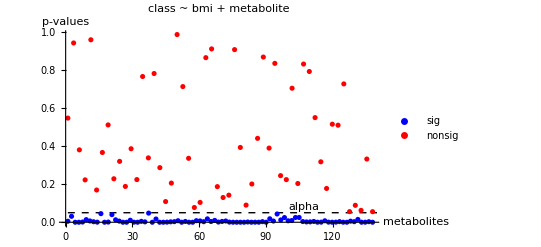

```mathematica
ListPlot[Tooltip[{datas,datans}],PlotLegends->{"sig","nonsig"},
PlotLabel->"class ~ bmi + metabolite",PlotStyle->{Blue,Red},DataRange->{1,138},AxesLabel->{"metabolites","p-values"},
Epilog->{ Dashed,
Line[{{1,0.05}, {140,0.05}}],Style[Text["alpha", {100,0.08},{-1,0}],
		      FontSize->8]}]
```

```mathematica
meTclasLM=LogitModelFit[
bC⟦2;;,{bMI,M6,M10,M16,M17,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M88,M89,M90,M91,M92,M93,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M105,M107,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M130,M131,M132,M133,M135,M136,M137,M138,class}⟧,{1,x,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM137,xM138},
{x,xM6,xM10,xM16,xM17,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM137,xM138}]
meTclasLM["BestFit"]
meTclasLM["ParameterTable"]
meTclasLMent=meTclasLM["ParameterTableEntries"];
meTclasLMf=Flatten[Position[meTclasLMent[[All,4]],_?(#>0.9&)]]
```

FittedModel[1/(1+ⅇ^(13.7695+«130»))]

1/(1+ⅇ^(13.7695+0.0132441 x+0.0259204 xM10+3.38124 xM100+0.0368802 xM101-0.0816458 xM102+2.87984 xM103-0.0351423 xM104+4.7014 xM105-2.41086 xM107-1.71698 xM109+0.170165 xM110-0.191942 xM111+1.28247 xM113-1.43885 xM114+0.314428 xM115+1.02402 xM116-1.56453 xM117-0.297115 xM118+1.29038 xM119-3.80752 xM120-0.153442 xM121-1.27973 xM122-9.69712 xM123+0.530918 xM124-1.89602 xM125-3.03603 xM126+0.887473 xM127+1.91404 xM129-0.152974 xM130+0.0108888 xM131+0.404697 xM132+0.324434 xM133-0.0936636 xM135-0.0508968 xM136-0.0192737 xM137-1.11152 xM138-0.316714 xM16+0.179851 xM17+8.06369 xM20+0.0496679 xM23+0.114537 xM24+0.0102299 xM25-0.0989376 xM27+0.0493359 xM32+0.0568635 xM33+1.55649 xM34-0.0237548 xM35+0.0800895 xM39+0.1114 xM40-3.38688 xM41+0.130918 xM43+0.0517721 xM44+0.0397261 xM45-0.651129 xM46-0.582809 xM47-0.107789 xM48+0.0545496 xM49-2.95412 xM53-0.989835 xM54-3.37753 xM55-0.872038 xM56-0.233115 xM57+0.136764 xM58+0.00281524 xM6-0.561744 xM60-0.0290959 xM65-0.454171 xM66-0.64352 xM69+0.185303 xM70-2.66769 xM71+0.298312 xM72-1.90561 xM73-0.501591 xM74+0.518621 xM87+0.0479652 xM88-0.0238231 xM89+0.0255749 xM90-0.668761 xM91+1.57593 xM92+0.0976244 xM93-0.0661794 xM95-0.0116585 xM96-0.0702004 xM97-0.00114231 xM98-0.366117 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.7695 | 5.36782 | -2.56519 | 0.0103118
x | -0.0132441 | 0.115119 | -0.115047 | 0.908408
xM6 | -0.00281524 | 0.0832104 | -0.0338328 | 0.973011
xM10 | -0.0259204 | 0.343131 | -0.075541 | 0.939784
xM16 | 0.316714 | 0.334183 | 0.947726 | 0.343269
xM17 | -0.179851 | 1.95464 | -0.0920122 | 0.926688
xM20 | -8.06369 | 2.7783 | -2.90238 | 0.00370339
xM23 | -0.0496679 | 0.0205605 | -2.41569 | 0.0157054
xM24 | -0.114537 | 0.0694549 | -1.64909 | 0.0991297
xM25 | -0.0102299 | 0.0148295 | -0.689837 | 0.490297
xM27 | 0.0989376 | 0.0330213 | 2.99617 | 0.0027339
xM32 | -0.0493359 | 0.0275454 | -1.79108 | 0.0732806
xM33 | -0.0568635 | 0.0285496 | -1.99175 | 0.046399
xM34 | -1.55649 | 1.38356 | -1.12499 | 0.260595
xM35 | 0.0237548 | 0.0261506 | 0.908383 | 0.363676
xM39 | -0.0800895 | 0.0312127 | -2.56592 | 0.0102901
xM40 | -0.1114 | 0.0404204 | -2.75603 | 0.00585068
xM41 | 3.38688 | 1.43739 | 2.35627 | 0.0184596
xM43 | -0.130918 | 0.0874166 | -1.49763 | 0.13423
xM44 | -0.0517721 | 0.0486314 | -1.06458 | 0.287065
xM45 | -0.0397261 | 0.0890914 | -0.445903 | 0.655667
xM46 | 0.651129 | 0.462346 | 1.40832 | 0.159038
xM47 | 0.582809 | 1.27835 | 0.455906 | 0.648458
xM48 | 0.107789 | 0.196497 | 0.548552 | 0.583313
xM49 | -0.0545496 | 0.0360193 | -1.51446 | 0.12991
xM53 | 2.95412 | 3.20743 | 0.921023 | 0.357039
xM54 | 0.989835 | 1.40734 | 0.703335 | 0.481847
xM55 | 3.37753 | 1.22982 | 2.74637 | 0.00602587
xM56 | 0.872038 | 0.560303 | 1.55637 | 0.119621
xM57 | 0.233115 | 0.0892837 | 2.61094 | 0.00902935
xM58 | -0.136764 | 0.190261 | -0.718823 | 0.47225
xM60 | 0.561744 | 0.249798 | 2.24879 | 0.0245256
xM65 | 0.0290959 | 0.0152795 | 1.90424 | 0.0568786
xM66 | 0.454171 | 0.154559 | 2.93849 | 0.00329817
xM69 | 0.64352 | 0.556389 | 1.1566 | 0.247435
xM70 | -0.185303 | 0.10643 | -1.74107 | 0.0816713
xM71 | 2.66769 | 1.10724 | 2.40931 | 0.0159828
xM72 | -0.298312 | 0.321357 | -0.928288 | 0.353258
xM73 | 1.90561 | 0.927923 | 2.05363 | 0.0400119
xM74 | 0.501591 | 0.249685 | 2.0089 | 0.0445482
xM87 | -0.518621 | 0.202036 | -2.56697 | 0.0102591
xM88 | -0.0479652 | 0.128978 | -0.371887 | 0.709977
xM89 | 0.0238231 | 0.0474306 | 0.502273 | 0.615476
xM90 | -0.0255749 | 0.0244134 | -1.04757 | 0.294835
xM91 | 0.668761 | 0.304623 | 2.19537 | 0.028137
xM92 | -1.57593 | 0.88833 | -1.77404 | 0.0760565
xM93 | -0.0976244 | 0.0610197 | -1.59988 | 0.109624
xM95 | 0.0661794 | 0.0324515 | 2.03933 | 0.0414167
xM96 | 0.0116585 | 0.00694859 | 1.67783 | 0.0933805
xM97 | 0.0702004 | 0.0666129 | 1.05386 | 0.291949
xM98 | 0.00114231 | 0.00770576 | 0.148241 | 0.882152
xM99 | 0.366117 | 0.94794 | 0.386223 | 0.699331
xM100 | -3.38124 | 1.53318 | -2.20537 | 0.0274283
xM101 | -0.0368802 | 0.0263635 | -1.39891 | 0.16184
xM102 | 0.0816458 | 0.034056 | 2.39739 | 0.0165121
xM103 | -2.87984 | 0.860413 | -3.34704 | 0.000816784
xM104 | 0.0351423 | 0.0232573 | 1.51102 | 0.130782
xM105 | -4.7014 | 1.57936 | -2.97677 | 0.00291299
xM107 | 2.41086 | 0.721374 | 3.34204 | 0.000831647
xM109 | 1.71698 | 1.41619 | 1.21239 | 0.225361
xM110 | -0.170165 | 1.91849 | -0.0886971 | 0.929323
xM111 | 0.191942 | 0.171366 | 1.12007 | 0.262684
xM113 | -1.28247 | 1.61454 | -0.794327 | 0.427005
xM114 | 1.43885 | 1.05246 | 1.36713 | 0.171583
xM115 | -0.314428 | 0.153039 | -2.05456 | 0.0399211
xM116 | -1.02402 | 0.508581 | -2.01349 | 0.0440633
xM117 | 1.56453 | 1.27645 | 1.22569 | 0.220316
xM118 | 0.297115 | 0.553301 | 0.536986 | 0.591278
xM119 | -1.29038 | 0.811585 | -1.58995 | 0.111846
xM120 | 3.80752 | 6.00882 | 0.633656 | 0.526306
xM121 | 0.153442 | 0.0631955 | 2.42805 | 0.0151803
xM122 | 1.27973 | 0.522804 | 2.44781 | 0.0143727
xM123 | 9.69712 | 3.37483 | 2.87336 | 0.00406125
xM124 | -0.530918 | 0.407334 | -1.3034 | 0.192438
xM125 | 1.89602 | 0.782263 | 2.42376 | 0.0153608
xM126 | 3.03603 | 2.0186 | 1.50402 | 0.132575
xM127 | -0.887473 | 0.305112 | -2.90868 | 0.00362963
xM129 | -1.91404 | 0.753899 | -2.53886 | 0.0111216
xM130 | 0.152974 | 0.484817 | 0.315529 | 0.75236
xM131 | -0.0108888 | 0.244497 | -0.0445354 | 0.964478
xM132 | -0.404697 | 0.159583 | -2.53597 | 0.0112137
xM133 | -0.324434 | 0.254957 | -1.2725 | 0.203194
xM135 | 0.0936636 | 0.182709 | 0.512639 | 0.608204
xM136 | 0.0508968 | 0.255087 | 0.199527 | 0.84185
xM137 | 0.0192737 | 0.0791159 | 0.243614 | 0.80753
xM138 | 1.11152 | 1.65477 | 0.671707 | 0.50177

{2,3,4,6,61,80}

```mathematica
meTclasLM1=LogitModelFit[
bC⟦2;;,{bMI,M6,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M88,M89,M90,M91,M92,M93,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M130,M131,M132,M133,M135,M136,M137,M138,class}⟧,{1,x,xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM137,xM138},
{x,xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM131,xM132,xM133,xM135,xM136,xM137,xM138}]
meTclasLM1["BestFit"]
meTclasLM1["ParameterTable"]
meTclasLMent1=meTclasLM1["ParameterTableEntries"];
meTclasLMf1=Flatten[Position[meTclasLMent1[[All,4]],_?(#>0.9&)]]
```

FittedModel[1/(1+ⅇ^(13.6084+«128»))]

1/(1+ⅇ^(13.6084+0.0170062 x+3.39873 xM100+0.0367238 xM101-0.0813349 xM102+2.86653 xM103-0.0356199 xM104+4.7423 xM105-2.4169 xM107-1.73659 xM109-0.197416 xM111+1.40469 xM113-1.45651 xM114+0.312057 xM115+1.04639 xM116-1.57599 xM117-0.291072 xM118+1.30301 xM119-4.0341 xM120-0.152157 xM121-1.2907 xM122-9.73962 xM123+0.518568 xM124-1.89923 xM125-3.01184 xM126+0.893617 xM127+1.94874 xM129-0.15215 xM130-0.000639047 xM131+0.405948 xM132+0.319774 xM133-0.0944516 xM135-0.0516486 xM136-0.0212128 xM137-1.05893 xM138-0.315964 xM16+8.13934 xM20+0.0491631 xM23+0.118595 xM24+0.011002 xM25-0.0994156 xM27+0.0484371 xM32+0.0574645 xM33+1.55317 xM34-0.0231573 xM35+0.0794023 xM39+0.11118 xM40-3.33327 xM41+0.131644 xM43+0.0511809 xM44+0.0416168 xM45-0.655804 xM46-0.540296 xM47-0.103813 xM48+0.0539804 xM49-2.88179 xM53-1.03037 xM54-3.37278 xM55-0.888862 xM56-0.232278 xM57+0.13807 xM58+0.00911391 xM6-0.562251 xM60-0.0287601 xM65-0.457877 xM66-0.653168 xM69+0.187189 xM70-2.67848 xM71+0.299362 xM72-1.90932 xM73-0.506368 xM74+0.515675 xM87+0.0459855 xM88-0.0225023 xM89+0.0260694 xM90-0.664535 xM91+1.57825 xM92+0.0982157 xM93-0.0662864 xM95-0.0117204 xM96-0.0682667 xM97-0.00152281 xM98-0.406389 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.6084 | 5.15465 | -2.64003 | 0.00828998
x | -0.0170062 | 0.11195 | -0.151908 | 0.879259
xM6 | -0.00911391 | 0.0278868 | -0.326818 | 0.743805
xM16 | 0.315964 | 0.291975 | 1.08216 | 0.279181
xM20 | -8.13934 | 2.65023 | -3.07119 | 0.0021321
xM23 | -0.0491631 | 0.0192486 | -2.55412 | 0.0106457
xM24 | -0.118595 | 0.0613022 | -1.93459 | 0.0530407
xM25 | -0.011002 | 0.0129033 | -0.852649 | 0.393854
xM27 | 0.0994156 | 0.0325997 | 3.04958 | 0.00229159
xM32 | -0.0484371 | 0.0242785 | -1.99506 | 0.0460364
xM33 | -0.0574645 | 0.0272102 | -2.11188 | 0.034697
xM34 | -1.55317 | 1.32796 | -1.1696 | 0.242163
xM35 | 0.0231573 | 0.0252654 | 0.916563 | 0.359372
xM39 | -0.0794023 | 0.0306538 | -2.59029 | 0.00958948
xM40 | -0.11118 | 0.0396286 | -2.80554 | 0.00502329
xM41 | 3.33327 | 1.32324 | 2.51901 | 0.0117685
xM43 | -0.131644 | 0.0849287 | -1.55005 | 0.121129
xM44 | -0.0511809 | 0.0457029 | -1.11986 | 0.262773
xM45 | -0.0416168 | 0.0867058 | -0.479977 | 0.631243
xM46 | 0.655804 | 0.464622 | 1.41148 | 0.158103
xM47 | 0.540296 | 1.18226 | 0.457003 | 0.647669
xM48 | 0.103813 | 0.185223 | 0.560476 | 0.575155
xM49 | -0.0539804 | 0.0348158 | -1.55046 | 0.121032
xM53 | 2.88179 | 3.04229 | 0.947244 | 0.343515
xM54 | 1.03037 | 1.36795 | 0.753222 | 0.451316
xM55 | 3.37278 | 1.21624 | 2.77313 | 0.00555192
xM56 | 0.888862 | 0.528883 | 1.68064 | 0.0928328
xM57 | 0.232278 | 0.0868946 | 2.6731 | 0.00751528
xM58 | -0.13807 | 0.189864 | -0.727204 | 0.467101
xM60 | 0.562251 | 0.244995 | 2.29495 | 0.021736
xM65 | 0.0287601 | 0.0149432 | 1.92462 | 0.0542771
xM66 | 0.457877 | 0.152112 | 3.01014 | 0.00261126
xM69 | 0.653168 | 0.52941 | 1.23377 | 0.21729
xM70 | -0.187189 | 0.103347 | -1.81126 | 0.0701006
xM71 | 2.67848 | 1.08068 | 2.4785 | 0.0131935
xM72 | -0.299362 | 0.319753 | -0.93623 | 0.349155
xM73 | 1.90932 | 0.923479 | 2.06753 | 0.0386839
xM74 | 0.506368 | 0.248018 | 2.04166 | 0.0411852
xM87 | -0.515675 | 0.195245 | -2.64117 | 0.00826191
xM88 | -0.0459855 | 0.122405 | -0.375684 | 0.707152
xM89 | 0.0225023 | 0.045657 | 0.492855 | 0.622115
xM90 | -0.0260694 | 0.023232 | -1.12213 | 0.261805
xM91 | 0.664535 | 0.297333 | 2.23498 | 0.0254185
xM92 | -1.57825 | 0.883778 | -1.7858 | 0.0741312
xM93 | -0.0982157 | 0.0595434 | -1.64948 | 0.0990492
xM95 | 0.0662864 | 0.0314959 | 2.1046 | 0.035326
xM96 | 0.0117204 | 0.00674298 | 1.73816 | 0.0821824
xM97 | 0.0682667 | 0.0632325 | 1.07961 | 0.280314
xM98 | 0.00152281 | 0.00721085 | 0.211183 | 0.832745
xM99 | 0.406389 | 0.855628 | 0.474959 | 0.634816
xM100 | -3.39873 | 1.47933 | -2.29748 | 0.0215913
xM101 | -0.0367238 | 0.0256042 | -1.43429 | 0.15149
xM102 | 0.0813349 | 0.033581 | 2.42205 | 0.0154332
xM103 | -2.86653 | 0.84563 | -3.38981 | 0.000699399
xM104 | 0.0356199 | 0.0220259 | 1.61718 | 0.105839
xM105 | -4.7423 | 1.54046 | -3.0785 | 0.00208048
xM107 | 2.4169 | 0.717208 | 3.36987 | 0.000752044
xM109 | 1.73659 | 1.37818 | 1.26006 | 0.207648
xM111 | 0.197416 | 0.163344 | 1.20859 | 0.226821
xM113 | -1.40469 | 1.31439 | -1.0687 | 0.285204
xM114 | 1.45651 | 0.883857 | 1.6479 | 0.0993724
xM115 | -0.312057 | 0.149996 | -2.08043 | 0.0374859
xM116 | -1.04639 | 0.460919 | -2.27023 | 0.0231936
xM117 | 1.57599 | 1.26819 | 1.24271 | 0.213975
xM118 | 0.291072 | 0.536955 | 0.542078 | 0.587764
xM119 | -1.30301 | 0.794445 | -1.64015 | 0.100974
xM120 | 4.0341 | 5.80035 | 0.695493 | 0.486747
xM121 | 0.152157 | 0.0619186 | 2.45737 | 0.0139957
xM122 | 1.2907 | 0.510367 | 2.52896 | 0.0114402
xM123 | 9.73962 | 3.28794 | 2.96222 | 0.00305427
xM124 | -0.518568 | 0.383784 | -1.35119 | 0.176633
xM125 | 1.89923 | 0.774152 | 2.4533 | 0.0141552
xM126 | 3.01184 | 1.9637 | 1.53376 | 0.125088
xM127 | -0.893617 | 0.294843 | -3.03082 | 0.00243887
xM129 | -1.94874 | 0.723272 | -2.69433 | 0.00705294
xM130 | 0.15215 | 0.468603 | 0.324689 | 0.745417
xM131 | 0.000639047 | 0.222566 | 0.00287127 | 0.997709
xM132 | -0.405948 | 0.153499 | -2.64463 | 0.00817807
xM133 | -0.319774 | 0.249623 | -1.28103 | 0.200185
xM135 | 0.0944516 | 0.179575 | 0.525974 | 0.598907
xM136 | 0.0516486 | 0.24571 | 0.210201 | 0.833511
xM137 | 0.0212128 | 0.0777344 | 0.272888 | 0.78494
xM138 | 1.05893 | 1.60777 | 0.658631 | 0.510133

{77}

```mathematica
meTclasLM2=LogitModelFit[
bC⟦2;;,{bMI,M6,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M88,M89,M90,M91,M92,M93,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M130,M132,M133,M135,M136,M137,M138,class}⟧,{1,x,xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM132,xM133,xM135,xM136,xM137,xM138},
{x,xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM132,xM133,xM135,xM136,xM137,xM138}]
meTclasLM2["BestFit"]
meTclasLM2["ParameterTable"]
meTclasLMent2=meTclasLM2["ParameterTableEntries"];
meTclasLMf2=Flatten[Position[meTclasLMent2[[All,4]],_?(#>0.8&)]]
```

FittedModel[1/(1+ⅇ^(13.6079+«126»))]

1/(1+ⅇ^(13.6079+0.0170043 x+3.39952 xM100+0.0367268 xM101-0.0813496 xM102+2.86694 xM103-0.0356153 xM104+4.74271 xM105-2.4171 xM107-1.7358 xM109-0.197616 xM111+1.40477 xM113-1.45633 xM114+0.312099 xM115+1.04662 xM116-1.57635 xM117-0.291242 xM118+1.30309 xM119-4.0346 xM120-0.152207 xM121-1.29069 xM122-9.74084 xM123+0.518779 xM124-1.89977 xM125-3.01239 xM126+0.89372 xM127+1.94854 xM129-0.152183 xM130+0.405973 xM132+0.319758 xM133-0.0944231 xM135-0.0515297 xM136-0.0212417 xM137-1.05897 xM138-0.315984 xM16+8.13954 xM20+0.049159 xM23+0.118631 xM24+0.0110091 xM25-0.0994227 xM27+0.0484289 xM32+0.0574557 xM33+1.55367 xM34-0.0231639 xM35+0.0794015 xM39+0.111161 xM40-3.33361 xM41+0.131663 xM43+0.0512056 xM44+0.0416719 xM45-0.656167 xM46-0.539463 xM47-0.103816 xM48+0.053982 xM49-2.88095 xM53-1.02987 xM54-3.37275 xM55-0.888898 xM56-0.232296 xM57+0.138007 xM58+0.00911481 xM6-0.562223 xM60-0.0287568 xM65-0.45793 xM66-0.652744 xM69+0.18718 xM70-2.67859 xM71+0.299334 xM72-1.90929 xM73-0.506472 xM74+0.515737 xM87+0.0460344 xM88-0.0225083 xM89+0.0260644 xM90-0.664553 xM91+1.57751 xM92+0.0982061 xM93-0.0662693 xM95-0.0117212 xM96-0.0683499 xM97-0.00151821 xM98-0.405699 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.6079 | 5.1516 | -2.64149 | 0.00825428
x | -0.0170043 | 0.111944 | -0.1519 | 0.879266
xM6 | -0.00911481 | 0.0278868 | -0.326851 | 0.743781
xM16 | 0.315984 | 0.291881 | 1.08258 | 0.278996
xM20 | -8.13954 | 2.64936 | -3.07227 | 0.00212441
xM23 | -0.049159 | 0.0191989 | -2.56051 | 0.0104518
xM24 | -0.118631 | 0.0599732 | -1.97807 | 0.0479211
xM25 | -0.0110091 | 0.012662 | -0.869461 | 0.384595
xM27 | 0.0994227 | 0.0325099 | 3.05823 | 0.00222648
xM32 | -0.0484289 | 0.0241068 | -2.00893 | 0.0445446
xM33 | -0.0574557 | 0.0270345 | -2.12527 | 0.0335638
xM34 | -1.55367 | 1.31682 | -1.17986 | 0.238055
xM35 | 0.0231639 | 0.0251629 | 0.920557 | 0.357282
xM39 | -0.0794015 | 0.030654 | -2.59025 | 0.00959066
xM40 | -0.111161 | 0.0390867 | -2.84396 | 0.00445569
xM41 | 3.33361 | 1.31801 | 2.52928 | 0.0114296
xM43 | -0.131663 | 0.0846691 | -1.55503 | 0.119938
xM44 | -0.0512056 | 0.044886 | -1.14079 | 0.253956
xM45 | -0.0416719 | 0.0845547 | -0.492839 | 0.622126
xM46 | 0.656167 | 0.447008 | 1.46791 | 0.142129
xM47 | 0.539463 | 1.14609 | 0.470696 | 0.637858
xM48 | 0.103816 | 0.185196 | 0.560574 | 0.575088
xM49 | -0.053982 | 0.0348126 | -1.55065 | 0.120986
xM53 | 2.88095 | 3.02777 | 0.951507 | 0.341347
xM54 | 1.02987 | 1.35679 | 0.759045 | 0.447826
xM55 | 3.37275 | 1.2162 | 2.77318 | 0.00555111
xM56 | 0.888898 | 0.528701 | 1.68129 | 0.0927073
xM57 | 0.232296 | 0.0866875 | 2.67969 | 0.007369
xM58 | -0.138007 | 0.188626 | -0.731644 | 0.464386
xM60 | 0.562223 | 0.24482 | 2.29648 | 0.0216485
xM65 | 0.0287568 | 0.0148974 | 1.93032 | 0.0535666
xM66 | 0.45793 | 0.150989 | 3.03287 | 0.00242243
xM69 | 0.652744 | 0.508404 | 1.28391 | 0.199174
xM70 | -0.18718 | 0.103304 | -1.81194 | 0.0699959
xM71 | 2.67859 | 1.07999 | 2.48019 | 0.0131311
xM72 | -0.299334 | 0.319625 | -0.936516 | 0.349008
xM73 | 1.90929 | 0.923465 | 2.06753 | 0.0386843
xM74 | 0.506472 | 0.245367 | 2.06414 | 0.0390045
xM87 | -0.515737 | 0.194082 | -2.65731 | 0.00787667
xM88 | -0.0460344 | 0.12121 | -0.37979 | 0.704101
xM89 | 0.0225083 | 0.0456072 | 0.493526 | 0.621641
xM90 | -0.0260644 | 0.0231644 | -1.12519 | 0.260508
xM91 | 0.664553 | 0.297266 | 2.23555 | 0.0253813
xM92 | -1.57751 | 0.844832 | -1.86725 | 0.0618673
xM93 | -0.0982061 | 0.059452 | -1.65185 | 0.0985642
xM95 | 0.0662693 | 0.0309234 | 2.14302 | 0.0321118
xM96 | 0.0117212 | 0.00673793 | 1.73958 | 0.0819325
xM97 | 0.0683499 | 0.0562051 | 1.21608 | 0.223955
xM98 | 0.00151821 | 0.00703018 | 0.215956 | 0.829022
xM99 | 0.405699 | 0.82119 | 0.494038 | 0.621279
xM100 | -3.39952 | 1.45377 | -2.33842 | 0.0193655
xM101 | -0.0367268 | 0.025582 | -1.43565 | 0.151102
xM102 | 0.0813496 | 0.0331919 | 2.45088 | 0.0142507
xM103 | -2.86694 | 0.833292 | -3.4405 | 0.000580641
xM104 | 0.0356153 | 0.021965 | 1.62146 | 0.104919
xM105 | -4.74271 | 1.53381 | -3.09211 | 0.00198742
xM107 | 2.4171 | 0.713836 | 3.38607 | 0.000709025
xM109 | 1.7358 | 1.35018 | 1.28561 | 0.19858
xM111 | 0.197616 | 0.147657 | 1.33834 | 0.180784
xM113 | -1.40477 | 1.31415 | -1.06896 | 0.28509
xM114 | 1.45633 | 0.881625 | 1.65187 | 0.098562
xM115 | -0.312099 | 0.149276 | -2.09075 | 0.0365504
xM116 | -1.04662 | 0.454075 | -2.30495 | 0.0211692
xM117 | 1.57635 | 1.26205 | 1.24904 | 0.211649
xM118 | 0.291242 | 0.533712 | 0.545692 | 0.585278
xM119 | -1.30309 | 0.793964 | -1.64124 | 0.100747
xM120 | 4.0346 | 5.79763 | 0.695906 | 0.486488
xM121 | 0.152207 | 0.0594425 | 2.56057 | 0.01045
xM122 | 1.29069 | 0.510349 | 2.52903 | 0.011438
xM123 | 9.74084 | 3.26042 | 2.9876 | 0.00281175
xM124 | -0.518779 | 0.37667 | -1.37728 | 0.168427
xM125 | 1.89977 | 0.750707 | 2.53064 | 0.0113854
xM126 | 3.01239 | 1.95452 | 1.54124 | 0.123258
xM127 | -0.89372 | 0.292677 | -3.05361 | 0.00226105
xM129 | -1.94854 | 0.71997 | -2.70642 | 0.00680133
xM130 | 0.152183 | 0.468414 | 0.32489 | 0.745264
xM132 | -0.405973 | 0.153265 | -2.64882 | 0.00807722
xM133 | -0.319758 | 0.249575 | -1.28121 | 0.200119
xM135 | 0.0944231 | 0.179289 | 0.526653 | 0.598435
xM136 | 0.0515297 | 0.242196 | 0.212761 | 0.831514
xM137 | 0.0212417 | 0.0770779 | 0.275588 | 0.782865
xM138 | 1.05897 | 1.60762 | 0.658721 | 0.510075

{2,49,80}

```mathematica
meTclasLM2=LogitModelFit[
bC⟦2;;,{bMI,M6,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M88,M89,M90,M91,M92,M93,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M130,M132,M133,M135,M137,M138,class}⟧,{1,x,xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM132,xM133,xM135,xM137,xM138},
{x,xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM130,xM132,xM133,xM135,xM137,xM138}]
meTclasLM2["BestFit"]
meTclasLM2["ParameterTable"]
meTclasLMent2=meTclasLM2["ParameterTableEntries"];
meTclasLMf2=Flatten[Position[meTclasLMent2[[All,4]],_?(#>0.7&)]]
```

FittedModel[1/(1+ⅇ^(13.5286+«122»))]

1/(1+ⅇ^(13.5286+0.0137395 x+3.31547 xM100+0.0358006 xM101-0.0812694 xM102+2.83862 xM103-0.0355831 xM104+4.74058 xM105-2.41028 xM107-1.74345 xM109-0.209201 xM111+1.39411 xM113-1.43723 xM114+0.321389 xM115+1.07123 xM116-1.5924 xM117-0.28918 xM118+1.28317 xM119-4.00236 xM120-0.156541 xM121-1.28139 xM122-9.74891 xM123+0.519207 xM124-1.93539 xM125-2.90133 xM126+0.885383 xM127+1.93873 xM129-0.146081 xM130+0.393533 xM132+0.320921 xM133-0.118844 xM135-0.0264274 xM137-0.982204 xM138-0.309558 xM16+8.05931 xM20+0.0501871 xM23+0.118648 xM24+0.0101266 xM25-0.0987123 xM27+0.0477578 xM32+0.0557951 xM33+1.55146 xM34-0.0233906 xM35+0.0787684 xM39+0.10696 xM40-3.34488 xM41+0.131262 xM43+0.0532584 xM44+0.0354743 xM45-0.650579 xM46-0.466562 xM47-0.0955109 xM48+0.0535945 xM49-2.80095 xM53-0.986054 xM54-3.33747 xM55-0.877341 xM56-0.230791 xM57+0.130819 xM58+0.00798876 xM6-0.547312 xM60-0.0281041 xM65-0.454735 xM66-0.617748 xM69+0.18476 xM70-2.68188 xM71+0.299633 xM72-1.89253 xM73-0.495575 xM74+0.516598 xM87+0.0386852 xM88-0.0217812 xM89+0.0235255 xM90-0.639405 xM91+1.48285 xM92+0.0995323 xM93-0.0656574 xM95-0.0118442 xM96-0.069205 xM97-0.374994 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.5286 | 5.11154 | -2.64669 | 0.00812847
x | -0.0137395 | 0.107211 | -0.128154 | 0.898027
xM6 | -0.00798876 | 0.027302 | -0.292607 | 0.769823
xM16 | 0.309558 | 0.29 | 1.06744 | 0.285773
xM20 | -8.05931 | 2.61487 | -3.0821 | 0.00205543
xM23 | -0.0501871 | 0.0184479 | -2.72048 | 0.00651872
xM24 | -0.118648 | 0.0598197 | -1.98343 | 0.0473189
xM25 | -0.0101266 | 0.0121508 | -0.833416 | 0.40461
xM27 | 0.0987123 | 0.0322135 | 3.06431 | 0.00218172
xM32 | -0.0477578 | 0.0236761 | -2.01713 | 0.0436821
xM33 | -0.0557951 | 0.025675 | -2.17313 | 0.0297702
xM34 | -1.55146 | 1.29656 | -1.1966 | 0.231463
xM35 | 0.0233906 | 0.0252817 | 0.925199 | 0.354862
xM39 | -0.0787684 | 0.0304166 | -2.58965 | 0.00960738
xM40 | -0.10696 | 0.0356374 | -3.00135 | 0.00268788
xM41 | 3.34488 | 1.30956 | 2.5542 | 0.0106433
xM43 | -0.131262 | 0.0823424 | -1.5941 | 0.110915
xM44 | -0.0532584 | 0.0434972 | -1.22441 | 0.220798
xM45 | -0.0354743 | 0.0791087 | -0.448425 | 0.653847
xM46 | 0.650579 | 0.430681 | 1.51058 | 0.130895
xM47 | 0.466562 | 1.10804 | 0.421072 | 0.673703
xM48 | 0.0955109 | 0.179459 | 0.532216 | 0.594576
xM49 | -0.0535945 | 0.0345292 | -1.55215 | 0.120626
xM53 | 2.80095 | 2.91427 | 0.961115 | 0.336494
xM54 | 0.986054 | 1.33909 | 0.736364 | 0.461509
xM55 | 3.33747 | 1.1881 | 2.80909 | 0.00496815
xM56 | 0.877341 | 0.515634 | 1.70148 | 0.0888533
xM57 | 0.230791 | 0.0858613 | 2.68795 | 0.00718911
xM58 | -0.130819 | 0.18149 | -0.720808 | 0.471028
xM60 | 0.547312 | 0.235765 | 2.32143 | 0.0202635
xM65 | 0.0281041 | 0.0143024 | 1.965 | 0.0494145
xM66 | 0.454735 | 0.148906 | 3.05384 | 0.00225931
xM69 | 0.617748 | 0.489469 | 1.26208 | 0.20692
xM70 | -0.18476 | 0.101976 | -1.8118 | 0.0700172
xM71 | 2.68188 | 1.07591 | 2.49266 | 0.0126789
xM72 | -0.299633 | 0.308343 | -0.971754 | 0.331173
xM73 | 1.89253 | 0.909142 | 2.08167 | 0.0373731
xM74 | 0.495575 | 0.240087 | 2.06415 | 0.0390034
xM87 | -0.516598 | 0.194821 | -2.65166 | 0.00800968
xM88 | -0.0386852 | 0.116492 | -0.332085 | 0.739825
xM89 | 0.0217812 | 0.0455194 | 0.478504 | 0.632291
xM90 | -0.0235255 | 0.0212366 | -1.10778 | 0.267957
xM91 | 0.639405 | 0.282542 | 2.26304 | 0.0236331
xM92 | -1.48285 | 0.775875 | -1.91119 | 0.0559795
xM93 | -0.0995323 | 0.059117 | -1.68365 | 0.0922496
xM95 | 0.0656574 | 0.0292549 | 2.24432 | 0.0248117
xM96 | 0.0118442 | 0.00640733 | 1.84854 | 0.0645241
xM97 | 0.069205 | 0.0566089 | 1.22251 | 0.221514
xM99 | 0.374994 | 0.813729 | 0.460834 | 0.644918
xM100 | -3.31547 | 1.41361 | -2.3454 | 0.0190065
xM101 | -0.0358006 | 0.0245646 | -1.4574 | 0.145005
xM102 | 0.0812694 | 0.0327092 | 2.48461 | 0.0129694
xM103 | -2.83862 | 0.820518 | -3.45954 | 0.000541097
xM104 | 0.0355831 | 0.0217462 | 1.63629 | 0.101779
xM105 | -4.74058 | 1.51301 | -3.13322 | 0.00172901
xM107 | 2.41028 | 0.704737 | 3.42011 | 0.000625958
xM109 | 1.74345 | 1.33685 | 1.30415 | 0.192183
xM111 | 0.209201 | 0.140993 | 1.48377 | 0.137871
xM113 | -1.39411 | 1.30458 | -1.06862 | 0.285239
xM114 | 1.43723 | 0.875786 | 1.64107 | 0.100783
xM115 | -0.321389 | 0.145115 | -2.21471 | 0.0267799
xM116 | -1.07123 | 0.451696 | -2.37156 | 0.0177131
xM117 | 1.5924 | 1.23514 | 1.28925 | 0.197312
xM118 | 0.28918 | 0.521305 | 0.554723 | 0.579084
xM119 | -1.28317 | 0.784091 | -1.6365 | 0.101734
xM120 | 4.00236 | 5.53397 | 0.723235 | 0.469535
xM121 | 0.156541 | 0.0573908 | 2.72763 | 0.00637904
xM122 | 1.28139 | 0.50647 | 2.53005 | 0.0114048
xM123 | 9.74891 | 3.24241 | 3.00669 | 0.00264111
xM124 | -0.519207 | 0.366711 | -1.41585 | 0.156821
xM125 | 1.93539 | 0.747038 | 2.59075 | 0.00957658
xM126 | 2.90133 | 1.87171 | 1.5501 | 0.121117
xM127 | -0.885383 | 0.286662 | -3.08859 | 0.00201107
xM129 | -1.93873 | 0.711808 | -2.72367 | 0.00645612
xM130 | 0.146081 | 0.45257 | 0.322782 | 0.74686
xM132 | -0.393533 | 0.136524 | -2.88253 | 0.00394494
xM133 | -0.320921 | 0.249522 | -1.28614 | 0.198393
xM135 | 0.118844 | 0.152386 | 0.779887 | 0.435457
xM137 | 0.0264274 | 0.0720594 | 0.366745 | 0.71381
xM138 | 0.982204 | 1.56807 | 0.626377 | 0.531068

{2,3,40,75,79}

```mathematica
meTclasLM3=LogitModelFit[
bC⟦2;;,{bMI,M6,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,M137,M138,class}⟧,{1,x,xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135,xM137,xM138},
{x,xM6,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135,xM137,xM138}]
meTclasLM3["BestFit"]
meTclasLM3["ParameterTable"]
meTclasLMent3=meTclasLM3["ParameterTableEntries"];
meTclasLMf3=Flatten[Position[meTclasLMent3[[All,4]],_?(#>0.7&)]]
```

FittedModel[1/(1+ⅇ^(13.5844+«119»))]

1/(1+ⅇ^(13.5844+0.0296463 x+3.44322 xM100+0.0388005 xM101-0.0813103 xM102+2.87821 xM103-0.037363 xM104+4.91869 xM105-2.49431 xM107-1.84823 xM109-0.207015 xM111+1.35915 xM113-1.36883 xM114+0.33505 xM115+1.07235 xM116-1.54787 xM117-0.303607 xM118+1.35534 xM119-3.83404 xM120-0.159175 xM121-1.30589 xM122-10.118 xM123+0.519624 xM124-2.00223 xM125-2.8815 xM126+0.909355 xM127+1.91381 xM129+0.396587 xM132+0.335291 xM133-0.126934 xM135-0.0274509 xM137-0.930928 xM138-0.331434 xM16+8.10745 xM20+0.0504495 xM23+0.115477 xM24+0.00956567 xM25-0.101459 xM27+0.050383 xM32+0.0576512 xM33+1.78843 xM34-0.0232362 xM35+0.0822159 xM39+0.10964 xM40-3.48639 xM41+0.133529 xM43+0.0525558 xM44+0.0387415 xM45-0.655907 xM46-0.476158 xM47-0.0907579 xM48+0.0553378 xM49-3.16619 xM53-1.0962 xM54-3.58257 xM55-0.905033 xM56-0.240051 xM57+0.142426 xM58+0.00701409 xM6-0.558071 xM60-0.0297115 xM65-0.470943 xM66-0.601685 xM69+0.19574 xM70-2.73379 xM71+0.318698 xM72-1.93586 xM73-0.492362 xM74+0.535634 xM87-0.0228013 xM89+0.0216113 xM90-0.624046 xM91+1.50876 xM92+0.105641 xM93-0.0643995 xM95-0.0116647 xM96-0.0740885 xM97-0.413947 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.5844 | 5.13907 | -2.64336 | 0.00820868
x | -0.0296463 | 0.101608 | -0.291772 | 0.770461
xM6 | -0.00701409 | 0.0271982 | -0.257888 | 0.796493
xM16 | 0.331434 | 0.2873 | 1.15362 | 0.248657
xM20 | -8.10745 | 2.65573 | -3.05281 | 0.00226711
xM23 | -0.0504495 | 0.0187089 | -2.69655 | 0.00700621
xM24 | -0.115477 | 0.0589202 | -1.95989 | 0.0500086
xM25 | -0.00956567 | 0.0120138 | -0.796222 | 0.425903
xM27 | 0.101459 | 0.032053 | 3.16535 | 0.00154894
xM32 | -0.050383 | 0.0233364 | -2.15899 | 0.0308509
xM33 | -0.0576512 | 0.0254844 | -2.26222 | 0.023684
xM34 | -1.78843 | 1.18357 | -1.51105 | 0.130777
xM35 | 0.0232362 | 0.0254388 | 0.913416 | 0.361024
xM39 | -0.0822159 | 0.0296982 | -2.76838 | 0.00563358
xM40 | -0.10964 | 0.0356895 | -3.07205 | 0.00212598
xM41 | 3.48639 | 1.29845 | 2.68505 | 0.00725195
xM43 | -0.133529 | 0.080959 | -1.64933 | 0.099079
xM44 | -0.0525558 | 0.0435358 | -1.20719 | 0.22736
xM45 | -0.0387415 | 0.0741222 | -0.52267 | 0.601204
xM46 | 0.655907 | 0.436896 | 1.50129 | 0.133281
xM47 | 0.476158 | 1.09963 | 0.433016 | 0.665003
xM48 | 0.0907579 | 0.179214 | 0.506423 | 0.61256
xM49 | -0.0553378 | 0.034155 | -1.6202 | 0.10519
xM53 | 3.16619 | 2.77215 | 1.14214 | 0.253395
xM54 | 1.0962 | 1.322 | 0.829193 | 0.406995
xM55 | 3.58257 | 1.03967 | 3.44588 | 0.000569209
xM56 | 0.905033 | 0.497221 | 1.82018 | 0.0687313
xM57 | 0.240051 | 0.0837483 | 2.86634 | 0.0041525
xM58 | -0.142426 | 0.177216 | -0.803683 | 0.42158
xM60 | 0.558071 | 0.235194 | 2.37281 | 0.0176532
xM65 | 0.0297115 | 0.0140319 | 2.11742 | 0.0342242
xM66 | 0.470943 | 0.14733 | 3.19652 | 0.00139097
xM69 | 0.601685 | 0.485554 | 1.23917 | 0.215281
xM70 | -0.19574 | 0.0996079 | -1.96511 | 0.049402
xM71 | 2.73379 | 1.0786 | 2.53458 | 0.0112584
xM72 | -0.318698 | 0.304229 | -1.04756 | 0.294841
xM73 | 1.93586 | 0.916212 | 2.11289 | 0.0346099
xM74 | 0.492362 | 0.240783 | 2.04484 | 0.0408706
xM87 | -0.535634 | 0.194894 | -2.74834 | 0.00598978
xM89 | 0.0228013 | 0.0455846 | 0.500196 | 0.616937
xM90 | -0.0216113 | 0.020504 | -1.05401 | 0.291879
xM91 | 0.624046 | 0.280676 | 2.22337 | 0.0261907
xM92 | -1.50876 | 0.786154 | -1.91917 | 0.0549633
xM93 | -0.105641 | 0.0579705 | -1.82232 | 0.0684066
xM95 | 0.0643995 | 0.0291986 | 2.20557 | 0.0274144
xM96 | 0.0116647 | 0.0064929 | 1.79652 | 0.0724111
xM97 | 0.0740885 | 0.0553466 | 1.33863 | 0.180692
xM99 | 0.413947 | 0.80905 | 0.511646 | 0.608899
xM100 | -3.44322 | 1.41157 | -2.43928 | 0.0147164
xM101 | -0.0388005 | 0.0237276 | -1.63525 | 0.101997
xM102 | 0.0813103 | 0.0323955 | 2.50993 | 0.0120755
xM103 | -2.87821 | 0.829404 | -3.47022 | 0.000520033
xM104 | 0.037363 | 0.0217463 | 1.71813 | 0.0857721
xM105 | -4.91869 | 1.45975 | -3.36954 | 0.000752943
xM107 | 2.49431 | 0.687002 | 3.63073 | 0.000282625
xM109 | 1.84823 | 1.32733 | 1.39244 | 0.163789
xM111 | 0.207015 | 0.137196 | 1.5089 | 0.131324
xM113 | -1.35915 | 1.30444 | -1.04194 | 0.297438
xM114 | 1.36883 | 0.868411 | 1.57624 | 0.11497
xM115 | -0.33505 | 0.139292 | -2.40538 | 0.0161555
xM116 | -1.07235 | 0.455641 | -2.35351 | 0.0185973
xM117 | 1.54787 | 1.2419 | 1.24637 | 0.212629
xM118 | 0.303607 | 0.525049 | 0.578244 | 0.563099
xM119 | -1.35534 | 0.78032 | -1.7369 | 0.0824045
xM120 | 3.83404 | 5.53611 | 0.692552 | 0.488591
xM121 | 0.159175 | 0.0579968 | 2.74455 | 0.0060594
xM122 | 1.30589 | 0.51231 | 2.54902 | 0.0108025
xM123 | 10.118 | 3.21375 | 3.14834 | 0.00164203
xM124 | -0.519624 | 0.368256 | -1.41104 | 0.158233
xM125 | 2.00223 | 0.745252 | 2.68665 | 0.00721732
xM126 | 2.8815 | 1.89584 | 1.51991 | 0.128534
xM127 | -0.909355 | 0.288793 | -3.14882 | 0.00163933
xM129 | -1.91381 | 0.703557 | -2.72019 | 0.00652446
xM132 | -0.396587 | 0.135407 | -2.92885 | 0.00340217
xM133 | -0.335291 | 0.248586 | -1.34879 | 0.177404
xM135 | 0.126934 | 0.155679 | 0.815359 | 0.414867
xM137 | 0.0274509 | 0.0711938 | 0.38558 | 0.699807
xM138 | 0.930928 | 1.57219 | 0.592121 | 0.553769

{2,3}

```mathematica
meTclasLM4=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,M137,M138,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135,xM137,xM138},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135,xM137,xM138}]
meTclasLM4["BestFit"]
meTclasLM4["ParameterTable"]
meTclasLMent4=meTclasLM4["ParameterTableEntries"];
meTclasLMf4=Flatten[Position[meTclasLMent4[[All,4]],_?(#>0.6&)]]
```

FittedModel[1/(1+ⅇ^(13.5043+«118»))]

1/(1+ⅇ^(13.5043+0.0304476 x+3.37012 xM100+0.0373314 xM101-0.0797541 xM102+2.8377 xM103-0.0367023 xM104+4.8613 xM105-2.4742 xM107-1.87077 xM109-0.202162 xM111+1.38248 xM113-1.37245 xM114+0.331832 xM115+1.06449 xM116-1.51039 xM117-0.252313 xM118+1.3406 xM119-3.86091 xM120-0.154582 xM121-1.29752 xM122-9.97331 xM123+0.486974 xM124-1.97106 xM125-2.8791 xM126+0.899365 xM127+1.91013 xM129+0.39706 xM132+0.318257 xM133-0.11534 xM135-0.0290485 xM137-0.97699 xM138-0.343258 xM16+8.10331 xM20+0.0490261 xM23+0.112836 xM24+0.00973348 xM25-0.0992529 xM27+0.0489146 xM32+0.0575191 xM33+1.8095 xM34-0.0229601 xM35+0.079753 xM39+0.108841 xM40-3.40543 xM41+0.134686 xM43+0.049659 xM44+0.0388966 xM45-0.629702 xM46-0.455463 xM47-0.0966122 xM48+0.0550078 xM49-3.16965 xM53-0.972162 xM54-3.52242 xM55-0.89982 xM56-0.235536 xM57+0.139958 xM58-0.55963 xM60-0.0293869 xM65-0.465964 xM66-0.615758 xM69+0.193361 xM70-2.69612 xM71+0.304786 xM72-1.90548 xM73-0.468158 xM74+0.521979 xM87-0.0210706 xM89+0.0212857 xM90-0.611028 xM91+1.47409 xM92+0.102114 xM93-0.063704 xM95-0.0114065 xM96-0.0727888 xM97-0.407054 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.5043 | 5.09493 | -2.65054 | 0.00803639
x | -0.0304476 | 0.102358 | -0.297463 | 0.766113
xM16 | 0.343258 | 0.282906 | 1.21333 | 0.225004
xM20 | -8.10331 | 2.63784 | -3.07194 | 0.0021267
xM23 | -0.0490261 | 0.0176445 | -2.77854 | 0.00546032
xM24 | -0.112836 | 0.0575373 | -1.96109 | 0.0498683
xM25 | -0.00973348 | 0.011952 | -0.814383 | 0.415425
xM27 | 0.0992529 | 0.0302735 | 3.27854 | 0.00104345
xM32 | -0.0489146 | 0.0223481 | -2.18876 | 0.0286143
xM33 | -0.0575191 | 0.0256377 | -2.24353 | 0.0248626
xM34 | -1.8095 | 1.17731 | -1.53697 | 0.1243
xM35 | 0.0229601 | 0.025357 | 0.905474 | 0.365214
xM39 | -0.079753 | 0.0276279 | -2.88669 | 0.00389323
xM40 | -0.108841 | 0.0355183 | -3.06436 | 0.00218134
xM41 | 3.40543 | 1.24521 | 2.73482 | 0.00624143
xM43 | -0.134686 | 0.0809646 | -1.66352 | 0.0962082
xM44 | -0.049659 | 0.0416659 | -1.19184 | 0.233325
xM45 | -0.0388966 | 0.0743107 | -0.523432 | 0.600674
xM46 | 0.629702 | 0.420234 | 1.49845 | 0.134015
xM47 | 0.455463 | 1.08539 | 0.419633 | 0.674754
xM48 | 0.0966122 | 0.178349 | 0.541703 | 0.588023
xM49 | -0.0550078 | 0.0341115 | -1.61259 | 0.106834
xM53 | 3.16965 | 2.74629 | 1.15416 | 0.248435
xM54 | 0.972162 | 1.21405 | 0.800762 | 0.423269
xM55 | 3.52242 | 1.00672 | 3.49892 | 0.000467146
xM56 | 0.89982 | 0.495075 | 1.81754 | 0.0691338
xM57 | 0.235536 | 0.0808577 | 2.91297 | 0.0035801
xM58 | -0.139958 | 0.177214 | -0.789772 | 0.429661
xM60 | 0.55963 | 0.235096 | 2.38044 | 0.0172922
xM65 | 0.0293869 | 0.0139828 | 2.10164 | 0.0355846
xM66 | 0.465964 | 0.14449 | 3.22489 | 0.00126021
xM69 | 0.615758 | 0.480501 | 1.28149 | 0.200021
xM70 | -0.193361 | 0.0994459 | -1.94439 | 0.0518485
xM71 | 2.69612 | 1.05379 | 2.55851 | 0.0105121
xM72 | -0.304786 | 0.29542 | -1.03171 | 0.30221
xM73 | 1.90548 | 0.8958 | 2.12713 | 0.0334092
xM74 | 0.468158 | 0.22134 | 2.11511 | 0.0344208
xM87 | -0.521979 | 0.185707 | -2.81077 | 0.00494234
xM89 | 0.0210706 | 0.0448828 | 0.469459 | 0.638742
xM90 | -0.0212857 | 0.0204176 | -1.04251 | 0.297174
xM91 | 0.611028 | 0.272806 | 2.23979 | 0.0251048
xM92 | -1.47409 | 0.766007 | -1.92439 | 0.0543062
xM93 | -0.102114 | 0.0558934 | -1.82694 | 0.0677081
xM95 | 0.063704 | 0.0289177 | 2.20294 | 0.0275988
xM96 | 0.0114065 | 0.00632672 | 1.8029 | 0.0714039
xM97 | 0.0727888 | 0.0548241 | 1.32768 | 0.184284
xM99 | 0.407054 | 0.803241 | 0.506765 | 0.61232
xM100 | -3.37012 | 1.36024 | -2.47759 | 0.0132273
xM101 | -0.0373314 | 0.0228253 | -1.63553 | 0.101938
xM102 | 0.0797541 | 0.0316725 | 2.51809 | 0.0117994
xM103 | -2.8377 | 0.804697 | -3.52642 | 0.000421214
xM104 | 0.0367023 | 0.0213039 | 1.7228 | 0.0849248
xM105 | -4.8613 | 1.42651 | -3.40783 | 0.000654815
xM107 | 2.4742 | 0.677802 | 3.65033 | 0.000261901
xM109 | 1.87077 | 1.31086 | 1.42713 | 0.153542
xM111 | 0.202162 | 0.135139 | 1.49595 | 0.134666
xM113 | -1.38248 | 1.3015 | -1.06222 | 0.288135
xM114 | 1.37245 | 0.874342 | 1.5697 | 0.116485
xM115 | -0.331832 | 0.137763 | -2.40873 | 0.0160083
xM116 | -1.06449 | 0.451023 | -2.36017 | 0.0182665
xM117 | 1.51039 | 1.22209 | 1.23591 | 0.216492
xM118 | 0.252313 | 0.480375 | 0.525242 | 0.599415
xM119 | -1.3406 | 0.776293 | -1.72693 | 0.0841803
xM120 | 3.86091 | 5.5219 | 0.699199 | 0.484428
xM121 | 0.154582 | 0.0541947 | 2.85234 | 0.00433983
xM122 | 1.29752 | 0.509106 | 2.54862 | 0.010815
xM123 | 9.97331 | 3.13195 | 3.18438 | 0.00145064
xM124 | -0.486974 | 0.337946 | -1.44098 | 0.149589
xM125 | 1.97106 | 0.724106 | 2.72205 | 0.00648774
xM126 | 2.8791 | 1.89658 | 1.51805 | 0.129003
xM127 | -0.899365 | 0.283363 | -3.1739 | 0.00150408
xM129 | -1.91013 | 0.696084 | -2.74411 | 0.00606746
xM132 | -0.39706 | 0.133464 | -2.97503 | 0.00292963
xM133 | -0.318257 | 0.238114 | -1.33657 | 0.181362
xM135 | 0.11534 | 0.146865 | 0.785345 | 0.432251
xM137 | 0.0290485 | 0.070877 | 0.409844 | 0.68192
xM138 | 0.97699 | 1.5591 | 0.626636 | 0.530898

{2,18,20,39,47,76}

```mathematica
meTclasLM5=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M47,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,M137,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135,xM137},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM47,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135,xM137}]
meTclasLM5["BestFit"]
meTclasLM5["ParameterTable"]
meTclasLMent5=meTclasLM5["ParameterTableEntries"];
meTclasLMf5=Flatten[Position[meTclasLMent5[[All,4]],_?(#>0.6&)]]
```

FittedModel[1/(1+ⅇ^(13.4002+«116»))]

1/(1+ⅇ^(13.4002+0.03693 x+3.43885 xM100+0.0407379 xM101-0.0796793 xM102+2.77332 xM103-0.0401399 xM104+4.89156 xM105-2.49419 xM107-2.06062 xM109-0.217273 xM111+1.45203 xM113-1.31649 xM114+0.355176 xM115+1.13998 xM116-1.7092 xM117-0.2971 xM118+1.4235 xM119-3.83968 xM120-0.164065 xM121-1.31419 xM122-10.4312 xM123+0.489167 xM124-2.09997 xM125-3.09063 xM126+0.928564 xM127+2.00232 xM129+0.404549 xM132+0.334903 xM133-0.15387 xM135-0.0358547 xM137-0.357908 xM16+8.27647 xM20+0.0489231 xM23+0.123272 xM24+0.01136 xM25-0.103807 xM27+0.048951 xM32+0.0573506 xM33+2.04397 xM34-0.0259566 xM35+0.0816894 xM39+0.108428 xM40-3.55283 xM41+0.137221 xM43+0.0537916 xM44+0.0460883 xM45-0.651387 xM46-0.335176 xM47-0.0915446 xM48+0.0540597 xM49-3.57132 xM53-1.26014 xM54-3.53478 xM55-0.917315 xM56-0.234183 xM57+0.156697 xM58-0.562219 xM60-0.0311228 xM65-0.467448 xM66-0.573667 xM69+0.202287 xM70-2.73535 xM71+0.31302 xM72-2.05174 xM73-0.469275 xM74+0.53795 xM87-0.0250049 xM89+0.0169697 xM90-0.615615 xM91+1.49024 xM92+0.108849 xM93-0.0625417 xM95-0.0113271 xM96-0.078678 xM97-0.421155 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.4002 | 5.10946 | -2.62263 | 0.0087255
x | -0.03693 | 0.101304 | -0.364547 | 0.71545
xM16 | 0.357908 | 0.280178 | 1.27743 | 0.201451
xM20 | -8.27647 | 2.66803 | -3.10209 | 0.00192162
xM23 | -0.0489231 | 0.0176405 | -2.77335 | 0.00554826
xM24 | -0.123272 | 0.0556489 | -2.21518 | 0.026748
xM25 | -0.01136 | 0.0116432 | -0.975673 | 0.329227
xM27 | 0.103807 | 0.030069 | 3.4523 | 0.000555826
xM32 | -0.048951 | 0.0226941 | -2.15699 | 0.0310062
xM33 | -0.0573506 | 0.0257266 | -2.22923 | 0.0257983
xM34 | -2.04397 | 1.13822 | -1.79575 | 0.0725336
xM35 | 0.0259566 | 0.0250295 | 1.03704 | 0.299716
xM39 | -0.0816894 | 0.0280607 | -2.91116 | 0.00360087
xM40 | -0.108428 | 0.035397 | -3.0632 | 0.00218987
xM41 | 3.55283 | 1.2546 | 2.83184 | 0.00462806
xM43 | -0.137221 | 0.0801 | -1.71312 | 0.0866913
xM44 | -0.0537916 | 0.0412827 | -1.30301 | 0.192573
xM45 | -0.0460883 | 0.0730207 | -0.631168 | 0.527931
xM46 | 0.651387 | 0.422371 | 1.54221 | 0.123021
xM47 | 0.335176 | 1.07457 | 0.311917 | 0.755104
xM48 | 0.0915446 | 0.178885 | 0.511751 | 0.608825
xM49 | -0.0540597 | 0.0341839 | -1.58144 | 0.113777
xM53 | 3.57132 | 2.7285 | 1.3089 | 0.19057
xM54 | 1.26014 | 1.13257 | 1.11263 | 0.265867
xM55 | 3.53478 | 1.00921 | 3.50252 | 0.000460873
xM56 | 0.917315 | 0.494651 | 1.85447 | 0.063672
xM57 | 0.234183 | 0.0813207 | 2.87974 | 0.00398
xM58 | -0.156697 | 0.172603 | -0.907847 | 0.363959
xM60 | 0.562219 | 0.22952 | 2.44954 | 0.014304
xM65 | 0.0311228 | 0.0137799 | 2.25857 | 0.0239104
xM66 | 0.467448 | 0.143978 | 3.24667 | 0.00116764
xM69 | 0.573667 | 0.466117 | 1.23074 | 0.218422
xM70 | -0.202287 | 0.0982351 | -2.05921 | 0.0394743
xM71 | 2.73535 | 1.06494 | 2.56856 | 0.0102123
xM72 | -0.31302 | 0.297497 | -1.05218 | 0.292719
xM73 | 2.05174 | 0.903175 | 2.27169 | 0.023105
xM74 | 0.469275 | 0.221221 | 2.1213 | 0.0338967
xM87 | -0.53795 | 0.183079 | -2.93835 | 0.00329964
xM89 | 0.0250049 | 0.0458435 | 0.545442 | 0.58545
xM90 | -0.0169697 | 0.0189002 | -0.89786 | 0.36926
xM91 | 0.615615 | 0.268845 | 2.28985 | 0.02203
xM92 | -1.49024 | 0.747263 | -1.99426 | 0.0461235
xM93 | -0.108849 | 0.0562266 | -1.93589 | 0.052881
xM95 | 0.0625417 | 0.028464 | 2.19722 | 0.0280046
xM96 | 0.0113271 | 0.0063311 | 1.78911 | 0.0735964
xM97 | 0.078678 | 0.0554627 | 1.41857 | 0.156023
xM99 | 0.421155 | 0.794008 | 0.530417 | 0.595823
xM100 | -3.43885 | 1.38554 | -2.48195 | 0.0130666
xM101 | -0.0407379 | 0.0226714 | -1.79688 | 0.0723542
xM102 | 0.0796793 | 0.0320314 | 2.48754 | 0.0128629
xM103 | -2.77332 | 0.808367 | -3.43077 | 0.000601862
xM104 | 0.0401399 | 0.0209423 | 1.91669 | 0.0552771
xM105 | -4.89156 | 1.44483 | -3.38555 | 0.000710354
xM107 | 2.49419 | 0.680474 | 3.66537 | 0.000246984
xM109 | 2.06062 | 1.3008 | 1.58412 | 0.113166
xM111 | 0.217273 | 0.134459 | 1.61591 | 0.106114
xM113 | -1.45203 | 1.29855 | -1.1182 | 0.263483
xM114 | 1.31649 | 0.851957 | 1.54526 | 0.122283
xM115 | -0.355176 | 0.138306 | -2.56804 | 0.0102277
xM116 | -1.13998 | 0.455557 | -2.50239 | 0.0123356
xM117 | 1.7092 | 1.2096 | 1.41303 | 0.157648
xM118 | 0.2971 | 0.469559 | 0.63272 | 0.526916
xM119 | -1.4235 | 0.774471 | -1.83803 | 0.0660582
xM120 | 3.83968 | 5.49902 | 0.698248 | 0.485022
xM121 | 0.164065 | 0.0529947 | 3.09587 | 0.00196233
xM122 | 1.31419 | 0.516411 | 2.54485 | 0.0109325
xM123 | 10.4312 | 3.14313 | 3.31874 | 0.000904253
xM124 | -0.489167 | 0.337016 | -1.45146 | 0.146651
xM125 | 2.09997 | 0.730958 | 2.87289 | 0.00406731
xM126 | 3.09063 | 1.88087 | 1.64319 | 0.100343
xM127 | -0.928564 | 0.285382 | -3.25376 | 0.0011389
xM129 | -2.00232 | 0.690237 | -2.90091 | 0.00372081
xM132 | -0.404549 | 0.132977 | -3.04224 | 0.00234823
xM133 | -0.334903 | 0.242882 | -1.37887 | 0.167934
xM135 | 0.15387 | 0.131735 | 1.16802 | 0.242798
xM137 | 0.0358547 | 0.0685622 | 0.522951 | 0.601008

{2,20,21,76}

```mathematica
meTclasLM6=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M48,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,M137,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135,xM137},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM48,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135,xM137}]
meTclasLM6["BestFit"]
meTclasLM6["ParameterTable"]
meTclasLMent6=meTclasLM6["ParameterTableEntries"];
meTclasLMf6=Flatten[Position[meTclasLMent6[[All,4]],_?(#>0.6&)]]
```

FittedModel[1/(1+ⅇ^(13.5709+«114»))]

1/(1+ⅇ^(13.5709+0.0381066 x+3.48347 xM100+0.0413102 xM101-0.0790036 xM102+2.77176 xM103-0.0403901 xM104+4.90658 xM105-2.49179 xM107-2.05748 xM109-0.220478 xM111+1.55545 xM113-1.3193 xM114+0.35316 xM115+1.14749 xM116-1.79726 xM117-0.298669 xM118+1.44431 xM119-3.88879 xM120-0.16472 xM121-1.31211 xM122-10.438 xM123+0.494398 xM124-2.11436 xM125-3.09499 xM126+0.933252 xM127+2.00155 xM129+0.406643 xM132+0.320487 xM133-0.158172 xM135-0.0339748 xM137-0.377467 xM16+8.22275 xM20+0.0483505 xM23+0.12759 xM24+0.0117931 xM25-0.104275 xM27+0.0473559 xM32+0.0570573 xM33+2.0374 xM34-0.0254766 xM35+0.0796069 xM39+0.107186 xM40-3.52668 xM41+0.133602 xM43+0.0538897 xM44+0.0475494 xM45-0.668103 xM46-0.0917639 xM48+0.0533579 xM49-3.86381 xM53-1.22338 xM54-3.51325 xM55-0.899957 xM56-0.230289 xM57+0.150119 xM58-0.562599 xM60-0.0304309 xM65-0.462926 xM66-0.561409 xM69+0.201266 xM70-2.70919 xM71+0.311961 xM72-2.05466 xM73-0.472928 xM74+0.5322 xM87-0.0252085 xM89+0.0172855 xM90-0.600792 xM91+1.47646 xM92+0.106672 xM93-0.0610781 xM95-0.0114942 xM96-0.0777737 xM97-0.487227 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.5709 | 5.14665 | -2.63684 | 0.0083682
x | -0.0381066 | 0.101057 | -0.377079 | 0.706115
xM16 | 0.377467 | 0.272235 | 1.38655 | 0.16558
xM20 | -8.22275 | 2.64474 | -3.1091 | 0.00187658
xM23 | -0.0483505 | 0.0175195 | -2.75981 | 0.00578355
xM24 | -0.12759 | 0.0544637 | -2.34266 | 0.0191467
xM25 | -0.0117931 | 0.0115649 | -1.01973 | 0.307854
xM27 | 0.104275 | 0.0302354 | 3.44879 | 0.000563101
xM32 | -0.0473559 | 0.0218942 | -2.16294 | 0.0305459
xM33 | -0.0570573 | 0.0256327 | -2.22596 | 0.0260169
xM34 | -2.0374 | 1.12549 | -1.81023 | 0.0702599
xM35 | 0.0254766 | 0.0250564 | 1.01677 | 0.309263
xM39 | -0.0796069 | 0.0271806 | -2.92882 | 0.00340255
xM40 | -0.107186 | 0.0350239 | -3.06035 | 0.00221075
xM41 | 3.52668 | 1.24332 | 2.8365 | 0.00456105
xM43 | -0.133602 | 0.0798237 | -1.67371 | 0.0941877
xM44 | -0.0538897 | 0.0412715 | -1.30574 | 0.191641
xM45 | -0.0475494 | 0.0731398 | -0.650117 | 0.515617
xM46 | 0.668103 | 0.407625 | 1.63901 | 0.10121
xM48 | 0.0917639 | 0.178129 | 0.515156 | 0.606444
xM49 | -0.0533579 | 0.0342221 | -1.55916 | 0.118958
xM53 | 3.86381 | 2.5939 | 1.48957 | 0.136337
xM54 | 1.22338 | 1.14019 | 1.07296 | 0.283288
xM55 | 3.51325 | 0.999531 | 3.51489 | 0.00043993
xM56 | 0.899957 | 0.496249 | 1.81352 | 0.069752
xM57 | 0.230289 | 0.0801113 | 2.87462 | 0.00404514
xM58 | -0.150119 | 0.171312 | -0.876289 | 0.380873
xM60 | 0.562599 | 0.228682 | 2.46018 | 0.0138866
xM65 | 0.0304309 | 0.0134719 | 2.25885 | 0.0238926
xM66 | 0.462926 | 0.143729 | 3.22083 | 0.00127822
xM69 | 0.561409 | 0.466239 | 1.20412 | 0.228543
xM70 | -0.201266 | 0.098259 | -2.04832 | 0.040529
xM71 | 2.70919 | 1.05315 | 2.57246 | 0.0100979
xM72 | -0.311961 | 0.301836 | -1.03355 | 0.301348
xM73 | 2.05466 | 0.91604 | 2.24298 | 0.0248981
xM74 | 0.472928 | 0.221792 | 2.13231 | 0.0329817
xM87 | -0.5322 | 0.182181 | -2.92127 | 0.00348608
xM89 | 0.0252085 | 0.0453389 | 0.556002 | 0.578209
xM90 | -0.0172855 | 0.0189769 | -0.910872 | 0.362363
xM91 | 0.600792 | 0.264781 | 2.26901 | 0.0232676
xM92 | -1.47646 | 0.754521 | -1.95681 | 0.0503696
xM93 | -0.106672 | 0.0552395 | -1.93108 | 0.0534732
xM95 | 0.0610781 | 0.0280884 | 2.1745 | 0.0296678
xM96 | 0.0114942 | 0.00644189 | 1.78428 | 0.0743775
xM97 | 0.0777737 | 0.0545349 | 1.42613 | 0.153831
xM99 | 0.487227 | 0.767265 | 0.635017 | 0.525417
xM100 | -3.48347 | 1.37879 | -2.52647 | 0.0115215
xM101 | -0.0413102 | 0.0229852 | -1.79725 | 0.0722958
xM102 | 0.0790036 | 0.0318261 | 2.48235 | 0.0130519
xM103 | -2.77176 | 0.811301 | -3.41644 | 0.000634451
xM104 | 0.0403901 | 0.0212117 | 1.90414 | 0.0568915
xM105 | -4.90658 | 1.44433 | -3.39714 | 0.000680942
xM107 | 2.49179 | 0.682338 | 3.65184 | 0.000260364
xM109 | 2.05748 | 1.29117 | 1.59351 | 0.111046
xM111 | 0.220478 | 0.135253 | 1.63012 | 0.103076
xM113 | -1.55545 | 1.26762 | -1.22706 | 0.219799
xM114 | 1.3193 | 0.849429 | 1.55316 | 0.120386
xM115 | -0.35316 | 0.137791 | -2.563 | 0.0103771
xM116 | -1.14749 | 0.455411 | -2.51969 | 0.011746
xM117 | 1.79726 | 1.18546 | 1.51608 | 0.129499
xM118 | 0.298669 | 0.471255 | 0.633773 | 0.526229
xM119 | -1.44431 | 0.774281 | -1.86535 | 0.0621319
xM120 | 3.88879 | 5.51062 | 0.70569 | 0.480381
xM121 | 0.16472 | 0.0533236 | 3.08906 | 0.00200792
xM122 | 1.31211 | 0.518658 | 2.52981 | 0.0114125
xM123 | 10.438 | 3.11558 | 3.35025 | 0.000807398
xM124 | -0.494398 | 0.338993 | -1.45843 | 0.144722
xM125 | 2.11436 | 0.726254 | 2.91132 | 0.00359906
xM126 | 3.09499 | 1.89245 | 1.63544 | 0.101956
xM127 | -0.933252 | 0.284969 | -3.27493 | 0.00105689
xM129 | -2.00155 | 0.692356 | -2.89092 | 0.00384113
xM132 | -0.406643 | 0.134365 | -3.02641 | 0.00247474
xM133 | -0.320487 | 0.236147 | -1.35715 | 0.174733
xM135 | 0.158172 | 0.132724 | 1.19173 | 0.233366
xM137 | 0.0339748 | 0.0681281 | 0.498691 | 0.617997

{2,20,75}

```mathematica
meTclasLM7=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M89,M90,M91,M92,M93,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM7["BestFit"]
meTclasLM7["ParameterTable"]
meTclasLMent7=meTclasLM7["ParameterTableEntries"];
meTclasLMf7=Flatten[Position[meTclasLMent7[[All,4]],_?(#>0.6&)]]
```

FittedModel[1/(1+ⅇ^(13.8567+«110»))]

1/(1+ⅇ^(13.8567+0.0295388 x+3.4271 xM100+0.041787 xM101-0.070349 xM102+2.69167 xM103-0.0429947 xM104+4.86758 xM105-2.49196 xM107-2.07175 xM109-0.209335 xM111+1.53861 xM113-1.35408 xM114+0.344641 xM115+1.12969 xM116-1.7249 xM117-0.242651 xM118+1.33787 xM119-3.04376 xM120-0.17152 xM121-1.24854 xM122-9.95947 xM123+0.465142 xM124-2.06202 xM125-3.10795 xM126+0.89681 xM127+2.01531 xM129+0.409789 xM132+0.281527 xM133-0.199634 xM135-0.344496 xM16+8.13368 xM20+0.0489179 xM23+0.123033 xM24+0.0113564 xM25-0.101139 xM27+0.0469906 xM32+0.0513911 xM33+2.03915 xM34-0.0315068 xM35+0.078997 xM39+0.103849 xM40-3.54271 xM41+0.114644 xM43+0.0642769 xM44+0.0560584 xM45-0.681268 xM46+0.0448698 xM49-4.06842 xM53-1.12611 xM54-3.46066 xM55-0.922936 xM56-0.225591 xM57+0.157297 xM58-0.534345 xM60-0.0289683 xM65-0.463044 xM66-0.4906 xM69+0.18438 xM70-2.86315 xM71+0.285026 xM72-1.76997 xM73-0.46421 xM74+0.536471 xM87-0.0218969 xM89+0.0188167 xM90-0.555152 xM91+1.32051 xM92+0.100822 xM93-0.0657538 xM95-0.0105078 xM96-0.0734419 xM97-0.51416 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.8567 | 5.10375 | -2.715 | 0.00662748
x | -0.0295388 | 0.0969756 | -0.3046 | 0.760671
xM16 | 0.344496 | 0.263853 | 1.30564 | 0.191676
xM20 | -8.13368 | 2.51135 | -3.23877 | 0.00120048
xM23 | -0.0489179 | 0.0170173 | -2.8746 | 0.00404533
xM24 | -0.123033 | 0.0533405 | -2.30656 | 0.0210792
xM25 | -0.0113564 | 0.0113741 | -0.998441 | 0.318066
xM27 | 0.101139 | 0.028951 | 3.49344 | 0.000476846
xM32 | -0.0469906 | 0.020879 | -2.25061 | 0.0244101
xM33 | -0.0513911 | 0.02134 | -2.40821 | 0.016031
xM34 | -2.03915 | 1.05614 | -1.93077 | 0.0535118
xM35 | 0.0315068 | 0.0223608 | 1.40902 | 0.158829
xM39 | -0.078997 | 0.0263235 | -3.001 | 0.00269092
xM40 | -0.103849 | 0.0329115 | -3.1554 | 0.0016028
xM41 | 3.54271 | 1.19303 | 2.9695 | 0.00298288
xM43 | -0.114644 | 0.0748629 | -1.53139 | 0.125674
xM44 | -0.0642769 | 0.0377281 | -1.70369 | 0.0884389
xM45 | -0.0560584 | 0.0710599 | -0.788889 | 0.430177
xM46 | 0.681268 | 0.406645 | 1.67534 | 0.0938684
xM49 | -0.0448698 | 0.0302207 | -1.48474 | 0.137613
xM53 | 4.06842 | 2.55794 | 1.59051 | 0.11172
xM54 | 1.12611 | 1.10057 | 1.02321 | 0.306208
xM55 | 3.46066 | 0.920759 | 3.75849 | 0.000170941
xM56 | 0.922936 | 0.453888 | 2.0334 | 0.0420122
xM57 | 0.225591 | 0.0788012 | 2.86279 | 0.00419933
xM58 | -0.157297 | 0.167649 | -0.938252 | 0.348115
xM60 | 0.534345 | 0.219268 | 2.43695 | 0.0148118
xM65 | 0.0289683 | 0.012707 | 2.27971 | 0.0226248
xM66 | 0.463044 | 0.141494 | 3.27254 | 0.00106586
xM69 | 0.4906 | 0.440455 | 1.11385 | 0.265344
xM70 | -0.18438 | 0.0919997 | -2.00414 | 0.0450551
xM71 | 2.86315 | 1.01608 | 2.81784 | 0.00483482
xM72 | -0.285026 | 0.293327 | -0.971699 | 0.3312
xM73 | 1.76997 | 0.801405 | 2.20859 | 0.0272035
xM74 | 0.46421 | 0.21615 | 2.14763 | 0.031743
xM87 | -0.536471 | 0.180398 | -2.97382 | 0.00294119
xM89 | 0.0218969 | 0.0443336 | 0.493913 | 0.621368
xM90 | -0.0188167 | 0.0192477 | -0.977606 | 0.328269
xM91 | 0.555152 | 0.250011 | 2.22051 | 0.0263842
xM92 | -1.32051 | 0.685343 | -1.92679 | 0.0540061
xM93 | -0.100822 | 0.0518666 | -1.94386 | 0.0519119
xM95 | 0.0657538 | 0.0274392 | 2.39634 | 0.0165596
xM96 | 0.0105078 | 0.00605507 | 1.73537 | 0.0826761
xM97 | 0.0734419 | 0.0504497 | 1.45575 | 0.145463
xM99 | 0.51416 | 0.751729 | 0.683969 | 0.493994
xM100 | -3.4271 | 1.29657 | -2.6432 | 0.00821273
xM101 | -0.041787 | 0.0222524 | -1.87786 | 0.0603999
xM102 | 0.070349 | 0.0285199 | 2.46666 | 0.0136378
xM103 | -2.69167 | 0.783173 | -3.43688 | 0.000588457
xM104 | 0.0429947 | 0.0207239 | 2.07464 | 0.0380196
xM105 | -4.86758 | 1.39139 | -3.49835 | 0.000468141
xM107 | 2.49196 | 0.67013 | 3.71862 | 0.000200313
xM109 | 2.07175 | 1.25005 | 1.65733 | 0.0974536
xM111 | 0.209335 | 0.129307 | 1.6189 | 0.105469
xM113 | -1.53861 | 1.25684 | -1.22419 | 0.220881
xM114 | 1.35408 | 0.852265 | 1.58881 | 0.112104
xM115 | -0.344641 | 0.135786 | -2.53811 | 0.0111453
xM116 | -1.12969 | 0.438755 | -2.57475 | 0.0100312
xM117 | 1.7249 | 1.17444 | 1.4687 | 0.141915
xM118 | 0.242651 | 0.463284 | 0.523763 | 0.600443
xM119 | -1.33787 | 0.695548 | -1.92348 | 0.05442
xM120 | 3.04376 | 5.22377 | 0.582674 | 0.560113
xM121 | 0.17152 | 0.0524561 | 3.26979 | 0.00107627
xM122 | 1.24854 | 0.504913 | 2.47278 | 0.0134068
xM123 | 9.95947 | 2.88217 | 3.45555 | 0.000549179
xM124 | -0.465142 | 0.317221 | -1.4663 | 0.142565
xM125 | 2.06202 | 0.679548 | 3.03439 | 0.00241019
xM126 | 3.10795 | 1.71549 | 1.81169 | 0.0700336
xM127 | -0.89681 | 0.267184 | -3.35652 | 0.000789286
xM129 | -2.01531 | 0.687919 | -2.92958 | 0.00339424
xM132 | -0.409789 | 0.128957 | -3.1777 | 0.00148446
xM133 | -0.281527 | 0.212552 | -1.32451 | 0.185333
xM135 | 0.199634 | 0.119863 | 1.66553 | 0.0958078

{2,37,60}

```mathematica
meTclasLM8=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M90,M91,M92,M93,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M119,M120,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM8["BestFit"]
meTclasLM8["ParameterTable"]
meTclasLMent8=meTclasLM8["ParameterTableEntries"];
meTclasLMf8=Flatten[Position[meTclasLMent8[[All,4]],_?(#>0.5&)]]
```

FittedModel[1/(1+ⅇ^(13.706+«106»))]

1/(1+ⅇ^(13.706+0.031265 x+3.44101 xM100+0.0401468 xM101-0.0701068 xM102+2.58235 xM103-0.0413542 xM104+4.9013 xM105-2.47738 xM107-2.06407 xM109-0.214908 xM111+1.47271 xM113-1.6007 xM114+0.316181 xM115+1.16216 xM116-1.57108 xM117+1.28213 xM119-2.92208 xM120-0.167125 xM121-1.2712 xM122-9.73115 xM123+0.373702 xM124-2.0023 xM125-3.25285 xM126+0.902844 xM127+2.01965 xM129+0.407124 xM132+0.260992 xM133-0.186394 xM135-0.36137 xM16+8.30425 xM20+0.047938 xM23+0.1202 xM24+0.0133325 xM25-0.0985825 xM27+0.0437553 xM32+0.0510983 xM33+1.90041 xM34-0.0316891 xM35+0.0762778 xM39+0.103027 xM40-3.44824 xM41+0.117584 xM43+0.0656952 xM44+0.0574663 xM45-0.647054 xM46+0.0421571 xM49-4.01988 xM53-0.981675 xM54-3.39982 xM55-0.958005 xM56-0.217424 xM57+0.144215 xM58-0.54042 xM60-0.0277785 xM65-0.458711 xM66-0.515169 xM69+0.189711 xM70-2.99509 xM71+0.286877 xM72-1.6389 xM73-0.472127 xM74+0.500552 xM87+0.021752 xM90-0.51528 xM91+1.16834 xM92+0.0950336 xM93-0.0703389 xM95-0.01007 xM96-0.0659838 xM97-0.536104 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.706 | 4.97017 | -2.75764 | 0.005822
x | -0.031265 | 0.094031 | -0.332496 | 0.739515
xM16 | 0.36137 | 0.263752 | 1.37011 | 0.170652
xM20 | -8.30425 | 2.49351 | -3.33035 | 0.000867373
xM23 | -0.047938 | 0.0166939 | -2.87159 | 0.00408412
xM24 | -0.1202 | 0.0526469 | -2.28313 | 0.0224229
xM25 | -0.0133325 | 0.0108425 | -1.22965 | 0.218828
xM27 | 0.0985825 | 0.0282633 | 3.488 | 0.000486644
xM32 | -0.0437553 | 0.0198544 | -2.2038 | 0.0275381
xM33 | -0.0510983 | 0.0208411 | -2.45181 | 0.0142141
xM34 | -1.90041 | 1.01795 | -1.86689 | 0.0619168
xM35 | 0.0316891 | 0.0225142 | 1.40751 | 0.159275
xM39 | -0.0762778 | 0.0257511 | -2.96212 | 0.0030553
xM40 | -0.103027 | 0.0324876 | -3.17126 | 0.00151778
xM41 | 3.44824 | 1.18236 | 2.91641 | 0.00354087
xM43 | -0.117584 | 0.0749286 | -1.56928 | 0.116583
xM44 | -0.0656952 | 0.0359956 | -1.82509 | 0.0679877
xM45 | -0.0574663 | 0.0706119 | -0.813833 | 0.415741
xM46 | 0.647054 | 0.40929 | 1.58092 | 0.113896
xM49 | -0.0421571 | 0.0300399 | -1.40337 | 0.160507
xM53 | 4.01988 | 2.49167 | 1.61333 | 0.106673
xM54 | 0.981675 | 1.04266 | 0.941513 | 0.346442
xM55 | 3.39982 | 0.914152 | 3.71909 | 0.000199939
xM56 | 0.958005 | 0.454471 | 2.10796 | 0.0350346
xM57 | 0.217424 | 0.0762283 | 2.85227 | 0.00434077
xM58 | -0.144215 | 0.165896 | -0.869309 | 0.384678
xM60 | 0.54042 | 0.219775 | 2.45897 | 0.0139336
xM65 | 0.0277785 | 0.0123743 | 2.24486 | 0.024777
xM66 | 0.458711 | 0.137654 | 3.33236 | 0.000861138
xM69 | 0.515169 | 0.428161 | 1.20321 | 0.228893
xM70 | -0.189711 | 0.0928308 | -2.04362 | 0.0409913
xM71 | 2.99509 | 0.993262 | 3.01541 | 0.0025663
xM72 | -0.286877 | 0.299886 | -0.956619 | 0.33876
xM73 | 1.6389 | 0.772326 | 2.12203 | 0.033835
xM74 | 0.472127 | 0.21657 | 2.18002 | 0.029256
xM87 | -0.500552 | 0.170972 | -2.92769 | 0.00341496
xM90 | -0.021752 | 0.0190268 | -1.14323 | 0.252942
xM91 | 0.51528 | 0.23813 | 2.16386 | 0.0304749
xM92 | -1.16834 | 0.640812 | -1.82321 | 0.0682713
xM93 | -0.0950336 | 0.0506699 | -1.87554 | 0.0607179
xM95 | 0.0703389 | 0.0274278 | 2.56451 | 0.0103321
xM96 | 0.01007 | 0.00583864 | 1.72472 | 0.0845775
xM97 | 0.0659838 | 0.0469083 | 1.40665 | 0.15953
xM99 | 0.536104 | 0.735472 | 0.728926 | 0.466047
xM100 | -3.44101 | 1.25185 | -2.74874 | 0.00598246
xM101 | -0.0401468 | 0.021826 | -1.8394 | 0.0658567
xM102 | 0.0701068 | 0.0282282 | 2.48358 | 0.013007
xM103 | -2.58235 | 0.750165 | -3.44237 | 0.000576631
xM104 | 0.0413542 | 0.0200505 | 2.06251 | 0.0391595
xM105 | -4.9013 | 1.37672 | -3.56013 | 0.000370676
xM107 | 2.47738 | 0.667705 | 3.71029 | 0.000207018
xM109 | 2.06407 | 1.16321 | 1.77447 | 0.0759859
xM111 | 0.214908 | 0.127806 | 1.68152 | 0.0926619
xM113 | -1.47271 | 1.25358 | -1.17481 | 0.240072
xM114 | 1.6007 | 0.774945 | 2.06557 | 0.0388692
xM115 | -0.316181 | 0.120176 | -2.63097 | 0.00851405
xM116 | -1.16216 | 0.432135 | -2.68933 | 0.00715946
xM117 | 1.57108 | 1.12939 | 1.39108 | 0.164201
xM119 | -1.28213 | 0.700516 | -1.83027 | 0.0672095
xM120 | 2.92208 | 5.14112 | 0.568374 | 0.569781
xM121 | 0.167125 | 0.0517673 | 3.22838 | 0.00124493
xM122 | 1.2712 | 0.495796 | 2.56396 | 0.0103485
xM123 | 9.73115 | 2.84286 | 3.42301 | 0.000619317
xM124 | -0.373702 | 0.273283 | -1.36745 | 0.171484
xM125 | 2.0023 | 0.658079 | 3.04264 | 0.00234511
xM126 | 3.25285 | 1.70264 | 1.91047 | 0.0560723
xM127 | -0.902844 | 0.265476 | -3.40085 | 0.000671769
xM129 | -2.01965 | 0.687571 | -2.93736 | 0.00331015
xM132 | -0.407124 | 0.128358 | -3.17179 | 0.00151502
xM133 | -0.260992 | 0.211516 | -1.23391 | 0.217236
xM135 | 0.186394 | 0.115422 | 1.61489 | 0.106334

{2,60}

```mathematica
meTclasLM9=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M45,M46,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M90,M91,M92,M93,M95,M96,M97,M99,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M119,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM45,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM99,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM9["BestFit"]
meTclasLM9["ParameterTable"]
meTclasLMent9=meTclasLM9["ParameterTableEntries"];
meTclasLMf9=Flatten[Position[meTclasLMent9[[All,4]],_?(#>0.4&)]]
```

FittedModel[1/(1+ⅇ^(13.3319+«104»))]

1/(1+ⅇ^(13.3319+0.0254632 x+3.2556 xM100+0.0385401 xM101-0.0676641 xM102+2.56856 xM103-0.0380652 xM104+4.8341 xM105-2.44981 xM107-2.20002 xM109-0.19 xM111+1.39335 xM113-1.57939 xM114+0.31875 xM115+1.07416 xM116-1.39595 xM117+1.2453 xM119-0.165201 xM121-1.20829 xM122-9.36081 xM123+0.347149 xM124-1.96873 xM125-3.37481 xM126+0.874718 xM127+1.96759 xM129+0.408682 xM132+0.224737 xM133-0.161373 xM135-0.355154 xM16+8.0686 xM20+0.0470147 xM23+0.11918 xM24+0.0129483 xM25-0.0949626 xM27+0.044533 xM32+0.0474734 xM33+1.87207 xM34-0.0306834 xM35+0.0731594 xM39+0.102778 xM40-3.42566 xM41+0.115887 xM43+0.062749 xM44+0.0492067 xM45-0.656916 xM46+0.0406574 xM49-4.26446 xM53-0.920104 xM54-3.28853 xM55-0.948917 xM56-0.211594 xM57+0.16302 xM58-0.544662 xM60-0.0270216 xM65-0.443453 xM66-0.511235 xM69+0.190806 xM70-2.94693 xM71+0.249615 xM72-1.52469 xM73-0.469766 xM74+0.496337 xM87+0.020207 xM90-0.524619 xM91+1.12824 xM92+0.0965711 xM93-0.0712178 xM95-0.00926651 xM96-0.0674332 xM97-0.571582 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -13.3319 | 4.89298 | -2.7247 | 0.00643593
x | -0.0254632 | 0.0933634 | -0.272732 | 0.785059
xM16 | 0.355154 | 0.263162 | 1.34957 | 0.177155
xM20 | -8.0686 | 2.40963 | -3.34848 | 0.000812547
xM23 | -0.0470147 | 0.0164169 | -2.86381 | 0.00418582
xM24 | -0.11918 | 0.0517088 | -2.30484 | 0.0211757
xM25 | -0.0129483 | 0.010828 | -1.19582 | 0.231766
xM27 | 0.0949626 | 0.0267912 | 3.54454 | 0.000393297
xM32 | -0.044533 | 0.0197718 | -2.25235 | 0.0243002
xM33 | -0.0474734 | 0.0197514 | -2.40354 | 0.0162372
xM34 | -1.87207 | 0.999353 | -1.87328 | 0.0610291
xM35 | 0.0306834 | 0.0224115 | 1.36909 | 0.170971
xM39 | -0.0731594 | 0.0245467 | -2.98042 | 0.00287852
xM40 | -0.102778 | 0.0326709 | -3.14587 | 0.00165596
xM41 | 3.42566 | 1.16622 | 2.93741 | 0.00330965
xM43 | -0.115887 | 0.0749952 | -1.54526 | 0.122284
xM44 | -0.062749 | 0.0358418 | -1.75072 | 0.0799938
xM45 | -0.0492067 | 0.0679438 | -0.724226 | 0.468927
xM46 | 0.656916 | 0.397882 | 1.65103 | 0.0987323
xM49 | -0.0406574 | 0.0293748 | -1.38409 | 0.166331
xM53 | 4.26446 | 2.46194 | 1.73215 | 0.083247
xM54 | 0.920104 | 1.02324 | 0.89921 | 0.368541
xM55 | 3.28853 | 0.861567 | 3.81691 | 0.000135131
xM56 | 0.948917 | 0.449889 | 2.10922 | 0.0349254
xM57 | 0.211594 | 0.0741411 | 2.85393 | 0.00431815
xM58 | -0.16302 | 0.161079 | -1.01205 | 0.311515
xM60 | 0.544662 | 0.221305 | 2.46113 | 0.0138499
xM65 | 0.0270216 | 0.012312 | 2.19474 | 0.0281823
xM66 | 0.443453 | 0.130685 | 3.39331 | 0.000690542
xM69 | 0.511235 | 0.4263 | 1.19924 | 0.230435
xM70 | -0.190806 | 0.0932931 | -2.04523 | 0.0408324
xM71 | 2.94693 | 0.967211 | 3.04683 | 0.00231266
xM72 | -0.249615 | 0.292244 | -0.854132 | 0.393032
xM73 | 1.52469 | 0.728881 | 2.09183 | 0.0364539
xM74 | 0.469766 | 0.213498 | 2.20033 | 0.0277837
xM87 | -0.496337 | 0.168559 | -2.94459 | 0.00323383
xM90 | -0.020207 | 0.0188636 | -1.07122 | 0.284072
xM91 | 0.524619 | 0.235853 | 2.22435 | 0.0261252
xM92 | -1.12824 | 0.631406 | -1.78686 | 0.0739594
xM93 | -0.0965711 | 0.0496109 | -1.94657 | 0.0515862
xM95 | 0.0712178 | 0.0269836 | 2.6393 | 0.00830775
xM96 | 0.00926651 | 0.00562452 | 1.64752 | 0.0994509
xM97 | 0.0674332 | 0.0468111 | 1.44054 | 0.149715
xM99 | 0.571582 | 0.738266 | 0.774222 | 0.4388
xM100 | -3.2556 | 1.17393 | -2.77325 | 0.00554997
xM101 | -0.0385401 | 0.0209243 | -1.84188 | 0.065493
xM102 | 0.0676641 | 0.0271823 | 2.48927 | 0.0128005
xM103 | -2.56856 | 0.740944 | -3.46661 | 0.000527066
xM104 | 0.0380652 | 0.0185951 | 2.04706 | 0.0406519
xM105 | -4.8341 | 1.33894 | -3.61038 | 0.000305744
xM107 | 2.44981 | 0.650134 | 3.76817 | 0.000164449
xM109 | 2.20002 | 1.11872 | 1.96656 | 0.0492336
xM111 | 0.19 | 0.115962 | 1.63847 | 0.101323
xM113 | -1.39335 | 1.27086 | -1.09638 | 0.272912
xM114 | 1.57939 | 0.751579 | 2.10144 | 0.0356027
xM115 | -0.31875 | 0.122421 | -2.60373 | 0.00922157
xM116 | -1.07416 | 0.390085 | -2.75366 | 0.00589325
xM117 | 1.39595 | 1.07039 | 1.30415 | 0.192182
xM119 | -1.2453 | 0.684775 | -1.81855 | 0.0689804
xM121 | 0.165201 | 0.0504213 | 3.27641 | 0.00105135
xM122 | 1.20829 | 0.479928 | 2.51764 | 0.0118145
xM123 | 9.36081 | 2.662 | 3.51645 | 0.000437358
xM124 | -0.347149 | 0.265569 | -1.30719 | 0.191149
xM125 | 1.96873 | 0.641288 | 3.06996 | 0.00214088
xM126 | 3.37481 | 1.66998 | 2.02086 | 0.0432942
xM127 | -0.874718 | 0.253372 | -3.45231 | 0.000555802
xM129 | -1.96759 | 0.664494 | -2.96103 | 0.0030661
xM132 | -0.408682 | 0.126308 | -3.23558 | 0.00121394
xM133 | -0.224737 | 0.194008 | -1.15839 | 0.246704
xM135 | 0.161373 | 0.104492 | 1.54437 | 0.122499

{2,18,44}

```mathematica
meTclasLM10=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M46,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M72,M73,M74,M87,M90,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M119,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM72,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM10["BestFit"]
meTclasLM10["ParameterTable"]
meTclasLMent10=meTclasLM10["ParameterTableEntries"];
meTclasLMf10=Flatten[Position[meTclasLMent10[[All,4]],_?(#>0.4&)]]
```

FittedModel[1/(1+ⅇ^(12.9916+«101»))]

1/(1+ⅇ^(12.9916+0.0326439 x+2.95552 xM100+0.0349107 xM101-0.068331 xM102+2.44202 xM103-0.0288662 xM104+4.55751 xM105-2.31693 xM107-2.26176 xM109-0.170549 xM111+0.887174 xM113-1.53047 xM114+0.324611 xM115+1.01779 xM116-1.12537 xM117+1.25321 xM119-0.160556 xM121-1.16558 xM122-8.91673 xM123+0.283186 xM124-1.94073 xM125-2.97868 xM126+0.838766 xM127+1.72102 xM129+0.369381 xM132+0.227382 xM133-0.131261 xM135-0.332823 xM16+7.36254 xM20+0.0477634 xM23+0.102382 xM24+0.0116976 xM25-0.0870043 xM27+0.0432137 xM32+0.0459494 xM33+1.89387 xM34-0.0284118 xM35+0.0673835 xM39+0.0995049 xM40-3.56194 xM41+0.101685 xM43+0.065015 xM44-0.608019 xM46+0.0412251 xM49-3.72747 xM53-0.90452 xM54-3.16644 xM55-0.790922 xM56-0.196603 xM57+0.156353 xM58-0.551212 xM60-0.0254778 xM65-0.40579 xM66-0.520267 xM69+0.189537 xM70-2.70663 xM71+0.180953 xM72-1.34451 xM73-0.439272 xM74+0.499884 xM87+0.019695 xM90-0.529743 xM91+0.998315 xM92+0.103691 xM93-0.0752166 xM95-0.00718125 xM96-0.0788603 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -12.9916 | 4.69273 | -2.76846 | 0.00563221
x | -0.0326439 | 0.0906973 | -0.359921 | 0.718906
xM16 | 0.332823 | 0.253143 | 1.31476 | 0.188589
xM20 | -7.36254 | 2.16929 | -3.39398 | 0.000688845
xM23 | -0.0477634 | 0.0159664 | -2.9915 | 0.00277611
xM24 | -0.102382 | 0.0466277 | -2.19573 | 0.0281114
xM25 | -0.0116976 | 0.0100581 | -1.16301 | 0.244826
xM27 | 0.0870043 | 0.0236805 | 3.67409 | 0.000238701
xM32 | -0.0432137 | 0.0191625 | -2.25512 | 0.0241257
xM33 | -0.0459494 | 0.0191151 | -2.40382 | 0.0162247
xM34 | -1.89387 | 0.987314 | -1.9182 | 0.0550857
xM35 | 0.0284118 | 0.0215217 | 1.32015 | 0.186785
xM39 | -0.0673835 | 0.0217597 | -3.09671 | 0.00195682
xM40 | -0.0995049 | 0.0307117 | -3.23996 | 0.00119545
xM41 | 3.56194 | 1.14964 | 3.09831 | 0.00194628
xM43 | -0.101685 | 0.0709061 | -1.43408 | 0.151549
xM44 | -0.065015 | 0.0345893 | -1.87963 | 0.060159
xM46 | 0.608019 | 0.359969 | 1.68909 | 0.0912029
xM49 | -0.0412251 | 0.0257596 | -1.60038 | 0.109515
xM53 | 3.72747 | 2.28263 | 1.63297 | 0.102474
xM54 | 0.90452 | 0.972483 | 0.930114 | 0.352312
xM55 | 3.16644 | 0.802529 | 3.94558 | 0.0000796062
xM56 | 0.790922 | 0.401141 | 1.97168 | 0.0486461
xM57 | 0.196603 | 0.0682761 | 2.87953 | 0.00398269
xM58 | -0.156353 | 0.151886 | -1.02941 | 0.303288
xM60 | 0.551212 | 0.214019 | 2.57553 | 0.0100087
xM65 | 0.0254778 | 0.0118661 | 2.14711 | 0.0317844
xM66 | 0.40579 | 0.114719 | 3.53725 | 0.000404321
xM69 | 0.520267 | 0.414364 | 1.25558 | 0.209268
xM70 | -0.189537 | 0.0862898 | -2.19652 | 0.0280548
xM71 | 2.70663 | 0.864022 | 3.13259 | 0.00173268
xM72 | -0.180953 | 0.280744 | -0.644548 | 0.51922
xM73 | 1.34451 | 0.672083 | 2.00051 | 0.0454452
xM74 | 0.439272 | 0.18667 | 2.3532 | 0.0186124
xM87 | -0.499884 | 0.148503 | -3.36614 | 0.000762266
xM90 | -0.019695 | 0.0186606 | -1.05544 | 0.291226
xM91 | 0.529743 | 0.222808 | 2.37757 | 0.0174269
xM92 | -0.998315 | 0.595324 | -1.67693 | 0.0935566
xM93 | -0.103691 | 0.046232 | -2.24285 | 0.0249064
xM95 | 0.0752166 | 0.0252154 | 2.98296 | 0.00285473
xM96 | 0.00718125 | 0.00455994 | 1.57486 | 0.115289
xM97 | 0.0788603 | 0.0434435 | 1.81524 | 0.0694872
xM100 | -2.95552 | 1.10968 | -2.66341 | 0.00773539
xM101 | -0.0349107 | 0.0184934 | -1.88774 | 0.0590604
xM102 | 0.068331 | 0.025789 | 2.64962 | 0.00805828
xM103 | -2.44202 | 0.68135 | -3.58409 | 0.000338255
xM104 | 0.0288662 | 0.0143319 | 2.01412 | 0.0439967
xM105 | -4.55751 | 1.25348 | -3.63589 | 0.000277022
xM107 | 2.31693 | 0.604739 | 3.83129 | 0.000127471
xM109 | 2.26176 | 1.07244 | 2.10897 | 0.0349468
xM111 | 0.170549 | 0.109263 | 1.5609 | 0.118547
xM113 | -0.887174 | 1.14204 | -0.776835 | 0.437256
xM114 | 1.53047 | 0.720711 | 2.12356 | 0.033707
xM115 | -0.324611 | 0.121777 | -2.66561 | 0.00768488
xM116 | -1.01779 | 0.359208 | -2.83343 | 0.00460516
xM117 | 1.12537 | 1.01546 | 1.10824 | 0.267757
xM119 | -1.25321 | 0.67206 | -1.86473 | 0.0622192
xM121 | 0.160556 | 0.0462547 | 3.47113 | 0.00051828
xM122 | 1.16558 | 0.456307 | 2.55437 | 0.010638
xM123 | 8.91673 | 2.5133 | 3.54781 | 0.000388449
xM124 | -0.283186 | 0.246281 | -1.14985 | 0.250205
xM125 | 1.94073 | 0.604474 | 3.21062 | 0.0013245
xM126 | 2.97868 | 1.49922 | 1.98682 | 0.0469424
xM127 | -0.838766 | 0.240916 | -3.48157 | 0.000498488
xM129 | -1.72102 | 0.577016 | -2.98262 | 0.00285796
xM132 | -0.369381 | 0.110778 | -3.33442 | 0.000854776
xM133 | -0.227382 | 0.179228 | -1.26868 | 0.204556
xM135 | 0.131261 | 0.09451 | 1.38886 | 0.164876

{2,32,52}

```mathematica
meTclasLM11=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M46,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M73,M74,M87,M90,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M113,M114,M115,M116,M117,M119,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM113,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM11["BestFit"]
meTclasLM11["ParameterTable"]
meTclasLMent11=meTclasLM11["ParameterTableEntries"];
meTclasLMf11=Flatten[Position[meTclasLMent11[[All,4]],_?(#>0.4&)]]
```

FittedModel[1/(1+ⅇ^(11.4798+«100»))]

1/(1+ⅇ^(11.4798+0.0398402 x+2.99182 xM100+0.0311818 xM101-0.0664503 xM102+2.40062 xM103-0.0283552 xM104+4.54119 xM105-2.28787 xM107-2.21538 xM109-0.178501 xM111+0.926353 xM113-1.46684 xM114+0.335746 xM115+0.949017 xM116-1.15457 xM117+1.28194 xM119-0.153833 xM121-1.05384 xM122-8.75815 xM123+0.246393 xM124-1.91772 xM125-3.11693 xM126+0.812984 xM127+1.66996 xM129+0.366263 xM132+0.209363 xM133-0.106936 xM135-0.306116 xM16+7.41708 xM20+0.0470059 xM23+0.114617 xM24+0.0108766 xM25-0.0838787 xM27+0.0447512 xM32+0.0454354 xM33+1.76654 xM34-0.0222082 xM35+0.0629685 xM39+0.0970851 xM40-3.41476 xM41+0.0992638 xM43+0.0594528 xM44-0.63903 xM46+0.0397467 xM49-3.36264 xM53-0.857164 xM54-3.19862 xM55-0.79663 xM56-0.190006 xM57+0.138997 xM58-0.551753 xM60-0.0236537 xM65-0.413845 xM66-0.536313 xM69+0.203062 xM70-2.68362 xM71-1.07345 xM73-0.45279 xM74+0.483993 xM87+0.0136697 xM90-0.525889 xM91+0.887313 xM92+0.104145 xM93-0.0711691 xM95-0.00590505 xM96-0.0774307 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -11.4798 | 3.93433 | -2.91785 | 0.00352458
x | -0.0398402 | 0.0891321 | -0.446979 | 0.65489
xM16 | 0.306116 | 0.249439 | 1.22722 | 0.219742
xM20 | -7.41708 | 2.14837 | -3.45242 | 0.000555574
xM23 | -0.0470059 | 0.0157275 | -2.98877 | 0.002801
xM24 | -0.114617 | 0.0427514 | -2.68101 | 0.00734002
xM25 | -0.0108766 | 0.00988227 | -1.10062 | 0.271062
xM27 | 0.0838787 | 0.0225728 | 3.71591 | 0.00020247
xM32 | -0.0447512 | 0.0187192 | -2.39066 | 0.0168181
xM33 | -0.0454354 | 0.0190004 | -2.39129 | 0.0167894
xM34 | -1.76654 | 0.959314 | -1.84146 | 0.0655539
xM35 | 0.0222082 | 0.0190915 | 1.16325 | 0.244729
xM39 | -0.0629685 | 0.0199444 | -3.1572 | 0.00159294
xM40 | -0.0970851 | 0.0306564 | -3.16687 | 0.00154088
xM41 | 3.41476 | 1.0925 | 3.12565 | 0.00177411
xM43 | -0.0992638 | 0.0709877 | -1.39832 | 0.162016
xM44 | -0.0594528 | 0.0328768 | -1.80835 | 0.070552
xM46 | 0.63903 | 0.359012 | 1.77997 | 0.0750814
xM49 | -0.0397467 | 0.0258701 | -1.53639 | 0.124442
xM53 | 3.36264 | 2.16455 | 1.5535 | 0.120303
xM54 | 0.857164 | 0.958723 | 0.894068 | 0.371285
xM55 | 3.19862 | 0.791274 | 4.04236 | 0.000052915
xM56 | 0.79663 | 0.398553 | 1.99881 | 0.0456292
xM57 | 0.190006 | 0.0675685 | 2.81204 | 0.00492276
xM58 | -0.138997 | 0.148513 | -0.935927 | 0.349311
xM60 | 0.551753 | 0.216132 | 2.55285 | 0.0106845
xM65 | 0.0236537 | 0.0114675 | 2.06267 | 0.0391441
xM66 | 0.413845 | 0.113793 | 3.63682 | 0.000276024
xM69 | 0.536313 | 0.420163 | 1.27644 | 0.2018
xM70 | -0.203062 | 0.0860531 | -2.35973 | 0.0182884
xM71 | 2.68362 | 0.849104 | 3.16053 | 0.0015748
xM73 | 1.07345 | 0.506238 | 2.12044 | 0.0339688
xM74 | 0.45279 | 0.184217 | 2.45792 | 0.0139744
xM87 | -0.483993 | 0.141584 | -3.41842 | 0.00062985
xM90 | -0.0136697 | 0.0156395 | -0.874054 | 0.382089
xM91 | 0.525889 | 0.223489 | 2.35309 | 0.0186183
xM92 | -0.887313 | 0.560976 | -1.58173 | 0.113711
xM93 | -0.104145 | 0.0459225 | -2.26783 | 0.0233396
xM95 | 0.0711691 | 0.0234433 | 3.03579 | 0.00239904
xM96 | 0.00590505 | 0.00390388 | 1.51261 | 0.130378
xM97 | 0.0774307 | 0.0429156 | 1.80425 | 0.0711915
xM100 | -2.99182 | 1.10457 | -2.70859 | 0.00675699
xM101 | -0.0311818 | 0.0169537 | -1.83923 | 0.0658815
xM102 | 0.0664503 | 0.0253359 | 2.62277 | 0.0087218
xM103 | -2.40062 | 0.667343 | -3.59727 | 0.000321568
xM104 | 0.0283552 | 0.0141667 | 2.00154 | 0.0453345
xM105 | -4.54119 | 1.24095 | -3.65946 | 0.000252743
xM107 | 2.28787 | 0.596602 | 3.83483 | 0.000125649
xM109 | 2.21538 | 1.06416 | 2.0818 | 0.0373603
xM111 | 0.178501 | 0.107404 | 1.66196 | 0.0965202
xM113 | -0.926353 | 1.11986 | -0.827202 | 0.408123
xM114 | 1.46684 | 0.70308 | 2.08631 | 0.0369507
xM115 | -0.335746 | 0.119751 | -2.80369 | 0.00505218
xM116 | -0.949017 | 0.32857 | -2.88832 | 0.00387301
xM117 | 1.15457 | 0.992891 | 1.16284 | 0.244894
xM119 | -1.28194 | 0.654329 | -1.95917 | 0.0500927
xM121 | 0.153833 | 0.043493 | 3.53695 | 0.000404769
xM122 | 1.05384 | 0.403386 | 2.61248 | 0.00898877
xM123 | 8.75815 | 2.44539 | 3.5815 | 0.00034163
xM124 | -0.246393 | 0.236921 | -1.03998 | 0.29835
xM125 | 1.91772 | 0.588654 | 3.25781 | 0.00112276
xM126 | 3.11693 | 1.49863 | 2.07986 | 0.0375388
xM127 | -0.812984 | 0.232825 | -3.49182 | 0.000479743
xM129 | -1.66996 | 0.566498 | -2.94787 | 0.00319971
xM132 | -0.366263 | 0.107951 | -3.39287 | 0.00069164
xM133 | -0.209363 | 0.173765 | -1.20487 | 0.228255
xM135 | 0.106936 | 0.0850054 | 1.25799 | 0.208397

{2,51}

```mathematica
meTclasLM12=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M46,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M73,M74,M87,M90,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M114,M115,M116,M117,M119,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM12["BestFit"]
meTclasLM12["ParameterTable"]
meTclasLMent12=meTclasLM12["ParameterTableEntries"];
meTclasLMf12=Flatten[Position[meTclasLMent12[[All,4]],_?(#>0.4&)]]
```

FittedModel[1/(1+ⅇ^(11.0939+«99»))]

1/(1+ⅇ^(11.0939+0.0529542 x+2.94525 xM100+0.032391 xM101-0.0624306 xM102+2.33383 xM103-0.028571 xM104+4.57911 xM105-2.27968 xM107-2.24675 xM109-0.167954 xM111-1.34983 xM114+0.341061 xM115+0.85791 xM116-0.712459 xM117+1.37428 xM119-0.160544 xM121-0.961727 xM122-8.5564 xM123+0.236493 xM124-1.94192 xM125-3.10017 xM126+0.775296 xM127+1.69168 xM129+0.366037 xM132+0.222951 xM133-0.116604 xM135-0.309332 xM16+7.0982 xM20+0.044036 xM23+0.112063 xM24+0.010003 xM25-0.085332 xM27+0.049198 xM32+0.0485899 xM33+1.71083 xM34-0.0214042 xM35+0.0646938 xM39+0.0991994 xM40-3.47746 xM41+0.093991 xM43+0.0554118 xM44-0.626241 xM46+0.0458179 xM49-3.17597 xM53-0.926224 xM54-3.23392 xM55-0.772133 xM56-0.197611 xM57+0.135915 xM58-0.577528 xM60-0.0231978 xM65-0.420375 xM66-0.542205 xM69+0.213073 xM70-2.63984 xM71-0.971953 xM73-0.460963 xM74+0.504375 xM87+0.0126294 xM90-0.543772 xM91+1.00897 xM92+0.10158 xM93-0.0695243 xM95-0.00532487 xM96-0.083813 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -11.0939 | 3.87338 | -2.86413 | 0.00418156
x | -0.0529542 | 0.0882189 | -0.600259 | 0.548333
xM16 | 0.309332 | 0.249751 | 1.23856 | 0.215509
xM20 | -7.0982 | 2.07452 | -3.42161 | 0.000622521
xM23 | -0.044036 | 0.0149312 | -2.94926 | 0.0031854
xM24 | -0.112063 | 0.0424168 | -2.64195 | 0.00824309
xM25 | -0.010003 | 0.00979816 | -1.02091 | 0.307297
xM27 | 0.085332 | 0.0224466 | 3.80156 | 0.000143789
xM32 | -0.049198 | 0.0183723 | -2.67783 | 0.00741
xM33 | -0.0485899 | 0.0187787 | -2.5875 | 0.00966747
xM34 | -1.71083 | 0.933905 | -1.83191 | 0.0669648
xM35 | 0.0214042 | 0.018859 | 1.13496 | 0.256394
xM39 | -0.0646938 | 0.0195663 | -3.30639 | 0.000945067
xM40 | -0.0991994 | 0.0305765 | -3.2443 | 0.00117738
xM41 | 3.47746 | 1.08681 | 3.1997 | 0.00137571
xM43 | -0.093991 | 0.0700968 | -1.34087 | 0.179961
xM44 | -0.0554118 | 0.0319173 | -1.7361 | 0.0825456
xM46 | 0.626241 | 0.354695 | 1.76557 | 0.0774673
xM49 | -0.0458179 | 0.024937 | -1.83735 | 0.0661588
xM53 | 3.17597 | 2.169 | 1.46425 | 0.143125
xM54 | 0.926224 | 0.935854 | 0.98971 | 0.322316
xM55 | 3.23392 | 0.787104 | 4.10863 | 0.0000398005
xM56 | 0.772133 | 0.394448 | 1.9575 | 0.0502886
xM57 | 0.197611 | 0.0673834 | 2.93263 | 0.00336103
xM58 | -0.135915 | 0.144524 | -0.940434 | 0.346995
xM60 | 0.577528 | 0.213344 | 2.70703 | 0.00678886
xM65 | 0.0231978 | 0.0111419 | 2.08204 | 0.0373388
xM66 | 0.420375 | 0.113858 | 3.6921 | 0.000222407
xM69 | 0.542205 | 0.419327 | 1.29304 | 0.195998
xM70 | -0.213073 | 0.0858853 | -2.48091 | 0.0131049
xM71 | 2.63984 | 0.845474 | 3.12232 | 0.00179432
xM73 | 0.971953 | 0.473789 | 2.05145 | 0.0402234
xM74 | 0.460963 | 0.181811 | 2.5354 | 0.0112318
xM87 | -0.504375 | 0.142739 | -3.53355 | 0.000410017
xM90 | -0.0126294 | 0.0158648 | -0.796065 | 0.425994
xM91 | 0.543772 | 0.222167 | 2.44759 | 0.0143816
xM92 | -1.00897 | 0.546279 | -1.84699 | 0.0647486
xM93 | -0.10158 | 0.0458427 | -2.21584 | 0.0267027
xM95 | 0.0695243 | 0.0233927 | 2.97205 | 0.00295822
xM96 | 0.00532487 | 0.00383266 | 1.38934 | 0.16473
xM97 | 0.083813 | 0.042904 | 1.9535 | 0.0507604
xM100 | -2.94525 | 1.07676 | -2.73529 | 0.00623247
xM101 | -0.032391 | 0.0167392 | -1.93504 | 0.0529853
xM102 | 0.0624306 | 0.0240524 | 2.59561 | 0.0094424
xM103 | -2.33383 | 0.652704 | -3.57564 | 0.000349377
xM104 | 0.028571 | 0.0138985 | 2.05569 | 0.0398126
xM105 | -4.57911 | 1.22405 | -3.74095 | 0.000183327
xM107 | 2.27968 | 0.585603 | 3.89288 | 0.0000990624
xM109 | 2.24675 | 1.07128 | 2.09726 | 0.0359707
xM111 | 0.167954 | 0.104467 | 1.60771 | 0.107898
xM114 | 1.34983 | 0.678756 | 1.98868 | 0.0467361
xM115 | -0.341061 | 0.119082 | -2.86407 | 0.00418232
xM116 | -0.85791 | 0.29881 | -2.87109 | 0.00409056
xM117 | 0.712459 | 0.799688 | 0.890922 | 0.372971
xM119 | -1.37428 | 0.65091 | -2.11132 | 0.0347452
xM121 | 0.160544 | 0.0430446 | 3.7297 | 0.000191705
xM122 | 0.961727 | 0.385373 | 2.49558 | 0.0125753
xM123 | 8.5564 | 2.35654 | 3.63092 | 0.000282417
xM124 | -0.236493 | 0.231509 | -1.02153 | 0.307004
xM125 | 1.94192 | 0.585066 | 3.31915 | 0.000902932
xM126 | 3.10017 | 1.48894 | 2.08214 | 0.0373299
xM127 | -0.775296 | 0.223793 | -3.46434 | 0.000531532
xM129 | -1.69168 | 0.5519 | -3.06519 | 0.00217531
xM132 | -0.366037 | 0.108683 | -3.36794 | 0.000757316
xM133 | -0.222951 | 0.165563 | -1.34662 | 0.178103
xM135 | 0.116604 | 0.0839979 | 1.38818 | 0.165083

{2,35}

```mathematica
meTclasLM13=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M46,M49,M53,M54,M55,M56,M57,M58,M60,M65,M66,M69,M70,M71,M73,M74,M87,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M114,M115,M116,M117,M119,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM58,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM117,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM13["BestFit"]
meTclasLM13["ParameterTable"]
meTclasLMent13=meTclasLM13["ParameterTableEntries"];
meTclasLMf13=Flatten[Position[meTclasLMent13[[All,4]],_?(#>0.4&)]]
```

FittedModel[1/(1+ⅇ^(10.3674+«98»))]

1/(1+ⅇ^(10.3674+0.0506134 x+2.89552 xM100+0.0341854 xM101-0.0640718 xM102+2.33373 xM103-0.0302719 xM104+4.5254 xM105-2.20605 xM107-2.37276 xM109-0.184873 xM111-1.41042 xM114+0.378273 xM115+0.833424 xM116-0.62644 xM117+1.43252 xM119-0.157645 xM121-0.935148 xM122-8.52208 xM123+0.242221 xM124-1.9576 xM125-3.2076 xM126+0.777328 xM127+1.72542 xM129+0.369179 xM132+0.228205 xM133-0.112667 xM135-0.346994 xM16+7.01406 xM20+0.0462743 xM23+0.123955 xM24+0.0104118 xM25-0.0835565 xM27+0.0482905 xM32+0.0451342 xM33+1.63637 xM34-0.0206771 xM35+0.0605396 xM39+0.0907185 xM40-3.49416 xM41+0.0873186 xM43+0.0539724 xM44-0.599955 xM46+0.0460441 xM49-2.83012 xM53-0.755608 xM54-3.17766 xM55-0.761764 xM56-0.197444 xM57+0.114884 xM58-0.572244 xM60-0.0199103 xM65-0.422649 xM66-0.471761 xM69+0.205748 xM70-2.57394 xM71-0.978575 xM73-0.441965 xM74+0.470258 xM87-0.541694 xM91+0.916226 xM92+0.0964214 xM93-0.0592289 xM95-0.00621873 xM96-0.0779605 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -10.3674 | 3.72397 | -2.78397 | 0.00536984
x | -0.0506134 | 0.0890633 | -0.568285 | 0.569841
xM16 | 0.346994 | 0.245585 | 1.41293 | 0.157677
xM20 | -7.01406 | 2.03697 | -3.44337 | 0.000574507
xM23 | -0.0462743 | 0.0147849 | -3.12983 | 0.00174907
xM24 | -0.123955 | 0.0410262 | -3.02135 | 0.00251648
xM25 | -0.0104118 | 0.0100033 | -1.04084 | 0.29795
xM27 | 0.0835565 | 0.0218751 | 3.8197 | 0.000133613
xM32 | -0.0482905 | 0.0182872 | -2.64067 | 0.00827421
xM33 | -0.0451342 | 0.0177665 | -2.54041 | 0.0110723
xM34 | -1.63637 | 0.933677 | -1.75261 | 0.0796684
xM35 | 0.0206771 | 0.0188893 | 1.09464 | 0.273673
xM39 | -0.0605396 | 0.0183974 | -3.29065 | 0.000999558
xM40 | -0.0907185 | 0.027433 | -3.30691 | 0.000943328
xM41 | 3.49416 | 1.09382 | 3.19446 | 0.00140092
xM43 | -0.0873186 | 0.0685594 | -1.27362 | 0.202798
xM44 | -0.0539724 | 0.0316845 | -1.70343 | 0.0884877
xM46 | 0.599955 | 0.35093 | 1.70962 | 0.0873366
xM49 | -0.0460441 | 0.0251183 | -1.83309 | 0.0667896
xM53 | 2.83012 | 2.14705 | 1.31814 | 0.187457
xM54 | 0.755608 | 0.889384 | 0.849586 | 0.395555
xM55 | 3.17766 | 0.777268 | 4.08825 | 0.0000434644
xM56 | 0.761764 | 0.390818 | 1.94915 | 0.0512773
xM57 | 0.197444 | 0.0674511 | 2.92722 | 0.00342003
xM58 | -0.114884 | 0.139683 | -0.82246 | 0.410815
xM60 | 0.572244 | 0.209124 | 2.73638 | 0.00621185
xM65 | 0.0199103 | 0.0104011 | 1.91425 | 0.0555884
xM66 | 0.422649 | 0.114011 | 3.70708 | 0.000209662
xM69 | 0.471761 | 0.406593 | 1.16028 | 0.245936
xM70 | -0.205748 | 0.0848234 | -2.42561 | 0.0152827
xM71 | 2.57394 | 0.824821 | 3.12061 | 0.0018048
xM73 | 0.978575 | 0.471709 | 2.07453 | 0.0380301
xM74 | 0.441965 | 0.179778 | 2.45839 | 0.013956
xM87 | -0.470258 | 0.131561 | -3.57445 | 0.000350959
xM91 | 0.541694 | 0.223075 | 2.4283 | 0.0151698
xM92 | -0.916226 | 0.525339 | -1.74406 | 0.0811479
xM93 | -0.0964214 | 0.0449957 | -2.1429 | 0.0321208
xM95 | 0.0592289 | 0.0181975 | 3.25479 | 0.00113476
xM96 | 0.00621873 | 0.00380238 | 1.63548 | 0.101948
xM97 | 0.0779605 | 0.0417347 | 1.868 | 0.0617614
xM100 | -2.89552 | 1.05776 | -2.7374 | 0.00619268
xM101 | -0.0341854 | 0.0164373 | -2.07975 | 0.0375484
xM102 | 0.0640718 | 0.0240088 | 2.66867 | 0.00761513
xM103 | -2.33373 | 0.657106 | -3.55153 | 0.000382994
xM104 | 0.0302719 | 0.0137508 | 2.20147 | 0.0277031
xM105 | -4.5254 | 1.1933 | -3.79236 | 0.000149225
xM107 | 2.20605 | 0.563747 | 3.9132 | 0.0000910814
xM109 | 2.37276 | 1.09278 | 2.1713 | 0.0299087
xM111 | 0.184873 | 0.102254 | 1.80797 | 0.0706105
xM114 | 1.41042 | 0.668388 | 2.11018 | 0.0348427
xM115 | -0.378273 | 0.113178 | -3.34228 | 0.000830922
xM116 | -0.833424 | 0.294213 | -2.83272 | 0.00461536
xM117 | 0.62644 | 0.77476 | 0.80856 | 0.418768
xM119 | -1.43252 | 0.648201 | -2.20999 | 0.0271057
xM121 | 0.157645 | 0.0429379 | 3.67147 | 0.00024116
xM122 | 0.935148 | 0.385033 | 2.42875 | 0.0151511
xM123 | 8.52208 | 2.33781 | 3.64533 | 0.000267052
xM124 | -0.242221 | 0.228741 | -1.05893 | 0.289632
xM125 | 1.9576 | 0.586292 | 3.33895 | 0.000840961
xM126 | 3.2076 | 1.48027 | 2.1669 | 0.0302425
xM127 | -0.777328 | 0.224545 | -3.46179 | 0.000536599
xM129 | -1.72542 | 0.556412 | -3.10097 | 0.0019289
xM132 | -0.369179 | 0.111722 | -3.30445 | 0.000951641
xM133 | -0.228205 | 0.163542 | -1.3954 | 0.162896
xM135 | 0.112667 | 0.0804229 | 1.40093 | 0.161234

{2,25,53}

```mathematica
meTclasLM14=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M25,M27,M32,M33,M34,M35,M39,M40,M41,M43,M44,M46,M49,M53,M54,M55,M56,M57,M60,M65,M66,M69,M70,M71,M73,M74,M87,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M114,M115,M116,M119,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM25,xM27,xM32,xM33,xM34,xM35,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM54,xM55,xM56,xM57,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM14["BestFit"]
meTclasLM14["ParameterTable"]
meTclasLMent14=meTclasLM14["ParameterTableEntries"];
meTclasLMf14=Flatten[Position[meTclasLMent14[[All,4]],_?(#>0.4&)]]
```

FittedModel[1/(1+ⅇ^(10.0368+«95»))]

1/(1+ⅇ^(10.0368+0.0515094 x+2.68881 xM100+0.0292723 xM101-0.0609177 xM102+2.27943 xM103-0.0295547 xM104+4.3491 xM105-2.10706 xM107-2.46686 xM109-0.178934 xM111-1.52832 xM114+0.381805 xM115+0.79342 xM116+1.30493 xM119-0.152674 xM121-0.838491 xM122-7.90838 xM123+0.185767 xM124-1.81191 xM125-3.18144 xM126+0.718297 xM127+1.75722 xM129+0.348964 xM132+0.187047 xM133-0.1041 xM135-0.31535 xM16+6.92388 xM20+0.0442764 xM23+0.11026 xM24+0.00643762 xM25-0.0763073 xM27+0.0481329 xM32+0.0435142 xM33+1.43953 xM34-0.0121511 xM35+0.0543983 xM39+0.0894109 xM40-3.38685 xM41+0.0699285 xM43+0.0596947 xM44-0.460302 xM46+0.046578 xM49-3.13908 xM53-0.616784 xM54-3.04442 xM55-0.651942 xM56-0.195048 xM57-0.534412 xM60-0.0188377 xM65-0.415656 xM66-0.448554 xM69+0.195027 xM70-2.5423 xM71-0.888061 xM73-0.435352 xM74+0.422003 xM87-0.560932 xM91+0.861693 xM92+0.0920481 xM93-0.0538766 xM95-0.00634841 xM96-0.069975 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -10.0368 | 3.66892 | -2.73564 | 0.00622599
x | -0.0515094 | 0.0884516 | -0.582346 | 0.560334
xM16 | 0.31535 | 0.239801 | 1.31504 | 0.188495
xM20 | -6.92388 | 1.99492 | -3.47075 | 0.000519002
xM23 | -0.0442764 | 0.0143252 | -3.0908 | 0.00199617
xM24 | -0.11026 | 0.0374426 | -2.94479 | 0.00323176
xM25 | -0.00643762 | 0.00919997 | -0.699744 | 0.484087
xM27 | 0.0763073 | 0.0198575 | 3.84274 | 0.000121667
xM32 | -0.0481329 | 0.0179937 | -2.67499 | 0.0074731
xM33 | -0.0435142 | 0.0173708 | -2.50502 | 0.0122443
xM34 | -1.43953 | 0.898256 | -1.60258 | 0.109027
xM35 | 0.0121511 | 0.0168141 | 0.722673 | 0.469881
xM39 | -0.0543983 | 0.0165996 | -3.27708 | 0.00104888
xM40 | -0.0894109 | 0.0265778 | -3.36412 | 0.000767879
xM41 | 3.38685 | 1.052 | 3.21943 | 0.00128445
xM43 | -0.0699285 | 0.0665999 | -1.04998 | 0.293728
xM44 | -0.0596947 | 0.0302161 | -1.97559 | 0.0482014
xM46 | 0.460302 | 0.326682 | 1.40902 | 0.158829
xM49 | -0.046578 | 0.0249485 | -1.86697 | 0.0619064
xM53 | 3.13908 | 2.22797 | 1.40894 | 0.158853
xM54 | 0.616784 | 0.835111 | 0.738565 | 0.460171
xM55 | 3.04442 | 0.754039 | 4.03749 | 0.0000540272
xM56 | 0.651942 | 0.378757 | 1.72127 | 0.0852025
xM57 | 0.195048 | 0.0654531 | 2.97996 | 0.00288286
xM60 | 0.534412 | 0.195089 | 2.73932 | 0.00615658
xM65 | 0.0188377 | 0.0102045 | 1.84601 | 0.0648905
xM66 | 0.415656 | 0.110411 | 3.76464 | 0.000166788
xM69 | 0.448554 | 0.400527 | 1.11991 | 0.262753
xM70 | -0.195027 | 0.082573 | -2.36187 | 0.018183
xM71 | 2.5423 | 0.811494 | 3.13287 | 0.00173107
xM73 | 0.888061 | 0.453861 | 1.95668 | 0.0503852
xM74 | 0.435352 | 0.174785 | 2.49079 | 0.0127461
xM87 | -0.422003 | 0.117346 | -3.59623 | 0.000322862
xM91 | 0.560932 | 0.21081 | 2.66085 | 0.00779447
xM92 | -0.861693 | 0.498011 | -1.73027 | 0.0835823
xM93 | -0.0920481 | 0.0437623 | -2.10337 | 0.0354337
xM95 | 0.0538766 | 0.0167545 | 3.21566 | 0.00130144
xM96 | 0.00634841 | 0.00370101 | 1.71532 | 0.0862872
xM97 | 0.069975 | 0.0401169 | 1.74428 | 0.0811106
xM100 | -2.68881 | 1.00591 | -2.67302 | 0.00751719
xM101 | -0.0292723 | 0.0147592 | -1.98332 | 0.0473316
xM102 | 0.0609177 | 0.0223629 | 2.72405 | 0.0064486
xM103 | -2.27943 | 0.640654 | -3.55798 | 0.000373721
xM104 | 0.0295547 | 0.0133653 | 2.2113 | 0.0270152
xM105 | -4.3491 | 1.15878 | -3.75316 | 0.000174617
xM107 | 2.10706 | 0.546211 | 3.8576 | 0.000114506
xM109 | 2.46686 | 1.08027 | 2.28355 | 0.022398
xM111 | 0.178934 | 0.0942757 | 1.89798 | 0.0576982
xM114 | 1.52832 | 0.610383 | 2.50388 | 0.012284
xM115 | -0.381805 | 0.114518 | -3.33402 | 0.000856
xM116 | -0.79342 | 0.278755 | -2.84629 | 0.00442313
xM119 | -1.30493 | 0.613412 | -2.12733 | 0.0333925
xM121 | 0.152674 | 0.0414922 | 3.67958 | 0.000233622
xM122 | 0.838491 | 0.358741 | 2.33731 | 0.0194229
xM123 | 7.90838 | 2.15032 | 3.67777 | 0.000235281
xM124 | -0.185767 | 0.209828 | -0.88533 | 0.375979
xM125 | 1.81191 | 0.547585 | 3.30891 | 0.000936602
xM126 | 3.18144 | 1.47967 | 2.1501 | 0.0315471
xM127 | -0.718297 | 0.20874 | -3.44111 | 0.000579333
xM129 | -1.75722 | 0.560469 | -3.13527 | 0.00171695
xM132 | -0.348964 | 0.105064 | -3.32146 | 0.000895473
xM133 | -0.187047 | 0.149015 | -1.25522 | 0.209398
xM135 | 0.1041 | 0.0743904 | 1.39938 | 0.1617

{2,7,12,21}

```mathematica
meTclasLM15=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M34,M39,M40,M41,M43,M44,M46,M49,M53,M55,M56,M57,M60,M65,M66,M69,M70,M71,M73,M74,M87,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M114,M115,M116,M119,M121,M122,M123,M124,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM15["BestFit"]
meTclasLM15["ParameterTable"]
meTclasLMent15=meTclasLM15["ParameterTableEntries"];
meTclasLMf15=Flatten[Position[meTclasLMent15[[All,4]],_?(#>0.4&)]]
```

FittedModel[1/(1+ⅇ^(9.46621+«90»))]

1/(1+ⅇ^(9.46621+0.0607441 x+2.57754 xM100+0.0251415 xM101-0.054354 xM102+2.13554 xM103-0.0259021 xM104+4.13457 xM105-2.04104 xM107-2.49371 xM109-0.156647 xM111-1.51201 xM114+0.361647 xM115+0.74774 xM116+1.28351 xM119-0.142309 xM121-0.848109 xM122-7.37996 xM123+0.117919 xM124-1.70548 xM125-2.88681 xM126+0.690494 xM127+1.73098 xM129+0.342782 xM132+0.136211 xM133-0.0921242 xM135-0.290536 xM16+6.35496 xM20+0.041177 xM23+0.101923 xM24-0.0682259 xM27+0.0532298 xM32+0.0400015 xM33+1.38515 xM34+0.0487641 xM39+0.0868294 xM40-3.29555 xM41+0.0534138 xM43+0.038858 xM44-0.439764 xM46+0.0440563 xM49-3.37253 xM53-2.85981 xM55-0.64116 xM56-0.179947 xM57-0.50376 xM60-0.0184026 xM65-0.406221 xM66-0.34904 xM69+0.169598 xM70-2.38156 xM71-0.736731 xM73-0.402119 xM74+0.425771 xM87-0.524493 xM91+0.919203 xM92+0.0808631 xM93-0.0525878 xM95-0.00542569 xM96-0.0704243 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.46621 | 3.53569 | -2.67733 | 0.00742122
x | -0.0607441 | 0.0858537 | -0.707531 | 0.479236
xM16 | 0.290536 | 0.202816 | 1.43251 | 0.151999
xM20 | -6.35496 | 1.87791 | -3.38407 | 0.000714208
xM23 | -0.041177 | 0.0125698 | -3.27588 | 0.00105333
xM24 | -0.101923 | 0.0354389 | -2.87602 | 0.00402726
xM27 | 0.0682259 | 0.018303 | 3.72758 | 0.000193323
xM32 | -0.0532298 | 0.0149997 | -3.54873 | 0.000387096
xM33 | -0.0400015 | 0.0165514 | -2.41681 | 0.0156572
xM34 | -1.38515 | 0.855449 | -1.61921 | 0.105402
xM39 | -0.0487641 | 0.0155939 | -3.12713 | 0.00176521
xM40 | -0.0868294 | 0.0251939 | -3.44644 | 0.000568023
xM41 | 3.29555 | 0.953359 | 3.45678 | 0.000546678
xM43 | -0.0534138 | 0.0618049 | -0.864232 | 0.38746
xM44 | -0.038858 | 0.0232871 | -1.66864 | 0.0951879
xM46 | 0.439764 | 0.306012 | 1.43708 | 0.150695
xM49 | -0.0440563 | 0.0224901 | -1.95892 | 0.050122
xM53 | 3.37253 | 2.06247 | 1.6352 | 0.102008
xM55 | 2.85981 | 0.707788 | 4.04049 | 0.0000533396
xM56 | 0.64116 | 0.364388 | 1.75955 | 0.0784841
xM57 | 0.179947 | 0.0580414 | 3.10032 | 0.00193312
xM60 | 0.50376 | 0.18584 | 2.71072 | 0.00671376
xM65 | 0.0184026 | 0.00979612 | 1.87857 | 0.0603039
xM66 | 0.406221 | 0.106207 | 3.82479 | 0.000130881
xM69 | 0.34904 | 0.363378 | 0.960543 | 0.336782
xM70 | -0.169598 | 0.0722168 | -2.34845 | 0.0188516
xM71 | 2.38156 | 0.780984 | 3.04944 | 0.00229272
xM73 | 0.736731 | 0.42536 | 1.73202 | 0.0832702
xM74 | 0.402119 | 0.165864 | 2.42439 | 0.0153343
xM87 | -0.425771 | 0.119098 | -3.57498 | 0.00035026
xM91 | 0.524493 | 0.204611 | 2.56336 | 0.0103663
xM92 | -0.919203 | 0.506492 | -1.81484 | 0.0695483
xM93 | -0.0808631 | 0.0425057 | -1.9024 | 0.0571183
xM95 | 0.0525878 | 0.0166757 | 3.15356 | 0.00161295
xM96 | 0.00542569 | 0.00349401 | 1.55286 | 0.120457
xM97 | 0.0704243 | 0.0392046 | 1.79633 | 0.0724427
xM100 | -2.57754 | 0.978923 | -2.63304 | 0.00846243
xM101 | -0.0251415 | 0.0136283 | -1.84481 | 0.0650658
xM102 | 0.054354 | 0.0209452 | 2.59505 | 0.0094577
xM103 | -2.13554 | 0.60098 | -3.55344 | 0.000380233
xM104 | 0.0259021 | 0.0119222 | 2.1726 | 0.0298107
xM105 | -4.13457 | 1.09707 | -3.76873 | 0.000164081
xM107 | 2.04104 | 0.526469 | 3.87684 | 0.00010582
xM109 | 2.49371 | 1.0758 | 2.31801 | 0.0204487
xM111 | 0.156647 | 0.0886745 | 1.76654 | 0.0773061
xM114 | 1.51201 | 0.590938 | 2.55866 | 0.0105077
xM115 | -0.361647 | 0.107479 | -3.36482 | 0.000765938
xM116 | -0.74774 | 0.270927 | -2.75993 | 0.00578137
xM119 | -1.28351 | 0.589102 | -2.17876 | 0.0293496
xM121 | 0.142309 | 0.0394986 | 3.60288 | 0.000314716
xM122 | 0.848109 | 0.353517 | 2.39907 | 0.016437
xM123 | 7.37996 | 2.05107 | 3.5981 | 0.00032055
xM124 | -0.117919 | 0.195709 | -0.602522 | 0.546827
xM125 | 1.70548 | 0.522297 | 3.26534 | 0.00109333
xM126 | 2.88681 | 1.44858 | 1.99285 | 0.0462779
xM127 | -0.690494 | 0.200919 | -3.43667 | 0.000588902
xM129 | -1.73098 | 0.535032 | -3.23527 | 0.00121526
xM132 | -0.342782 | 0.103072 | -3.32565 | 0.000882115
xM133 | -0.136211 | 0.131302 | -1.03739 | 0.299553
xM135 | 0.0921242 | 0.0716793 | 1.28523 | 0.198713

{2,53}

```mathematica
meTclasLM16=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M34,M39,M40,M41,M43,M44,M46,M49,M53,M55,M56,M57,M60,M65,M66,M69,M70,M71,M73,M74,M87,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M114,M115,M116,M119,M121,M122,M123,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM43,xM44,xM46,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM16["BestFit"]
meTclasLM16["ParameterTable"]
meTclasLMent16=meTclasLM16["ParameterTableEntries"];
meTclasLMf16=Flatten[Position[meTclasLMent16[[All,4]],_?(#>0.4&)]]
```

FittedModel[1/(1+ⅇ^(9.36265+«89»))]

1/(1+ⅇ^(9.36265+0.0693799 x+2.51348 xM100+0.0213464 xM101-0.0487922 xM102+2.0968 xM103-0.0268326 xM104+4.13349 xM105-2.02429 xM107-2.55759 xM109-0.141113 xM111-1.47934 xM114+0.347967 xM115+0.684319 xM116+1.40116 xM119-0.13784 xM121-0.763596 xM122-7.05813 xM123-1.59021 xM125-2.95387 xM126+0.658237 xM127+1.78292 xM129+0.348636 xM132+0.0962303 xM133-0.0971314 xM135-0.265643 xM16+6.29319 xM20+0.0395795 xM23+0.101903 xM24-0.06585 xM27+0.0518588 xM32+0.0383146 xM33+1.47284 xM34+0.0477191 xM39+0.0875794 xM40-3.18029 xM41+0.0458645 xM43+0.0414986 xM44-0.459707 xM46+0.0428608 xM49-3.63777 xM53-2.86374 xM55-0.649999 xM56-0.174801 xM57-0.517001 xM60-0.0184385 xM65-0.394435 xM66-0.315394 xM69+0.174761 xM70-2.41986 xM71-0.662468 xM73-0.417321 xM74+0.42288 xM87-0.520387 xM91+0.880352 xM92+0.0793014 xM93-0.0512331 xM95-0.0048797 xM96-0.0701743 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.36265 | 3.48962 | -2.683 | 0.00729648
x | -0.0693799 | 0.0849562 | -0.816656 | 0.414125
xM16 | 0.265643 | 0.196085 | 1.35473 | 0.175502
xM20 | -6.29319 | 1.84431 | -3.41222 | 0.000644353
xM23 | -0.0395795 | 0.0122065 | -3.24251 | 0.00118483
xM24 | -0.101903 | 0.0351132 | -2.90212 | 0.0037065
xM27 | 0.06585 | 0.0174414 | 3.77549 | 0.000159694
xM32 | -0.0518588 | 0.0146476 | -3.54043 | 0.000399469
xM33 | -0.0383146 | 0.015994 | -2.39556 | 0.0165948
xM34 | -1.47284 | 0.845533 | -1.74191 | 0.0815245
xM39 | -0.0477191 | 0.0152273 | -3.13378 | 0.00172571
xM40 | -0.0875794 | 0.0248843 | -3.51946 | 0.000432427
xM41 | 3.18029 | 0.91859 | 3.46214 | 0.00053589
xM43 | -0.0458645 | 0.0598598 | -0.766198 | 0.443558
xM44 | -0.0414986 | 0.0229488 | -1.80831 | 0.070558
xM46 | 0.459707 | 0.304626 | 1.50909 | 0.131276
xM49 | -0.0428608 | 0.0222969 | -1.92228 | 0.0545709
xM53 | 3.63777 | 2.02495 | 1.79647 | 0.07242
xM55 | 2.86374 | 0.700207 | 4.08984 | 0.0000431668
xM56 | 0.649999 | 0.362001 | 1.79557 | 0.0725626
xM57 | 0.174801 | 0.0572628 | 3.05261 | 0.00226859
xM60 | 0.517001 | 0.182529 | 2.83244 | 0.00461941
xM65 | 0.0184385 | 0.00967755 | 1.90528 | 0.0567433
xM66 | 0.394435 | 0.102814 | 3.83638 | 0.000124861
xM69 | 0.315394 | 0.358074 | 0.880808 | 0.378422
xM70 | -0.174761 | 0.071138 | -2.45665 | 0.0140238
xM71 | 2.41986 | 0.767946 | 3.15108 | 0.00162668
xM73 | 0.662468 | 0.401618 | 1.6495 | 0.0990459
xM74 | 0.417321 | 0.162566 | 2.56708 | 0.0102558
xM87 | -0.42288 | 0.117018 | -3.6138 | 0.000301744
xM91 | 0.520387 | 0.204748 | 2.54159 | 0.0110349
xM92 | -0.880352 | 0.500508 | -1.75892 | 0.0785916
xM93 | -0.0793014 | 0.0419383 | -1.89091 | 0.0586366
xM95 | 0.0512331 | 0.0160264 | 3.1968 | 0.00138963
xM96 | 0.0048797 | 0.00333949 | 1.46121 | 0.143957
xM97 | 0.0701743 | 0.0388339 | 1.80704 | 0.0707563
xM100 | -2.51348 | 0.955176 | -2.63143 | 0.00850261
xM101 | -0.0213464 | 0.0116331 | -1.83497 | 0.06651
xM102 | 0.0487922 | 0.0182813 | 2.66897 | 0.00760834
xM103 | -2.0968 | 0.590347 | -3.5518 | 0.000382602
xM104 | 0.0268326 | 0.0116828 | 2.29677 | 0.0216322
xM105 | -4.13349 | 1.08012 | -3.82688 | 0.000129778
xM107 | 2.02429 | 0.51859 | 3.90346 | 0.0000948292
xM109 | 2.55759 | 1.06218 | 2.40786 | 0.0160462
xM111 | 0.141113 | 0.0834618 | 1.69075 | 0.0908848
xM114 | 1.47934 | 0.585462 | 2.52679 | 0.011511
xM115 | -0.347967 | 0.103146 | -3.37353 | 0.000742101
xM116 | -0.684319 | 0.239908 | -2.85242 | 0.00433879
xM119 | -1.40116 | 0.550531 | -2.5451 | 0.0109247
xM121 | 0.13784 | 0.0378732 | 3.63952 | 0.000273152
xM122 | 0.763596 | 0.312367 | 2.44455 | 0.0145034
xM123 | 7.05813 | 1.93147 | 3.65428 | 0.000257905
xM125 | 1.59021 | 0.473053 | 3.36159 | 0.000774951
xM126 | 2.95387 | 1.4495 | 2.03785 | 0.0415649
xM127 | -0.658237 | 0.188209 | -3.49737 | 0.000469876
xM129 | -1.78292 | 0.526338 | -3.3874 | 0.000705572
xM132 | -0.348636 | 0.101127 | -3.44751 | 0.000565787
xM133 | -0.0962303 | 0.109594 | -0.878063 | 0.37991
xM135 | 0.0971314 | 0.0711929 | 1.36434 | 0.17246

{2,14}

```mathematica
meTclasLM17=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M34,M39,M40,M41,M44,M46,M49,M53,M55,M56,M57,M60,M65,M66,M69,M70,M71,M73,M74,M87,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M114,M115,M116,M119,M121,M122,M123,M125,M126,M127,M129,M132,M133,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM46,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM133,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM46,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM69,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM133,xM135}]
meTclasLM17["BestFit"]
meTclasLM17["ParameterTable"]
meTclasLMent17=meTclasLM17["ParameterTableEntries"];
meTclasLMf17=Flatten[Position[meTclasLMent17[[All,4]],_?(#>0.3&)]]
```

FittedModel[1/(1+ⅇ^(8.80208+«88»))]

1/(1+ⅇ^(8.80208+0.0835928 x+2.46807 xM100+0.0196006 xM101-0.0461594 xM102+2.00468 xM103-0.0258374 xM104+3.94023 xM105-1.94079 xM107-2.55339 xM109-0.131687 xM111-1.42895 xM114+0.342729 xM115+0.657514 xM116+1.34217 xM119-0.135344 xM121-0.734827 xM122-6.77818 xM123-1.54195 xM125-2.69021 xM126+0.624749 xM127+1.72013 xM129+0.332851 xM132+0.099418 xM133-0.101127 xM135-0.266045 xM16+5.8031 xM20+0.03682 xM23+0.0975809 xM24-0.062909 xM27+0.0509151 xM32+0.0375557 xM33+1.46559 xM34+0.0458618 xM39+0.0849284 xM40-3.11957 xM41+0.0393928 xM44-0.421875 xM46+0.0425771 xM49-3.54758 xM53-2.77616 xM55-0.438225 xM56-0.168833 xM57-0.522733 xM60-0.0176192 xM65-0.36753 xM66-0.323934 xM69+0.175042 xM70-2.29033 xM71-0.58674 xM73-0.40131 xM74+0.404817 xM87-0.506869 xM91+0.923659 xM92+0.0747751 xM93-0.048017 xM95-0.00463778 xM96-0.0717352 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.80208 | 3.32198 | -2.64965 | 0.00805749
x | -0.0835928 | 0.0819381 | -1.02019 | 0.307636
xM16 | 0.266045 | 0.195854 | 1.35838 | 0.174342
xM20 | -5.8031 | 1.66284 | -3.48988 | 0.000483232
xM23 | -0.03682 | 0.0113087 | -3.25589 | 0.00113039
xM24 | -0.0975809 | 0.0342232 | -2.85131 | 0.00435394
xM27 | 0.062909 | 0.016555 | 3.80001 | 0.000144692
xM32 | -0.0509151 | 0.0142976 | -3.56111 | 0.000369297
xM33 | -0.0375557 | 0.016195 | -2.31896 | 0.020397
xM34 | -1.46559 | 0.842977 | -1.73858 | 0.0821082
xM39 | -0.0458618 | 0.0147445 | -3.11044 | 0.00186811
xM40 | -0.0849284 | 0.0241846 | -3.51167 | 0.000445294
xM41 | 3.11957 | 0.894258 | 3.48845 | 0.000485838
xM44 | -0.0393928 | 0.022691 | -1.73605 | 0.0825546
xM46 | 0.421875 | 0.295452 | 1.42789 | 0.153322
xM49 | -0.0425771 | 0.0221954 | -1.91829 | 0.0550747
xM53 | 3.54758 | 1.97566 | 1.79564 | 0.0725513
xM55 | 2.77616 | 0.665651 | 4.17059 | 0.000030381
xM56 | 0.438225 | 0.223436 | 1.9613 | 0.0498435
xM57 | 0.168833 | 0.0559451 | 3.01783 | 0.00254593
xM60 | 0.522733 | 0.18059 | 2.89458 | 0.00379661
xM65 | 0.0176192 | 0.00961252 | 1.83295 | 0.0668106
xM66 | 0.36753 | 0.0936324 | 3.92524 | 0.0000866434
xM69 | 0.323934 | 0.357279 | 0.90667 | 0.364581
xM70 | -0.175042 | 0.0701413 | -2.49556 | 0.0125757
xM71 | 2.29033 | 0.72748 | 3.14831 | 0.0016422
xM73 | 0.58674 | 0.385303 | 1.5228 | 0.127809
xM74 | 0.40131 | 0.15821 | 2.53657 | 0.0111944
xM87 | -0.404817 | 0.112198 | -3.60806 | 0.000308495
xM91 | 0.506869 | 0.201692 | 2.51308 | 0.0119681
xM92 | -0.923659 | 0.492088 | -1.87702 | 0.0605155
xM93 | -0.0747751 | 0.0413552 | -1.80812 | 0.0705882
xM95 | 0.048017 | 0.0149947 | 3.20226 | 0.00136354
xM96 | 0.00463778 | 0.00329536 | 1.40737 | 0.159319
xM97 | 0.0717352 | 0.0389726 | 1.84066 | 0.0656718
xM100 | -2.46807 | 0.959812 | -2.57141 | 0.0101286
xM101 | -0.0196006 | 0.0113083 | -1.73329 | 0.0830442
xM102 | 0.0461594 | 0.0178165 | 2.59083 | 0.00957454
xM103 | -2.00468 | 0.558838 | -3.58722 | 0.000334221
xM104 | 0.0258374 | 0.011478 | 2.25103 | 0.0243835
xM105 | -3.94023 | 1.02172 | -3.85645 | 0.000115045
xM107 | 1.94079 | 0.49371 | 3.93104 | 0.00008458
xM109 | 2.55339 | 1.0572 | 2.41524 | 0.0157248
xM111 | 0.131687 | 0.0829545 | 1.58746 | 0.112408
xM114 | 1.42895 | 0.569044 | 2.51115 | 0.0120338
xM115 | -0.342729 | 0.10191 | -3.36306 | 0.000770843
xM116 | -0.657514 | 0.233561 | -2.81516 | 0.00487523
xM119 | -1.34217 | 0.534511 | -2.51102 | 0.0120383
xM121 | 0.135344 | 0.0376972 | 3.59029 | 0.000330308
xM122 | 0.734827 | 0.306538 | 2.39718 | 0.0165218
xM123 | 6.77818 | 1.86535 | 3.63372 | 0.000279362
xM125 | 1.54195 | 0.463209 | 3.32884 | 0.000872096
xM126 | 2.69021 | 1.38619 | 1.94072 | 0.0522924
xM127 | -0.624749 | 0.179223 | -3.48588 | 0.000490524
xM129 | -1.72013 | 0.51139 | -3.36364 | 0.000769207
xM132 | -0.332851 | 0.0969307 | -3.43391 | 0.000594943
xM133 | -0.099418 | 0.111228 | -0.893821 | 0.371418
xM135 | 0.101127 | 0.0704666 | 1.4351 | 0.151258

{2,24,57}

```mathematica
meTclasLM18=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M34,M39,M40,M41,M44,M46,M49,M53,M55,M56,M57,M60,M65,M66,M70,M71,M73,M74,M87,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M114,M115,M116,M119,M121,M122,M123,M125,M126,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM46,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM46,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135}]
meTclasLM18["BestFit"]
meTclasLM18["ParameterTable"]
meTclasLMent18=meTclasLM18["ParameterTableEntries"];
meTclasLMf18=Flatten[Position[meTclasLMent18[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(8.92527+«85»))]

1/(1+ⅇ^(8.92527+0.0935897 x+2.22497 xM100+0.0182125 xM101-0.0425757 xM102+2.04546 xM103-0.0227122 xM104+3.83388 xM105-1.85009 xM107-2.84673 xM109-0.117126 xM111-1.49971 xM114+0.323964 xM115+0.672267 xM116+1.3363 xM119-0.133323 xM121-0.663178 xM122-6.36616 xM123-1.52359 xM125-2.28846 xM126+0.579089 xM127+1.68323 xM129+0.351837 xM132-0.104427 xM135-0.253964 xM16+5.77296 xM20+0.036259 xM23+0.0869671 xM24-0.063329 xM27+0.0475594 xM32+0.0356568 xM33+1.40427 xM34+0.0447 xM39+0.0835362 xM40-3.12044 xM41+0.0401689 xM44-0.378084 xM46+0.0462473 xM49-3.75969 xM53-2.65393 xM55-0.464171 xM56-0.167687 xM57-0.467094 xM60-0.0166849 xM65-0.359229 xM66+0.153412 xM70-2.36111 xM71-0.520585 xM73-0.397736 xM74+0.39955 xM87-0.464984 xM91+0.777999 xM92+0.0720302 xM93-0.0471036 xM95-0.0048319 xM96-0.0723456 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.92527 | 3.33213 | -2.67854 | 0.00739428
x | -0.0935897 | 0.0816508 | -1.14622 | 0.251705
xM16 | 0.253964 | 0.194183 | 1.30786 | 0.190922
xM20 | -5.77296 | 1.67964 | -3.43703 | 0.000588124
xM23 | -0.036259 | 0.011256 | -3.22131 | 0.00127608
xM24 | -0.0869671 | 0.0306348 | -2.83883 | 0.00452787
xM27 | 0.063329 | 0.0165244 | 3.83244 | 0.000126877
xM32 | -0.0475594 | 0.0136213 | -3.49154 | 0.000480242
xM33 | -0.0356568 | 0.0156466 | -2.27888 | 0.022674
xM34 | -1.40427 | 0.824332 | -1.70352 | 0.0884703
xM39 | -0.0447 | 0.014464 | -3.09043 | 0.00199869
xM40 | -0.0835362 | 0.024026 | -3.4769 | 0.000507246
xM41 | 3.12044 | 0.88499 | 3.52596 | 0.000421943
xM44 | -0.0401689 | 0.0223745 | -1.7953 | 0.0726064
xM46 | 0.378084 | 0.28213 | 1.34011 | 0.180211
xM49 | -0.0462473 | 0.0215416 | -2.14688 | 0.0318028
xM53 | 3.75969 | 1.94237 | 1.93562 | 0.0529138
xM55 | 2.65393 | 0.647163 | 4.10087 | 0.0000411608
xM56 | 0.464171 | 0.216778 | 2.14123 | 0.0322558
xM57 | 0.167687 | 0.0547007 | 3.06553 | 0.00217284
xM60 | 0.467094 | 0.169647 | 2.75333 | 0.00589922
xM65 | 0.0166849 | 0.00906973 | 1.83963 | 0.0658232
xM66 | 0.359229 | 0.0915441 | 3.92411 | 0.0000870495
xM70 | -0.153412 | 0.0656301 | -2.33753 | 0.0194118
xM71 | 2.36111 | 0.73196 | 3.22574 | 0.00125649
xM73 | 0.520585 | 0.380043 | 1.36981 | 0.170748
xM74 | 0.397736 | 0.154015 | 2.58245 | 0.00981024
xM87 | -0.39955 | 0.114294 | -3.49582 | 0.000472612
xM91 | 0.464984 | 0.194199 | 2.39436 | 0.0166492
xM92 | -0.777999 | 0.471718 | -1.64929 | 0.0990888
xM93 | -0.0720302 | 0.0412378 | -1.7467 | 0.0806888
xM95 | 0.0471036 | 0.0147076 | 3.20266 | 0.00136164
xM96 | 0.0048319 | 0.00337643 | 1.43107 | 0.152411
xM97 | 0.0723456 | 0.0386783 | 1.87044 | 0.0614222
xM100 | -2.22497 | 0.926533 | -2.40139 | 0.0163328
xM101 | -0.0182125 | 0.0108801 | -1.67393 | 0.094145
xM102 | 0.0425757 | 0.0172417 | 2.46935 | 0.0135359
xM103 | -2.04546 | 0.562784 | -3.63455 | 0.000278471
xM104 | 0.0227122 | 0.0109842 | 2.06772 | 0.0386663
xM105 | -3.83388 | 0.988239 | -3.87951 | 0.000104668
xM107 | 1.85009 | 0.473177 | 3.90993 | 0.0000923228
xM109 | 2.84673 | 1.05129 | 2.70784 | 0.00677224
xM111 | 0.117126 | 0.0799266 | 1.46542 | 0.142806
xM114 | 1.49971 | 0.571034 | 2.62631 | 0.00863163
xM115 | -0.323964 | 0.100264 | -3.23113 | 0.00123303
xM116 | -0.672267 | 0.229849 | -2.92482 | 0.00344654
xM119 | -1.3363 | 0.525065 | -2.54502 | 0.0109272
xM121 | 0.133323 | 0.0377119 | 3.53531 | 0.000407301
xM122 | 0.663178 | 0.29104 | 2.27865 | 0.022688
xM123 | 6.36616 | 1.74263 | 3.6532 | 0.000258997
xM125 | 1.52359 | 0.454299 | 3.35372 | 0.000797339
xM126 | 2.28846 | 1.28856 | 1.77598 | 0.0757362
xM127 | -0.579089 | 0.166853 | -3.47065 | 0.000519191
xM129 | -1.68323 | 0.492827 | -3.41547 | 0.000636725
xM132 | -0.351837 | 0.0911834 | -3.85857 | 0.000114054
xM135 | 0.104427 | 0.0686204 | 1.52181 | 0.128058

{2,3,15,26,33,43,56}

```mathematica
meTclasLM19=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M34,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M65,M66,M70,M71,M73,M74,M87,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M111,M114,M115,M116,M119,M121,M122,M123,M125,M126,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM111,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135}]
meTclasLM19["BestFit"]
meTclasLM19["ParameterTable"]
meTclasLMent19=meTclasLM19["ParameterTableEntries"];
meTclasLMf19=Flatten[Position[meTclasLMent19[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(9.66876+«83»))]

1/(1+ⅇ^(9.66876+0.0952856 x+2.19418 xM100+0.0197876 xM101-0.0449551 xM102+2.09845 xM103-0.0220983 xM104+3.82889 xM105-1.85257 xM107-2.97562 xM109-0.0999219 xM111-1.4597 xM114+0.327898 xM115+0.682948 xM116+1.3735 xM119-0.135916 xM121-0.728694 xM122-6.4375 xM123-1.60314 xM125-2.2394 xM126+0.588658 xM127+1.77919 xM129+0.342261 xM132-0.106373 xM135-0.356695 xM16+5.55232 xM20+0.0362831 xM23+0.08295 xM24-0.0606774 xM27+0.0451457 xM32+0.0376033 xM33+0.975934 xM34+0.0440361 xM39+0.0825803 xM40-3.18335 xM41+0.0401034 xM44+0.0418115 xM49-4.29945 xM53-2.70643 xM55-0.45885 xM56-0.162192 xM57-0.459063 xM60-0.0199413 xM65-0.371431 xM66+0.176849 xM70-2.36189 xM71-0.569391 xM73-0.414816 xM74+0.391875 xM87-0.518428 xM91+0.880725 xM92+0.0850876 xM93-0.0442604 xM95-0.00438668 xM96-0.0878745 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.66876 | 3.31287 | -2.91855 | 0.00351664
x | -0.0952856 | 0.0797761 | -1.19441 | 0.232317
xM16 | 0.356695 | 0.180256 | 1.97883 | 0.0478356
xM20 | -5.55232 | 1.64081 | -3.3839 | 0.00071464
xM23 | -0.0362831 | 0.0113189 | -3.20554 | 0.00134811
xM24 | -0.08295 | 0.0302931 | -2.73824 | 0.00617681
xM27 | 0.0606774 | 0.0161747 | 3.75137 | 0.000175872
xM32 | -0.0451457 | 0.0131821 | -3.42477 | 0.000615312
xM33 | -0.0376033 | 0.0152615 | -2.46393 | 0.0137422
xM34 | -0.975934 | 0.740199 | -1.31848 | 0.187344
xM39 | -0.0440361 | 0.0143859 | -3.06107 | 0.00220548
xM40 | -0.0825803 | 0.0225864 | -3.6562 | 0.000255984
xM41 | 3.18335 | 0.876046 | 3.63377 | 0.000279314
xM44 | -0.0401034 | 0.022105 | -1.81422 | 0.0696437
xM49 | -0.0418115 | 0.0208946 | -2.00107 | 0.0453851
xM53 | 4.29945 | 1.84108 | 2.33528 | 0.0195286
xM55 | 2.70643 | 0.633476 | 4.27236 | 0.0000193419
xM56 | 0.45885 | 0.222224 | 2.06481 | 0.0389412
xM57 | 0.162192 | 0.0527395 | 3.07535 | 0.00210255
xM60 | 0.459063 | 0.166352 | 2.75959 | 0.00578746
xM65 | 0.0199413 | 0.00846343 | 2.35617 | 0.0184646
xM66 | 0.371431 | 0.0936692 | 3.96535 | 0.0000732877
xM70 | -0.176849 | 0.0652867 | -2.7088 | 0.00675271
xM71 | 2.36189 | 0.707742 | 3.33722 | 0.000846224
xM73 | 0.569391 | 0.376619 | 1.51185 | 0.130572
xM74 | 0.414816 | 0.150559 | 2.75518 | 0.00586604
xM87 | -0.391875 | 0.112299 | -3.48957 | 0.000483797
xM91 | 0.518428 | 0.192675 | 2.69069 | 0.00713046
xM92 | -0.880725 | 0.480115 | -1.8344 | 0.066594
xM93 | -0.0850876 | 0.0406065 | -2.09542 | 0.036134
xM95 | 0.0442604 | 0.0141309 | 3.13216 | 0.00173523
xM96 | 0.00438668 | 0.00332318 | 1.32002 | 0.186827
xM97 | 0.0878745 | 0.0372082 | 2.3617 | 0.0181915
xM100 | -2.19418 | 0.904465 | -2.42594 | 0.0152689
xM101 | -0.0197876 | 0.0110709 | -1.78735 | 0.0738805
xM102 | 0.0449551 | 0.0172911 | 2.59989 | 0.00932533
xM103 | -2.09845 | 0.55534 | -3.77868 | 0.000157662
xM104 | 0.0220983 | 0.0109043 | 2.02657 | 0.0427069
xM105 | -3.82889 | 0.973427 | -3.93341 | 0.0000837483
xM107 | 1.85257 | 0.461459 | 4.01459 | 0.00005955
xM109 | 2.97562 | 1.04134 | 2.8575 | 0.00426996
xM111 | 0.0999219 | 0.0793259 | 1.25964 | 0.2078
xM114 | 1.4597 | 0.540117 | 2.70256 | 0.00688083
xM115 | -0.327898 | 0.10041 | -3.26559 | 0.00109237
xM116 | -0.682948 | 0.23215 | -2.94183 | 0.00326277
xM119 | -1.3735 | 0.51915 | -2.64568 | 0.00815281
xM121 | 0.135916 | 0.0381799 | 3.55988 | 0.000371018
xM122 | 0.728694 | 0.290705 | 2.50665 | 0.0121883
xM123 | 6.4375 | 1.71864 | 3.7457 | 0.000179894
xM125 | 1.60314 | 0.45295 | 3.53933 | 0.000401139
xM126 | 2.2394 | 1.25937 | 1.77819 | 0.0753733
xM127 | -0.588658 | 0.164472 | -3.57908 | 0.000344801
xM129 | -1.77919 | 0.487439 | -3.65007 | 0.00026217
xM132 | -0.342261 | 0.0882058 | -3.88025 | 0.000104347
xM135 | 0.106373 | 0.0678695 | 1.56732 | 0.11704

{2,42}

```mathematica
meTclasLM20=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M34,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M65,M66,M70,M71,M73,M74,M87,M91,M92,M93,M95,M96,M97,M100,M101,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M126,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM96,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135}]
meTclasLM20["BestFit"]
meTclasLM20["ParameterTable"]
meTclasLMent20=meTclasLM20["ParameterTableEntries"];
meTclasLMf20=Flatten[Position[meTclasLMent20[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(9.8644+«81»))]

1/(1+ⅇ^(9.8644+0.101409 x+2.1046 xM100+0.0172782 xM101-0.043348 xM102+2.11414 xM103-0.0200142 xM104+3.70259 xM105-1.82757 xM107-3.2595 xM109-1.44514 xM114+0.252515 xM115+0.619927 xM116+1.51135 xM119-0.126801 xM121-0.620046 xM122-6.14834 xM123-1.53898 xM125-2.30995 xM126+0.556222 xM127+1.68184 xM129+0.345837 xM132-0.104773 xM135-0.329261 xM16+5.35882 xM20+0.0355067 xM23+0.0813093 xM24-0.060261 xM27+0.0458022 xM32+0.034018 xM33+1.00578 xM34+0.0453018 xM39+0.0805635 xM40-3.18975 xM41+0.0373772 xM44+0.0408822 xM49-4.29644 xM53-2.62549 xM55-0.409542 xM56-0.164775 xM57-0.448137 xM60-0.0211351 xM65-0.360066 xM66+0.162988 xM70-2.33007 xM71-0.572398 xM73-0.400569 xM74+0.390236 xM87-0.504153 xM91+0.797001 xM92+0.0873321 xM93-0.0459972 xM95-0.00440306 xM96-0.0888457 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.8644 | 3.27461 | -3.01239 | 0.00259201
x | -0.101409 | 0.0796261 | -1.27356 | 0.202818
xM16 | 0.329261 | 0.17862 | 1.84336 | 0.0652768
xM20 | -5.35882 | 1.56889 | -3.41568 | 0.00063624
xM23 | -0.0355067 | 0.0110454 | -3.2146 | 0.00130624
xM24 | -0.0813093 | 0.0300586 | -2.70503 | 0.00682985
xM27 | 0.060261 | 0.0157737 | 3.82035 | 0.000133264
xM32 | -0.0458022 | 0.013066 | -3.50544 | 0.00045585
xM33 | -0.034018 | 0.0151669 | -2.24292 | 0.0249023
xM34 | -1.00578 | 0.740692 | -1.35789 | 0.174499
xM39 | -0.0453018 | 0.0141243 | -3.20735 | 0.00133962
xM40 | -0.0805635 | 0.0221074 | -3.64419 | 0.000268231
xM41 | 3.18975 | 0.865063 | 3.68731 | 0.00022664
xM44 | -0.0373772 | 0.0219238 | -1.70487 | 0.0882183
xM49 | -0.0408822 | 0.0209515 | -1.95127 | 0.0510244
xM53 | 4.29644 | 1.78545 | 2.40637 | 0.0161121
xM55 | 2.62549 | 0.618248 | 4.24666 | 0.0000216983
xM56 | 0.409542 | 0.212962 | 1.92307 | 0.0544707
xM57 | 0.164775 | 0.0522248 | 3.15511 | 0.00160436
xM60 | 0.448137 | 0.163964 | 2.73314 | 0.00627343
xM65 | 0.0211351 | 0.00871375 | 2.42549 | 0.0152879
xM66 | 0.360066 | 0.0918582 | 3.9198 | 0.0000886219
xM70 | -0.162988 | 0.0629267 | -2.59012 | 0.00959429
xM71 | 2.33007 | 0.689698 | 3.37839 | 0.000729104
xM73 | 0.572398 | 0.374154 | 1.52985 | 0.126054
xM74 | 0.400569 | 0.148588 | 2.69583 | 0.00702141
xM87 | -0.390236 | 0.114653 | -3.40362 | 0.000664998
xM91 | 0.504153 | 0.19152 | 2.63238 | 0.00847891
xM92 | -0.797001 | 0.476414 | -1.67292 | 0.0943436
xM93 | -0.0873321 | 0.0408163 | -2.13964 | 0.0323838
xM95 | 0.0459972 | 0.0135723 | 3.38904 | 0.000701371
xM96 | 0.00440306 | 0.00330723 | 1.33134 | 0.183076
xM97 | 0.0888457 | 0.0369621 | 2.4037 | 0.0162301
xM100 | -2.1046 | 0.877136 | -2.3994 | 0.016422
xM101 | -0.0172782 | 0.0103235 | -1.67367 | 0.0941954
xM102 | 0.043348 | 0.0172321 | 2.51553 | 0.0118852
xM103 | -2.11414 | 0.549329 | -3.84859 | 0.000118801
xM104 | 0.0200142 | 0.0106619 | 1.87716 | 0.0604962
xM105 | -3.70259 | 0.962612 | -3.8464 | 0.000119865
xM107 | 1.82757 | 0.448205 | 4.07753 | 0.0000455167
xM109 | 3.2595 | 1.01032 | 3.2262 | 0.00125444
xM114 | 1.44514 | 0.542498 | 2.66386 | 0.00772504
xM115 | -0.252515 | 0.0759785 | -3.3235 | 0.000888949
xM116 | -0.619927 | 0.219858 | -2.81966 | 0.00480738
xM119 | -1.51135 | 0.508802 | -2.97042 | 0.00297396
xM121 | 0.126801 | 0.0369272 | 3.43381 | 0.000595158
xM122 | 0.620046 | 0.272574 | 2.27478 | 0.0229192
xM123 | 6.14834 | 1.66529 | 3.69205 | 0.000222457
xM125 | 1.53898 | 0.437284 | 3.5194 | 0.000432518
xM126 | 2.30995 | 1.24213 | 1.85968 | 0.0629312
xM127 | -0.556222 | 0.159414 | -3.48916 | 0.000484536
xM129 | -1.68184 | 0.46666 | -3.60401 | 0.00031335
xM132 | -0.345837 | 0.0876792 | -3.94434 | 0.000080019
xM135 | 0.104773 | 0.0670565 | 1.56245 | 0.118181

{2,10,25,32,54}

```mathematica
meTclasLM21=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M34,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M65,M66,M70,M71,M73,M74,M87,M91,M92,M93,M95,M97,M100,M101,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M126,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM34,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM73,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135}]
meTclasLM21["BestFit"]
meTclasLM21["ParameterTable"]
meTclasLMent21=meTclasLM21["ParameterTableEntries"];
meTclasLMf21=Flatten[Position[meTclasLMent21[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(9.2472+«79»))]

1/(1+ⅇ^(9.2472+0.109339 x+2.03878 xM100+0.0158087 xM101-0.037795 xM102+1.95972 xM103-0.0179762 xM104+3.63656 xM105-1.92874 xM107-3.17153 xM109-1.51482 xM114+0.265394 xM115+0.646844 xM116+1.45543 xM119-0.13769 xM121-0.624753 xM122-6.27439 xM123-1.51828 xM125-1.75148 xM126+0.544637 xM127+1.54438 xM129+0.328711 xM132-0.111128 xM135-0.289332 xM16+5.00809 xM20+0.0313312 xM23+0.0696647 xM24-0.0549472 xM27+0.0434179 xM32+0.0371999 xM33+0.922395 xM34+0.043664 xM39+0.0761247 xM40-3.08294 xM41+0.0441064 xM44+0.0381035 xM49-4.00159 xM53-2.5775 xM55-0.352741 xM56-0.163433 xM57-0.421522 xM60-0.0198939 xM65-0.348153 xM66+0.174438 xM70-2.32795 xM71-0.412549 xM73-0.46138 xM74+0.446524 xM87-0.459571 xM91+0.772655 xM92+0.0816408 xM93-0.0535433 xM95-0.0919905 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -9.2472 | 3.17503 | -2.91248 | 0.00358572
x | -0.109339 | 0.0786912 | -1.38947 | 0.16469
xM16 | 0.289332 | 0.174436 | 1.65867 | 0.0971814
xM20 | -5.00809 | 1.4936 | -3.35303 | 0.000799328
xM23 | -0.0313312 | 0.0101936 | -3.07361 | 0.00211485
xM24 | -0.0696647 | 0.0274866 | -2.53449 | 0.011261
xM27 | 0.0549472 | 0.0144341 | 3.80676 | 0.000140799
xM32 | -0.0434179 | 0.0123325 | -3.5206 | 0.000430572
xM33 | -0.0371999 | 0.0158162 | -2.35201 | 0.0186722
xM34 | -0.922395 | 0.750189 | -1.22955 | 0.218866
xM39 | -0.043664 | 0.0136626 | -3.19587 | 0.00139409
xM40 | -0.0761247 | 0.0210767 | -3.61179 | 0.000304092
xM41 | 3.08294 | 0.822245 | 3.74942 | 0.000177246
xM44 | -0.0441064 | 0.0215069 | -2.05081 | 0.0402857
xM49 | -0.0381035 | 0.0204099 | -1.86691 | 0.0619139
xM53 | 4.00159 | 1.68719 | 2.37175 | 0.0177043
xM55 | 2.5775 | 0.592602 | 4.34945 | 0.0000136476
xM56 | 0.352741 | 0.204582 | 1.72421 | 0.0846708
xM57 | 0.163433 | 0.0513167 | 3.18479 | 0.00144858
xM60 | 0.421522 | 0.160287 | 2.62979 | 0.00854373
xM65 | 0.0198939 | 0.00904184 | 2.20021 | 0.0277921
xM66 | 0.348153 | 0.0891239 | 3.9064 | 0.0000936822
xM70 | -0.174438 | 0.0622733 | -2.80116 | 0.00509187
xM71 | 2.32795 | 0.680547 | 3.42071 | 0.000624577
xM73 | 0.412549 | 0.342504 | 1.20451 | 0.228393
xM74 | 0.46138 | 0.144345 | 3.19637 | 0.00139169
xM87 | -0.446524 | 0.116543 | -3.83141 | 0.000127413
xM91 | 0.459571 | 0.192574 | 2.38646 | 0.0170114
xM92 | -0.772655 | 0.487573 | -1.5847 | 0.113035
xM93 | -0.0816408 | 0.0404869 | -2.01648 | 0.0437503
xM95 | 0.0535433 | 0.0127787 | 4.19003 | 0.0000278918
xM97 | 0.0919905 | 0.0359513 | 2.55875 | 0.0105049
xM100 | -2.03878 | 0.847384 | -2.40596 | 0.0161299
xM101 | -0.0158087 | 0.00991783 | -1.59396 | 0.110944
xM102 | 0.037795 | 0.016248 | 2.32613 | 0.0200116
xM103 | -1.95972 | 0.495339 | -3.95631 | 0.0000761164
xM104 | 0.0179762 | 0.0100499 | 1.7887 | 0.0736635
xM105 | -3.63656 | 0.940261 | -3.8676 | 0.00010991
xM107 | 1.92874 | 0.448945 | 4.29616 | 0.0000173785
xM109 | 3.17153 | 0.985662 | 3.21767 | 0.00129238
xM114 | 1.51482 | 0.56703 | 2.6715 | 0.00755129
xM115 | -0.265394 | 0.0760117 | -3.49149 | 0.000480331
xM116 | -0.646844 | 0.217177 | -2.97842 | 0.00289739
xM119 | -1.45543 | 0.497917 | -2.92303 | 0.00346643
xM121 | 0.13769 | 0.03669 | 3.7528 | 0.000174869
xM122 | 0.624753 | 0.26284 | 2.37693 | 0.0174573
xM123 | 6.27439 | 1.63644 | 3.83418 | 0.000125983
xM125 | 1.51828 | 0.417056 | 3.64047 | 0.000272146
xM126 | 1.75148 | 1.16658 | 1.50137 | 0.13326
xM127 | -0.544637 | 0.154827 | -3.51771 | 0.00043528
xM129 | -1.54438 | 0.431662 | -3.57774 | 0.000346572
xM132 | -0.328711 | 0.0836012 | -3.93189 | 0.0000842807
xM135 | 0.111128 | 0.0658402 | 1.68785 | 0.0914398

{10,25}

```mathematica
meTclasLM22=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M65,M66,M70,M71,M74,M87,M91,M92,M93,M95,M97,M100,M101,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M126,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM126,xM127,xM129,xM132,xM135}]
meTclasLM22["BestFit"]
meTclasLM22["ParameterTable"]
meTclasLMent22=meTclasLM22["ParameterTableEntries"];
meTclasLMf22=Flatten[Position[meTclasLMent22[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(8.33667+«76»))]

1/(1+ⅇ^(8.33667+0.0846834 x+1.75569 xM100+0.013482 xM101-0.0307636 xM102+1.83196 xM103-0.0175103 xM104+3.14414 xM105-1.77847 xM107-2.7482 xM109-1.55447 xM114+0.253804 xM115+0.616549 xM116+1.19866 xM119-0.126869 xM121-0.567369 xM122-5.60174 xM123-1.32153 xM125-1.44227 xM126+0.47662 xM127+1.4386 xM129+0.298092 xM132-0.108568 xM135-0.2444 xM16+4.51532 xM20+0.0283719 xM23+0.0616636 xM24-0.0481199 xM27+0.0393619 xM32+0.0352853 xM33+0.0368546 xM39+0.066973 xM40-2.67182 xM41+0.035311 xM44+0.0300799 xM49-3.12896 xM53-2.35152 xM55-0.320283 xM56-0.147652 xM57-0.390352 xM60-0.0117419 xM65-0.323625 xM66+0.151867 xM70-2.16685 xM71-0.42919 xM74+0.445852 xM87-0.385282 xM91+0.729123 xM92+0.0626519 xM93-0.0497349 xM95-0.0865683 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.33667 | 3.07479 | -2.7113 | 0.00670202
x | -0.0846834 | 0.0755526 | -1.12085 | 0.26235
xM16 | 0.2444 | 0.167453 | 1.45951 | 0.144424
xM20 | -4.51532 | 1.3699 | -3.29609 | 0.000980418
xM23 | -0.0283719 | 0.00974024 | -2.91286 | 0.00358138
xM24 | -0.0616636 | 0.0256472 | -2.40431 | 0.0162032
xM27 | 0.0481199 | 0.012979 | 3.70752 | 0.000209301
xM32 | -0.0393619 | 0.0112279 | -3.50572 | 0.000455378
xM33 | -0.0352853 | 0.0160084 | -2.20418 | 0.0275119
xM39 | -0.0368546 | 0.0122239 | -3.01497 | 0.00257003
xM40 | -0.066973 | 0.0195622 | -3.42359 | 0.000618001
xM41 | 2.67182 | 0.738198 | 3.61938 | 0.000295313
xM44 | -0.035311 | 0.0199531 | -1.7697 | 0.0767769
xM49 | -0.0300799 | 0.0194542 | -1.54619 | 0.122058
xM53 | 3.12896 | 1.57871 | 1.98198 | 0.0474815
xM55 | 2.35152 | 0.539995 | 4.35471 | 0.0000133244
xM56 | 0.320283 | 0.200607 | 1.59657 | 0.110362
xM57 | 0.147652 | 0.0493356 | 2.99281 | 0.00276426
xM60 | 0.390352 | 0.152388 | 2.56156 | 0.0104202
xM65 | 0.0117419 | 0.00714779 | 1.64273 | 0.100439
xM66 | 0.323625 | 0.0847974 | 3.81645 | 0.000135388
xM70 | -0.151867 | 0.0581022 | -2.6138 | 0.0089542
xM71 | 2.16685 | 0.642565 | 3.37218 | 0.000745762
xM74 | 0.42919 | 0.137975 | 3.11063 | 0.00186686
xM87 | -0.445852 | 0.116788 | -3.81763 | 0.000134739
xM91 | 0.385282 | 0.183399 | 2.10079 | 0.0356594
xM92 | -0.729123 | 0.503752 | -1.44739 | 0.147789
xM93 | -0.0626519 | 0.0380685 | -1.64577 | 0.099811
xM95 | 0.0497349 | 0.0121884 | 4.08051 | 0.0000449362
xM97 | 0.0865683 | 0.0353042 | 2.45207 | 0.0142037
xM100 | -1.75569 | 0.778375 | -2.25558 | 0.024097
xM101 | -0.013482 | 0.00962503 | -1.40072 | 0.161297
xM102 | 0.0307636 | 0.0146395 | 2.10141 | 0.0356046
xM103 | -1.83196 | 0.46738 | -3.91964 | 0.0000886807
xM104 | 0.0175103 | 0.0101463 | 1.72579 | 0.0843849
xM105 | -3.14414 | 0.816791 | -3.84938 | 0.000118415
xM107 | 1.77847 | 0.421089 | 4.2235 | 0.0000240538
xM109 | 2.7482 | 0.91908 | 2.99016 | 0.00278829
xM114 | 1.55447 | 0.577312 | 2.69259 | 0.00708992
xM115 | -0.253804 | 0.0751105 | -3.37907 | 0.000727302
xM116 | -0.616549 | 0.216654 | -2.84578 | 0.00443028
xM119 | -1.19866 | 0.433837 | -2.76292 | 0.00572865
xM121 | 0.126869 | 0.034445 | 3.68324 | 0.00023029
xM122 | 0.567369 | 0.25728 | 2.20526 | 0.0274359
xM123 | 5.60174 | 1.49121 | 3.75651 | 0.000172302
xM125 | 1.32153 | 0.37109 | 3.56121 | 0.000369149
xM126 | 1.44227 | 1.12859 | 1.27793 | 0.201273
xM127 | -0.47662 | 0.137598 | -3.46385 | 0.000532494
xM129 | -1.4386 | 0.407515 | -3.53017 | 0.0004153
xM132 | -0.298092 | 0.0762362 | -3.91011 | 0.000092254
xM135 | 0.108568 | 0.0645431 | 1.68209 | 0.0925509

{2,47}

```mathematica
meTclasLM23=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M65,M66,M70,M71,M74,M87,M91,M92,M93,M95,M97,M100,M101,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM101,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM23["BestFit"]
meTclasLM23["ParameterTable"]
meTclasLMent23=meTclasLM23["ParameterTableEntries"];
meTclasLMf23=Flatten[Position[meTclasLMent23[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(7.76843+«74»))]

1/(1+ⅇ^(7.76843+0.0928995 x+1.49729 xM100+0.0105603 xM101-0.0265937 xM102+1.77499 xM103-0.0162634 xM104+3.13779 xM105-1.77637 xM107-2.71756 xM109-1.44023 xM114+0.274842 xM115+0.622458 xM116+1.07754 xM119-0.12657 xM121-0.659787 xM122-5.49364 xM123-1.39509 xM125+0.43446 xM127+1.55326 xM129+0.291531 xM132-0.106765 xM135-0.242243 xM16+4.42402 xM20+0.0287131 xM23+0.0591253 xM24-0.0478744 xM27+0.0376632 xM32+0.0374092 xM33+0.0356102 xM39+0.0646598 xM40-2.59723 xM41+0.0371083 xM44+0.0259545 xM49-2.81702 xM53-2.35588 xM55-0.316874 xM56-0.152043 xM57-0.354357 xM60-0.0110301 xM65-0.315127 xM66+0.146848 xM70-2.13246 xM71-0.416455 xM74+0.422487 xM87-0.36241 xM91+0.713791 xM92+0.0628049 xM93-0.0494285 xM95-0.095467 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.76843 | 3.03249 | -2.56173 | 0.0104152
x | -0.0928995 | 0.0758221 | -1.22523 | 0.220489
xM16 | 0.242243 | 0.164704 | 1.47078 | 0.141351
xM20 | -4.42402 | 1.34175 | -3.29721 | 0.000976512
xM23 | -0.0287131 | 0.00955154 | -3.00612 | 0.00264603
xM24 | -0.0591253 | 0.0254792 | -2.32053 | 0.020312
xM27 | 0.0478744 | 0.0128487 | 3.72601 | 0.000194537
xM32 | -0.0376632 | 0.0108452 | -3.47279 | 0.000515085
xM33 | -0.0374092 | 0.0160831 | -2.326 | 0.0200187
xM39 | -0.0356102 | 0.0120168 | -2.96336 | 0.00304299
xM40 | -0.0646598 | 0.0199679 | -3.23818 | 0.00120293
xM41 | 2.59723 | 0.724549 | 3.58461 | 0.000337579
xM44 | -0.0371083 | 0.0199272 | -1.8622 | 0.0625754
xM49 | -0.0259545 | 0.0194261 | -1.33607 | 0.181528
xM53 | 2.81702 | 1.48513 | 1.89683 | 0.0578509
xM55 | 2.35588 | 0.558449 | 4.21861 | 0.0000245809
xM56 | 0.316874 | 0.201184 | 1.57505 | 0.115245
xM57 | 0.152043 | 0.0492936 | 3.08443 | 0.00203943
xM60 | 0.354357 | 0.147055 | 2.40968 | 0.0159664
xM65 | 0.0110301 | 0.00714416 | 1.54393 | 0.122605
xM66 | 0.315127 | 0.0842264 | 3.74143 | 0.000182978
xM70 | -0.146848 | 0.0573406 | -2.56098 | 0.0104377
xM71 | 2.13246 | 0.63409 | 3.36302 | 0.000770951
xM74 | 0.416455 | 0.137809 | 3.02197 | 0.00251137
xM87 | -0.422487 | 0.113695 | -3.71595 | 0.00020244
xM91 | 0.36241 | 0.180657 | 2.00607 | 0.0448493
xM92 | -0.713791 | 0.468756 | -1.52273 | 0.127825
xM93 | -0.0628049 | 0.0381678 | -1.6455 | 0.0998677
xM95 | 0.0494285 | 0.0120047 | 4.11744 | 0.00003831
xM97 | 0.095467 | 0.0356294 | 2.67945 | 0.00737436
xM100 | -1.49729 | 0.713581 | -2.09827 | 0.0358814
xM101 | -0.0105603 | 0.00916949 | -1.15167 | 0.249456
xM102 | 0.0265937 | 0.0135786 | 1.95851 | 0.0501706
xM103 | -1.77499 | 0.4582 | -3.87383 | 0.000107137
xM104 | 0.0162634 | 0.0101448 | 1.60313 | 0.108906
xM105 | -3.13779 | 0.805381 | -3.89604 | 0.0000977801
xM107 | 1.77637 | 0.415492 | 4.27533 | 0.0000190856
xM109 | 2.71756 | 0.902494 | 3.01117 | 0.00260247
xM114 | 1.44023 | 0.580473 | 2.48113 | 0.0130967
xM115 | -0.274842 | 0.0730285 | -3.76349 | 0.000167562
xM116 | -0.622458 | 0.211659 | -2.94086 | 0.00327302
xM119 | -1.07754 | 0.408691 | -2.63656 | 0.00837526
xM121 | 0.12657 | 0.0343694 | 3.68264 | 0.000230835
xM122 | 0.659787 | 0.249949 | 2.63969 | 0.00829825
xM123 | 5.49364 | 1.45096 | 3.78622 | 0.000152955
xM125 | 1.39509 | 0.362185 | 3.85187 | 0.000117221
xM127 | -0.43446 | 0.126013 | -3.44774 | 0.000565296
xM129 | -1.55326 | 0.409358 | -3.79439 | 0.000148009
xM132 | -0.291531 | 0.0752873 | -3.87224 | 0.000107838
xM135 | 0.106765 | 0.0636314 | 1.67786 | 0.0933737

{2,32}

```mathematica
meTclasLM24=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M65,M66,M70,M71,M74,M87,M91,M92,M93,M95,M97,M100,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM65,xM66,xM70,xM71,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM24["BestFit"]
meTclasLM24["ParameterTable"]
meTclasLMent24=meTclasLM24["ParameterTableEntries"];
meTclasLMf24=Flatten[Position[meTclasLMent24[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(7.73147+«73»))]

1/(1+ⅇ^(7.73147+0.0930311 x+1.39783 xM100-0.0252768 xM102+1.66976 xM103-0.0133292 xM104+3.20068 xM105-1.75594 xM107-2.6794 xM109-1.42978 xM114+0.263284 xM115+0.588537 xM116+0.999622 xM119-0.113771 xM121-0.544082 xM122-5.31473 xM123-1.33239 xM125+0.404639 xM127+1.57732 xM129+0.266214 xM132-0.102335 xM135-0.269243 xM16+4.34523 xM20+0.0298073 xM23+0.0535162 xM24-0.0468932 xM27+0.0365762 xM32+0.0361038 xM33+0.0349455 xM39+0.059365 xM40-2.60994 xM41+0.0387836 xM44+0.0267567 xM49-2.9818 xM53-2.26795 xM55-0.284478 xM56-0.149481 xM57-0.334452 xM60-0.00861968 xM65-0.303084 xM66+0.145417 xM70-2.10512 xM71-0.405023 xM74+0.396008 xM87-0.325161 xM91+0.697101 xM92+0.0581909 xM93-0.0482661 xM95-0.0938894 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.73147 | 2.98733 | -2.58808 | 0.00965114
x | -0.0930311 | 0.0736423 | -1.26328 | 0.206487
xM16 | 0.269243 | 0.16085 | 1.67388 | 0.0941534
xM20 | -4.34523 | 1.31403 | -3.30679 | 0.000943721
xM23 | -0.0298073 | 0.00952869 | -3.12817 | 0.001759
xM24 | -0.0535162 | 0.0247657 | -2.1609 | 0.030703
xM27 | 0.0468932 | 0.0127106 | 3.68929 | 0.000224882
xM32 | -0.0365762 | 0.0106932 | -3.42052 | 0.000625026
xM33 | -0.0361038 | 0.0158263 | -2.28126 | 0.0225332
xM39 | -0.0349455 | 0.0118013 | -2.96116 | 0.00306478
xM40 | -0.059365 | 0.0192469 | -3.08439 | 0.00203968
xM41 | 2.60994 | 0.720425 | 3.62278 | 0.000291457
xM44 | -0.0387836 | 0.0198095 | -1.95783 | 0.0502505
xM49 | -0.0267567 | 0.0195021 | -1.37199 | 0.170065
xM53 | 2.9818 | 1.51615 | 1.9667 | 0.0492183
xM55 | 2.26795 | 0.539617 | 4.20288 | 0.0000263539
xM56 | 0.284478 | 0.196359 | 1.44876 | 0.147403
xM57 | 0.149481 | 0.0496172 | 3.01268 | 0.00258955
xM60 | 0.334452 | 0.144232 | 2.31884 | 0.0204037
xM65 | 0.00861968 | 0.00682312 | 1.2633 | 0.20648
xM66 | 0.303084 | 0.0820373 | 3.69447 | 0.000220348
xM70 | -0.145417 | 0.0563069 | -2.58257 | 0.00980669
xM71 | 2.10512 | 0.620878 | 3.39056 | 0.00069751
xM74 | 0.405023 | 0.135765 | 2.98326 | 0.00285193
xM87 | -0.396008 | 0.104688 | -3.78274 | 0.000155109
xM91 | 0.325161 | 0.174537 | 1.86299 | 0.0624637
xM92 | -0.697101 | 0.477492 | -1.45992 | 0.144312
xM93 | -0.0581909 | 0.0378136 | -1.53889 | 0.123831
xM95 | 0.0482661 | 0.0117363 | 4.11254 | 0.000039133
xM97 | 0.0938894 | 0.0348931 | 2.69077 | 0.00712863
xM100 | -1.39783 | 0.69558 | -2.00959 | 0.0444744
xM102 | 0.0252768 | 0.0134926 | 1.87338 | 0.0610163
xM103 | -1.66976 | 0.44872 | -3.72117 | 0.000198304
xM104 | 0.0133292 | 0.00963104 | 1.38399 | 0.166363
xM105 | -3.20068 | 0.79381 | -4.03204 | 0.0000552946
xM107 | 1.75594 | 0.407734 | 4.30658 | 0.0000165796
xM109 | 2.6794 | 0.863868 | 3.10163 | 0.00192461
xM114 | 1.42978 | 0.573752 | 2.49198 | 0.0127032
xM115 | -0.263284 | 0.0719405 | -3.65975 | 0.000252463
xM116 | -0.588537 | 0.196711 | -2.99188 | 0.00277263
xM119 | -0.999622 | 0.399306 | -2.5034 | 0.0123008
xM121 | 0.113771 | 0.0313193 | 3.63263 | 0.000280547
xM122 | 0.544082 | 0.214249 | 2.53949 | 0.0111014
xM123 | 5.31473 | 1.39396 | 3.81268 | 0.000137468
xM125 | 1.33239 | 0.353841 | 3.7655 | 0.000166216
xM127 | -0.404639 | 0.114994 | -3.51878 | 0.000433537
xM129 | -1.57732 | 0.405907 | -3.88591 | 0.000101948
xM132 | -0.266214 | 0.069452 | -3.83307 | 0.000126555
xM135 | 0.102335 | 0.063061 | 1.6228 | 0.104633

{2,20}

```mathematica
meTclasLM25=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M66,M70,M71,M74,M87,M91,M92,M93,M95,M97,M100,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM91,xM92,xM93,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM25["BestFit"]
meTclasLM25["ParameterTable"]
meTclasLMent25=meTclasLM25["ParameterTableEntries"];
meTclasLMf25=Flatten[Position[meTclasLMent25[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(7.58315+«71»))]

1/(1+ⅇ^(7.58315+0.088315 x+1.4814 xM100-0.0245894 xM102+1.65536 xM103-0.0156536 xM104+3.23881 xM105-1.76605 xM107-2.77135 xM109-1.49221 xM114+0.277755 xM115+0.61267 xM116+0.965789 xM119-0.116787 xM121-0.550771 xM122-5.33406 xM123-1.37194 xM125+0.402083 xM127+1.65468 xM129+0.254955 xM132-0.102973 xM135-0.272467 xM16+4.42473 xM20+0.030909 xM23+0.0471307 xM24-0.0469949 xM27+0.0365048 xM32+0.0400752 xM33+0.0302761 xM39+0.0504824 xM40-2.80153 xM41+0.0368477 xM44+0.0269701 xM49-3.02793 xM53-2.25714 xM55-0.270639 xM56-0.14178 xM57-0.304754 xM60-0.301393 xM66+0.152175 xM70-2.10162 xM71-0.406583 xM74+0.388048 xM87-0.291841 xM91+0.629555 xM92+0.0536094 xM93-0.0476647 xM95-0.0947408 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.58315 | 2.99747 | -2.52985 | 0.0114111
x | -0.088315 | 0.0723747 | -1.22025 | 0.222372
xM16 | 0.272467 | 0.160306 | 1.69967 | 0.0891934
xM20 | -4.42473 | 1.38714 | -3.18982 | 0.00142363
xM23 | -0.030909 | 0.00966379 | -3.19844 | 0.00138173
xM24 | -0.0471307 | 0.0243546 | -1.93518 | 0.052968
xM27 | 0.0469949 | 0.0129179 | 3.63797 | 0.000274792
xM32 | -0.0365048 | 0.0108023 | -3.37937 | 0.000726533
xM33 | -0.0400752 | 0.0157313 | -2.54748 | 0.0108503
xM39 | -0.0302761 | 0.0110521 | -2.7394 | 0.0061551
xM40 | -0.0504824 | 0.0171129 | -2.94996 | 0.00317816
xM41 | 2.80153 | 0.716117 | 3.91211 | 0.000091494
xM44 | -0.0368477 | 0.0197015 | -1.8703 | 0.0614419
xM49 | -0.0269701 | 0.0191539 | -1.40807 | 0.15911
xM53 | 3.02793 | 1.53779 | 1.96901 | 0.0489518
xM55 | 2.25714 | 0.540895 | 4.17298 | 0.0000300646
xM56 | 0.270639 | 0.195751 | 1.38257 | 0.166798
xM57 | 0.14178 | 0.0484502 | 2.92631 | 0.00343014
xM60 | 0.304754 | 0.140999 | 2.16139 | 0.0306653
xM66 | 0.301393 | 0.0824285 | 3.65642 | 0.000255765
xM70 | -0.152175 | 0.0565219 | -2.69232 | 0.00709572
xM71 | 2.10162 | 0.648132 | 3.24258 | 0.00118451
xM74 | 0.406583 | 0.13761 | 2.95461 | 0.00313066
xM87 | -0.388048 | 0.106683 | -3.6374 | 0.000275409
xM91 | 0.291841 | 0.171721 | 1.69951 | 0.0892232
xM92 | -0.629555 | 0.491785 | -1.28014 | 0.200495
xM93 | -0.0536094 | 0.0370175 | -1.44822 | 0.147556
xM95 | 0.0476647 | 0.0120492 | 3.95584 | 0.0000762674
xM97 | 0.0947408 | 0.034283 | 2.76349 | 0.00571862
xM100 | -1.4814 | 0.696413 | -2.12718 | 0.0334048
xM102 | 0.0245894 | 0.0128952 | 1.90687 | 0.0565379
xM103 | -1.65536 | 0.447321 | -3.70061 | 0.000215086
xM104 | 0.0156536 | 0.00946526 | 1.65379 | 0.0981701
xM105 | -3.23881 | 0.792091 | -4.08894 | 0.0000433349
xM107 | 1.76605 | 0.408305 | 4.32531 | 0.000015232
xM109 | 2.77135 | 0.888112 | 3.1205 | 0.00180545
xM114 | 1.49221 | 0.580804 | 2.56921 | 0.0101932
xM115 | -0.277755 | 0.0714376 | -3.88808 | 0.000101041
xM116 | -0.61267 | 0.202076 | -3.03188 | 0.00243035
xM119 | -0.965789 | 0.397278 | -2.43102 | 0.0150565
xM121 | 0.116787 | 0.0318142 | 3.6709 | 0.000241695
xM122 | 0.550771 | 0.210175 | 2.62053 | 0.0087793
xM123 | 5.33406 | 1.40497 | 3.79656 | 0.000146717
xM125 | 1.37194 | 0.358837 | 3.82329 | 0.000131684
xM127 | -0.402083 | 0.114831 | -3.50151 | 0.000462638
xM129 | -1.65468 | 0.417776 | -3.96067 | 0.0000747383
xM132 | -0.254955 | 0.0685523 | -3.71913 | 0.000199914
xM135 | 0.102973 | 0.0627831 | 1.64014 | 0.100975

{2,26}

```mathematica
meTclasLM26=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M66,M70,M71,M74,M87,M91,M93,M95,M97,M100,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM91,xM93,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM91,xM93,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM26["BestFit"]
meTclasLM26["ParameterTable"]
meTclasLMent26=meTclasLM26["ParameterTableEntries"];
meTclasLMf26=Flatten[Position[meTclasLMent26[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(8.43079+«70»))]

1/(1+ⅇ^(8.43079+0.0750483 x+1.55748 xM100-0.0241708 xM102+1.65206 xM103-0.0169577 xM104+3.23883 xM105-1.74363 xM107-2.98133 xM109-1.58349 xM114+0.272786 xM115+0.688255 xM116+0.990084 xM119-0.118557 xM121-0.550836 xM122-5.54252 xM123-1.35242 xM125+0.418466 xM127+1.59825 xM129+0.234111 xM132-0.096513 xM135-0.276244 xM16+4.84224 xM20+0.032707 xM23+0.0450255 xM24-0.0481119 xM27+0.0365115 xM32+0.0416966 xM33+0.0305324 xM39+0.0493219 xM40-2.70347 xM41+0.0395529 xM44+0.0262749 xM49-2.95668 xM53-2.24934 xM55-0.338011 xM56-0.136828 xM57-0.288284 xM60-0.304256 xM66+0.147054 xM70-2.25462 xM71-0.420242 xM74+0.387174 xM87-0.167936 xM91+0.0564237 xM93-0.0509055 xM95-0.0816574 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.43079 | 2.97478 | -2.83409 | 0.00459565
x | -0.0750483 | 0.0694148 | -1.08116 | 0.279628
xM16 | 0.276244 | 0.160115 | 1.72528 | 0.0844764
xM20 | -4.84224 | 1.40471 | -3.44714 | 0.000566562
xM23 | -0.032707 | 0.00982367 | -3.32941 | 0.000870294
xM24 | -0.0450255 | 0.0240775 | -1.87002 | 0.0614809
xM27 | 0.0481119 | 0.0131218 | 3.66657 | 0.000245824
xM32 | -0.0365115 | 0.0108296 | -3.37145 | 0.000747745
xM33 | -0.0416966 | 0.0160157 | -2.60348 | 0.00922835
xM39 | -0.0305324 | 0.011141 | -2.74053 | 0.006134
xM40 | -0.0493219 | 0.017685 | -2.78891 | 0.00528863
xM41 | 2.70347 | 0.701886 | 3.85172 | 0.000117292
xM44 | -0.0395529 | 0.0191921 | -2.06089 | 0.0393133
xM49 | -0.0262749 | 0.0194652 | -1.34984 | 0.177067
xM53 | 2.95668 | 1.55206 | 1.90501 | 0.0567788
xM55 | 2.24934 | 0.542879 | 4.14336 | 0.000034225
xM56 | 0.338011 | 0.192659 | 1.75445 | 0.0793538
xM57 | 0.136828 | 0.0486097 | 2.81483 | 0.00488033
xM60 | 0.288284 | 0.139968 | 2.05965 | 0.0394323
xM66 | 0.304256 | 0.0839185 | 3.62562 | 0.000288274
xM70 | -0.147054 | 0.0564122 | -2.60678 | 0.00913974
xM71 | 2.25462 | 0.657218 | 3.43055 | 0.000602355
xM74 | 0.420242 | 0.138975 | 3.02387 | 0.00249562
xM87 | -0.387174 | 0.108931 | -3.5543 | 0.00037899
xM91 | 0.167936 | 0.138419 | 1.21324 | 0.225038
xM93 | -0.0564237 | 0.0363362 | -1.55282 | 0.120465
xM95 | 0.0509055 | 0.0119258 | 4.26852 | 0.0000196773
xM97 | 0.0816574 | 0.0321727 | 2.5381 | 0.0111457
xM100 | -1.55748 | 0.706065 | -2.20585 | 0.0273942
xM102 | 0.0241708 | 0.0123596 | 1.95563 | 0.0505093
xM103 | -1.65206 | 0.44373 | -3.72312 | 0.000196776
xM104 | 0.0169577 | 0.00934378 | 1.81486 | 0.069545
xM105 | -3.23883 | 0.805721 | -4.01979 | 0.0000582507
xM107 | 1.74363 | 0.417047 | 4.18089 | 0.0000290371
xM109 | 2.98133 | 0.908373 | 3.28206 | 0.00103052
xM114 | 1.58349 | 0.576067 | 2.7488 | 0.00598141
xM115 | -0.272786 | 0.0722498 | -3.7756 | 0.000159621
xM116 | -0.688255 | 0.206521 | -3.33261 | 0.000860345
xM119 | -0.990084 | 0.39321 | -2.51795 | 0.0118039
xM121 | 0.118557 | 0.0315925 | 3.75271 | 0.000174933
xM122 | 0.550836 | 0.214126 | 2.57249 | 0.010097
xM123 | 5.54252 | 1.38554 | 4.00024 | 0.0000632774
xM125 | 1.35242 | 0.357091 | 3.78734 | 0.00015227
xM127 | -0.418466 | 0.114715 | -3.64787 | 0.000264427
xM129 | -1.59825 | 0.413603 | -3.8642 | 0.000111453
xM132 | -0.234111 | 0.0650409 | -3.59945 | 0.000318897
xM135 | 0.096513 | 0.0620381 | 1.5557 | 0.119778

{2,25}

```mathematica
meTclasLM27=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M66,M70,M71,M74,M87,M93,M95,M97,M100,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM93,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM93,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM27["BestFit"]
meTclasLM27["ParameterTable"]
meTclasLMent27=meTclasLM27["ParameterTableEntries"];
meTclasLMf27=Flatten[Position[meTclasLMent27[[All,4]],_?(#>0.2&)]]
```

FittedModel[1/(1+ⅇ^(8.30862+«68»))]

1/(1+ⅇ^(8.30862+0.0615331 x+1.34733 xM100-0.0237461 xM102+1.55429 xM103-0.0175998 xM104+3.19689 xM105-1.79209 xM107-2.79338 xM109-1.41901 xM114+0.265679 xM115+0.690815 xM116+0.838491 xM119-0.104103 xM121-0.564999 xM122-5.4126 xM123-1.30102 xM125+0.400974 xM127+1.59023 xM129+0.231742 xM132-0.098944 xM135-0.296428 xM16+4.60777 xM20+0.0300484 xM23+0.0427828 xM24-0.0463633 xM27+0.0346487 xM32+0.0418055 xM33+0.0295069 xM39+0.0472442 xM40-2.4579 xM41+0.0323916 xM44+0.0274345 xM49-3.02726 xM53-2.07624 xM55-0.289031 xM56-0.130818 xM57-0.266064 xM60-0.278885 xM66+0.12035 xM70-2.02725 xM71-0.379224 xM74+0.357715 xM87+0.0206219 xM93-0.0494553 xM95-0.0626948 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.30862 | 2.94 | -2.82606 | 0.00471237
x | -0.0615331 | 0.0675413 | -0.911044 | 0.362272
xM16 | 0.296428 | 0.156216 | 1.89756 | 0.0577545
xM20 | -4.60777 | 1.31655 | -3.49988 | 0.000465471
xM23 | -0.0300484 | 0.00927284 | -3.24048 | 0.00119329
xM24 | -0.0427828 | 0.0233434 | -1.83276 | 0.0668386
xM27 | 0.0463633 | 0.0125845 | 3.68416 | 0.000229456
xM32 | -0.0346487 | 0.0104637 | -3.31134 | 0.000928514
xM33 | -0.0418055 | 0.0158588 | -2.6361 | 0.00838638
xM39 | -0.0295069 | 0.0109166 | -2.70295 | 0.00687267
xM40 | -0.0472442 | 0.0172413 | -2.74018 | 0.00614048
xM41 | 2.4579 | 0.660555 | 3.72097 | 0.00019846
xM44 | -0.0323916 | 0.0178814 | -1.81147 | 0.0700678
xM49 | -0.0274345 | 0.0196491 | -1.39622 | 0.162647
xM53 | 3.02726 | 1.51784 | 1.99446 | 0.0461022
xM55 | 2.07624 | 0.49677 | 4.17948 | 0.0000292176
xM56 | 0.289031 | 0.181442 | 1.59297 | 0.111167
xM57 | 0.130818 | 0.0483669 | 2.70471 | 0.00683637
xM60 | 0.266064 | 0.13837 | 1.92285 | 0.054499
xM66 | 0.278885 | 0.0784367 | 3.55555 | 0.000377189
xM70 | -0.12035 | 0.0503554 | -2.39 | 0.0168483
xM71 | 2.02725 | 0.593588 | 3.41525 | 0.000637242
xM74 | 0.379224 | 0.129868 | 2.92007 | 0.00349949
xM87 | -0.357715 | 0.0970786 | -3.6848 | 0.000228886
xM93 | -0.0206219 | 0.0204206 | -1.00986 | 0.312563
xM95 | 0.0494553 | 0.0114727 | 4.31068 | 0.0000162753
xM97 | 0.0626948 | 0.0268865 | 2.33183 | 0.0197094
xM100 | -1.34733 | 0.676736 | -1.99092 | 0.0464894
xM102 | 0.0237461 | 0.0120751 | 1.96654 | 0.0492366
xM103 | -1.55429 | 0.422184 | -3.68154 | 0.00023183
xM104 | 0.0175998 | 0.00917247 | 1.91876 | 0.0550143
xM105 | -3.19689 | 0.802709 | -3.98263 | 0.0000681575
xM107 | 1.79209 | 0.419638 | 4.27056 | 0.0000194984
xM109 | 2.79338 | 0.85237 | 3.27719 | 0.00104845
xM114 | 1.41901 | 0.535834 | 2.64823 | 0.00809136
xM115 | -0.265679 | 0.0714072 | -3.72062 | 0.000198737
xM116 | -0.690815 | 0.196936 | -3.50782 | 0.00045179
xM119 | -0.838491 | 0.355607 | -2.35791 | 0.018378
xM121 | 0.104103 | 0.0277426 | 3.75246 | 0.000175107
xM122 | 0.564999 | 0.209274 | 2.69981 | 0.00693801
xM123 | 5.4126 | 1.35204 | 4.00328 | 0.000062469
xM125 | 1.30102 | 0.350304 | 3.71399 | 0.000204017
xM127 | -0.400974 | 0.108335 | -3.70123 | 0.000214559
xM129 | -1.59023 | 0.40268 | -3.94913 | 0.0000784365
xM132 | -0.231742 | 0.0638873 | -3.62735 | 0.000286348
xM135 | 0.098944 | 0.0616133 | 1.60589 | 0.108299

{2,25}

```mathematica
meTclasLM28=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M39,M40,M41,M44,M49,M53,M55,M56,M57,M60,M66,M70,M71,M74,M87,M95,M97,M100,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM56,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM28["BestFit"]
meTclasLM28["ParameterTable"]
meTclasLMent28=meTclasLM28["ParameterTableEntries"];
meTclasLMf28=Flatten[Position[meTclasLMent28[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(8.22624+«67»))]

1/(1+ⅇ^(8.22624+0.0553367 x+1.24495 xM100-0.0215384 xM102+1.53233 xM103-0.0201979 xM104+3.01287 xM105-1.75376 xM107-2.6656 xM109-1.27361 xM114+0.263305 xM115+0.65471 xM116+0.730177 xM119-0.101188 xM121-0.521907 xM122-5.18541 xM123-1.22865 xM125+0.378825 xM127+1.53337 xM129+0.235755 xM132-0.113112 xM135-0.316755 xM16+4.36464 xM20+0.0278045 xM23+0.038757 xM24-0.0428923 xM27+0.0332394 xM32+0.0382903 xM33+0.0278783 xM39+0.0458321 xM40-2.41426 xM41+0.0287059 xM44+0.0286185 xM49-2.93107 xM53-1.96029 xM55-0.25755 xM56-0.128899 xM57-0.267736 xM60-0.264966 xM66+0.110053 xM70-1.8633 xM71-0.341675 xM74+0.366216 xM87-0.0457249 xM95-0.0432182 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.22624 | 2.93248 | -2.80521 | 0.00502834
x | -0.0553367 | 0.0670244 | -0.82562 | 0.40902
xM16 | 0.316755 | 0.156024 | 2.03017 | 0.0423392
xM20 | -4.36464 | 1.27392 | -3.42616 | 0.00061219
xM23 | -0.0278045 | 0.00890658 | -3.12179 | 0.00179754
xM24 | -0.038757 | 0.0227521 | -1.70344 | 0.0884848
xM27 | 0.0428923 | 0.0118381 | 3.62323 | 0.000290947
xM32 | -0.0332394 | 0.0101127 | -3.28689 | 0.001013
xM33 | -0.0382903 | 0.0150511 | -2.54402 | 0.0109584
xM39 | -0.0278783 | 0.0106262 | -2.62355 | 0.00870196
xM40 | -0.0458321 | 0.0172278 | -2.66036 | 0.00780577
xM41 | 2.41426 | 0.646304 | 3.73549 | 0.00018735
xM44 | -0.0287059 | 0.0172825 | -1.66098 | 0.0967171
xM49 | -0.0286185 | 0.0193278 | -1.48069 | 0.138688
xM53 | 2.93107 | 1.51646 | 1.93283 | 0.0532568
xM55 | 1.96029 | 0.466699 | 4.20033 | 0.0000266531
xM56 | 0.25755 | 0.175026 | 1.47149 | 0.141158
xM57 | 0.128899 | 0.0474263 | 2.71789 | 0.00657005
xM60 | 0.267736 | 0.138412 | 1.93434 | 0.053071
xM66 | 0.264966 | 0.0756861 | 3.50086 | 0.000463763
xM70 | -0.110053 | 0.0487647 | -2.25682 | 0.0240193
xM71 | 1.8633 | 0.554527 | 3.36016 | 0.00077897
xM74 | 0.341675 | 0.120731 | 2.83006 | 0.0046539
xM87 | -0.366216 | 0.099485 | -3.68112 | 0.000232215
xM95 | 0.0457249 | 0.0104828 | 4.36191 | 0.0000128929
xM97 | 0.0432182 | 0.0176963 | 2.44222 | 0.0145974
xM100 | -1.24495 | 0.666923 | -1.8667 | 0.0619434
xM102 | 0.0215384 | 0.0119184 | 1.80716 | 0.0707376
xM103 | -1.53233 | 0.420504 | -3.64402 | 0.000268411
xM104 | 0.0201979 | 0.0088694 | 2.27726 | 0.0227709
xM105 | -3.01287 | 0.770365 | -3.91096 | 0.0000919306
xM107 | 1.75376 | 0.41353 | 4.24096 | 0.0000222568
xM109 | 2.6656 | 0.845829 | 3.15147 | 0.00162454
xM114 | 1.27361 | 0.522709 | 2.43655 | 0.0148282
xM115 | -0.263305 | 0.0717131 | -3.67164 | 0.000240994
xM116 | -0.65471 | 0.191255 | -3.42323 | 0.000618825
xM119 | -0.730177 | 0.334957 | -2.17991 | 0.0292638
xM121 | 0.101188 | 0.0272682 | 3.71085 | 0.000206565
xM122 | 0.521907 | 0.199913 | 2.61067 | 0.0090364
xM123 | 5.18541 | 1.3134 | 3.94809 | 0.0000787773
xM125 | 1.22865 | 0.338296 | 3.63188 | 0.000281359
xM127 | -0.378825 | 0.10412 | -3.63834 | 0.000274406
xM129 | -1.53337 | 0.396 | -3.87215 | 0.000107877
xM132 | -0.235755 | 0.0623669 | -3.78013 | 0.000156748
xM135 | 0.113112 | 0.0598951 | 1.8885 | 0.0589587

{2,14,17}

```mathematica
meTclasLM29=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M39,M40,M41,M44,M49,M53,M55,M57,M60,M66,M70,M71,M74,M87,M95,M97,M100,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM44,xM49,xM53,xM55,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM29["BestFit"]
meTclasLM29["ParameterTable"]
meTclasLMent29=meTclasLM29["ParameterTableEntries"];
meTclasLMf29=Flatten[Position[meTclasLMent29[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(8.08022+«65»))]

1/(1+ⅇ^(8.08022+0.0598764 x+1.19208 xM100-0.0227951 xM102+1.54075 xM103-0.0200344 xM104+3.04184 xM105-1.73163 xM107-2.55875 xM109-1.17997 xM114+0.245831 xM115+0.632562 xM116+0.76968 xM119-0.0952968 xM121-0.499725 xM122-5.0452 xM123-1.23404 xM125+0.364433 xM127+1.50765 xM129+0.235339 xM132-0.128381 xM135-0.300276 xM16+3.86728 xM20+0.025971 xM23+0.0372901 xM24-0.0401544 xM27+0.0314098 xM32+0.0313783 xM33+0.02795 xM39+0.0460498 xM40-2.67649 xM41+0.0222941 xM44+0.0350965 xM49-3.19594 xM53-1.94684 xM55-0.137258 xM57-0.287571 xM60-0.250099 xM66+0.106237 xM70-1.73865 xM71-0.303755 xM74+0.34425 xM87-0.044405 xM95-0.0399263 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.08022 | 2.8322 | -2.85299 | 0.00433102
x | -0.0598764 | 0.0658864 | -0.908783 | 0.363465
xM16 | 0.300276 | 0.152715 | 1.96626 | 0.0492689
xM20 | -3.86728 | 1.18006 | -3.2772 | 0.00104843
xM23 | -0.025971 | 0.00853848 | -3.04165 | 0.00235288
xM24 | -0.0372901 | 0.0228975 | -1.62856 | 0.103405
xM27 | 0.0401544 | 0.0111392 | 3.60479 | 0.000312407
xM32 | -0.0314098 | 0.00982297 | -3.19758 | 0.00138585
xM33 | -0.0313783 | 0.0139893 | -2.24302 | 0.0248956
xM39 | -0.02795 | 0.0101183 | -2.76231 | 0.00573938
xM40 | -0.0460498 | 0.0167381 | -2.75119 | 0.00593789
xM41 | 2.67649 | 0.629378 | 4.25258 | 0.0000211317
xM44 | -0.0222941 | 0.0164429 | -1.35584 | 0.175149
xM49 | -0.0350965 | 0.0188859 | -1.85834 | 0.0631205
xM53 | 3.19594 | 1.52231 | 2.09941 | 0.0357809
xM55 | 1.94684 | 0.4499 | 4.32727 | 0.0000150972
xM57 | 0.137258 | 0.0467396 | 2.93665 | 0.00331777
xM60 | 0.287571 | 0.137555 | 2.09059 | 0.0365644
xM66 | 0.250099 | 0.0713148 | 3.50697 | 0.000453239
xM70 | -0.106237 | 0.0485364 | -2.18881 | 0.0286109
xM71 | 1.73865 | 0.527568 | 3.29559 | 0.000982152
xM74 | 0.303755 | 0.114782 | 2.64637 | 0.00813605
xM87 | -0.34425 | 0.0929216 | -3.70473 | 0.000211614
xM95 | 0.044405 | 0.0101323 | 4.38254 | 0.0000117301
xM97 | 0.0399263 | 0.0170911 | 2.33609 | 0.0194864
xM100 | -1.19208 | 0.660572 | -1.80463 | 0.0711333
xM102 | 0.0227951 | 0.0118356 | 1.92597 | 0.0541079
xM103 | -1.54075 | 0.42076 | -3.66183 | 0.000250421
xM104 | 0.0200344 | 0.0087687 | 2.28476 | 0.022327
xM105 | -3.04184 | 0.760021 | -4.00231 | 0.0000627278
xM107 | 1.73163 | 0.40436 | 4.28238 | 0.0000184903
xM109 | 2.55875 | 0.810535 | 3.15687 | 0.00159474
xM114 | 1.17997 | 0.496471 | 2.37672 | 0.0174676
xM115 | -0.245831 | 0.0687624 | -3.57508 | 0.000350117
xM116 | -0.632562 | 0.181968 | -3.47622 | 0.000508536
xM119 | -0.76968 | 0.323654 | -2.37809 | 0.0174024
xM121 | 0.0952968 | 0.0264108 | 3.60825 | 0.000308273
xM122 | 0.499725 | 0.19695 | 2.53731 | 0.0111707
xM123 | 5.0452 | 1.26256 | 3.99599 | 0.0000644238
xM125 | 1.23404 | 0.330108 | 3.73831 | 0.000185262
xM127 | -0.364433 | 0.100245 | -3.63542 | 0.000277533
xM129 | -1.50765 | 0.388381 | -3.88188 | 0.000103651
xM132 | -0.235339 | 0.061764 | -3.81029 | 0.000138805
xM135 | 0.128381 | 0.0594634 | 2.159 | 0.0308502

{2,6,13}

```mathematica
meTclasLM30=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M24,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M60,M66,M70,M71,M74,M87,M95,M97,M100,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM24,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM100,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM30["BestFit"]
meTclasLM30["ParameterTable"]
meTclasLMent30=meTclasLM30["ParameterTableEntries"];
meTclasLMf30=Flatten[Position[meTclasLMent30[[All,4]],_?(#>0.08&)]]
```

FittedModel[1/(1+ⅇ^(8.02411+«64»))]

1/(1+ⅇ^(8.02411+0.0631387 x+1.11402 xM100-0.0209135 xM102+1.43256 xM103-0.0191741 xM104+2.92851 xM105-1.69107 xM107-2.54815 xM109-1.11912 xM114+0.239101 xM115+0.619158 xM116+0.747073 xM119-0.0858052 xM121-0.45871 xM122-5.09218 xM123-1.24763 xM125+0.357593 xM127+1.42999 xM129+0.256715 xM132-0.119377 xM135-0.27185 xM16+3.73633 xM20+0.0226978 xM23+0.0389701 xM24-0.0442876 xM27+0.0341812 xM32+0.0293281 xM33+0.0322349 xM39+0.047503 xM40-2.49135 xM41+0.0347671 xM49-3.22374 xM53-1.89244 xM55-0.137532 xM57-0.28307 xM60-0.227423 xM66+0.10749 xM70-1.67741 xM71-0.290939 xM74+0.340649 xM87-0.0448391 xM95-0.0402735 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -8.02411 | 2.74498 | -2.92319 | 0.00346466
x | -0.0631387 | 0.0628381 | -1.00478 | 0.315001
xM16 | 0.27185 | 0.150848 | 1.80214 | 0.0715229
xM20 | -3.73633 | 1.14126 | -3.27387 | 0.00106085
xM23 | -0.0226978 | 0.00792175 | -2.86525 | 0.00416674
xM24 | -0.0389701 | 0.0225049 | -1.73163 | 0.0833399
xM27 | 0.0442876 | 0.0107433 | 4.12234 | 0.0000375038
xM32 | -0.0341812 | 0.00953758 | -3.58384 | 0.000338576
xM33 | -0.0293281 | 0.0135028 | -2.17201 | 0.0298552
xM39 | -0.0322349 | 0.00954121 | -3.37849 | 0.000728842
xM40 | -0.047503 | 0.0164576 | -2.88639 | 0.00389683
xM41 | 2.49135 | 0.595399 | 4.18433 | 0.0000286002
xM49 | -0.0347671 | 0.0186419 | -1.865 | 0.0621818
xM53 | 3.22374 | 1.48416 | 2.17209 | 0.0298487
xM55 | 1.89244 | 0.436548 | 4.335 | 0.0000145759
xM57 | 0.137532 | 0.0467463 | 2.94209 | 0.00326003
xM60 | 0.28307 | 0.134466 | 2.10514 | 0.0352795
xM66 | 0.227423 | 0.0672175 | 3.38339 | 0.000715966
xM70 | -0.10749 | 0.0480278 | -2.23807 | 0.0252163
xM71 | 1.67741 | 0.512499 | 3.27301 | 0.00106408
xM74 | 0.290939 | 0.111804 | 2.60223 | 0.00926199
xM87 | -0.340649 | 0.093075 | -3.65994 | 0.000252274
xM95 | 0.0448391 | 0.010048 | 4.4625 | 8.10087×10^-6
xM97 | 0.0402735 | 0.0165957 | 2.42674 | 0.015235
xM100 | -1.11402 | 0.643914 | -1.73007 | 0.0836171
xM102 | 0.0209135 | 0.0112661 | 1.85631 | 0.0634091
xM103 | -1.43256 | 0.403135 | -3.55354 | 0.000380087
xM104 | 0.0191741 | 0.00863639 | 2.22015 | 0.0264084
xM105 | -2.92851 | 0.735164 | -3.98348 | 0.0000679133
xM107 | 1.69107 | 0.398277 | 4.24598 | 0.000021764
xM109 | 2.54815 | 0.793755 | 3.21025 | 0.00132621
xM114 | 1.11912 | 0.490611 | 2.28108 | 0.0225439
xM115 | -0.239101 | 0.0664791 | -3.59664 | 0.000322353
xM116 | -0.619158 | 0.181942 | -3.40306 | 0.000666353
xM119 | -0.747073 | 0.317596 | -2.35227 | 0.0186591
xM121 | 0.0858052 | 0.0245804 | 3.4908 | 0.00048158
xM122 | 0.45871 | 0.190404 | 2.40914 | 0.0159903
xM123 | 5.09218 | 1.25461 | 4.05879 | 0.000049327
xM125 | 1.24763 | 0.324078 | 3.84978 | 0.000118224
xM127 | -0.357593 | 0.100243 | -3.56725 | 0.000360744
xM129 | -1.42999 | 0.367391 | -3.89227 | 0.000099309
xM132 | -0.256715 | 0.060345 | -4.25412 | 0.0000209871
xM135 | 0.119377 | 0.0579402 | 2.06035 | 0.0393647

{2,6,25}

```mathematica
meTclasLM31=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M60,M66,M70,M71,M74,M87,M95,M97,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM60,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM31["BestFit"]
meTclasLM31["ParameterTable"]
meTclasLMent31=meTclasLM31["ParameterTableEntries"];
meTclasLMf31=Flatten[Position[meTclasLMent31[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(7.98869+«62»))]

1/(1+ⅇ^(7.98869+0.0598484 x-0.0158597 xM102+1.39848 xM103-0.0155173 xM104+2.50721 xM105-1.45921 xM107-2.32886 xM109-1.06842 xM114+0.223917 xM115+0.527643 xM116+0.551151 xM119-0.0804229 xM121-0.336544 xM122-4.07399 xM123-0.948411 xM125+0.286139 xM127+1.44718 xM129+0.238094 xM132-0.151126 xM135-0.215048 xM16+3.27207 xM20+0.0208581 xM23-0.0369463 xM27+0.0257137 xM32+0.0233727 xM33+0.0295684 xM39+0.0516947 xM40-2.24763 xM41+0.0412349 xM49-3.84478 xM53-1.63842 xM55-0.138183 xM57-0.152712 xM60-0.185766 xM66+0.095323 xM70-1.49543 xM71-0.232006 xM74+0.317582 xM87-0.0450875 xM95-0.0353554 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.98869 | 2.65072 | -3.01378 | 0.00258012
x | -0.0598484 | 0.0613563 | -0.975424 | 0.32935
xM16 | 0.215048 | 0.144141 | 1.49192 | 0.13572
xM20 | -3.27207 | 1.00139 | -3.26754 | 0.00108487
xM23 | -0.0208581 | 0.00744742 | -2.80072 | 0.0050989
xM27 | 0.0369463 | 0.00946917 | 3.90174 | 0.0000955023
xM32 | -0.0257137 | 0.00796728 | -3.22741 | 0.00124915
xM33 | -0.0233727 | 0.0123368 | -1.89455 | 0.0581521
xM39 | -0.0295684 | 0.00874329 | -3.38184 | 0.000720015
xM40 | -0.0516947 | 0.0160647 | -3.21791 | 0.00129128
xM41 | 2.24763 | 0.535495 | 4.1973 | 0.0000270116
xM49 | -0.0412349 | 0.0181433 | -2.27274 | 0.0230421
xM53 | 3.84478 | 1.45057 | 2.65053 | 0.00803649
xM55 | 1.63842 | 0.389263 | 4.20904 | 0.0000256456
xM57 | 0.138183 | 0.0463891 | 2.97879 | 0.00289392
xM60 | 0.152712 | 0.113479 | 1.34573 | 0.17839
xM66 | 0.185766 | 0.0597919 | 3.10688 | 0.00189072
xM70 | -0.095323 | 0.0469366 | -2.03089 | 0.0422663
xM71 | 1.49543 | 0.472258 | 3.16654 | 0.00154262
xM74 | 0.232006 | 0.105487 | 2.19939 | 0.0278503
xM87 | -0.317582 | 0.0876437 | -3.62355 | 0.000290582
xM95 | 0.0450875 | 0.00949669 | 4.7477 | 2.05738×10^-6
xM97 | 0.0353554 | 0.0157527 | 2.2444 | 0.0248065
xM102 | 0.0158597 | 0.0100878 | 1.57216 | 0.115914
xM103 | -1.39848 | 0.379326 | -3.68675 | 0.000227138
xM104 | 0.0155173 | 0.00835126 | 1.85808 | 0.0631573
xM105 | -2.50721 | 0.636993 | -3.93601 | 0.0000828465
xM107 | 1.45921 | 0.352906 | 4.13485 | 0.0000355186
xM109 | 2.32886 | 0.733092 | 3.17677 | 0.00148926
xM114 | 1.06842 | 0.453473 | 2.35608 | 0.0184688
xM115 | -0.223917 | 0.0632182 | -3.54196 | 0.000397161
xM116 | -0.527643 | 0.163864 | -3.22001 | 0.00128188
xM119 | -0.551151 | 0.279505 | -1.97188 | 0.0486232
xM121 | 0.0804229 | 0.0233508 | 3.44412 | 0.000572925
xM122 | 0.336544 | 0.164247 | 2.04901 | 0.040461
xM123 | 4.07399 | 1.04529 | 3.89748 | 0.0000972007
xM125 | 0.948411 | 0.260429 | 3.64172 | 0.000270819
xM127 | -0.286139 | 0.0864329 | -3.31053 | 0.000931195
xM129 | -1.44718 | 0.350528 | -4.12856 | 0.0000365039
xM132 | -0.238094 | 0.0555442 | -4.28657 | 0.0000181456
xM135 | 0.151126 | 0.0557671 | 2.70995 | 0.00672935

{2,3,16,24}

```mathematica
meTclasLM32=LogitModelFit[
bC⟦2;;,{bMI,M16,M20,M23,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M66,M70,M71,M74,M87,M95,M97,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM16,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM16,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM32["BestFit"]
meTclasLM32["ParameterTable"]
meTclasLMent32=meTclasLM32["ParameterTableEntries"];
meTclasLMf32=Flatten[Position[meTclasLMent32[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(7.01495+«60»))]

1/(1+ⅇ^(7.01495+0.0612015 x-0.0157039 xM102+1.3578 xM103-0.0158703 xM104+2.41569 xM105-1.41503 xM107-2.24521 xM109-0.995008 xM114+0.215976 xM115+0.51383 xM116+0.508729 xM119-0.0752403 xM121-0.334048 xM122-3.96358 xM123-0.932561 xM125+0.289999 xM127+1.43676 xM129+0.234953 xM132-0.148384 xM135-0.184315 xM16+3.12029 xM20+0.0204011 xM23-0.0369573 xM27+0.0260385 xM32+0.0212803 xM33+0.0286766 xM39+0.0408456 xM40-2.19769 xM41+0.04049 xM49-3.80809 xM53-1.54966 xM55-0.13543 xM57-0.172917 xM66+0.091038 xM70-1.48591 xM71-0.220425 xM74+0.309281 xM87-0.0446214 xM95-0.0360838 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -7.01495 | 2.47959 | -2.82908 | 0.00466827
x | -0.0612015 | 0.0604386 | -1.01262 | 0.31124
xM16 | 0.184315 | 0.139899 | 1.31749 | 0.187675
xM20 | -3.12029 | 0.955015 | -3.26727 | 0.00108592
xM23 | -0.0204011 | 0.00742235 | -2.74861 | 0.0059849
xM27 | 0.0369573 | 0.00929028 | 3.97806 | 0.0000694786
xM32 | -0.0260385 | 0.00782611 | -3.32713 | 0.000877443
xM33 | -0.0212803 | 0.0122002 | -1.74426 | 0.0811144
xM39 | -0.0286766 | 0.00849539 | -3.37555 | 0.000736696
xM40 | -0.0408456 | 0.0130782 | -3.12318 | 0.00178907
xM41 | 2.19769 | 0.524165 | 4.19275 | 0.0000275596
xM49 | -0.04049 | 0.0178417 | -2.2694 | 0.0232441
xM53 | 3.80809 | 1.43296 | 2.6575 | 0.00787225
xM55 | 1.54966 | 0.371451 | 4.17191 | 0.0000302051
xM57 | 0.13543 | 0.045799 | 2.95704 | 0.00310605
xM66 | 0.172917 | 0.0573679 | 3.01418 | 0.00257671
xM70 | -0.091038 | 0.0460076 | -1.97876 | 0.0478429
xM71 | 1.48591 | 0.458 | 3.24434 | 0.00117722
xM74 | 0.220425 | 0.103572 | 2.12823 | 0.0333176
xM87 | -0.309281 | 0.0860903 | -3.59252 | 0.000327494
xM95 | 0.0446214 | 0.00938798 | 4.75303 | 2.00389×10^-6
xM97 | 0.0360838 | 0.0157918 | 2.28496 | 0.022315
xM102 | 0.0157039 | 0.0098834 | 1.58892 | 0.112079
xM103 | -1.3578 | 0.37113 | -3.65857 | 0.000253631
xM104 | 0.0158703 | 0.00839361 | 1.89076 | 0.058656
xM105 | -2.41569 | 0.619127 | -3.90177 | 0.0000954922
xM107 | 1.41503 | 0.343152 | 4.12363 | 0.0000372941
xM109 | 2.24521 | 0.71692 | 3.13175 | 0.00173768
xM114 | 0.995008 | 0.450751 | 2.20745 | 0.0272829
xM115 | -0.215976 | 0.0622022 | -3.47216 | 0.000516296
xM116 | -0.51383 | 0.163517 | -3.14237 | 0.00167584
xM119 | -0.508729 | 0.274684 | -1.85205 | 0.0640182
xM121 | 0.0752403 | 0.0226945 | 3.31535 | 0.000915276
xM122 | 0.334048 | 0.164221 | 2.03414 | 0.0419377
xM123 | 3.96358 | 1.03173 | 3.84167 | 0.000122198
xM125 | 0.932561 | 0.256993 | 3.62874 | 0.000284813
xM127 | -0.289999 | 0.0869251 | -3.3362 | 0.000849329
xM129 | -1.43676 | 0.347878 | -4.13005 | 0.0000362682
xM132 | -0.234953 | 0.0548984 | -4.27977 | 0.0000187086
xM135 | 0.148384 | 0.0554157 | 2.67766 | 0.00741387

{2,3,23}

```mathematica
meTclasLM33=LogitModelFit[
bC⟦2;;,{bMI,M20,M23,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M66,M70,M71,M74,M87,M95,M97,M102,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM102,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM33["BestFit"]
meTclasLM33["ParameterTable"]
meTclasLMent33=meTclasLM33["ParameterTableEntries"];
meTclasLMf33=Flatten[Position[meTclasLMent33[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(6.81319+«58»))]

1/(1+ⅇ^(6.81319+0.0574693 x-0.0148772 xM102+1.33163 xM103-0.0161956 xM104+2.3342 xM105-1.36752 xM107-2.18717 xM109-1.03357 xM114+0.220694 xM115+0.479672 xM116+0.475173 xM119-0.0758561 xM121-0.343122 xM122-3.7407 xM123-0.857298 xM125+0.279447 xM127+1.41161 xM129+0.224398 xM132-0.137423 xM135+3.02707 xM20+0.0184487 xM23-0.0371765 xM27+0.0245002 xM32+0.0214835 xM33+0.0267001 xM39+0.0449128 xM40-2.18182 xM41+0.0365695 xM49-4.04531 xM53-1.57083 xM55-0.134006 xM57-0.171093 xM66+0.0776829 xM70-1.47684 xM71-0.227393 xM74+0.30483 xM87-0.0453607 xM95-0.0329321 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -6.81319 | 2.44672 | -2.78463 | 0.00535897
x | -0.0574693 | 0.0604203 | -0.951159 | 0.341524
xM20 | -3.02707 | 0.937013 | -3.23055 | 0.0012355
xM23 | -0.0184487 | 0.0072075 | -2.55966 | 0.0104775
xM27 | 0.0371765 | 0.00914117 | 4.06693 | 0.0000476368
xM32 | -0.0245002 | 0.00768538 | -3.18789 | 0.00143314
xM33 | -0.0214835 | 0.0120521 | -1.78255 | 0.0746601
xM39 | -0.0267001 | 0.00835693 | -3.19496 | 0.00139848
xM40 | -0.0449128 | 0.0129175 | -3.47689 | 0.000507271
xM41 | 2.18182 | 0.516849 | 4.22138 | 0.0000242809
xM49 | -0.0365695 | 0.0170873 | -2.14015 | 0.0323423
xM53 | 4.04531 | 1.41177 | 2.86542 | 0.00416453
xM55 | 1.57083 | 0.375101 | 4.18774 | 0.000028174
xM57 | 0.134006 | 0.0446414 | 3.00183 | 0.00268361
xM66 | 0.171093 | 0.0579163 | 2.95414 | 0.00313546
xM70 | -0.0776829 | 0.0441217 | -1.76065 | 0.0782979
xM71 | 1.47684 | 0.456435 | 3.23559 | 0.00121391
xM74 | 0.227393 | 0.103693 | 2.19294 | 0.0283116
xM87 | -0.30483 | 0.0844195 | -3.61089 | 0.000305145
xM95 | 0.0453607 | 0.00934845 | 4.85222 | 1.22089×10^-6
xM97 | 0.0329321 | 0.0155219 | 2.12165 | 0.0338671
xM102 | 0.0148772 | 0.00966094 | 1.53993 | 0.123577
xM103 | -1.33163 | 0.364859 | -3.64972 | 0.000262524
xM104 | 0.0161956 | 0.0083358 | 1.9429 | 0.0520284
xM105 | -2.3342 | 0.605549 | -3.85468 | 0.00011588
xM107 | 1.36752 | 0.335473 | 4.07638 | 0.000045742
xM109 | 2.18717 | 0.697668 | 3.13497 | 0.00171875
xM114 | 1.03357 | 0.448319 | 2.30544 | 0.0211418
xM115 | -0.220694 | 0.0618577 | -3.56778 | 0.000360025
xM116 | -0.479672 | 0.15794 | -3.03705 | 0.00238903
xM119 | -0.475173 | 0.274306 | -1.73227 | 0.0832247
xM121 | 0.0758561 | 0.022929 | 3.3083 | 0.000938646
xM122 | 0.343122 | 0.163206 | 2.10238 | 0.0355201
xM123 | 3.7407 | 1.00966 | 3.70491 | 0.000211464
xM125 | 0.857298 | 0.248898 | 3.44438 | 0.000572368
xM127 | -0.279447 | 0.0853271 | -3.27501 | 0.00105657
xM129 | -1.41161 | 0.34523 | -4.0889 | 0.0000433424
xM132 | -0.224398 | 0.0547003 | -4.10232 | 0.0000409036
xM135 | 0.137423 | 0.0538947 | 2.54985 | 0.010777

{2,22}

```mathematica
meTclasLM34=LogitModelFit[
bC⟦2;;,{bMI,M20,M23,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M66,M70,M71,M74,M87,M95,M97,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM70,xM71,xM74,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM34["BestFit"]
meTclasLM34["ParameterTable"]
meTclasLMent34=meTclasLM34["ParameterTableEntries"];
meTclasLMf34=Flatten[Position[meTclasLMent34[[All,4]],_?(#>0.07&)]]
```

FittedModel[1/(1+ⅇ^(6.29781+«56»))]

1/(1+ⅇ^(6.29781+0.0775657 x+1.02893 xM103-0.0167031 xM104+2.26299 xM105-1.36572 xM107-2.03885 xM109-0.932502 xM114+0.208872 xM115+0.463731 xM116+0.506247 xM119-0.082391 xM121-0.278984 xM122-3.3997 xM123-0.81735 xM125+0.266691 xM127+1.28797 xM129+0.215011 xM132-0.142432 xM135+2.95369 xM20+0.0162501 xM23-0.0363647 xM27+0.0241792 xM32+0.0223909 xM33+0.0271867 xM39+0.0422185 xM40-2.1571 xM41+0.0356993 xM49-4.25008 xM53-1.4627 xM55-0.130165 xM57-0.160375 xM66+0.0770751 xM70-1.48373 xM71-0.197296 xM74+0.305002 xM87-0.0440488 xM95-0.0362762 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -6.29781 | 2.34728 | -2.68303 | 0.00729589
x | -0.0775657 | 0.0585463 | -1.32486 | 0.185217
xM20 | -2.95369 | 0.913891 | -3.23199 | 0.00122931
xM23 | -0.0162501 | 0.00693799 | -2.34219 | 0.0191709
xM27 | 0.0363647 | 0.00893916 | 4.06802 | 0.0000474144
xM32 | -0.0241792 | 0.00755565 | -3.20015 | 0.00137356
xM33 | -0.0223909 | 0.0116602 | -1.92028 | 0.0548225
xM39 | -0.0271867 | 0.00832299 | -3.26646 | 0.00108899
xM40 | -0.0422185 | 0.0127885 | -3.3013 | 0.000962383
xM41 | 2.1571 | 0.504704 | 4.274 | 0.0000191995
xM49 | -0.0356993 | 0.0166961 | -2.13818 | 0.0325024
xM53 | 4.25008 | 1.4056 | 3.02367 | 0.00249726
xM55 | 1.4627 | 0.356386 | 4.10426 | 0.0000405617
xM57 | 0.130165 | 0.0435562 | 2.98843 | 0.00280419
xM66 | 0.160375 | 0.0568252 | 2.82225 | 0.00476876
xM70 | -0.0770751 | 0.0437319 | -1.76244 | 0.0779942
xM71 | 1.48373 | 0.448066 | 3.31141 | 0.000928269
xM74 | 0.197296 | 0.100595 | 1.9613 | 0.0498446
xM87 | -0.305002 | 0.0859804 | -3.54735 | 0.000389133
xM95 | 0.0440488 | 0.00900944 | 4.88918 | 1.01256×10^-6
xM97 | 0.0362762 | 0.015202 | 2.38628 | 0.0170197
xM103 | -1.02893 | 0.303328 | -3.39214 | 0.000693497
xM104 | 0.0167031 | 0.00845049 | 1.97659 | 0.048088
xM105 | -2.26299 | 0.58489 | -3.86908 | 0.000109246
xM107 | 1.36572 | 0.326775 | 4.17939 | 0.0000292296
xM109 | 2.03885 | 0.702565 | 2.90201 | 0.00370783
xM114 | 0.932502 | 0.447876 | 2.08205 | 0.0373375
xM115 | -0.208872 | 0.0596975 | -3.49884 | 0.000467286
xM116 | -0.463731 | 0.155503 | -2.98214 | 0.00286245
xM119 | -0.506247 | 0.265904 | -1.90387 | 0.0569275
xM121 | 0.082391 | 0.0222676 | 3.70004 | 0.000215567
xM122 | 0.278984 | 0.15683 | 1.77889 | 0.0752575
xM123 | 3.3997 | 0.985147 | 3.45095 | 0.000558609
xM125 | 0.81735 | 0.241848 | 3.3796 | 0.000725917
xM127 | -0.266691 | 0.0822428 | -3.24273 | 0.00118392
xM129 | -1.28797 | 0.320927 | -4.01327 | 0.0000598827
xM132 | -0.215011 | 0.0532801 | -4.03548 | 0.0000544918
xM135 | 0.142432 | 0.0523357 | 2.7215 | 0.00649857

{2,16,32}

```mathematica
meTclasLM35=LogitModelFit[
bC⟦2;;,{bMI,M20,M23,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M66,M71,M74,M87,M95,M97,M103,M104,M105,M107,M109,M114,M115,M116,M119,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM74,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM74,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM119,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM35["BestFit"]
meTclasLM35["ParameterTable"]
meTclasLMent35=meTclasLM35["ParameterTableEntries"];
meTclasLMf35=Flatten[Position[meTclasLMent35[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(6.6229+«55»))]

1/(1+ⅇ^(6.6229+0.0594345 x+1.016 xM103-0.0167607 xM104+2.1206 xM105-1.29027 xM107-1.89766 xM109-0.747439 xM114+0.194584 xM115+0.456875 xM116+0.414966 xM119-0.0731888 xM121-0.273165 xM122-3.28015 xM123-0.775861 xM125+0.243139 xM127+1.20526 xM129+0.205558 xM132-0.12721 xM135+2.65066 xM20+0.0186819 xM23-0.0331846 xM27+0.0227112 xM32+0.0246818 xM33+0.0225991 xM39+0.0386713 xM40-1.92347 xM41+0.0323856 xM49-3.86789 xM53-1.29697 xM55-0.11787 xM57-0.154278 xM66-1.2059 xM71-0.10506 xM74+0.281208 xM87-0.0432201 xM95-0.033653 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -6.6229 | 2.33571 | -2.8355 | 0.00457542
x | -0.0594345 | 0.0578908 | -1.02667 | 0.304578
xM20 | -2.65066 | 0.836824 | -3.16753 | 0.00153742
xM23 | -0.0186819 | 0.00687466 | -2.7175 | 0.00657777
xM27 | 0.0331846 | 0.00852472 | 3.89275 | 0.0000991123
xM32 | -0.0227112 | 0.00732347 | -3.10115 | 0.00192771
xM33 | -0.0246818 | 0.0115246 | -2.14166 | 0.0322213
xM39 | -0.0225991 | 0.00754585 | -2.99491 | 0.00274529
xM40 | -0.0386713 | 0.012254 | -3.15581 | 0.00160052
xM41 | 1.92347 | 0.467129 | 4.11764 | 0.0000382771
xM49 | -0.0323856 | 0.01646 | -1.96753 | 0.0491221
xM53 | 3.86789 | 1.34046 | 2.88549 | 0.00390808
xM55 | 1.29697 | 0.32665 | 3.97052 | 0.000071717
xM57 | 0.11787 | 0.0432436 | 2.72572 | 0.00641607
xM66 | 0.154278 | 0.0558927 | 2.76026 | 0.00577556
xM71 | 1.2059 | 0.391638 | 3.07911 | 0.00207619
xM74 | 0.10506 | 0.0832439 | 1.26208 | 0.206922
xM87 | -0.281208 | 0.0817149 | -3.44134 | 0.000578851
xM95 | 0.0432201 | 0.00874768 | 4.94075 | 7.7821×10^-7
xM97 | 0.033653 | 0.0148241 | 2.27015 | 0.0231984
xM103 | -1.016 | 0.295339 | -3.44011 | 0.000581476
xM104 | 0.0167607 | 0.00831335 | 2.01612 | 0.0437871
xM105 | -2.1206 | 0.550362 | -3.85309 | 0.000116634
xM107 | 1.29027 | 0.306137 | 4.21469 | 0.0000250119
xM109 | 1.89766 | 0.682468 | 2.78058 | 0.00542617
xM114 | 0.747439 | 0.442643 | 1.68858 | 0.0912991
xM115 | -0.194584 | 0.0569825 | -3.4148 | 0.00063829
xM116 | -0.456875 | 0.15409 | -2.96499 | 0.0030269
xM119 | -0.414966 | 0.255911 | -1.62153 | 0.104904
xM121 | 0.0731888 | 0.0204018 | 3.58736 | 0.00033404
xM122 | 0.273165 | 0.156515 | 1.7453 | 0.0809333
xM123 | 3.28015 | 0.971571 | 3.37613 | 0.000735127
xM125 | 0.775861 | 0.234893 | 3.30305 | 0.000956399
xM127 | -0.243139 | 0.0786215 | -3.09253 | 0.0019846
xM129 | -1.20526 | 0.306863 | -3.92769 | 0.0000857646
xM132 | -0.205558 | 0.0513675 | -4.0017 | 0.0000628881
xM135 | 0.12721 | 0.0514002 | 2.47489 | 0.0133278

{2,17,29}

```mathematica
meTclasLM36=LogitModelFit[
bC⟦2;;,{bMI,M20,M23,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M66,M71,M74,M87,M95,M97,M103,M104,M105,M107,M109,M114,M115,M116,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM74,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM74,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM36["BestFit"]
meTclasLM36["ParameterTable"]
meTclasLMent36=meTclasLM36["ParameterTableEntries"];
meTclasLMf36=Flatten[Position[meTclasLMent36[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(6.42865+«54»))]

1/(1+ⅇ^(6.42865+0.0472906 x+0.96844 xM103-0.0198084 xM104+1.95192 xM105-1.23692 xM107-1.6385 xM109-0.446268 xM114+0.215644 xM115+0.406203 xM116-0.0693821 xM121-0.280236 xM122-3.15235 xM123-0.616679 xM125+0.248992 xM127+1.22032 xM129+0.17856 xM132-0.122434 xM135+2.2215 xM20+0.0182532 xM23-0.0315385 xM27+0.0182937 xM32+0.0219128 xM33+0.0215038 xM39+0.0385823 xM40-1.82477 xM41+0.0307761 xM49-4.03802 xM53-1.14386 xM55-0.111275 xM57-0.149146 xM66-1.01446 xM71-0.0579962 xM74+0.251344 xM87-0.0394621 xM95-0.0353493 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -6.42865 | 2.29438 | -2.80191 | 0.00508012
x | -0.0472906 | 0.0560122 | -0.844291 | 0.398507
xM20 | -2.2215 | 0.767614 | -2.89404 | 0.00380325
xM23 | -0.0182532 | 0.00684187 | -2.66787 | 0.00763341
xM27 | 0.0315385 | 0.00826639 | 3.81527 | 0.000136037
xM32 | -0.0182937 | 0.00662813 | -2.76 | 0.00578008
xM33 | -0.0219128 | 0.0113076 | -1.93789 | 0.0526364
xM39 | -0.0215038 | 0.00733983 | -2.92974 | 0.00339241
xM40 | -0.0385823 | 0.012202 | -3.16196 | 0.00156712
xM41 | 1.82477 | 0.455668 | 4.0046 | 0.0000621215
xM49 | -0.0307761 | 0.0160599 | -1.91633 | 0.0553227
xM53 | 4.03802 | 1.33533 | 3.02399 | 0.00249466
xM55 | 1.14386 | 0.301478 | 3.79416 | 0.000148143
xM57 | 0.111275 | 0.042407 | 2.62399 | 0.00869069
xM66 | 0.149146 | 0.0550488 | 2.70934 | 0.00674167
xM71 | 1.01446 | 0.361118 | 2.80921 | 0.00496625
xM74 | 0.0579962 | 0.0778714 | 0.744769 | 0.456411
xM87 | -0.251344 | 0.0776957 | -3.23498 | 0.00121653
xM95 | 0.0394621 | 0.00821245 | 4.80516 | 1.54625×10^-6
xM97 | 0.0353493 | 0.0145733 | 2.42562 | 0.0152824
xM103 | -0.96844 | 0.294222 | -3.29153 | 0.000996424
xM104 | 0.0198084 | 0.00810978 | 2.44253 | 0.0145847
xM105 | -1.95192 | 0.533426 | -3.65922 | 0.00025298
xM107 | 1.23692 | 0.297548 | 4.15705 | 0.0000322379
xM109 | 1.6385 | 0.649277 | 2.52358 | 0.0116167
xM114 | 0.446268 | 0.397361 | 1.12308 | 0.261404
xM115 | -0.215644 | 0.05567 | -3.87362 | 0.000107232
xM116 | -0.406203 | 0.148844 | -2.72905 | 0.00635171
xM121 | 0.0693821 | 0.0206495 | 3.35999 | 0.000779453
xM122 | 0.280236 | 0.158568 | 1.76729 | 0.077179
xM123 | 3.15235 | 0.952339 | 3.31011 | 0.000932585
xM125 | 0.616679 | 0.20987 | 2.93839 | 0.00329924
xM127 | -0.248992 | 0.0783185 | -3.17922 | 0.0014767
xM129 | -1.22032 | 0.303586 | -4.01969 | 0.0000582743
xM132 | -0.17856 | 0.0465904 | -3.83254 | 0.000126827
xM135 | 0.122434 | 0.0513827 | 2.38278 | 0.0171825

{2,17,26}

```mathematica
meTclasLM37=LogitModelFit[
bC⟦2;;,{bMI,M20,M23,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M66,M71,M87,M95,M97,M103,M104,M105,M107,M109,M114,M115,M116,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM114,xM115,xM116,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM37["BestFit"]
meTclasLM37["ParameterTable"]
meTclasLMent37=meTclasLM37["ParameterTableEntries"];
meTclasLMf37=Flatten[Position[meTclasLMent37[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(6.00378+«52»))]

1/(1+ⅇ^(6.00378+0.0489968 x+0.958551 xM103-0.0200516 xM104+1.99024 xM105-1.23744 xM107-1.5612 xM109-0.418259 xM114+0.214827 xM115+0.398086 xM116-0.0664451 xM121-0.284206 xM122-3.09537 xM123-0.608904 xM125+0.24928 xM127+1.18825 xM129+0.177278 xM132-0.128267 xM135+2.27071 xM20+0.016641 xM23-0.0304721 xM27+0.0182711 xM32+0.0219496 xM33+0.0203833 xM39+0.0374086 xM40-1.85748 xM41+0.0298285 xM49-4.10556 xM53-1.11339 xM55-0.109565 xM57-0.142154 xM66-1.06086 xM71+0.236675 xM87-0.038184 xM95-0.0352904 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -6.00378 | 2.20009 | -2.72888 | 0.006355
x | -0.0489968 | 0.0557868 | -0.878287 | 0.379788
xM20 | -2.27071 | 0.762439 | -2.97822 | 0.00289924
xM23 | -0.016641 | 0.00644992 | -2.58004 | 0.00987899
xM27 | 0.0304721 | 0.0080634 | 3.77906 | 0.000157421
xM32 | -0.0182711 | 0.00660555 | -2.76602 | 0.00567446
xM33 | -0.0219496 | 0.0112835 | -1.94529 | 0.0517403
xM39 | -0.0203833 | 0.00711615 | -2.86437 | 0.00417845
xM40 | -0.0374086 | 0.0120802 | -3.09668 | 0.00195701
xM41 | 1.85748 | 0.453914 | 4.09214 | 0.000042741
xM49 | -0.0298285 | 0.0158823 | -1.8781 | 0.0603675
xM53 | 4.10556 | 1.32876 | 3.08977 | 0.0020031
xM55 | 1.11339 | 0.295759 | 3.7645 | 0.000166885
xM57 | 0.109565 | 0.0416662 | 2.6296 | 0.0085486
xM66 | 0.142154 | 0.0537317 | 2.64563 | 0.008154
xM71 | 1.06086 | 0.35403 | 2.99653 | 0.00273074
xM87 | -0.236675 | 0.0737507 | -3.20912 | 0.00133142
xM95 | 0.038184 | 0.00789223 | 4.83817 | 1.31038×10^-6
xM97 | 0.0352904 | 0.0146195 | 2.41393 | 0.0157816
xM103 | -0.958551 | 0.290368 | -3.30116 | 0.000962847
xM104 | 0.0200516 | 0.00802077 | 2.49996 | 0.0124207
xM105 | -1.99024 | 0.533244 | -3.73232 | 0.000189722
xM107 | 1.23744 | 0.296988 | 4.16664 | 0.0000309126
xM109 | 1.5612 | 0.637734 | 2.44805 | 0.0143633
xM114 | 0.418259 | 0.387156 | 1.08034 | 0.279992
xM115 | -0.214827 | 0.0555032 | -3.87053 | 0.000108599
xM116 | -0.398086 | 0.147242 | -2.70362 | 0.00685886
xM121 | 0.0664451 | 0.0200965 | 3.3063 | 0.000945358
xM122 | 0.284206 | 0.156858 | 1.81187 | 0.0700068
xM123 | 3.09537 | 0.943814 | 3.27964 | 0.00103941
xM125 | 0.608904 | 0.207774 | 2.93061 | 0.00338297
xM127 | -0.24928 | 0.0785977 | -3.1716 | 0.00151603
xM129 | -1.18825 | 0.29867 | -3.97848 | 0.0000693578
xM132 | -0.177278 | 0.0461115 | -3.84455 | 0.000120773
xM135 | 0.128267 | 0.0507431 | 2.52776 | 0.0114791

{2,25}

```mathematica
meTclasLM38=LogitModelFit[
bC⟦2;;,{bMI,M20,M23,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M66,M71,M87,M95,M97,M103,M104,M105,M107,M109,M115,M116,M121,M122,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM115,xM116,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM115,xM116,xM121,xM122,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM38["BestFit"]
meTclasLM38["ParameterTable"]
meTclasLMent38=meTclasLM38["ParameterTableEntries"];
meTclasLMf38=Flatten[Position[meTclasLMent38[[All,4]],_?(#>0.1&)]]
```

FittedModel[1/(1+ⅇ^(5.57684+«50»))]

1/(1+ⅇ^(5.57684+0.0597458 x+0.897744 xM103-0.0180031 xM104+1.91976 xM105-1.16663 xM107-1.60716 xM109+0.201015 xM115+0.418325 xM116-0.0663332 xM121-0.247584 xM122-3.31314 xM123-0.677884 xM125+0.258023 xM127+1.15778 xM129+0.166915 xM132-0.117524 xM135+2.05782 xM20+0.0174993 xM23-0.0291714 xM27+0.0173588 xM32+0.0197833 xM33+0.0192922 xM39+0.0351372 xM40-1.76901 xM41+0.0297996 xM49-3.823 xM53-1.08224 xM55-0.109514 xM57-0.140229 xM66-1.0113 xM71+0.194439 xM87-0.0364734 xM95-0.0330326 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -5.57684 | 2.13614 | -2.61071 | 0.00903541
x | -0.0597458 | 0.0551317 | -1.08369 | 0.278502
xM20 | -2.05782 | 0.725851 | -2.83504 | 0.00458194
xM23 | -0.0174993 | 0.0064084 | -2.73068 | 0.00632044
xM27 | 0.0291714 | 0.00790002 | 3.69258 | 0.000221994
xM32 | -0.0173588 | 0.00644144 | -2.69486 | 0.00704175
xM33 | -0.0197833 | 0.0107812 | -1.83498 | 0.0665089
xM39 | -0.0192922 | 0.00706367 | -2.73119 | 0.00631055
xM40 | -0.0351372 | 0.011634 | -3.02021 | 0.00252602
xM41 | 1.76901 | 0.435492 | 4.06209 | 0.0000486354
xM49 | -0.0297996 | 0.0158253 | -1.88304 | 0.059695
xM53 | 3.823 | 1.251 | 3.05595 | 0.00224351
xM55 | 1.08224 | 0.288834 | 3.74694 | 0.000179002
xM57 | 0.109514 | 0.041344 | 2.64886 | 0.00807646
xM66 | 0.140229 | 0.053542 | 2.61904 | 0.00881768
xM71 | 1.0113 | 0.348556 | 2.90141 | 0.00371486
xM87 | -0.194439 | 0.0606615 | -3.20532 | 0.00134914
xM95 | 0.0364734 | 0.00755937 | 4.82493 | 1.40055×10^-6
xM97 | 0.0330326 | 0.0144478 | 2.28634 | 0.0222347
xM103 | -0.897744 | 0.290307 | -3.09239 | 0.0019855
xM104 | 0.0180031 | 0.00770641 | 2.33611 | 0.0194853
xM105 | -1.91976 | 0.510519 | -3.7604 | 0.000169639
xM107 | 1.16663 | 0.277699 | 4.20105 | 0.0000265679
xM109 | 1.60716 | 0.630046 | 2.55086 | 0.0107458
xM115 | -0.201015 | 0.0526646 | -3.81689 | 0.000135144
xM116 | -0.418325 | 0.147946 | -2.82755 | 0.0046905
xM121 | 0.0663332 | 0.0201223 | 3.29649 | 0.000978995
xM122 | 0.247584 | 0.15282 | 1.6201 | 0.105211
xM123 | 3.31314 | 0.937666 | 3.53339 | 0.000410272
xM125 | 0.677884 | 0.199658 | 3.39522 | 0.000685737
xM127 | -0.258023 | 0.0784619 | -3.28852 | 0.00100717
xM129 | -1.15778 | 0.292813 | -3.954 | 0.0000768541
xM132 | -0.166915 | 0.0438264 | -3.80856 | 0.00013978
xM135 | 0.117524 | 0.0490618 | 2.39543 | 0.0166011

{2,28}

```mathematica
meTclasLM39=LogitModelFit[
bC⟦2;;,{bMI,M20,M23,M27,M32,M33,M39,M40,M41,M49,M53,M55,M57,M66,M71,M87,M95,M97,M103,M104,M105,M107,M109,M115,M116,M121,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM115,xM116,xM121,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM20,xM23,xM27,xM32,xM33,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM115,xM116,xM121,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM39["BestFit"]
meTclasLM39["ParameterTable"]
meTclasLMent39=meTclasLM39["ParameterTableEntries"];
meTclasLMf39=Flatten[Position[meTclasLMent39[[All,4]],_?(#>0.05&)]]
```

FittedModel[1/(1+ⅇ^(5.54586+«48»))]

1/(1+ⅇ^(5.54586+0.0568012 x+0.952611 xM103-0.0218372 xM104+1.92481 xM105-1.12697 xM107-1.54206 xM109+0.198423 xM115+0.349748 xM116-0.0742067 xM121-3.54358 xM123-0.700107 xM125+0.228493 xM127+1.12434 xM129+0.163863 xM132-0.125974 xM135+2.12244 xM20+0.0179309 xM23-0.0298535 xM27+0.0168881 xM32+0.0179449 xM33+0.0194865 xM39+0.0365213 xM40-1.78383 xM41+0.0334935 xM49-4.10349 xM53-1.01996 xM55-0.109514 xM57-0.135344 xM66-1.0182 xM71+0.172995 xM87-0.0335797 xM95-0.0313519 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -5.54586 | 2.10311 | -2.63699 | 0.00836463
x | -0.0568012 | 0.0542172 | -1.04766 | 0.294795
xM20 | -2.12244 | 0.713691 | -2.97389 | 0.00294046
xM23 | -0.0179309 | 0.00634004 | -2.82821 | 0.00468097
xM27 | 0.0298535 | 0.00782259 | 3.81631 | 0.00013546
xM32 | -0.0168881 | 0.00629237 | -2.68389 | 0.00727704
xM33 | -0.0179449 | 0.0105223 | -1.70542 | 0.0881168
xM39 | -0.0194865 | 0.00693949 | -2.80806 | 0.00498413
xM40 | -0.0365213 | 0.0113171 | -3.22708 | 0.0012506
xM41 | 1.78383 | 0.428377 | 4.16416 | 0.0000312497
xM49 | -0.0334935 | 0.0157968 | -2.12027 | 0.0339837
xM53 | 4.10349 | 1.22383 | 3.35299 | 0.000799444
xM55 | 1.01996 | 0.279599 | 3.64793 | 0.000264363
xM57 | 0.109514 | 0.0413099 | 2.65104 | 0.0080245
xM66 | 0.135344 | 0.0526483 | 2.57073 | 0.0101485
xM71 | 1.0182 | 0.348144 | 2.92464 | 0.00344855
xM87 | -0.172995 | 0.0541252 | -3.1962 | 0.00139249
xM95 | 0.0335797 | 0.00706202 | 4.75497 | 1.98475×10^-6
xM97 | 0.0313519 | 0.0143075 | 2.1913 | 0.0284304
xM103 | -0.952611 | 0.290582 | -3.27828 | 0.0010444
xM104 | 0.0218372 | 0.00730136 | 2.99083 | 0.00278219
xM105 | -1.92481 | 0.503598 | -3.8221 | 0.000132318
xM107 | 1.12697 | 0.269748 | 4.17788 | 0.0000294233
xM109 | 1.54206 | 0.598741 | 2.5755 | 0.0100094
xM115 | -0.198423 | 0.0511331 | -3.88052 | 0.000104234
xM116 | -0.349748 | 0.133499 | -2.61984 | 0.00879698
xM121 | 0.0742067 | 0.0191757 | 3.86983 | 0.000108913
xM123 | 3.54358 | 0.916502 | 3.86642 | 0.000110443
xM125 | 0.700107 | 0.195959 | 3.57272 | 0.000353291
xM127 | -0.228493 | 0.0743822 | -3.07188 | 0.00212713
xM129 | -1.12434 | 0.285807 | -3.93392 | 0.0000835718
xM132 | -0.163863 | 0.0425739 | -3.84891 | 0.000118645
xM135 | 0.125974 | 0.0482291 | 2.612 | 0.00900145

{2,7}

```mathematica
meTclasLM40=LogitModelFit[
bC⟦2;;,{bMI,M20,M23,M27,M32,M39,M40,M41,M49,M53,M55,M57,M66,M71,M87,M95,M97,M103,M104,M105,M107,M109,M115,M116,M121,M123,M125,M127,M129,M132,M135,class}⟧,{1,x,xM20,xM23,xM27,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM115,xM116,xM121,xM123,xM125,xM127,xM129,xM132,xM135},
{x,xM20,xM23,xM27,xM32,xM39,xM40,xM41,xM49,xM53,xM55,xM57,xM66,xM71,xM87,xM95,xM97,xM103,xM104,xM105,xM107,xM109,xM115,xM116,xM121,xM123,xM125,xM127,xM129,xM132,xM135}]
meTclasLM40["BestFit"]
meTclasLM40["ParameterTable"]
meTclasLMent40=meTclasLM40["ParameterTableEntries"];
meTclasLMf40=Flatten[Position[meTclasLMent40[[All,4]],_?(#>0.05&)]]
```

FittedModel[1/(1+ⅇ^(6.18562+«47»))]

1/(1+ⅇ^(6.18562+0.0469392 x+0.991486 xM103-0.0219301 xM104+1.75108 xM105-1.04168 xM107-1.54931 xM109+0.190325 xM115+0.342224 xM116-0.0749572 xM121-3.44938 xM123-0.610979 xM125+0.230175 xM127+1.05718 xM129+0.164378 xM132-0.12522 xM135+2.32278 xM20+0.0191789 xM23-0.0290218 xM27+0.0169995 xM32+0.0183849 xM39+0.0382367 xM40-1.65541 xM41+0.0340306 xM49-4.16684 xM53-1.01747 xM55-0.112034 xM57-0.142547 xM66-1.10153 xM71+0.175673 xM87-0.0329188 xM95-0.0340611 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -6.18562 | 2.04519 | -3.02448 | 0.00249063
x | -0.0469392 | 0.0531096 | -0.883819 | 0.376794
xM20 | -2.32278 | 0.703474 | -3.30187 | 0.000960437
xM23 | -0.0191789 | 0.00632801 | -3.0308 | 0.00243907
xM27 | 0.0290218 | 0.00776379 | 3.7381 | 0.000185415
xM32 | -0.0169995 | 0.00614302 | -2.76729 | 0.00565237
xM39 | -0.0183849 | 0.00672742 | -2.73283 | 0.00627931
xM40 | -0.0382367 | 0.0111962 | -3.41514 | 0.0006375
xM41 | 1.65541 | 0.407638 | 4.06098 | 0.0000488675
xM49 | -0.0340306 | 0.0155494 | -2.18855 | 0.0286298
xM53 | 4.16684 | 1.18955 | 3.50287 | 0.000460282
xM55 | 1.01747 | 0.274148 | 3.71137 | 0.000206143
xM57 | 0.112034 | 0.040453 | 2.7695 | 0.00561429
xM66 | 0.142547 | 0.0520873 | 2.73669 | 0.00620602
xM71 | 1.10153 | 0.344373 | 3.19865 | 0.0013807
xM87 | -0.175673 | 0.0523586 | -3.35519 | 0.000793115
xM95 | 0.0329188 | 0.00691245 | 4.76226 | 1.91441×10^-6
xM97 | 0.0340611 | 0.0140685 | 2.42108 | 0.0154743
xM103 | -0.991486 | 0.287135 | -3.45303 | 0.000554329
xM104 | 0.0219301 | 0.00722182 | 3.03665 | 0.00239226
xM105 | -1.75108 | 0.461853 | -3.79143 | 0.000149783
xM107 | 1.04168 | 0.251186 | 4.14703 | 0.0000336813
xM109 | 1.54931 | 0.584689 | 2.64981 | 0.00805366
xM115 | -0.190325 | 0.0492719 | -3.86275 | 0.000112119
xM116 | -0.342224 | 0.13232 | -2.58633 | 0.00970029
xM121 | 0.0749572 | 0.0189014 | 3.9657 | 0.0000731807
xM123 | 3.44938 | 0.889346 | 3.87855 | 0.000105079
xM125 | 0.610979 | 0.181776 | 3.36117 | 0.000776124
xM127 | -0.230175 | 0.0717556 | -3.20776 | 0.00133772
xM129 | -1.05718 | 0.275155 | -3.84212 | 0.000121979
xM132 | -0.164378 | 0.0410741 | -4.002 | 0.0000628091
xM135 | 0.12522 | 0.0479459 | 2.6117 | 0.0090094

{2}

```mathematica
defColNames[dataSet_,namesRow_]:= Do[ToExpression[dataSet⟦namesRow,i⟧,InputForm,Function[name,name=i,HoldAll]],
{i, Length[dataSet⟦namesRow⟧]}];
```

```mathematica
normMissing[x_]:=If[MemberQ[x,_Missing,Infinity], Missing[], x];
```

```mathematica
deleteColumn[m_,cols_Integer] :=Delete[Transpose[m],cols]//Transpose;
deleteColumn[m_,cols_List] :=Delete[Transpose[m],Map[{#}&,cols]]//Transpose;
insertColumn[m_,newCol_,pos_]:=Insert[Transpose[m],newCol,pos]//Transpose;
```

```mathematica
brstPipeline=Module[{
renameFirstColumn,
processMissingData,
deleteUnusedColumns
},

renameFirstColumn[data_]:=ReplacePart[data,{1,1}->"id"];
processMissingData[data_]:=data/.""|"N/A"|"<na>"->Missing[];
deleteUnusedColumns[data_]:=deleteColumn[data,{2,6,7,8,9,10,11,12,13}];
;

RightComposition[
deleteUnusedColumns,
renameFirstColumn,
processMissingData
]
];
```

```mathematica
numericDataColQ[col_List]:=AllTrue[DeleteMissing[col⟦2;;⟧],NumericQ];
```